## Main Functions:

randHS generates

Clcalc - Calculates cl given Cf (a function) and lmax. Example - Cf = ⅇ^(-4 (1-x)^2).

```mathematica
Clcalc[Cf_,lmax_]:=Block[{cl},cl=Table[2π NIntegrate[LegendreP[k,x] Cf,{x,-1,1}],{k,0,lmax}];If[AllTrue[cl,#≥  0&],cl,"Error - cl has negative values"] ](*give error for cl<0 *)
```

randHS - Generates a random Real function (f) which is spanned by Ylm functions until lmax, like so f=∑_(l=0)^lmax a_lm Υ_lm(θ,ϕ) . cl is the correlation function in the Hyperbolic subspace (HS), and Cf is the correlation function in Real space (RS) . f is a random function that is defined by independent random variable “a”. a is distributed by a gaussian distribution.
*Note*- the input points is a list of points like so -{{θ1,ϕ1},...,{θn,ϕn}} for n points, and for a single point {{θ,ϕ}}. {θ,ϕ} will not work.

```mathematica
randHS[cl_,points_]:=Block[{f,alm},lmax=Length[cl]-1;alm=Table[If[m==0,RandomVariate[NormalDistribution[0,1]],RandomVariate[NormalDistribution[0,√(1/2)]]+ⅈ RandomVariate[NormalDistribution[0,√(1/2)]] ],{i,0,lmax},{m,0,i}];
f=∑_(l=0)^lmax √cl[[l+1]]∑_(m=0)^l alm[[l+1,m+1]] SphericalHarmonicY[l,m,#[[1]],#[[2]]]+∑_(l=0)^lmax √cl[[l+1]]∑_(m=1)^l Conjugate[alm[[l+1,m+1]] SphericalHarmonicY[l,m,#[[1]],#[[2]]]]&/@points//Chop]
```

```mathematica
randFamilyHS[cl_,points_,n_]:=Table[randHS[cl,points],{i,1,n}] (*Generates n functions from randHS*)
```

randMat generates an Hermitian matrix of size n x n . The matrix is built from the functions generated by randHS in the following matter - M =  (f_1 | (f_3+if_4)/(√2)
(f_3-if_4)/(√2) | f_2), M is 2x2 matrix but one can generate larger matrices if needed.For a real space correlation Cf we get the following connections: <Cf> = <f_1(p1)f_1(p2)> and <Cf>= <f_5(p1)OverBar[f_5(p2)]> ,  0= <f_5(p2)f_5(p2)>   where f_5=(f_3+if_4)/(√2) .

The output of randMat is arranged such that if there are k points given, the output is a vector of matrices like so - Mv={Mv[[p1]],Mv[[p2]],...,Mv[[pk]]} , Mv is a single matrix and the elements in the list represents its points Mv(θ,ϕ) where (θ,ϕ)={p1,p2,...,pk}.

```mathematica
randMat[cl_,points_,Msize_]:= Block[{mv,fv1,fv2},Npoints=Length[points];mv=Table[0,Npoints,Msize,Msize];Do[If[j<k,fv1=randHS[cl,points];fv2=randHS[cl,points];Do[mv[[i,j,k]]=(fv1[[i]]+I fv2[[i]])/(√2);mv[[i,k,j]]=(fv1[[i]]-I fv2[[i]])/(√2);,{i,Npoints}]];If[j==k,fv3=randHS[cl,points];Do[mv[[i,j,k]]=fv3[[i]],{i,Npoints}]];,{j,Msize},{k,Msize}];mv]
```

randMatRS - Same as randMat, just accepts Cf instead of Cl.

```mathematica
randMatRS[cf_,lmax_,points_,Msize_]:= Block[{mv,fv1,fv2},cl=Clcalc[cf,lmax];Npoints=Length[points];mv=Table[0,Npoints,Msize,Msize];Do[If[j<k,fv1=randHS[cl,points];fv2=randHS[cl,points];Do[mv[[i,j,k]]=(fv1[[i]]+I fv2[[i]])/(√2);mv[[i,k,j]]=(fv1[[i]]-I fv2[[i]])/(√2);,{i,Npoints}]];If[j==k,fv3=randHS[cl,points];Do[mv[[i,j,k]]=fv3[[i]],{i,Npoints}]];,{j,Msize},{k,Msize}];mv]
```

randMMat - makes a list of matrices, repeats randMat function Mnumber of times.

```mathematica
randMMat[cl_,points_,Msize_,Mnumber_]:=Table[randMat[cl,points,Msize],Mnumber](*Creating a list of random Ylm matrices*)
```

## Statistical tests:

```mathematica
(* I need to Calculate the the Sum - from the corelations I have (cl) and legendre polynomials,  and the <> from Mean value of 2 functions (a good place to start would be the same θ and ϕ - the same p1 and p2).  (*  C[γ]= <f(p1)f^*(p2)> =(∑^k)_(l=0)cl(2l+1)/(4π)Pl[cosα]  *)
```

### Same point p1=p2

For same points with cl: for p1=p2 the Legendre polynomials are equal to 1 so we get (∑^k)_(l=0)cl(2l+1)/(4π)

If cl is given then we use cl to check the code, if Cf is given then we use the function Clcalc[Cf,lmax] to get cl.

```mathematica
randtestcl[cl_,points_,Fnumber_]:= Mean[Flatten[randFamilyHS[cl,points,Fnumber]^2]]
sumtestcl[cl_]:=Sum[(2i+1)/(4π)cl[[i+1]],{i,0,Length[cl]-1}]
```

```mathematica
normal[{{0.1,2}}][[1]].normal[{{0.1,2}}][[1]]
```

1.

#### Functions:

```mathematica
SPFcheck[cl_,points_,Fnumber_]:=Block[{sum=sumtestcl[cl],mean=randtestcl[cl,points,Fnumber]},Print[{N[sum] "Sum Value", mean "Mean Value", Fnumber "Number of functions"}]]
```

#### Check n1- The number of functions increase each time by 10:

```mathematica
p={{0.3141592653589793,π},{0.6283185307179586,2 π},{0.9424777960769379,3 π},{1.2566370614359172,4 π}};p1={{0.1π,0.3π}};
```

```mathematica
cl={1,1,1,0};
```

```mathematica
SPFcheck[cl,p,10]
```

{0.716197 Sum Value,0.802572 Mean Value,10 Number of functions}

```mathematica
SPFcheck[cl,p,100]
```

{0.716197 Sum Value,0.707588 Mean Value,100 Number of functions}

```mathematica
SPFcheck[cl,p,1000]
```

{0.716197 Sum Value,0.717685 Mean Value,1000 Number of functions}

```mathematica
SPFcheck[cl,p,10000]
```

{0.716197 Sum Value,0.715631 Mean Value,10000 Number of functions}

```mathematica
SPFcheck[cl,p1,100]
```

{0.716197 Sum Value,0.848339 Mean Value,100 Number of functions}

```mathematica
SPFcheck[cl,p1,1000]
```

{0.716197 Sum Value,0.789077 Mean Value,1000 Number of functions}

```mathematica
SPFcheck[cl,p1,10000]
```

{0.716197 Sum Value,0.716402 Mean Value,10000 Number of functions}

#### Matrices:

Each matrix output for K points of (θ,ϕ) is- {M1,M2,...,MK}; and each M1,M2.. is a matrix.

```mathematica
Mcheck[Mat_,cl_]:=Block[{Matdiag,Matup},Msize=Length[Mat[[1]]];Npoints=Length[Mat];Matdiag=Flatten[Table[Diagonal[Mat[[j]]],{j,Npoints}]]; Matup=Select[Flatten[Table[If[j<k,Mat[[i,j,k]],0],{i,Npoints},{j,Msize},{k,Msize}]],#≠ 0&] ;meandiag=Mean[Matdiag^2];meanup=Mean[Matup Conjugate[Matup]]//Chop;
dif1=Mean[RotateLeft[Matdiag,2]Matdiag];(*2 different functions on the diagonal*)
dif2=Mean[Conjugate[RotateLeft[Matup,2]] Matup];(*2 different functions on the upper triangle*)
dif3=Mean[Matdiag Matup[[1;;Length[Mat]Msize]]];(*2 different functions, one from the upper triangle and the other from the diagonal*)
nonconj=Mean[Matup^2];(*same function, upper triangle non conjugeted - should also be 0*)Print[{N[sumtestcl[cl]]"Sum value",{dif1,dif2,dif3,nonconj},"suppose to be zero",{meanup,meandiag},"mean value up & diag", Msize "Matrix size",Npoints "number of points",Npoints(Msize+(Msize^2-Msize)/2) "number of functions used"}]](*Statistical check for one matrix*)


MMcheck[Mat_,cl_]:=Block[{Matdiag,Matup},Mnumber=Length[Mat];lmax=Length[cl]-1;Msize=Length[Mat[[1,1]]];Mpoints=Length[Mat[[1]]];Matdiag=Flatten[Table[Diagonal[Mat[[j,i]]],{j,Mnumber},{i,Mpoints}]];Matup=Select[Flatten[Table[Table[If[j<k,Mat[[n,i,j,k]],0],{i,Mpoints},{j,Msize},{k,Msize}],{n,Mnumber}]],#≠ 0&] ;meandiag=Mean[Matdiag^2];meanup=Mean[Matup Conjugate[Matup]]//Chop;
dif1=Mean[RotateLeft[Matdiag,2]Matdiag];(*2 different functions on the diagonal*)
dif2=Mean[Conjugate[RotateLeft[Matup,2]] Matup];(*2 different functions on the upper triangle*)
nonconj=Mean[Matup^2];(*same function, upper triangle non conjugeted - should also be 0*)
Print[{N[sumtestcl[cl]]"Sum value",{dif1,dif2,nonconj} ,"suppose to be 0",{meanup , meandiag},"upper and diag mean value", Msize "matrix size",Mpoints "number of points",Mnumber"number of matrices",Mpoints Mnumber(Msize+(Msize^2-Msize)/2) "number of functions"}]](*Statistical check for many matrices*)
```

#### Check n1: statistical check for one very large matrix

```mathematica
randMat[cl,points,Msize]
```

```mathematica
p={{0.1π,π},{0.2π,2π},{0.3π,3π},{0.4π,4π}};Cf=Exp[-(2(1-x))^2];cl1=Clcalc[Cf,3];cl={1,1,1,0};
```

```mathematica
Mat1=randMat[cl,p,100];//Timing
```

{8.73438,Null}

```mathematica
Mat2=randMat[cl1,p,100];//Timing
```

{32.9219,Null}

```mathematica
Mat3=randMat[cl,p,100];
```

```mathematica
Mcheck[Mat1,cl]
```

{0.716197 Sum value,{0.0274173,0.000614651-0.00419008 ⅈ,0.000598637-0.0503819 ⅈ,-0.00378853+0.00405429 ⅈ},suppose to be zero,{0.710651,0.688586},mean value up & diag,100 Matrix size,4 number of points,20200 number of functions used}

```mathematica
Mcheck[Mat3,cl]
```

{0.716197 Sum value,{-0.0501615,0.00106947+0.00182561 ⅈ,-0.000401878-0.0102894 ⅈ,-0.00394472+0.00312941 ⅈ},suppose to be zero,{0.716771,0.762247},mean value up & diag,100 Matrix size,4 number of points,20200 number of functions used}

```mathematica
Mcheck[Mat2,cl1]
```

{0.341229 Sum value,{-0.01098,-0.0044387-0.00183594 ⅈ,-0.0133816-0.00188533 ⅈ,0.00101912+0.00141212 ⅈ},suppose to be zero,{0.341012,0.29619},mean value up & diag,100 Matrix size,4 number of points,20200 number of functions used}

#### Check n2: statistical check for many small matrices

```mathematica
randMMat[Cl_,points_,Msize_,Mnumber_]
```

```mathematica
p
```

```mathematica
{{0.3141592653589793,π},{0.6283185307179586,2 π},{0.9424777960769379,3 π},{1.2566370614359172,4 π}}
```

{{0.314159,π},{0.628319,2 π},{0.942478,3 π},{1.25664,4 π}}

```mathematica
maymat1=randMMat[cl,p,4,10];//Timing
```

{0.15625,Null}

```mathematica
maymat2=randMMat[cl,p,4,100];//Timing
```

{1.40625,Null}

```mathematica
maymat3=randMMat[cl1,p,4,10];//Timing
```

{0.53125,Null}

```mathematica
maymat4=randMMat[cl1,p,4,100];//Timing
```

{5.34375,Null}

```mathematica
MMcheck[maymat1,cl]
```

{0.716197 Sum value,{-0.0249765,-0.0422126-0.0191575 ⅈ,-0.0350622-0.0561761 ⅈ},suppose to be 0,{0.747908,0.664541},upper and diag mean value,4 matrix size,4 number of points,10 number of matrices,400 number of functions}

```mathematica
MMcheck[maymat2,cl]
```

{0.716197 Sum value,{0.0218659,0.0158559-0.00430342 ⅈ,-0.000295439+0.00306309 ⅈ},suppose to be 0,{0.698411,0.69042},upper and diag mean value,4 matrix size,4 number of points,100 number of matrices,4000 number of functions}

```mathematica
MMcheck[maymat3,cl1]
```

{0.341229 Sum value,{0.0149926,0.0166052-0.00637923 ⅈ,0.0387206+0.0513316 ⅈ},suppose to be 0,{0.316085,0.334392},upper and diag mean value,4 matrix size,4 number of points,10 number of matrices,400 number of functions}

```mathematica
MMcheck[maymat4,cl1]
```

{0.341229 Sum value,{-0.0030021,0.00483262-0.0107704 ⅈ,-0.000575493+0.00419368 ⅈ},suppose to be 0,{0.326389,0.362074},upper and diag mean value,4 matrix size,4 number of points,100 number of matrices,4000 number of functions}

```mathematica
MMcheck[maymat5,Cf,2]
```

{0.281946 Sum value,{(0.00522714+0. ⅈ) suppose to be 0,(-0.000482623+0.0039965 ⅈ) suppose to be 0,(0.00342623+0.00518843 ⅈ) suppose to be 0},{(0.279043+0. ⅈ) upper and diag mean value,(0.300316+0. ⅈ) upper and diag mean value},4 matrix size,1200 number of matrices,12000 number of functions}

```mathematica
MMcheck[maymat5,Cf,2]
```

{0.281946 Sum value,{(-0.00342394+0. ⅈ) suppose to be 0,(0.000524637+0.000550227 ⅈ) suppose to be 0,(0.00511231+0.00474214 ⅈ) suppose to be 0},{(0.285936+0. ⅈ) upper and diag mean value,(0.274927+0. ⅈ) upper and diag mean value},4 matrix size,1200 number of matrices,12000 number of functions}

```mathematica
MMcheck[maymat6,Cf,2]
```

{0.281946 Sum value,{(0.000834007+0. ⅈ) suppose to be 0,(0.000898995+0.00126543 ⅈ) suppose to be 0,(-0.000235553-0.00114891 ⅈ) suppose to be 0},{(0.284503+0. ⅈ) upper and diag mean value,(0.281415+0. ⅈ) upper and diag mean value},10 matrix size,1200 number of matrices,66000 number of functions}

### Different points p1≠ p2

For different points the sum Cf(γ)= (∑^k)_(l=0)cl(2l+1)/(4π)Pl[cosγ] must be calculated.

```mathematica
normal[points_]:= Table[{Cos[points[[j,2]]]Sin[points[[j,1]]],Sin[points[[j,2]]]Sin[points[[j,1]]],Cos[points[[j,1]]]} ,{j,1,Length[points]}](*points needs to be a list of 2 lists like so - points={{θ1,ϕ1},{θ2,ϕ2}}, or an even list so 2 points can be taken each time*)
sumtestclp1p2[cl_,points_]:=(lmax=Length[cl]-1;If[Length[Flatten[points]]>2,Table[Sum[(2i+1)/(4π)cl[[i+1]]LegendreP[i,normal[points][[1+j]].normal[points][[2+j]]],{i,0,lmax}],{j,0,Length[points]-2,2}],Sum[(2i+1)/(4π)cl[[i+1]]LegendreP[i,normal[points][[1]].normal[points][[1]]],{i,0,lmax}]])(*The output will be a list of sumtest for each couple of points = {cl12,cl34,cl56,...}*)
```

#### Functions:

```mathematica
Randtestcl[cl_,Fnumber_,points_]:=Block[{f,g},lmax=Length[cl]-1;f=randFamilyHS[cl,points,Fnumber];Npoints=Length[f[[1]]];
g=Table[Table[f[[i,j]]f[[i,j+1]],{i,1,Fnumber}],{j,1,Npoints,2}];meanvalue=Table[Mean[g[[k]]],{k,1,Npoints/2}] //Chop;
Print[{meanvalue,"Mean value",sumtestclp1p2[cl,points],"Sum Value"}]](*Calculates the mean value <f(Subscript[p, 1])f^*(Subscript[p, 2])> and gives output of the sum value too - for comparison*)
```

#### Check n1:

```mathematica
cl1={1,1,1,1,0};
p2=Table[{RandomVariate[UniformDistribution[{0,1}]] π,RandomVariate[UniformDistribution[{0,2}]] π},10];
ptest={{0.1π,0.6π},{0.5π,1.3π}};
```

```mathematica
p3={{0.1π,π},{0.3π,π},{0.1π,0.3π},{0.8π,0.3π}};
```

```mathematica
Randtestcl[cl1,100,p2]//Timing
```

{{-0.0357066,0.100297,0.0701284,-0.0135069,0.161683},Mean value,{-0.0351735,0.0876294,0.0410564,-0.0818299,0.146684},Sum Value}

{0.234375,Null}

```mathematica
Randtestcl[cl1,100,p]//Timing
```

{{0.139696,0.203762},Mean value,{0.0188285,0.154839},Sum Value}

{0.125,Null}

```mathematica
Randtestcl[cl1,1000,p]//Timing
```

{{-0.033604,0.120574},Mean value,{0.0188285,0.154839},Sum Value}

{1.21875,Null}

```mathematica
Randtestcl[cl1,1000,p]//Timing
```

{{0.0669571,0.23627},Mean value,{0.0188285,0.154839},Sum Value}

{1.23438,Null}

```mathematica
Randtestcl[cl1,10000,p]//Timing
```

{{0.0357748,0.156558},Mean value,{0.0188285,0.154839},Sum Value}

{12.1875,Null}

```mathematica
Randtestcl[cl1,10000,p]//Timing
```

{{0.0250556,0.164969},Mean value,{0.0188285,0.154839},Sum Value}

{12.2656,Null}

```mathematica
Randtestcl[cl1,10000,p]//Timing
```

{{0.0281938,0.146753},Mean value,{0.0188285,0.154839},Sum Value}

{11.8594,Null}

```mathematica
Randtestcl[cl1,100,p3]//Timing
```

{{0.346504,0.286097},Mean value,{0.525815,0.154839},Sum Value}

{0.09375,Null}

```mathematica
Randtestcl[cl1,100,p3]//Timing
```

{{0.557013,0.240383},Mean value,{0.525815,0.154839},Sum Value}

{0.109375,Null}

```mathematica
Randtestcl[cl1,1000,p3]//Timing
```

{{0.519775,0.197519},Mean value,{0.525815,0.154839},Sum Value}

{1.125,Null}

```mathematica
Randtestcl[cl1,1000,p3]//Timing
```

{{0.5218,0.194437},Mean value,{0.525815,0.154839},Sum Value}

{1.14063,Null}

```mathematica
Randtestcl[cl1,10000,p3]//Timing
```

{{0.526801,0.156477},Mean value,{0.525815,0.154839},Sum Value}

{11.3594,Null}

```mathematica
p3=Flatten[Table[Table[{{i π,0},{i π,j π}},{j,0,0.9,0.1}],{i,0.1,0.4,0.1}],2];
Length[p3](*θ is constant while ϕ runs from 0 to π and creates horizontal circles*)
```

```mathematica
p3=ptest;
```

```mathematica
p3=Table[{i π,j π},{}]
```

```mathematica
γp3=Table[normal[p3[[1+j]]].normal[p3[[2+j]]],{j,0,Length[p3]-2,2}];
x3=1-γp3;
```

```mathematica
Randtestcl[cl1,10,p3]
```

{{0.213365,-0.601758,0.595266,0.145354,0.503281,-0.159871,-0.153604,1.00768,-0.227003,-0.0938128,0.573212,0.019107,0.146579,0.182038,0.140525,0.00612995,0.470866,0.0964088,-0.0346969,-0.00778858,0.408614,0.543919,0.132002,0.24628,-0.298481,0.425199,-0.476625,0.101893,-0.591392,0.214508,-0.656782,-0.0944409,-0.192996,-0.280546,0.96567,0.618599,-0.0871013,0.0399088,0.38737,0.711404,0.518097,-0.816215,0.0726085,0.501331,-0.657063,-0.0387726,0.0502144,-0.0991746,-0.357448,0.0159722},Mean value,{-0.203908,-0.0822249,0.904272,-0.1601,0.141104,0.110519,-0.132199,0.823242,-0.195409,0.073512,1.17066,-0.0212674,0.0505135,-0.0530389,-0.0048917,0.154963,-0.0289672,-0.189813,0.157276,0.133836,0.138536,0.14925,-0.187334,-0.157982,-0.209482,0.542485,0.15,0.15516,-0.0357401,-0.176132,-0.0985612,0.119719,0.0505768,0.11001,1.22878,0.413289,0.0883015,0.00845733,-0.182945,0.0148325,0.814271,-0.279792,0.0293194,0.0446703,-0.296835,0.156582,-0.173016,-0.0742829,-0.19346,0.157178},Sum Value}

```mathematica
y310=meanvalue;listplotN310=Table[{x3[[i]],y310[[i]]},{i,1,Length[x3]}];
```

```mathematica
Randtestcl[cl1,100,p3]
```

{{-0.2394,-0.206073,0.782261,-0.358642,-0.048759,0.0748812,-0.309718,1.10088,-0.195543,-0.109933,1.36346,-0.0436592,0.0282241,0.178081,0.110159,0.186734,0.119541,-0.261974,0.271217,0.250002,0.321063,0.353073,-0.185986,-0.0959572,0.0221253,0.475357,-0.0631276,0.0438445,-0.146421,-0.118442,-0.0463067,0.216435,-0.150039,0.0373342,1.26849,0.528381,-0.0609928,-0.0821709,-0.226349,0.248322,0.811931,-0.0852343,0.183838,-0.190384,-0.178005,0.0978508,-0.262585,-0.245707,-0.38158,0.149413},Mean value,{-0.203908,-0.0822249,0.904272,-0.1601,0.141104,0.110519,-0.132199,0.823242,-0.195409,0.073512,1.17066,-0.0212674,0.0505135,-0.0530389,-0.0048917,0.154963,-0.0289672,-0.189813,0.157276,0.133836,0.138536,0.14925,-0.187334,-0.157982,-0.209482,0.542485,0.15,0.15516,-0.0357401,-0.176132,-0.0985612,0.119719,0.0505768,0.11001,1.22878,0.413289,0.0883015,0.00845733,-0.182945,0.0148325,0.814271,-0.279792,0.0293194,0.0446703,-0.296835,0.156582,-0.173016,-0.0742829,-0.19346,0.157178},Sum Value}

```mathematica
y3100=meanvalue;listplotN3100=Table[{x3[[i]],y3100[[i]]},{i,1,Length[x3]}];
```

```mathematica
Randtestcl[cl1,1000,p3]
```

{{-0.200659,-0.0545189,0.858365,-0.136899,0.13068,0.143918,-0.237886,0.822007,-0.168359,0.0602369,1.1998,-0.00614131,0.0742125,-0.0588171,0.00964412,0.103259,-0.0116313,-0.209639,0.161027,0.0748719,0.116172,0.137055,-0.203725,-0.205295,-0.236834,0.516987,0.183714,0.203926,-0.0177757,-0.178847,-0.03253,0.0764466,0.0448191,0.0691819,1.30798,0.399061,0.11925,-0.0206629,-0.160239,-0.0359841,0.846816,-0.236607,0.0331704,0.0194796,-0.303443,0.202592,-0.194965,-0.0329346,-0.255091,0.208388},Mean value,{-0.203908,-0.0822249,0.904272,-0.1601,0.141104,0.110519,-0.132199,0.823242,-0.195409,0.073512,1.17066,-0.0212674,0.0505135,-0.0530389,-0.0048917,0.154963,-0.0289672,-0.189813,0.157276,0.133836,0.138536,0.14925,-0.187334,-0.157982,-0.209482,0.542485,0.15,0.15516,-0.0357401,-0.176132,-0.0985612,0.119719,0.0505768,0.11001,1.22878,0.413289,0.0883015,0.00845733,-0.182945,0.0148325,0.814271,-0.279792,0.0293194,0.0446703,-0.296835,0.156582,-0.173016,-0.0742829,-0.19346,0.157178},Sum Value}

```mathematica
y31000=meanvalue;listplotN31000=Table[{x3[[i]],y31000[[i]]},{i,1,Length[x3]}];
```

```mathematica
y3a=sumtestclp1p2[cl1,p3];listplotA3=Table[{x3[[i]],y3a[[i]]},{i,1,Length[x3]}];
Length[x3]==Length[y3a]==Length[listplotA3]==Length[listplotN310]
```

True

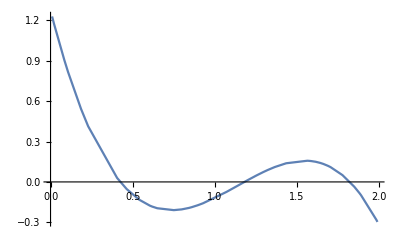

```mathematica
ListLinePlot[Sort@listplotA3,PlotRange->All]
```

```mathematica
Plot[sumtestclp1p2[cl1,p3]
```

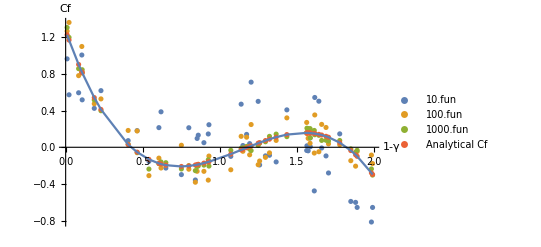

```mathematica
Show[%278,%]
```

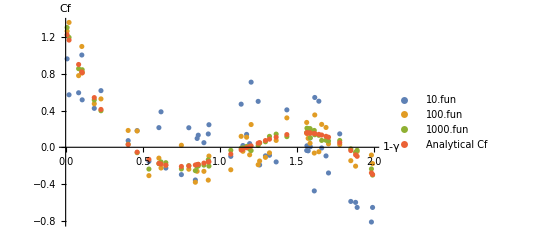

```mathematica
ListPlot[{listplotN310,listplotN3100,listplotN31000,listplotA3},PlotLegends->{"10.fun","100.fun","1000.fun","Analytical Cf"},AxesLabel->{"1-γ","Cf"}]
```

```mathematica
p4= Flatten[Table[{{0.01π,0.01 π},{j π,0.01 π}},{j,0.01,0.99,0.01}],1];Length[p4]
```

```mathematica
p4=Table[{RandomVariate[UniformDistribution[{0,π}]],RandomVariate[UniformDistribution[{0,2π}]]},300];
γp4=Table[normal[p4[[1+j]]].normal[p4[[2+j]]],{j,0,Length[p4]-2,2}];
x4=1-γp4;
```

```mathematica
Randtestcl[cl1,1000,p4]
```

{{0.169174,0.180363,0.523711,-0.0102612,-0.127551,0.560604,-0.187367,0.0162454,0.00942717,-0.0776633,0.311894,1.02274,-0.264455,-0.173339,0.118159,-0.157776,0.558571,0.321502,0.00938059,-0.0914345,0.100148,0.801448,1.18464,-0.0100852,0.147283,0.0256282,-0.00100853,-0.166372,0.195125,0.519997,-0.170925,-0.25959,0.723533,-0.0118406,-0.145754,-0.108011,0.0884357,-0.24713,-0.0648584,-0.0103863,0.919404,0.476274,-0.217053,-0.23897,0.814194,-0.157709,0.558389,0.0571272,-0.203516,0.0404553,-0.138653,0.915454,0.0430175,1.1133,1.01642,-0.232157,0.139563,0.0783899,-0.0282875,-0.135031,-0.0363304,0.146034,0.222194,-0.124952,0.195002,0.0996212,0.206463,-0.0924847,-0.176606,0.354859,-0.0960574,0.0659319,0.159228,0.141445,0.795498,-0.173989,0.0463531,-0.213882,-0.186992,0.0928428,-0.114868,-0.209649,0.000347447,0.160008,-0.153254,-0.127764,-0.153828,-0.0214927,0.520035,-0.198878,-0.142886,0.15971,0.0301895,-0.142453,-0.0735177,-0.202992,-0.175169,0.134289,0.076841,0.320951,0.203824,-0.151598,0.0988567,0.127119,0.138851,0.600749,0.041519,0.397812,-0.106275,-0.248255,-0.224497,-0.147516,0.0751589,0.06096,-0.12394,0.0870159,-0.0895417,0.889703,-0.120249,-0.202477,0.0287136,-0.207472,-0.192448,-0.196861,0.828078,0.14781,0.761284,0.127824,-0.00694748,0.770066,0.0295423,-0.076495,0.77962,0.108332,0.133746,-0.20794,-0.200511,-0.181216,-0.0844013,0.0352275,-0.22352,0.110448,-0.152296,-0.145086,0.0974914,0.558356,-0.109971,0.0993144,0.153905,0.0404932},Mean value,{0.129719,0.118884,0.48891,-0.00371281,-0.176407,0.573288,-0.141558,0.0445671,0.0133783,-0.0537881,0.30061,1.06381,-0.278514,-0.144978,0.149,-0.165541,0.572229,0.285751,-0.0279668,-0.134097,0.0173578,0.746333,1.25748,-0.05574,0.0829954,0.0196549,-0.0301243,-0.17459,0.148485,0.525901,-0.19486,-0.209649,0.688605,-0.0384112,-0.128574,-0.11665,0.0821899,-0.230397,-0.185003,-0.0724653,1.02773,0.448409,-0.201819,-0.209276,0.762616,-0.185001,0.505294,0.00665058,-0.215976,-0.0387976,-0.121724,0.927566,0.0301148,1.15977,0.992005,-0.196464,0.138605,0.0470049,0.00938965,-0.0907494,-0.0382267,0.154929,0.156183,-0.138333,0.116812,0.11996,0.138766,-0.0573655,-0.202586,0.418168,-0.0487769,0.120441,0.0860566,0.157732,0.850807,-0.143575,0.0373486,-0.209602,-0.238399,0.156513,-0.131758,-0.179579,-0.018683,0.157315,-0.209328,-0.0918086,-0.199885,-0.027085,0.540758,-0.203035,-0.147091,0.136053,0.0359652,-0.194604,-0.116996,-0.2077,-0.143475,0.156289,0.076862,0.349445,0.168358,-0.173987,0.121711,0.140636,0.0357033,0.632979,0.0685334,0.496428,-0.0327109,-0.194272,-0.180805,-0.155824,0.115479,0.0999196,-0.184123,0.144343,-0.0818416,0.86459,-0.148203,-0.202538,0.00152391,-0.209656,-0.162718,-0.151852,0.79678,0.0635824,0.816791,0.142844,0.0189019,0.725973,0.0241436,-0.175215,0.733394,0.0755116,0.127378,-0.203761,-0.209652,-0.177771,-0.0877282,0.0102321,-0.187288,0.0432781,-0.129323,-0.182292,0.0719489,0.504931,-0.155053,0.0606778,0.110356,-0.033189},Sum Value}

```mathematica
y41000=meanvalue;listplotN41000=Table[{x4[[i]],y41000[[i]]},{i,1,Length[x4]}];
```

```mathematica
Randtestcl[cl1,100,p4]
```

{{0.322748,0.123172,0.552487,0.0542707,-0.262823,0.628749,-0.185311,0.0610812,-0.029751,-0.159168,0.193784,0.919373,0.00470088,-0.291246,0.135585,-0.242104,0.33951,0.331332,-0.147192,-0.221182,0.0736648,0.816048,1.34346,-0.148986,0.180731,0.0465028,-0.0156403,-0.0699829,0.262227,0.426184,0.0329473,-0.253462,0.657102,-0.14981,-0.247079,-0.0290357,0.119217,-0.128612,-0.41945,-0.255609,1.53024,0.546092,-0.190621,-0.241879,0.680839,-0.487593,0.599614,0.0230479,-0.0767667,-0.0544226,-0.103968,1.09883,-0.139258,1.61608,0.937562,-0.0785317,0.264896,-0.0380051,0.0409599,0.0344215,-0.0184366,0.188446,0.229833,-0.204154,0.0767538,0.11597,-0.0187334,-0.013872,0.0116219,0.209359,0.120837,-0.0175615,0.138889,0.13068,0.774177,-0.248667,0.0843666,-0.250993,-0.143096,0.193103,-0.0594738,-0.160763,-0.0541285,0.172126,-0.27271,0.0124887,-0.192827,0.0718499,0.368713,-0.40189,-0.333531,0.247947,-0.133999,-0.180798,0.0404885,-0.138849,-0.100165,0.0654134,0.0176299,0.68028,0.028686,-0.274464,0.0844874,0.125925,0.144009,0.560137,0.0424322,0.351284,0.0613718,-0.120559,-0.30608,-0.0965692,0.0454692,-0.0831803,-0.235769,0.195231,-0.0776041,0.723126,-0.137282,-0.257047,-0.00965602,-0.154781,-0.0792647,-0.198027,0.628308,0.140307,0.751424,-0.0181428,-0.0331691,0.811735,0.0623195,-0.19571,0.6848,0.0991716,-0.0743705,-0.189679,-0.113124,-0.32617,-0.0651318,-0.237606,-0.219692,0.0810891,-0.0410758,-0.266991,0.0889214,0.39003,-0.0296312,0.133482,0.0875992,0.0146754},Mean value,{0.129719,0.118884,0.48891,-0.00371281,-0.176407,0.573288,-0.141558,0.0445671,0.0133783,-0.0537881,0.30061,1.06381,-0.278514,-0.144978,0.149,-0.165541,0.572229,0.285751,-0.0279668,-0.134097,0.0173578,0.746333,1.25748,-0.05574,0.0829954,0.0196549,-0.0301243,-0.17459,0.148485,0.525901,-0.19486,-0.209649,0.688605,-0.0384112,-0.128574,-0.11665,0.0821899,-0.230397,-0.185003,-0.0724653,1.02773,0.448409,-0.201819,-0.209276,0.762616,-0.185001,0.505294,0.00665058,-0.215976,-0.0387976,-0.121724,0.927566,0.0301148,1.15977,0.992005,-0.196464,0.138605,0.0470049,0.00938965,-0.0907494,-0.0382267,0.154929,0.156183,-0.138333,0.116812,0.11996,0.138766,-0.0573655,-0.202586,0.418168,-0.0487769,0.120441,0.0860566,0.157732,0.850807,-0.143575,0.0373486,-0.209602,-0.238399,0.156513,-0.131758,-0.179579,-0.018683,0.157315,-0.209328,-0.0918086,-0.199885,-0.027085,0.540758,-0.203035,-0.147091,0.136053,0.0359652,-0.194604,-0.116996,-0.2077,-0.143475,0.156289,0.076862,0.349445,0.168358,-0.173987,0.121711,0.140636,0.0357033,0.632979,0.0685334,0.496428,-0.0327109,-0.194272,-0.180805,-0.155824,0.115479,0.0999196,-0.184123,0.144343,-0.0818416,0.86459,-0.148203,-0.202538,0.00152391,-0.209656,-0.162718,-0.151852,0.79678,0.0635824,0.816791,0.142844,0.0189019,0.725973,0.0241436,-0.175215,0.733394,0.0755116,0.127378,-0.203761,-0.209652,-0.177771,-0.0877282,0.0102321,-0.187288,0.0432781,-0.129323,-0.182292,0.0719489,0.504931,-0.155053,0.0606778,0.110356,-0.033189},Sum Value}

```mathematica
y4100=meanvalue;listplotN4100=Table[{x4[[i]],y4100[[i]]},{i,1,Length[x4]}];
```

```mathematica
Randtestcl[cl1,10,p4]
```

{{0.00709818,0.542085,0.258069,-0.175322,-0.745416,0.13242,0.237952,-0.298077,0.0655191,0.130929,-0.0563174,1.45213,-0.0910929,-0.797044,0.630372,0.161084,1.03803,0.361082,-0.269445,0.0313393,-0.123113,1.18619,0.81395,0.106157,0.502178,0.104486,-0.717896,-0.648751,0.471851,0.480406,-1.40824,-0.167821,0.63872,0.114909,0.100085,0.464872,0.63399,-0.372538,-0.178639,-0.101633,1.24584,-0.0338674,-0.199101,-0.330809,0.796473,-0.366034,1.08878,0.454417,-0.264882,0.553571,0.0736369,0.300451,-0.282981,1.702,0.403438,-0.212003,0.707501,0.427764,0.239484,-0.151148,-0.148257,-0.120579,0.348418,-0.216125,-0.0505192,0.524773,-0.0650252,-0.965138,0.57783,0.182968,-0.161571,0.382347,0.00641679,-0.557925,0.647729,-0.293747,0.8678,-0.991045,-0.367097,0.0730365,0.291808,-0.224975,-0.513726,-0.354806,-0.138752,-0.108209,-0.340118,-0.143536,0.604126,-0.837599,-0.918647,0.197066,-0.178074,0.492699,-0.232983,-0.577067,-0.760105,0.401333,-0.226496,-0.0845221,0.322033,0.0396546,0.099325,-0.102465,0.597742,0.431151,-0.0749747,0.529539,-0.0271915,-0.380972,0.131461,-0.460256,-0.174596,0.0651487,0.176653,0.159551,-0.690199,0.296533,-0.529419,-0.401037,0.326978,0.17858,-0.298763,-0.789625,0.360227,0.0737471,1.67822,0.143822,-0.292336,0.299294,-0.258189,-0.16072,1.01858,0.181645,0.0923462,-0.252866,-0.875776,0.188463,-0.708895,0.296861,-0.327322,0.236949,-0.767517,-0.0262895,0.181628,1.02147,-0.479142,0.125881,-0.00765594,0.353095},Mean value,{0.129719,0.118884,0.48891,-0.00371281,-0.176407,0.573288,-0.141558,0.0445671,0.0133783,-0.0537881,0.30061,1.06381,-0.278514,-0.144978,0.149,-0.165541,0.572229,0.285751,-0.0279668,-0.134097,0.0173578,0.746333,1.25748,-0.05574,0.0829954,0.0196549,-0.0301243,-0.17459,0.148485,0.525901,-0.19486,-0.209649,0.688605,-0.0384112,-0.128574,-0.11665,0.0821899,-0.230397,-0.185003,-0.0724653,1.02773,0.448409,-0.201819,-0.209276,0.762616,-0.185001,0.505294,0.00665058,-0.215976,-0.0387976,-0.121724,0.927566,0.0301148,1.15977,0.992005,-0.196464,0.138605,0.0470049,0.00938965,-0.0907494,-0.0382267,0.154929,0.156183,-0.138333,0.116812,0.11996,0.138766,-0.0573655,-0.202586,0.418168,-0.0487769,0.120441,0.0860566,0.157732,0.850807,-0.143575,0.0373486,-0.209602,-0.238399,0.156513,-0.131758,-0.179579,-0.018683,0.157315,-0.209328,-0.0918086,-0.199885,-0.027085,0.540758,-0.203035,-0.147091,0.136053,0.0359652,-0.194604,-0.116996,-0.2077,-0.143475,0.156289,0.076862,0.349445,0.168358,-0.173987,0.121711,0.140636,0.0357033,0.632979,0.0685334,0.496428,-0.0327109,-0.194272,-0.180805,-0.155824,0.115479,0.0999196,-0.184123,0.144343,-0.0818416,0.86459,-0.148203,-0.202538,0.00152391,-0.209656,-0.162718,-0.151852,0.79678,0.0635824,0.816791,0.142844,0.0189019,0.725973,0.0241436,-0.175215,0.733394,0.0755116,0.127378,-0.203761,-0.209652,-0.177771,-0.0877282,0.0102321,-0.187288,0.0432781,-0.129323,-0.182292,0.0719489,0.504931,-0.155053,0.0606778,0.110356,-0.033189},Sum Value}

```mathematica
y410=meanvalue;listplotN410=Table[{x4[[i]],y410[[i]]},{i,1,Length[x4]}];
```

```mathematica
y4a=sumtestclp1p2[cl1,p4];listplotA4=Table[{x4[[i]],y4a[[i]]},{i,1,Length[x4]}];
```

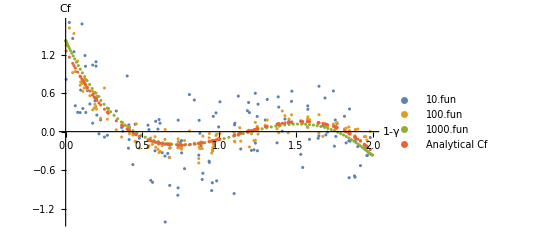

```mathematica
ListPlot[{listplotN410,listplotN4100,listplotN41000,listplotA4},PlotLegends->{"10.fun","100.fun","1000.fun","Analytical Cf"},AxesLabel->{"1-γ","Cf"}]
```

#### Matrices:

The test need to be given the same matrix  in 2 different points: p1=(θ1,ϕ1) and p2=(θ2,ϕ2) and the Cf that was used to create it.
The functions I created generates matrices that are functions of θ and ϕ, it takes a long time to create a big matrix or a set of matrices to check the statistics. There for, I will create a different function that creates 2 random Matrices with the same “a” (random variable), one will be in point p1 and the other at p2.

```mathematica
MMcheckp1p2[Mat_,points_,cl_]:=(lmax=Length[cl]-1;Msize=Length[Mat[[1,1]]];Mnumber=Length[Mat];
Npoints=Length[Mat[[1]]];
M1M2=Table[Mat[[i,j+1]]Conjugate[Mat[[i,j+2]]],{j,0,Npoints-2,2},{i,Mnumber}];meanup={};Do[g={};Do[If[j<k,AppendTo[g,M1M2[[n,i,j,k]]],0],{j,Msize},{k,Msize},{i,Mnumber}];AppendTo[meanup,Mean[g]],{n,Npoints/2}];
meandiag={};
Do[diag={};Do[AppendTo[diag,Tr[Mat[[i,1+j]]Mat[[i,j+2]]]/Msize],{i,Mnumber}];AppendTo[meandiag,Mean[diag]],{j,0,Npoints-2,2}];
Print[{N[sumtestclp1p2[cl,points]],"Sum value",meanup ,"upper mean value",meandiag ,"diagonal mean value", Msize "matrix size",Mnumber"number of matrices",Mnumber(Msize+(Msize^2-Msize)/2) "number of functions"}])(*Statistical check for many matrices*)
```

```mathematica
Mcheckp1p2[Mat_,cl_,points_]:=(Msize=Length[Mat[[1]]];lmax=Length[cl]-1;Npoints=Length[Mat];
meanup={};
M1M2=Table[Mat[[j+1]]Conjugate[Mat[[j+2]]],{j,0,Npoints-2,2}];Do[g={};Do[If[j<k,AppendTo[g,M1M2[[i,j,k]]],0],{j,Msize},{k,Msize}];AppendTo[meanup,Mean[g]],{i,Npoints/2}];
meandiag={};
Do[AppendTo[meandiag,Tr[Mat[[1+i]] Mat[[2+i]]]/Msize],{i,0,Npoints-2,2}]
Print[{sumvalue=N[sumtestclp1p2[cl,points]],"Sum value",meanup,"mean upper value",meandiag,"mean diag value", Msize "Matrix size",(Msize+(Msize^2-Msize)/2) "number of functions used"}])
(*Statistical check for one matrix*)
```

#### Check n1: 2 Big matrices Mat1 & Mat2

```mathematica
cl={0.1,0.2,0.3,0.4,0.1,0};checkp={{0.1,0.2},{0.6,0.6},{0.1,0.2},{1.2,0.4},{0.3,1},{2,3}};
```

```mathematica
M1=randMat[cl,checkp,100];//Timing
```

{207.016,Null}

```mathematica
Mcheckp1p2[M1,cl,checkp]
```

{{0.209648,-0.108151,0.0453014},Sum value,{0.207177-0.00498457 ⅈ,-0.102328-0.0138212 ⅈ,0.0409384-0.00104348 ⅈ},mean upper value,{0.219357,-0.0663064,0.0855125},mean diag value,100 Matrix size,5050 number of functions used}

```mathematica
M2=randMat[cl,checkp,50];//Timing
```

{51.2656,Null}

```mathematica
Mcheckp1p2[M2,cl,checkp]
```

{{0.209648,0.0453014},Sum value,{{0.220652+0.00996839 ⅈ,0.0402927+0.00144587 ⅈ},{0.298341,0.0645624}},mean value,50 Matrix size,1275 number of functions used}

#### Check n2: many small matrices Mat1 & Mat2

```mathematica
M3=randMMat[cl,checkp,4,10];//Timing
```

{3.4375,Null}

```mathematica
M4=randMMat[cl,checkp,4,100];//Timing
```

{32.3281,Null}

```mathematica
M5=randMMat[cl,checkp,4,1000];//Timing
```

{321.953,Null}

```mathematica
MMcheckp1p2[M3,checkp,cl]
```

{{0.209648 Sum value,-0.108151 Sum value,0.0453014 Sum value},{0.224979+0.0298914 ⅈ,-0.110683+0.0612628 ⅈ,0.0534534+0.00681062 ⅈ},upper mean value,{0.319334,-0.00858955},diagonal mean value,4 matrix size,10 number of matrices,100 number of functions}

```mathematica
MMcheckp1p2[M4,checkp,cl]
```

{{0.209648 Sum value,0.0453014 Sum value},{0.203056+0.00446871 ⅈ,0.0437265-0.00595701 ⅈ},upper mean value,{0.167944,0.0244839},diagonal mean value,4 matrix size,100 number of matrices,1000 number of functions}

```mathematica
MMcheckp1p2[M5,checkp,cl]
```

{{0.209648 Sum value,0.0453014 Sum value},{0.203451-0.00270555 ⅈ,0.0412735-0.00681575 ⅈ},upper mean value,{0.195669,0.0502869},diagonal mean value,4 matrix size,1000 number of matrices,10000 number of functions}

## Unitary matrix tests:

Creating the Unitary matrices from a normal distribution:

```mathematica
RR:=RandomReal[NormalDistribution[0,1]];
RC:=RR+I*RR;
RG[n_]:=Table[RC,{n},{n}];
RU[n_]:=Orthogonalize[RG[n]]; (*Creates Unitray matrices of size nxn *)
U=RU[4];
UnitaryMatrixQ[U]
Ut=ConjugateTranspose[U];
UnitaryMatrixQ[Ut]
Ut.U//MatrixForm//Chop
U.Ut//MatrixForm//Chop
```

Umat - Multiplies an existing matrix by a unitary matrix on both sides like so - UMU^t

```mathematica
Umat[Mat_]:=(Msize=Length[Mat[[1]]];Npoints=Length[Mat];U=RU[Msize];Ut=ConjugateTranspose[U];umat={};Do[AppendTo[umat,U.Mat[[i]].Ut],{i,Npoints}];umat)
```

### Check n1:

```mathematica
clu={0.1,0.2,0.8,0.1,0};points
cl={0.1,0.2,0.3,0.4};Cf=Exp[-(2(1-x))^2];lmax=3;clf=Clcalc[Cf,lmax];
rpoints=Table[{RandomVariate[UniformDistribution[{0,π}]],RandomVariate[UniformDistribution[{0,2π}]]},10];
```

{{0.1,0.2},{0.6,0.6},{0.1,0.2},{0.2,0.2}}

```mathematica
Mcheck1=randMat[cl,points,100];//Timing
```

{8.,Null}

```mathematica
Mcheck2=randMat[clu,points,100];//Timing
```

{11.5156,Null}

```mathematica
Mcheck3=randMat[clf,points,100];//Timing
```

{32.25,Null}

```mathematica
Mcheck4=randMat[cl,rpoints,100];//Timing
```

{16.7656,Null}

```mathematica
Mcheck5=randMat[clu,rpoints,100];//Timing
```

{24.0781,Null}

```mathematica
Mcheck6=randMat[clf,rpoints,100];//Timing
```

{73.5,Null}

```mathematica
MatrixForm[umat1]
```

Null

```mathematica
umat1=Umat[Mcheck1];
```

```mathematica
umat2=Umat[Mcheck2];
```

```mathematica
umat3=Umat[Mcheck3];
```

```mathematica
umat4=Umat[Mcheck4];
```

```mathematica
umat5=Umat[Mcheck5];
```

```mathematica
umat6=Umat[Mcheck6];
```

```mathematica
Mcheck[umat1,cl]
```

{0.397887 Sum value,{-0.0249191-1.92345×10^-18 ⅈ,0.00333195+0.00309975 ⅈ,0.0290496-0.00339827 ⅈ,-0.00372407+0.0101255 ⅈ},suppose to be zero,{0.390976,0.429636+4.23432×10^-18 ⅈ},mean value up & diag,100 Matrix size,4 number of points,20200 number of functions used}

```mathematica
Mcheck[umat2,clu]
```

{0.429718 Sum value,{-0.0277314+2.66292×10^-17 ⅈ,0.00813457-9.04802×10^-6 ⅈ,-0.0172796-0.00987877 ⅈ,-0.0111378+0.00817279 ⅈ},suppose to be zero,{0.429394,0.425066-1.63149×10^-17 ⅈ},mean value up & diag,100 Matrix size,4 number of points,20200 number of functions used}

```mathematica
Mcheck[umat3,clf]
```

{0.341229 Sum value,{-0.0398356-2.08339×10^-18 ⅈ,-0.00104798-0.00163051 ⅈ,0.0047233-0.0135997 ⅈ,-0.00046263-0.000183397 ⅈ},suppose to be zero,{0.347711,0.379507+1.05471×10^-19 ⅈ},mean value up & diag,100 Matrix size,4 number of points,20200 number of functions used}

```mathematica
Mcheck[umat4,cl]
```

{0.397887 Sum value,{-0.0142726-6.00728×10^-19 ⅈ,0.0000179118-0.000174011 ⅈ,0.0194826-0.00622776 ⅈ,0.000440059+3.99682×10^-6 ⅈ},suppose to be zero,{0.396081,0.384315+8.38358×10^-18 ⅈ},mean value up & diag,100 Matrix size,10 number of points,50500 number of functions used}

```mathematica
Mcheck[umat5,clu]
```

{0.429718 Sum value,{0.00731965+5.59755×10^-18 ⅈ,0.000596987-0.00239822 ⅈ,-0.00331298+0.00307921 ⅈ,0.00544194-0.00386159 ⅈ},suppose to be zero,{0.426526,0.393073+1.17144×10^-18 ⅈ},mean value up & diag,100 Matrix size,10 number of points,50500 number of functions used}

```mathematica
Mcheck[umat6,clf]
```

{0.341229 Sum value,{0.00561275-1.01836×10^-17 ⅈ,0.000721254+0.0011065 ⅈ,0.00125541+0.0159273 ⅈ,0.0013362+0.00103834 ⅈ},suppose to be zero,{0.342021,0.339552+6.55134×10^-18 ⅈ},mean value up & diag,100 Matrix size,10 number of points,50500 number of functions used}

## Graphs:

### Cf as lmax increases

```mathematica
cfgauss=ⅇ^(-4 (1-x)^2);points=Table[{RandomVariate[UniformDistribution[{0,π}]],RandomVariate[UniformDistribution[{0,2π}]]},400];
```

```mathematica
γ=1-Table[normal[points][[1+j]].normal[points][[2+j]],{j,0,Length[points]-2,2}];
```

```mathematica
Cl1=Table[2π Integrate[LegendreP[k,x] cfgauss,{x,-1,1}],{k,0,1}];
Cf1=sumtestclp1p2[Cl1,points];
list1=Table[{γ[[i]],Cf1[[i]]},{i,1,Length[γ]}];Clg1=ListLinePlot[Sort@list1,PlotLegends->Placed[Style[#,15]&/@{" max=1"},{0.9,0.7}],PlotRange->All,PlotStyle->Orange];
Cl2=Table[2π Integrate[LegendreP[k,x] cfgauss,{x,-1,1}],{k,0,3}];
Cf2=sumtestclp1p2[Cl2,points];
list2=Table[{γ[[i]],Cf2[[i]]},{i,1,Length[γ]}];Clg2=ListLinePlot[Sort@list2,PlotLegends->Placed[Style[#,15]&/@{" max=3"},{0.9,0.7}],PlotRange->All,PlotStyle->Black];
Cl3=Table[2π Integrate[LegendreP[k,x] cfgauss,{x,-1,1}],{k,0,5}];
Cf3=sumtestclp1p2[Cl3,points];
list3=Table[{γ[[i]],Cf3[[i]]},{i,1,Length[γ]}];Clg3=ListLinePlot[Sort@list3,PlotLegends->Placed[Style[#,15]&/@{" max=5"},{0.9,0.7}],PlotRange->All,PlotStyle->Green];
Cl4=Table[2π Integrate[LegendreP[k,x] cfgauss,{x,-1,1}],{k,0,8}];
Cf4=sumtestclp1p2[Cl4,points];
list4=Table[{γ[[i]],Cf4[[i]]},{i,1,Length[γ]}];
Clg4=ListLinePlot[Sort@list4,PlotLegends->Placed[Style[#,15]&/@{" max=8"},{0.9,0.7}],PlotRange->All,PlotStyle->{Red,Dashed}];
CfA=Plot[ⅇ^(-4 (1-(1-x))^2),{x,0,2},PlotLegends->Placed[Style[#,15]&/@{"ⅇ^(-4 SuperscriptBox[(1 - x), 2])"},{0.9,0.7}],PlotStyle->Blue];
```

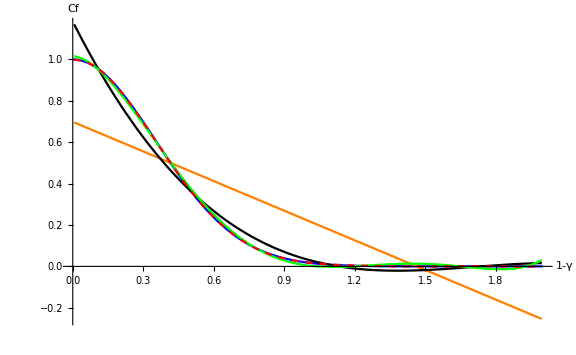

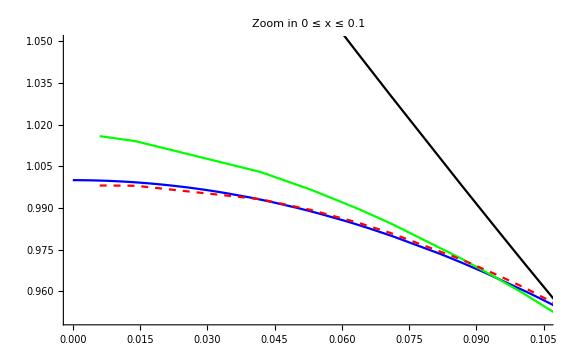

```mathematica
Cftestgraph=Show[CfA,Clg1,Clg2,Clg3,Clg4,PlotRange->All,AxesLabel->{"1-γ","Cf"},AxesStyle->Directive[15,Bold],ImageSize->Large]
Cftestzoom=Show[CfA,Clg2,Clg3,Clg4,PlotRange->{{0,0.105},{0.95,1.05}},AxesStyle->Directive[15,Bold],ImageSize->Large,PlotLabel-> "Zoom in 0 ≤ x ≤ 0.1",LabelStyle-> Directive[15,Bold]]
```

```mathematica
Export["Cf test graph.png",Cftestgraph]
Export["Cf test zoom in.png",Cftestzoom]
```

Cf test graph.png

Cf test zoom in.png

### Histogram

```mathematica
Hpoints=Table[{RandomVariate[UniformDistribution[{0,π}]],RandomVariate[UniformDistribution[{0,2π}]]},300];
```

```mathematica
Hpoints2=Table[{RandomVariate[UniformDistribution[{0,π}]],RandomVariate[UniformDistribution[{0,2π}]]},300];
```

```mathematica
cfgauss=Exp[-(2(1-x))^2]
clgauss=Clcalc[cfgauss,3]
```

ⅇ^(-4 (1-x)^2)

{2.78416,1.99877,0.95,0.191055}

```mathematica
clrect={1,1,1,1};fgauss=randFamilyHS[clgauss,Hpoints,1000];frect=randFamilyHS[clrect,Hpoints,1000];
```

```mathematica
fgauss2=randFamilyHS[clgauss,Hpoints2,1000];frect2=randFamilyHS[clrect,Hpoints2,1000];florents2=randFamilyHS[cllorentz,Hpoints2,1000];
```

```mathematica
cflorentz=1/(1+(10Abs[1-x])^2); cllorentz=Clcalc[cflorentz,8]
```

{0.955571,0.767265,0.564815,0.387094,0.246739,0.144179,0.0743154,0.0301416,0.004678}

```mathematica
florents=randFamilyHS[cllorentz,Hpoints,1000];//Timing
```

{161.219,Null}

Calculating the variance using sumtestcl[cl_]:

```mathematica
varlorentz=sumtestcl[cllorentz]
vargauss=sumtestcl[clgauss]
varrect=sumtestcl[clrect]
```

1.12168

1.18315

4/π

```mathematica
N[4/π]
```

1.27324

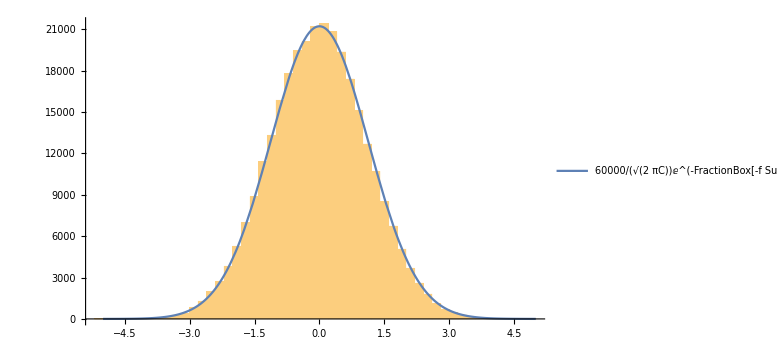

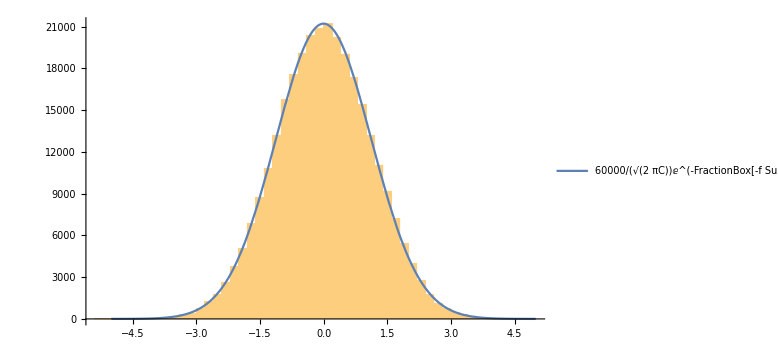

```mathematica
Crect=(300000/5)/Sqrt[2π varrect] Exp[-x^2/(2 varrect)];
Crectplot=Plot[Crect,{x,-5,5},PlotLegends->Placed[Style[#,15]&/@{"60000/(√(2  πC))ⅇ^(-FractionBox[-f SuperscriptBox[(x), 2], 2  C])"},{0.9,0.7}]];
rect=Histogram[Flatten[frect],50,AxesStyle->Directive[15,Bold],ImageSize->Large];
rect2=Histogram[Flatten[frect2],50,AxesStyle->Directive[15,Bold],ImageSize->Large];histrect1=Show[rect,Crectplot,PlotRange->All,AxesStyle->Directive[15,Bold],ImageSize->Large,AxesLabel->{"f(x)"}]
histrect2=Show[rect2,Crectplot,PlotRange->All,AxesStyle->Directive[15,Bold],ImageSize->Large,AxesLabel->{"f(x)"}]
```

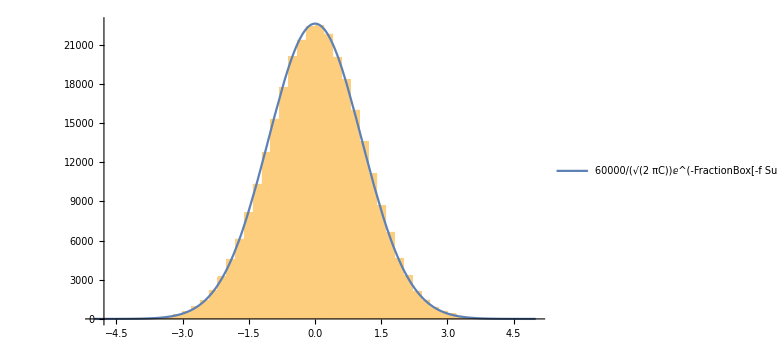

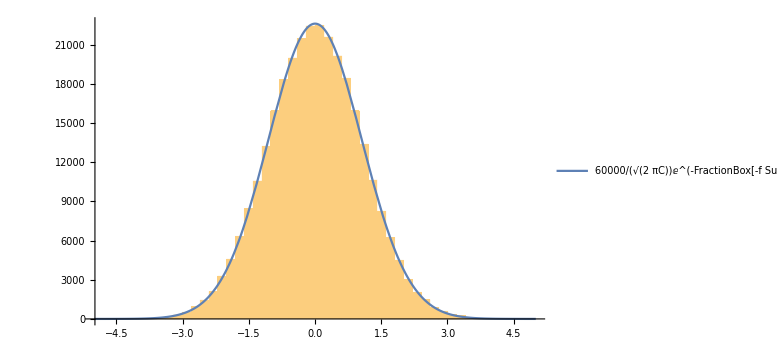

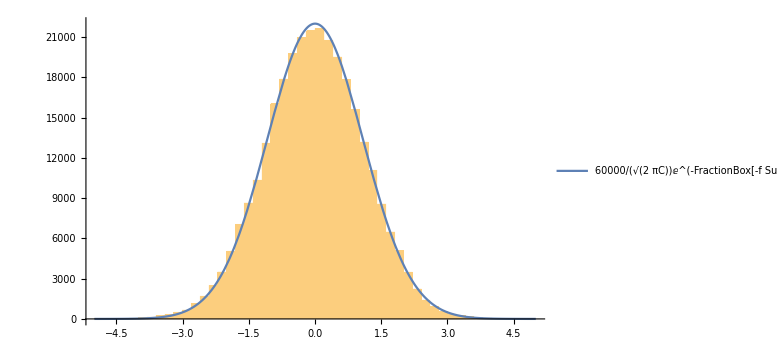

-Graphics-

```mathematica
Clorentz=60000/Sqrt[2π varlorentz] Exp[-x^2/(2 varlorentz)];
Clorenzplot=Plot[Clorentz,{x,-5,5},PlotLegends->Placed[Style[#,15]&/@{"60000/(√(2  πC))ⅇ^(-FractionBox[-f SuperscriptBox[(x), 2], 2  C])"},{0.9,0.7}]];

l=Histogram[Flatten[florents],50,AxesStyle->Directive[15,Bold],ImageSize->Large];
histlorentz1=Show[l,Clorenzplot,PlotRange->All,AxesStyle->Directive[15,Bold],ImageSize->Large,AxesLabel->{"f(x)"}]
l2=Histogram[Flatten[florents2],50,AxesStyle->Directive[15,Bold],ImageSize->Large];
histlorentz2=Show[l2,Clorenzplot,PlotRange->All,AxesStyle->Directive[15,Bold],ImageSize->Large,AxesLabel->{"f(x)"}]

Cgauss=60000/Sqrt[2π vargauss] Exp[-x^2/(2 vargauss)];
Cgaussplot=Plot[Cgauss,{x,-5,5},PlotLegends->Placed[Style[#,15]&/@{"60000/(√(2  πC))ⅇ^(-FractionBox[-f SuperscriptBox[(x), 2], 2  C])"},{0.9,0.7}]];
gaussian=Histogram[Flatten[fgauss],50,AxesStyle->Directive[15,Bold],ImageSize->Large];
histgauss1=Show[gaussian,Cgaussplot,PlotRange->All,AxesStyle->Directive[15,Bold],ImageSize->Large,AxesLabel->{"f(x)"}]
gaussian=Histogram[Flatten[fgauss],50,AxesStyle->Directive[15,Bold],ImageSize->Large];
histgauss2=Show[gaussian,Cgaussplot,PlotRange->All,AxesStyle->Directive[15,Bold],ImageSize->Large,AxesLabel->{"f(x)"}]
```

```mathematica
Export["histogram lorentzian1.png",histlorentz1]
Export["histogram lorentzian2.png",histlorentz2]
Export["histogram gaussian1.png",histgauss1]
Export["histogram gaussian2.png",histgauss2]
Export["histogram rect1.png",histrect1]
Export["histogram rect2.png",histrect2]
```

histogram lorentzian1.png

histogram lorentzian2.png

histogram gaussian1.png

histogram gaussian2.png

histogram rect1.png

histogram rect2.png

### Cf(γ)

```mathematica
(*cfgauss=Exp[-(2(1-x))^2];clgauss=Clcalc[cfgauss,3];*)
Cf1=ⅇ^(-4 (1-x)^2);clg1=Clcalc[ⅇ^(-4 (1-x)^2),3]
```

{2.78416,1.99877,0.95,0.191055}

```mathematica
cfgauss
```

ⅇ^(-4 (1-x)^2)

#### Function graph -g1, for 300 random points gaussian

```mathematica
g1points=Table[{RandomVariate[UniformDistribution[{0,π}]],RandomVariate[UniformDistribution[{0,2π}]]},300];
```

```mathematica
γg1=Table[normal[g1points][[1+j]].normal[g1points][[2+j]],{j,0,Length[g1points]-2,2}];
xg1=1-γg1;
```

```mathematica
(*Randtestcl[clg1,100,g1points]//Timing
Randtestcl[clg1,1000,g1points]//Timing
Randtestcl[clg1,10000,g1points]//Timing*)
```

{{-0.0384964,0.577516,0.024215,0.158193,1.23333},Mean value,{-0.00394414,0.85386,0.00841133,-0.0159684,0.927106},Sum Value}

{0.984375,Null}

{{-0.0171713,0.770785,-0.0409174,-0.0321842,0.867846},Mean value,{-0.00394414,0.85386,0.00841133,-0.0159684,0.927106},Sum Value}

{9.64063,Null}

{{0.00100838,0.867286,0.0104039,0.00216929,0.945006},Mean value,{-0.00394414,0.85386,0.00841133,-0.0159684,0.927106},Sum Value}

{95.2813,Null}

```mathematica
(*rms={Abs[0.8538595230494016-0.5775157675978088],Abs[0.8538595230494016-0.7707850145766333],Abs[0.8538595230494016-0.8672864874995817]}*)
```

```mathematica
Randtestcl[clg1,100,g1points];//Timing
y100g1=meanvalue;
```

{{0.192771,0.339229,0.899804,0.671723,0.404875,-0.352984,0.0885146,-0.311373,0.801295,0.0543169,1.06464,-0.0360074,0.00417703,0.0865135,0.0648022,-0.0874856,-0.0933909,0.0317969,0.463159,0.0878886,1.13931,0.112215,0.274853,-0.0551705,1.01666,0.157675,0.312781,-0.0799683,0.156823,0.848141,0.00965146,0.572831,-0.00953585,0.048731,0.0444981,0.104155,0.754276,0.0393853,0.180412,0.760059,1.13092,0.0682442,0.863908,0.432638,-0.0461376,0.508265,0.209438,0.0210075,-0.0430588,1.20989,0.00170103,0.978239,-0.112266,0.217334,0.0284372,0.405119,0.820349,0.732728,-0.0750694,0.797363,0.147821,0.327002,0.126215,0.144593,0.316541,0.671518,-0.188606,0.693717,0.0205855,0.181768,-0.0778098,0.301795,-0.139943,-0.00695584,0.17219,-0.142613,-0.208927,0.369286,-0.156408,0.685394,-0.0233593,0.19407,0.0955992,0.117456,0.409865,0.715064,0.0895981,0.0441935,1.04359,0.218582,0.726648,-0.0370731,-0.0465842,-0.103936,0.0492648,0.192067,0.129716,1.20307,0.627672,0.399461,0.219699,0.186987,0.981245,0.0130133,0.39305,-0.196728,1.10878,0.103177,-0.0953344,0.208709,0.199222,-0.0183419,-0.143865,-0.0489845,0.00165416,0.0457735,0.0776216,1.26137,-0.00572227,-0.185782,0.0999849,0.221111,-0.271754,0.00161074,-0.185981,0.705209,-0.143542,-0.198045,0.120719,-0.052432,-0.0192255,0.562815,-0.039985,-0.0703874,0.452959,1.06067,-0.0954319,0.0867148,-0.0697295,-0.0859776,0.119476,0.466883,0.939166,0.503521,-0.00400658,0.120208,-0.0760898,-0.0898633,0.711687,-0.134907},Mean value,{0.344331,0.491631,0.89427,0.748161,0.306043,0.0145627,0.0108625,0.00631386,0.611148,0.014714,1.02172,0.0166179,0.0446137,0.127583,-0.0189149,-0.0183124,0.00194963,-0.0201447,0.396945,0.00795488,0.983376,0.242366,-0.0195744,0.0442374,0.879297,0.00306234,0.380727,-0.0200147,0.0071887,0.668441,-0.015092,0.711718,-0.00216633,0.00577867,0.00101342,0.0154493,0.786742,-0.0196812,-0.0167198,0.628061,1.09542,-0.00234729,0.784886,0.536314,0.000656136,0.658459,0.207544,-0.00412559,-0.0181434,1.03241,-0.0111484,0.985769,0.0200458,0.272055,-0.0167735,0.397285,0.978342,0.736854,-0.020067,0.670382,0.139453,0.374115,0.239366,0.0002164,0.198323,0.603678,-0.00648703,0.706011,-0.00401455,0.0543723,-0.0053044,0.156001,0.00814743,0.0246104,0.156859,0.00121908,-0.0178568,0.387063,-0.0052365,0.549441,-0.0144348,0.296891,0.104182,-0.0207079,0.466276,0.92809,0.0271376,-0.0179758,0.803602,0.119922,0.705398,0.00998233,0.0115126,0.0113919,0.10544,0.2714,0.0445363,1.18189,0.602976,0.296426,-0.0173569,0.0300595,1.07921,-0.00406212,0.193462,-0.000408146,1.10526,0.0133561,-0.0105777,0.184209,0.0000832967,0.0149563,-0.0196205,0.00667054,-0.020099,0.00160317,0.0179443,1.10801,-0.0187564,-0.0103763,0.00750264,0.213277,0.0249068,0.0153299,-0.0203502,0.929241,0.00490044,-0.0192733,0.0746168,0.0155277,0.0150187,0.652926,0.0440623,-0.0154765,0.433756,1.13378,0.0152756,-0.00376677,0.0147447,0.00720083,0.0141356,0.514513,0.946171,0.52016,0.0156157,-0.0107682,-0.0188441,-0.0154899,0.599229,-0.0119016},Sum Value}

{4.48438,Null}

```mathematica
listplotN100g1=Table[{xg1[[i]],y100g1[[i]]},{i,1,Length[xg1]}];
```

```mathematica
Randtestcl[clg1,1000,g1points]//Timing
y1000g1=meanvalue;
```

{{0.449718,0.474086,0.898449,0.733577,0.258328,0.0312579,0.0586789,0.0456521,0.624009,0.0531156,1.02782,0.0345014,-0.0264568,0.07221,0.0519357,0.0593846,0.00136571,0.0326398,0.414054,0.04721,1.01615,0.255635,-0.017331,0.0627836,0.912218,0.0504997,0.376898,-0.0028033,0.0498129,0.616081,-0.00794063,0.729173,0.0064067,0.0439168,0.0260109,0.0344795,0.758952,-0.0454395,0.0192585,0.657405,1.09974,0.0351202,0.791994,0.546582,0.0351605,0.644871,0.219265,0.0150916,0.0160891,1.06243,0.0254153,0.965098,0.0467942,0.230007,0.0487715,0.408467,0.927586,0.766023,0.058173,0.687256,0.174206,0.375834,0.23428,0.0711848,0.164423,0.637488,-0.031744,0.704682,0.0302207,0.078111,0.00883959,0.129632,0.075666,0.0579512,0.148814,-0.0136395,-0.00829918,0.453261,0.0450087,0.577962,0.0148033,0.286371,0.110981,0.0131167,0.456491,0.887528,0.0813208,-0.00309765,0.814821,0.140509,0.775387,-0.00675309,0.0222424,-0.020274,0.110861,0.310594,0.0688772,1.16055,0.624943,0.260175,-0.00297347,0.0284343,1.16949,0.0697988,0.159039,-0.0106644,1.11308,0.0622392,0.00236993,0.188854,0.0498323,0.0382152,-0.0346786,-0.0044119,0.0279391,-0.0572974,0.0623788,1.17406,0.0106427,0.0317842,0.0331861,0.198087,0.0190431,0.0558499,-0.0289738,0.895273,0.0103514,-0.0358276,0.0782017,0.00787274,0.0404618,0.683997,0.0473387,0.074637,0.437737,1.19272,0.0106126,0.0412365,0.0394625,0.0484703,0.0561759,0.511805,0.968956,0.544043,0.0489688,0.0278592,0.0136768,0.0242651,0.612525,0.0142591},Mean value,{0.344331,0.491631,0.89427,0.748161,0.306043,0.0145627,0.0108625,0.00631386,0.611148,0.014714,1.02172,0.0166179,0.0446137,0.127583,-0.0189149,-0.0183124,0.00194963,-0.0201447,0.396945,0.00795488,0.983376,0.242366,-0.0195744,0.0442374,0.879297,0.00306234,0.380727,-0.0200147,0.0071887,0.668441,-0.015092,0.711718,-0.00216633,0.00577867,0.00101342,0.0154493,0.786742,-0.0196812,-0.0167198,0.628061,1.09542,-0.00234729,0.784886,0.536314,0.000656136,0.658459,0.207544,-0.00412559,-0.0181434,1.03241,-0.0111484,0.985769,0.0200458,0.272055,-0.0167735,0.397285,0.978342,0.736854,-0.020067,0.670382,0.139453,0.374115,0.239366,0.0002164,0.198323,0.603678,-0.00648703,0.706011,-0.00401455,0.0543723,-0.0053044,0.156001,0.00814743,0.0246104,0.156859,0.00121908,-0.0178568,0.387063,-0.0052365,0.549441,-0.0144348,0.296891,0.104182,-0.0207079,0.466276,0.92809,0.0271376,-0.0179758,0.803602,0.119922,0.705398,0.00998233,0.0115126,0.0113919,0.10544,0.2714,0.0445363,1.18189,0.602976,0.296426,-0.0173569,0.0300595,1.07921,-0.00406212,0.193462,-0.000408146,1.10526,0.0133561,-0.0105777,0.184209,0.0000832967,0.0149563,-0.0196205,0.00667054,-0.020099,0.00160317,0.0179443,1.10801,-0.0187564,-0.0103763,0.00750264,0.213277,0.0249068,0.0153299,-0.0203502,0.929241,0.00490044,-0.0192733,0.0746168,0.0155277,0.0150187,0.652926,0.0440623,-0.0154765,0.433756,1.13378,0.0152756,-0.00376677,0.0147447,0.00720083,0.0141356,0.514513,0.946171,0.52016,0.0156157,-0.0107682,-0.0188441,-0.0154899,0.599229,-0.0119016},Sum Value}

{49.2813,Null}

```mathematica
listplotN1000g1=Table[{xg1[[i]],y1000g1[[i]]},{i,1,Length[xg1]}];
```

```mathematica
Randtestcl[clg1,10000,g1points]//Timing
y10000g1=meanvalue;
```

{{0.34568,0.483839,0.877233,0.742092,0.300015,0.00536206,-0.00546318,-0.0000297813,0.586273,0.0275795,1.0166,0.0143718,0.0492766,0.120563,-0.00438808,-0.0219934,-0.00405665,-0.0289565,0.407097,0.0135958,0.97122,0.220662,-0.0354506,0.0363777,0.878817,0.000338512,0.374458,-0.0201274,0.0092502,0.687873,-0.0330918,0.692623,-0.0121465,-0.0338401,0.00576712,0.0220987,0.792945,-0.0518703,-0.00700937,0.620717,1.08762,0.00947544,0.782302,0.534035,-0.0134193,0.639994,0.205853,-0.0234528,-0.0265955,1.00796,-0.0123969,0.977989,0.010948,0.272242,-0.0485139,0.386897,0.976029,0.70435,-0.0192338,0.657011,0.142734,0.379109,0.22234,0.00148301,0.184126,0.611485,-0.0174514,0.721212,-0.00218696,0.0731239,-0.0155404,0.141846,0.00565328,0.0110824,0.148218,0.00114376,-0.0189651,0.373237,-0.0127943,0.547421,-0.0325101,0.291501,0.0733532,-0.00345215,0.444473,0.918192,0.033117,-0.020436,0.782297,0.1307,0.678964,0.00289398,-0.0173153,0.00562906,0.0813294,0.256077,0.0333293,1.16362,0.581211,0.267265,-0.0175077,0.0235179,1.0628,0.00167449,0.183096,-0.00549754,1.08988,-0.00526474,-0.0167254,0.162009,0.0108302,-0.0158428,-0.018888,-0.000238537,-0.012726,0.0045829,0.0205154,1.11826,-0.026285,-0.0175006,-0.0077894,0.205988,0.00116959,-0.0160995,-0.0257498,0.915666,0.00710955,-0.0143331,0.0588457,-0.000533459,-0.0197338,0.614771,0.0422577,-0.0314991,0.439079,1.1165,0.0226499,0.00755836,0.00300243,0.0144582,0.00636026,0.493138,0.923757,0.534164,-0.0165539,0.00359676,-0.0276405,-0.0024594,0.597868,-0.0135714},Mean value,{0.344331,0.491631,0.89427,0.748161,0.306043,0.0145627,0.0108625,0.00631386,0.611148,0.014714,1.02172,0.0166179,0.0446137,0.127583,-0.0189149,-0.0183124,0.00194963,-0.0201447,0.396945,0.00795488,0.983376,0.242366,-0.0195744,0.0442374,0.879297,0.00306234,0.380727,-0.0200147,0.0071887,0.668441,-0.015092,0.711718,-0.00216633,0.00577867,0.00101342,0.0154493,0.786742,-0.0196812,-0.0167198,0.628061,1.09542,-0.00234729,0.784886,0.536314,0.000656136,0.658459,0.207544,-0.00412559,-0.0181434,1.03241,-0.0111484,0.985769,0.0200458,0.272055,-0.0167735,0.397285,0.978342,0.736854,-0.020067,0.670382,0.139453,0.374115,0.239366,0.0002164,0.198323,0.603678,-0.00648703,0.706011,-0.00401455,0.0543723,-0.0053044,0.156001,0.00814743,0.0246104,0.156859,0.00121908,-0.0178568,0.387063,-0.0052365,0.549441,-0.0144348,0.296891,0.104182,-0.0207079,0.466276,0.92809,0.0271376,-0.0179758,0.803602,0.119922,0.705398,0.00998233,0.0115126,0.0113919,0.10544,0.2714,0.0445363,1.18189,0.602976,0.296426,-0.0173569,0.0300595,1.07921,-0.00406212,0.193462,-0.000408146,1.10526,0.0133561,-0.0105777,0.184209,0.0000832967,0.0149563,-0.0196205,0.00667054,-0.020099,0.00160317,0.0179443,1.10801,-0.0187564,-0.0103763,0.00750264,0.213277,0.0249068,0.0153299,-0.0203502,0.929241,0.00490044,-0.0192733,0.0746168,0.0155277,0.0150187,0.652926,0.0440623,-0.0154765,0.433756,1.13378,0.0152756,-0.00376677,0.0147447,0.00720083,0.0141356,0.514513,0.946171,0.52016,0.0156157,-0.0107682,-0.0188441,-0.0154899,0.599229,-0.0119016},Sum Value}

{534.328,Null}

```mathematica
listplotN10000g1=Table[{xg1[[i]],y10000g1[[i]]},{i,1,Length[xg1]}];
```

True

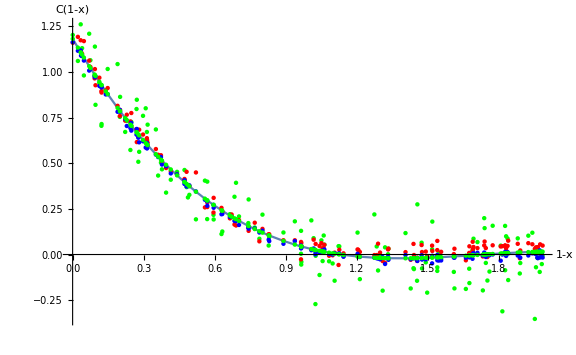

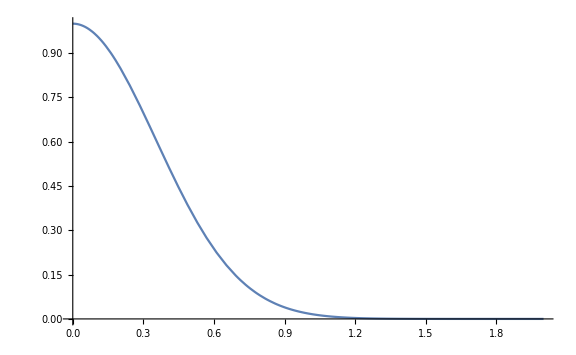

```mathematica
yg1a=sumtestclp1p2[clg1,g1points];listplotAg1=Table[{xg1[[i]],yg1a[[i]]},{i,1,Length[xg1]}];
Cfg1=ListLinePlot[Sort@listplotAg1,PlotRange->All,PlotLegends->Placed[Style[#,15]&/@{" Analytical"},{0.9,0.7}]];
Length[xg1]==Length[yg1a]==Length[listplotAg1];
g1=ListPlot[{Sort@listplotN100g1,Sort@listplotN1000g1,Sort@listplotN10000g1,Sort@listplotAg1},PlotLegends->Placed[Style[#,15]&/@{"100.fun","1000.fun","10,000.fun"},{0.9,0.7}],AxesLabel->{"1-x","C(1-x)"},PlotStyle->{Green,Red,Blue}];
fungraph=Show[Cfg1,g1,PlotRange->All,AxesLabel->{"1-x","C(1-x)"},AxesStyle->Directive[15,Bold],ImageSize->Large]
Plot[Exp[-(2(1-(1-x)))^2],{x,0,2}]
```

```mathematica
Export["function cf graph.png",fungraph]
```

function cf graph.png

#### Matrix graph -g2, diagonal and nondiagonal - Lorenzian

```mathematica
Cf2=1/(1+ 100 Abs[1-x]^2);clg2=Clcalc[Cf2,8]//Timing
```

{0.125,{0.955571,0.767265,0.564815,0.387094,0.246739,0.144179,0.0743154,0.0301416,0.004678}}

```mathematica
cflorentz
```

1/(1+100 Abs[1-x]^2)

```mathematica
g2points=Table[{RandomVariate[UniformDistribution[{0,π}]],RandomVariate[UniformDistribution[{0,2π}]]},400];γg2=Table[normal[g2points][[1+j]].normal[g2points][[2+j]],{j,0,Length[g2points]-2,2}];
xg2=1-γg2;
```

```mathematica
(*M10=randMMat[clg2,g2points,3,10];//(*Timing*)*)
M50=randMMat[clg2,g2points,3,50];//Timing
M100=randMMat[clg2,g2points,3,100];//Timing
M500=randMMat[clg2,g2points,3,500];//Timing
```

{18.25,Null}

{35.1094,Null}

{179.141,Null}

```mathematica
MMcheckp1p2[M500,g2points,clg2]
up500g2=meanup;diag500g2=meandiag;
listplotN500up2=Table[{xg2[[i]],Re[up500g2[[i]]]},{i,1,Length[xg2]}];
listplotN500diag2=Table[{xg2[[i]],diag500g2[[i]]},{i,1,Length[xg2]}];
```

{{{0.0668397,0.0556284,0.043575,0.0329939,0.0246375,0.0185313,0.0143718,0.0117417,0.0102257},{0.1702,0.13862,0.104669,0.0748643,0.0513263,0.0341265,0.0224102,0.015002,0.0107317},{-0.135052,-0.106478,-0.0757583,-0.0487907,-0.0274932,-0.0119306,-0.0013295,0.00537347,0.00923734},{-0.123711,-0.097372,-0.0690549,-0.0441966,-0.0245648,-0.0102195,-0.000447497,0.0057312,0.00929286},{0.036353,0.0311495,0.0255551,0.020644,0.0167655,0.0139314,0.0120008,0.0107801,0.0100765},{0.207406,0.168494,0.12666,0.089936,0.0609333,0.0397402,0.0253037,0.0161756,0.0109138},{-0.169914,-0.134471,-0.0963647,-0.0629133,-0.0364951,-0.0171908,-0.00404078,0.0042738,0.00906667},{0.222742,0.180809,0.135725,0.0961488,0.0648934,0.0420543,0.0264964,0.0166594,0.0109889},{-0.130353,-0.102705,-0.0729808,-0.0468872,-0.0262799,-0.0112216,-0.00096405,0.00552169,0.00926034},{0.0554371,0.0464728,0.0368352,0.0283748,0.0216932,0.0168108,0.013485,0.0113821,0.0101699},{-0.0758025,-0.0589046,-0.0407374,-0.0247893,-0.0121944,-0.00299095,0.00327836,0.00724238,0.0095274},{0.0315618,0.0273024,0.0227231,0.0187031,0.0155283,0.0132085,0.0116282,0.010629,0.010053},{0.159655,0.130153,0.0984356,0.0705924,0.0486033,0.0325354,0.02159,0.0146694,0.0106801},{-0.0895227,-0.069921,-0.0488471,-0.0303473,-0.0157371,-0.00506108,0.00221134,0.0068096,0.00946023},{-0.125979,-0.0991935,-0.0703957,-0.0451155,-0.0251506,-0.0105617,-0.000623919,0.00565965,0.00928176},{0.0461241,0.038995,0.0313305,0.0246022,0.0192885,0.0154057,0.0127607,0.0110883,0.0101243},{0.0903648,0.0745176,0.0574801,0.0425237,0.0307119,0.0220808,0.0162013,0.0124838,0.0103409},{-0.115864,-0.0910718,-0.064417,-0.0410181,-0.0225388,-0.00903559,0.000162723,0.0059787,0.00933127},{-0.106732,-0.0837387,-0.0590189,-0.0373184,-0.0201806,-0.0076576,0.000872989,0.00626678,0.00937598},{-0.00481014,-0.00190204,0.00122448,0.00396911,0.00613667,0.00772056,0.0087995,0.00948169,0.00987494},{-0.0444671,-0.0337442,-0.0222158,-0.0120956,-0.00410322,0.00173701,0.00571534,0.00823079,0.0096808},{0.209213,0.169946,0.127729,0.0906682,0.0613999,0.0400129,0.0254442,0.0162326,0.0109227},{0.00576552,0.00658957,0.0074755,0.00825323,0.00886743,0.00931624,0.00962197,0.00981528,0.00992671},{-0.18268,-0.144721,-0.10391,-0.0680846,-0.0397914,-0.0191169,-0.00503359,0.00387113,0.00900418},{0.0155931,0.0144805,0.0132844,0.0122343,0.011405,0.0107991,0.0103863,0.0101253,0.00997482},{0.229072,0.185891,0.139467,0.0987129,0.0665277,0.0430093,0.0269887,0.0168591,0.0110199},{0.228729,0.185616,0.139264,0.0985741,0.0664393,0.0429576,0.026962,0.0168482,0.0110182},{-0.05734,-0.0440803,-0.0298247,-0.0173103,-0.00742714,-0.000205274,0.00471421,0.00782474,0.00961778},{0.176797,0.143917,0.108568,0.0775367,0.0530297,0.0351219,0.0229232,0.0152101,0.010764},{0.176391,0.143591,0.108328,0.0773722,0.0529249,0.0350607,0.0228916,0.0151973,0.010762},{0.233551,0.189487,0.142114,0.100527,0.0676843,0.0436851,0.027337,0.0170003,0.0110418},{0.0309003,0.0267713,0.0223321,0.0184351,0.0153575,0.0131086,0.0115767,0.0106081,0.0100498},{0.233869,0.189743,0.142302,0.100656,0.0677664,0.0437331,0.0273618,0.0170104,0.0110434},{-0.0914192,-0.0714438,-0.0499681,-0.0311155,-0.0162268,-0.00534723,0.00206385,0.00674978,0.00945094},{0.0584405,0.0488844,0.0386105,0.0295915,0.0224687,0.017264,0.0137185,0.0114768,0.0101846},{-0.154263,-0.121904,-0.0871135,-0.056573,-0.0324538,-0.0148293,-0.00282356,0.00476749,0.00914329},{0.00742976,0.00792584,0.00845919,0.00892739,0.00929715,0.00956735,0.0097514,0.00986778,0.00993486},{-0.199428,-0.158168,-0.113809,-0.0748689,-0.0441158,-0.0216438,-0.00633606,0.00334286,0.00892219},{-0.0528276,-0.0404571,-0.0271575,-0.0154824,-0.00626198,0.000475573,0.00506515,0.00796708,0.00963987},{0.0219288,0.0195677,0.0170292,0.0148008,0.013041,0.011755,0.010879,0.0103251,0.0100058},{-0.0964133,-0.0754538,-0.05292,-0.0331386,-0.0175163,-0.00610075,0.00167545,0.00659225,0.0094265},{-0.0809568,-0.0630431,-0.043784,-0.0268773,-0.0135253,-0.00376864,0.00287751,0.00707979,0.00950216},{0.171686,0.139813,0.105547,0.0754661,0.0517099,0.0343507,0.0225257,0.0150489,0.010739},{-0.0184163,-0.0128269,-0.00681778,-0.00154262,0.00262342,0.00566764,0.00774134,0.00905251,0.00980833},{0.00718208,0.00772697,0.0083128,0.00882706,0.0092332,0.00952998,0.00973214,0.00985996,0.00993365},{0.102892,0.084576,0.0648845,0.0475983,0.0339466,0.0239709,0.0171756,0.0128789,0.0104022},{0.139188,0.11372,0.0863385,0.0623017,0.0433187,0.0294474,0.0199984,0.0140238,0.0105799},{0.136455,0.111525,0.084723,0.0611945,0.042613,0.029035,0.0197858,0.0139376,0.0105665},{-0.195281,-0.154839,-0.111358,-0.0731892,-0.0430452,-0.0210182,-0.00601359,0.00347365,0.00894249},{-0.110462,-0.0867339,-0.0612238,-0.0388296,-0.0211438,-0.00822044,0.000582879,0.00614911,0.00935772},{-0.0147081,-0.00984953,-0.00462599,-0.0000404882,0.00358089,0.00622713,0.00802972,0.00916948,0.00982648},{0.0238045,0.0210737,0.0181379,0.0155607,0.0135253,0.012038,0.0110249,0.0103843,0.010015},{0.115651,0.0948211,0.0724264,0.0527671,0.0372412,0.0258961,0.0181679,0.0132814,0.0104647},{0.215699,0.175153,0.131562,0.0932955,0.0630746,0.0409915,0.0259486,0.0164372,0.0109544},{0.190827,0.155183,0.116861,0.0832201,0.0566524,0.0372388,0.0240143,0.0156527,0.0108327},{-0.13515,-0.106557,-0.0758165,-0.0488306,-0.0275186,-0.0119455,-0.00133715,0.00537037,0.00923686},{0.180152,0.146611,0.110551,0.0788959,0.0538961,0.0356282,0.0231842,0.015316,0.0107804},{0.184457,0.150068,0.113096,0.0806395,0.0550075,0.0362776,0.0235189,0.0154517,0.0108015},{0.0521242,0.0438127,0.034877,0.0270327,0.0208378,0.016311,0.0132273,0.0112776,0.0101537},{0.0738371,0.0612469,0.047711,0.0358285,0.0264443,0.0195871,0.0149159,0.0119625,0.01026},{0.0948268,0.0781003,0.0601175,0.0443312,0.0318641,0.022754,0.0165483,0.0126245,0.0103627},{0.059199,0.0494933,0.0390587,0.0298987,0.0226646,0.0173784,0.0137775,0.0115007,0.0101883},{0.132526,0.10837,0.0824005,0.0596028,0.0415984,0.0284422,0.0194802,0.0138137,0.0105473},{-0.168722,-0.133513,-0.0956597,-0.0624301,-0.0361872,-0.0170108,-0.00394803,0.00431142,0.00907251},{0.0724631,0.0601436,0.0468988,0.0352719,0.0260895,0.0193797,0.0148091,0.0119191,0.0102532},{0.141754,0.11578,0.0878552,0.0633412,0.0439813,0.0298346,0.0201979,0.0141048,0.0105924},{0.0826148,0.0682948,0.0528993,0.0393843,0.0287108,0.0209115,0.0155986,0.0122393,0.0103029},{0.148809,0.121445,0.0920254,0.0661992,0.045803,0.0308991,0.0207466,0.0143273,0.010627},{-0.113191,-0.0889253,-0.0628369,-0.0399351,-0.0218485,-0.00863223,0.000370627,0.00606302,0.00934436},{0.0999645,0.0822256,0.0631543,0.0464125,0.0331907,0.0235292,0.0169479,0.0127866,0.0103879},{0.182969,0.148873,0.112217,0.0800371,0.0546235,0.0360532,0.0234033,0.0154048,0.0107942},{0.196471,0.159714,0.120197,0.0855063,0.0581097,0.0380903,0.0244532,0.0158307,0.0108603},{-0.0599311,-0.0461608,-0.0313562,-0.01836,-0.0080962,-0.000596233,0.00451269,0.00774301,0.00960509},{-0.189349,-0.150075,-0.107852,-0.070786,-0.0415133,-0.0201231,-0.00555222,0.00366078,0.00897153},{0.0845694,0.0698642,0.0540546,0.040176,0.0292155,0.0212064,0.0157506,0.012301,0.0103125},{-0.0222069,-0.0158705,-0.0090583,-0.00307815,0.00164464,0.0050957,0.00744654,0.00893295,0.00978977},{0.0439128,0.0372195,0.0300234,0.0237064,0.0187175,0.015072,0.0125887,0.0110186,0.0101135},{-0.0386302,-0.0290574,-0.0187657,-0.0097311,-0.00259604,0.00261771,0.00616929,0.00841491,0.00970937},{0.208602,0.169455,0.127368,0.0904208,0.0612422,0.0399208,0.0253967,0.0162134,0.0109197},{-0.12632,-0.0994669,-0.070597,-0.0452535,-0.0252385,-0.0106131,-0.0006504,0.00564891,0.00928009},{0.228531,0.185456,0.139147,0.0984936,0.066388,0.0429276,0.0269466,0.016842,0.0110173},{-0.217685,-0.172827,-0.124601,-0.0822646,-0.04883,-0.0243985,-0.00775592,0.00276698,0.00883281},{-0.00207732,0.000292246,0.00283979,0.00507616,0.00684232,0.0081329,0.00901203,0.00956789,0.00988832},{0.144138,0.117694,0.0892644,0.0643069,0.0445969,0.0301943,0.0203833,0.01418,0.0106041},{-0.0555664,-0.0426562,-0.0287763,-0.0165918,-0.00696917,0.0000623313,0.00485214,0.00788069,0.00962646},{0.11962,0.0980076,0.0747721,0.0543747,0.0382659,0.0264949,0.0184765,0.0134066,0.0104841},{0.144939,0.118337,0.0897377,0.0646313,0.0448037,0.0303151,0.0204456,0.0142052,0.010608},{0.194831,0.158398,0.119228,0.0848421,0.0576863,0.0378429,0.0243257,0.015779,0.0108523},{0.232042,0.188276,0.141222,0.0999162,0.0672947,0.0434575,0.0272197,0.0169527,0.0110345},{-0.198824,-0.157683,-0.113452,-0.0746241,-0.0439598,-0.0215527,-0.00628907,0.00336191,0.00892515},{-0.127625,-0.100515,-0.0713685,-0.0457822,-0.0255756,-0.0108101,-0.000751914,0.00560773,0.0092737},{-0.000373021,0.00166069,0.00384716,0.00576655,0.00728239,0.00839005,0.00914457,0.00962165,0.00989666},{-0.135409,-0.106765,-0.0759696,-0.0489355,-0.0275855,-0.0119846,-0.0013573,0.00536219,0.00923559},{-0.102053,-0.0799818,-0.0562532,-0.035423,-0.0189724,-0.00695163,0.00123688,0.00641437,0.00939889},{0.0899851,0.0742128,0.0572557,0.0423699,0.0306139,0.0220235,0.0161718,0.0124718,0.010339},{-0.0942683,-0.0737315,-0.0516521,-0.0322697,-0.0169625,-0.00577711,0.00184227,0.00665991,0.009437},{0.0368641,0.0315598,0.0258571,0.020851,0.0168974,0.0140085,0.0120405,0.0107962,0.010079},{0.00654356,0.00721428,0.00793538,0.0085684,0.00906833,0.00943364,0.00968248,0.00983982,0.00993052},{0.118777,0.0973308,0.0742739,0.0540332,0.0380483,0.0263677,0.018411,0.01338,0.01048},{-0.00103567,0.00112862,0.00345548,0.00549812,0.00711128,0.00829006,0.00909304,0.00960075,0.00989342},{0.181229,0.147476,0.111188,0.0793322,0.0541742,0.0357907,0.0232679,0.01535,0.0107857},{0.235128,0.190754,0.143046,0.101166,0.0680916,0.0439231,0.0274597,0.0170501,0.0110496},{0.0738977,0.0612956,0.0477468,0.035853,0.02646,0.0195962,0.0149207,0.0119644,0.0102603},{0.180458,0.146857,0.110732,0.0790198,0.0539751,0.0356743,0.023208,0.0153256,0.0107819},{0.0539435,0.0452735,0.0359523,0.0277697,0.0213075,0.0165855,0.0133688,0.011335,0.0101626},{0.148462,0.121166,0.0918197,0.0660582,0.0457132,0.0308466,0.0207195,0.0143164,0.0106253},{0.0283935,0.0247584,0.0208504,0.0174196,0.0147102,0.0127304,0.0113818,0.010529,0.0100375},{0.0684475,0.0569194,0.0445253,0.0336452,0.0250526,0.0187739,0.0144968,0.0117925,0.0102336},{-0.0466744,-0.0355165,-0.0235205,-0.0129897,-0.00467315,0.00140398,0.00554368,0.00816117,0.00966999},{0.215341,0.174866,0.131351,0.0931505,0.0629822,0.0409375,0.0259208,0.0164259,0.0109527},{-0.0000462481,0.00192307,0.0040403,0.00589893,0.00736676,0.00843935,0.00916999,0.00963196,0.00989826},{0.203814,0.165611,0.124537,0.0884812,0.0600059,0.0391984,0.0250244,0.0160624,0.0108963},{-0.195002,-0.154614,-0.111193,-0.0730759,-0.042973,-0.020976,-0.00599184,0.00348247,0.00894386},{-0.201949,-0.160192,-0.1153,-0.0758902,-0.0447669,-0.0220242,-0.00653214,0.00326333,0.00890984},{0.0342209,0.0294375,0.0242948,0.0197803,0.0162149,0.0136097,0.011835,0.0107129,0.010066},{0.226035,0.183452,0.137671,0.0974824,0.0657434,0.042551,0.0267525,0.0167632,0.011005},{-0.157772,-0.124721,-0.0891874,-0.0579943,-0.0333597,-0.0153586,-0.00309643,0.00465682,0.00912612},{0.18454,0.150135,0.113145,0.0806734,0.0550291,0.0362902,0.0235254,0.0154544,0.0108019},{-0.140232,-0.110637,-0.07882,-0.0508891,-0.0288307,-0.0127122,-0.00173234,0.00521008,0.00921198},{-0.0913365,-0.0713774,-0.0499192,-0.031082,-0.0162054,-0.00533475,0.00207028,0.00675239,0.00945135},{-0.111309,-0.0874143,-0.0617246,-0.0391728,-0.0213626,-0.0083483,0.000516978,0.00612238,0.00935357},{-0.202642,-0.160749,-0.115709,-0.076171,-0.0449458,-0.0221288,-0.00658603,0.00324147,0.00890645},{-0.213733,-0.169654,-0.122265,-0.0806636,-0.0478095,-0.0238022,-0.00744855,0.00289164,0.00885216},{-0.209115,-0.165946,-0.119535,-0.0787932,-0.0466172,-0.0231055,-0.00708945,0.00303729,0.00887476},{0.189367,0.15401,0.115998,0.0826287,0.0562755,0.0370185,0.0239008,0.0156066,0.0108255},{0.122486,0.100309,0.076466,0.0555356,0.0390059,0.0269273,0.0186994,0.013497,0.0104981},{0.121452,0.0994787,0.075855,0.0551169,0.038739,0.0267713,0.018619,0.0134644,0.0104931},{0.213833,0.173655,0.130459,0.0925398,0.0625929,0.04071,0.0258036,0.0163784,0.0109453},{0.167591,0.136526,0.103127,0.0738075,0.0506527,0.0337329,0.0222073,0.0149198,0.0107189},{0.221554,0.179854,0.135023,0.0956673,0.0645865,0.0418749,0.026404,0.0166219,0.0109831},{-0.147138,-0.116182,-0.0829019,-0.0536866,-0.0306139,-0.0137542,-0.00226942,0.00499225,0.00917817},{0.00417708,0.00531414,0.00653661,0.00760976,0.00845728,0.00907658,0.00949844,0.00976518,0.00991894},{-0.186726,-0.147969,-0.106301,-0.0697234,-0.040836,-0.0197273,-0.00534821,0.00374352,0.00898437},{0.0472578,0.0399053,0.0320006,0.0250614,0.0195812,0.0155767,0.0128489,0.0111241,0.0101298},{-0.064033,-0.0494543,-0.0337807,-0.0200216,-0.00915534,-0.00121513,0.00419369,0.00761362,0.00958501},{0.0892294,0.073606,0.056809,0.0420638,0.0304188,0.0219095,0.016113,0.012448,0.0103353},{0.172314,0.140318,0.105918,0.0757206,0.0518721,0.0344455,0.0225746,0.0150687,0.0107421},{-0.0884155,-0.0690321,-0.0481927,-0.0298988,-0.0154512,-0.00489403,0.00229744,0.00684452,0.00946565},{0.108485,0.0890674,0.0681908,0.0498642,0.0353909,0.0248149,0.0176106,0.0130554,0.0104296},{-0.0750514,-0.0583015,-0.0402935,-0.0244851,-0.0120004,-0.00287762,0.00333678,0.00726607,0.00953107},{-0.208631,-0.165558,-0.119249,-0.0785972,-0.0464923,-0.0230325,-0.00705183,0.00305255,0.00887713},{-0.0981077,-0.0768143,-0.0539215,-0.033825,-0.0179538,-0.00635641,0.00154367,0.0065388,0.0094182},{0.0809952,0.0669944,0.051942,0.0387281,0.0282926,0.0206671,0.0154726,0.0121883,0.010295},{0.202239,0.164346,0.123606,0.0878429,0.0595991,0.0389606,0.0249018,0.0160127,0.0108885},{-0.150441,-0.118835,-0.0848547,-0.0550249,-0.031467,-0.0142527,-0.00252636,0.00488804,0.009162},{-0.126084,-0.0992776,-0.0704576,-0.045158,-0.0251776,-0.0105776,-0.000632066,0.00565634,0.00928124},{-0.182063,-0.144226,-0.103546,-0.0678347,-0.0396322,-0.0190239,-0.00498562,0.00389058,0.00900719},{-0.200849,-0.159309,-0.114649,-0.0754445,-0.0444827,-0.0218582,-0.00644656,0.00329804,0.00891523},{-0.0475648,-0.0362315,-0.0240468,-0.0133505,-0.00490308,0.00126962,0.00547443,0.00813308,0.00966563},{0.190802,0.155163,0.116846,0.0832102,0.0566461,0.0372351,0.0240124,0.0156519,0.0108326},{-0.0732963,-0.0568923,-0.0392561,-0.0237741,-0.0115473,-0.00261281,0.00347327,0.00732143,0.00953966},{0.00536131,0.00626501,0.00723658,0.00808948,0.00876306,0.00925526,0.00959054,0.00980253,0.00992473},{-0.203478,-0.16142,-0.116203,-0.0765097,-0.0451617,-0.022255,-0.00665107,0.00321509,0.00890236},{-0.174509,-0.13816,-0.0990807,-0.0647746,-0.0376816,-0.0178841,-0.00439814,0.00412886,0.00904418},{0.182548,0.148535,0.111967,0.0798664,0.0545147,0.0359896,0.0233705,0.0153915,0.0107922},{0.0921251,0.075931,0.0585206,0.0432368,0.0311665,0.0223464,0.0163382,0.0125393,0.0103495},{0.192685,0.156675,0.117959,0.0839728,0.0571322,0.0375191,0.0241588,0.0157113,0.0108418},{0.235517,0.191066,0.143276,0.101324,0.0681919,0.0439817,0.0274899,0.0170623,0.0110515},{-0.189108,-0.149882,-0.10771,-0.0706886,-0.0414512,-0.0200868,-0.00553351,0.00366836,0.00897271},{0.218975,0.177783,0.133498,0.0946225,0.0639205,0.0414858,0.0262034,0.0165406,0.0109705},{-0.0179915,-0.0124858,-0.00656669,-0.00137054,0.0027331,0.00573173,0.00777437,0.00906591,0.00981041},{-0.0905862,-0.070775,-0.0494757,-0.0307781,-0.0160117,-0.00522155,0.00212863,0.00677605,0.00945502},{0.184208,0.149868,0.112949,0.0805389,0.0549434,0.0362401,0.0234996,0.0154439,0.0108003},{0.123369,0.101018,0.0769879,0.0558933,0.0392339,0.0270605,0.0187681,0.0135248,0.0105024},{0.108695,0.0892357,0.0683147,0.0499492,0.035445,0.0248465,0.0176269,0.013062,0.0104306},{-0.0108071,-0.00671723,-0.00232017,0.0015398,0.00458819,0.00681573,0.00833311,0.00929253,0.00984558},{0.220847,0.179287,0.134605,0.0953809,0.0644039,0.0417683,0.026349,0.0165996,0.0109796},{0.205646,0.167081,0.12562,0.0892232,0.0604789,0.0394747,0.0251668,0.0161201,0.0109052},{-0.106352,-0.0834339,-0.0587944,-0.0371646,-0.0200826,-0.00760032,0.000902517,0.00627875,0.00937784},{-0.21372,-0.169644,-0.122257,-0.0806587,-0.0478063,-0.0238003,-0.00744761,0.00289203,0.00885222},{-0.0410177,-0.0309745,-0.020177,-0.0106983,-0.00321254,0.00225747,0.00598361,0.0083396,0.00969768},{-0.182383,-0.144482,-0.103734,-0.067964,-0.0397146,-0.019072,-0.00501044,0.00388052,0.00900563},{0.125556,0.102774,0.0782808,0.0567794,0.0397987,0.0273905,0.0189382,0.0135938,0.0105131},{0.225087,0.182691,0.137111,0.0970986,0.0654988,0.042408,0.0266788,0.0167334,0.0110004},{0.149617,0.122094,0.0925029,0.0665264,0.0460116,0.031021,0.0208094,0.0143528,0.0106309},{0.0772222,0.0639649,0.0497118,0.0371997,0.0273184,0.0200978,0.0151792,0.0120692,0.0102765},{0.0591287,0.049437,0.0390172,0.0298702,0.0226464,0.0173678,0.0137721,0.0114985,0.010188},{-0.0832358,-0.064873,-0.0451311,-0.0278005,-0.0141137,-0.0041125,0.00270027,0.00700791,0.00949101},{-0.0231479,-0.0166262,-0.00961454,-0.00345937,0.00140165,0.00495371,0.00737335,0.00890326,0.00978517},{0.134828,0.110219,0.0837611,0.0605353,0.0421928,0.0287895,0.0196592,0.0138863,0.0105585},{-0.122028,-0.0960208,-0.0680602,-0.0435149,-0.0241303,-0.00996557,-0.000316626,0.00578428,0.0093011},{-0.213945,-0.169825,-0.12239,-0.0807498,-0.0478644,-0.0238343,-0.00746509,0.00288493,0.00885112},{-0.204681,-0.162386,-0.116914,-0.0769968,-0.0454722,-0.0224364,-0.00674458,0.00317716,0.00889647},{-0.118081,-0.0928514,-0.0657271,-0.0419159,-0.0231111,-0.00936999,-9.64402×10^-6,0.00590879,0.00932042},{-0.189096,-0.149872,-0.107702,-0.0706836,-0.041448,-0.0200849,-0.00553255,0.00366875,0.00897277},{0.200302,0.162791,0.122462,0.0870585,0.0590991,0.0386684,0.0247512,0.0159516,0.0108791},{0.0519586,0.0436798,0.0347791,0.0269657,0.020795,0.016286,0.0132144,0.0112724,0.0101529},{0.222787,0.180845,0.135752,0.0961669,0.0649049,0.042061,0.0264999,0.0166608,0.0109891},{-0.138757,-0.109453,-0.0779483,-0.0502916,-0.0284499,-0.0124897,-0.00161765,0.0052566,0.0092192},{-0.135328,-0.1067,-0.0759215,-0.0489026,-0.0275645,-0.0119723,-0.00135097,0.00536476,0.00923599},{-0.0857003,-0.0668519,-0.0465878,-0.0287988,-0.0147501,-0.00448435,0.00250861,0.00693017,0.00947894},{0.00301826,0.00438368,0.00585166,0.00714033,0.00815806,0.00890173,0.00940832,0.00972862,0.00991326},{0.213461,0.173356,0.130239,0.092389,0.0624968,0.0406539,0.0257746,0.0163666,0.0109435},{-0.0176215,-0.0121888,-0.00634799,-0.00122066,0.00282864,0.00578755,0.00780315,0.00907758,0.00981222},{-0.0561158,-0.0430973,-0.0291011,-0.0168144,-0.00711104,-0.0000205656,0.00480942,0.00786336,0.00962377},{-0.070593,-0.0547216,-0.0376582,-0.022679,-0.0108492,-0.00220492,0.00368352,0.0074067,0.0095529},{0.0597118,0.0499051,0.0393619,0.0301064,0.022797,0.0174558,0.0138174,0.0115169,0.0101908},{-0.209213,-0.166025,-0.119593,-0.0788328,-0.0466425,-0.0231202,-0.00709706,0.00303421,0.00887428},{-0.107086,-0.0840236,-0.0592286,-0.0374622,-0.0202722,-0.00771114,0.000845393,0.00625559,0.00937425},{-0.118133,-0.0928938,-0.0657582,-0.0419373,-0.0231247,-0.00937795,-0.0000137453,0.00590713,0.00932016}},Sum value,{{0.0651352-0.00116329 ⅈ,0.0542869-0.00119678 ⅈ,0.0426141-0.00118901 ⅈ,0.0323541-0.00112397 ⅈ,0.0242364-0.00100546 ⅈ,0.0182883-0.000845681 ⅈ,0.0142188-0.000657801 ⅈ,0.0116257-0.000448744 ⅈ,0.0100999-0.00018927 ⅈ},{0.170758-0.00140004 ⅈ,0.139161-0.00107597 ⅈ,0.10517-0.00073559 ⅈ,0.0753035-0.00044746 ⅈ,0.0516848-0.000232223 ⅈ,0.0343916-0.0000883621 ⅈ,0.0225743-4.85744×10^-6 ⅈ,0.0150598+0.0000313912 ⅈ,0.0106626+0.000026806 ⅈ},{-0.135614-0.00874503 ⅈ,-0.106973-0.007459 ⅈ,-0.0761777-0.00600353 ⅈ,-0.0491418-0.00462894 ⅈ,-0.0277874-0.0034316 ⅈ,-0.01218-0.00243487 ⅈ,-0.00154486-0.00162436 ⅈ,0.00518355-0.000961653 ⅈ,0.00906816-0.00034835 ⅈ},{-0.121946+0.00828374 ⅈ,-0.0959895+0.00713786 ⅈ,-0.0680833+0.00582485 ⅈ,-0.0435849+0.00456442 ⅈ,-0.0242365+0.00344465 ⅈ,-0.0100972+0.00249088 ⅈ,-0.000464594+0.00169482 ⅈ,0.00562722+0.00102434 ⅈ,0.00914066+0.000380501 ⅈ},{0.0352336-0.00352097 ⅈ,0.0303098-0.00291566 ⅈ,0.0250011-0.00225013 ⅈ,0.0203207-0.00164627 ⅈ,0.0166013-0.00114675 ⅈ,0.0138582-0.000757082 ⅈ,0.0119624-0.000465007 ⅈ,0.0107326-0.000249914 ⅈ,0.00997584-0.0000790979 ⅈ},{0.208909-0.00334043 ⅈ,0.16968-0.00282783 ⅈ,0.127502-0.00225246 ⅈ,0.0904743-0.00171508 ⅈ,0.0612292-0.00125347 ⅈ,0.0398565-0.000875576 ⅈ,0.0252946-0.000574339 ⅈ,0.016084-0.000333824 ⅈ,0.0107695-0.000118134 ⅈ},{-0.169396-0.00332597 ⅈ,-0.134075-0.00313782 ⅈ,-0.0961027-0.00285768 ⅈ,-0.0627709-0.00250822 ⅈ,-0.03645-0.00211281 ⅈ,-0.0172198-0.00169372 ⅈ,-0.00412363-0.00126767 ⅈ,0.00415317-0.000837746 ⅈ,0.00891847-0.000342772 ⅈ},{0.218729-0.00157634 ⅈ,0.17742-0.0012698 ⅈ,0.133031-0.00093956 ⅈ,0.0940932-0.000648745 ⅈ,0.063377-0.000418028 ⅈ,0.0409695-0.000248296 ⅈ,0.0257462-0.000131442 ⅈ,0.0161671-0.0000561497 ⅈ,0.0107166-0.0000105803 ⅈ},{-0.128619-0.00730542 ⅈ,-0.101347-0.00636107 ⅈ,-0.0720251-0.00526327 ⅈ,-0.0462847-0.00418982 ⅈ,-0.0259558-0.00321548 ⅈ,-0.0111004-0.00236556 ⅈ,-0.000980417-0.00163761 ⅈ,0.00541903-0.00100718 ⅈ,0.00910902-0.000381817 ⅈ},{0.0515776+0.00408344 ⅈ,0.0432444+0.00328494 ⅈ,0.0343016+0.00242542 ⅈ,0.0264729+0.00166953 ⅈ,0.0203152+0.00107098 ⅈ,0.0158431+0.000631889 ⅈ,0.0128261+0.000330921 ⅈ,0.0109523+0.0001385 ⅈ,0.00992404+0.0000243099 ⅈ},{-0.0736207+0.00599455 ⅈ,-0.0571334+0.00495601 ⅈ,-0.0394162+0.00381569 ⅈ,-0.0238744+0.00278302 ⅈ,-0.0116132+0.00193098 ⅈ,-0.00266773+0.00126862 ⅈ,0.00341061+0.000774471 ⅈ,0.00723647+0.000412982 ⅈ,0.00941507+0.000129096 ⅈ},{0.0351469+0.0055118 ⅈ,0.0302438+0.00445401 ⅈ,0.0249568+0.00331204 ⅈ,0.0202947+0.00230326 ⅈ,0.0165887+0.00149934 ⅈ,0.0138544+0.000903993 ⅈ,0.0119635+0.000489913 ⅈ,0.0107356+0.000218349 ⅈ,0.00997796+0.000046804 ⅈ},{0.15414+0.0020223 ⅈ,0.125668+0.00149714 ⅈ,0.0950614+0.000953644 ⅈ,0.0681993+0.000504592 ⅈ,0.0469917+0.000182322 ⅈ,0.0315021-0.0000178944 ⅈ,0.0209584-0.000116183 ⅈ,0.0143007-0.000134823 ⅈ,0.0104766-0.0000785849 ⅈ},{-0.0905396+0.00226724 ⅈ,-0.0707008+0.00184194 ⅈ,-0.0493832+0.00138111 ⅈ,-0.0306846+0.000971813 ⅈ,-0.0159349+0.00064308 ⅈ,-0.00517586+0.000396883 ⅈ,0.0021326+0.000222713 ⅈ,0.00673024+0.000105207 ⅈ,0.00934447+0.0000261093 ⅈ},{-0.126478-0.0014496 ⅈ,-0.0996005-0.00156096 ⅈ,-0.0707084-0.00161453 ⅈ,-0.0453509-0.00157359 ⅈ,-0.0253312-0.00143978 ⅈ,-0.0107092-0.00123142 ⅈ,-0.000756211-0.000970046 ⅈ,0.00552846-0.000668385 ⅈ,0.00913816-0.000284502 ⅈ},{0.0469528+0.00511146 ⅈ,0.0395272+0.00410842 ⅈ,0.0315608+0.00302934 ⅈ,0.02459+0.00208113 ⅈ,0.0191109+0.0013312 ⅈ,0.0151356+0.000782029 ⅈ,0.0124583+0.000406664 ⅈ,0.0108005+0.000167871 ⅈ,0.00989876+0.0000279813 ⅈ},{0.0929514-0.00485088 ⅈ,0.0765687-0.00421534 ⅈ,0.0589545-0.00347869 ⅈ,0.0434906-0.00276103 ⅈ,0.0312767-0.00211237 ⅈ,0.0223501-0.00154914 ⅈ,0.0162677-0.00106909 ⅈ,0.0124199-0.000655485 ⅈ,0.010199-0.000247608 ⅈ},{-0.118194-0.00131301 ⅈ,-0.093014-0.00106891 ⅈ,-0.0659361-0.000804045 ⅈ,-0.0421566-0.000568282 ⅈ,-0.0233666-0.000378345 ⅈ,-0.00962508-0.000235474 ⅈ,-0.000252308-0.000133744 ⅈ,0.00568784-0.0000643895 ⅈ,0.00913331-0.0000166627 ⅈ},{-0.104204+0.00438053 ⅈ,-0.081803+0.00358954 ⅈ,-0.0577089+0.0027271 ⅈ,-0.0365441+0.001954 ⅈ,-0.0198133+0.00132498 ⅈ,-0.00757039+0.000845222 ⅈ,0.000788173+0.000496678 ⅈ,0.0060946+0.000251478 ⅈ,0.00918642+0.0000719233 ⅈ},{-0.00255231-0.00322193 ⅈ,-0.000146513-0.00285188 ⅈ,0.00244432-0.00240991 ⅈ,0.00472446-0.00196323 ⅈ,0.00653183-0.00154277 ⅈ,0.00785976-0.00116175 ⅈ,0.00877216-0.000822524 ⅈ,0.00935799-0.000517036 ⅈ,0.00970944-0.000200843 ⅈ},{-0.0461022-0.0026047 ⅈ,-0.0351505-0.00194213 ⅈ,-0.023366-0.00125467 ⅈ,-0.0130071-0.000684251 ⅈ,-0.00481028-0.000271924 ⅈ,0.00119662-0.0000122085 ⅈ,0.00530717+0.000119797 ⅈ,0.00792759+0.000151973 ⅈ,0.00947097+0.0000915591 ⅈ},{0.209374-0.000543342 ⅈ,0.170104-0.000531789 ⅈ,0.127875-0.000503455 ⅈ,0.0907905-0.000457415 ⅈ,0.0614874-0.000396642 ⅈ,0.0400579-0.000325628 ⅈ,0.0254419-0.000248518 ⅈ,0.0161794-0.000166946 ⅈ,0.0108078-0.0000694017 ⅈ},{0.00485896-0.00540024 ⅈ,0.00588986-0.0046281 ⅈ,0.00698827-0.0037493 ⅈ,0.00793931-0.00291314 ⅈ,0.00867516-0.00217814 ⅈ,0.00919627-0.00155972 ⅈ,0.00953332-0.0010506 ⅈ,0.00972597-0.000628355 ⅈ,0.00980551-0.00023049 ⅈ},{-0.182757+0.00614554 ⅈ,-0.144838+0.00523091 ⅈ,-0.104067+0.00419819 ⅈ,-0.0682708+0.00322593 ⅈ,-0.0399946+0.00238233 ⅈ,-0.0193257+0.00168333 ⅈ,-0.00523891+0.00111801 ⅈ,0.00367638+0.000658726 ⅈ,0.0088284+0.000237196 ⅈ},{0.0154109+0.00372614 ⅈ,0.014338+0.00297695 ⅈ,0.0131786+0.00217397 ⅈ,0.012153+0.00147237 ⅈ,0.0113341+0.000922106 ⅈ,0.010726+0.000524166 ⅈ,0.0103011+0.000257579 ⅈ,0.0100204+0.000094143 ⅈ,0.00984007+7.82036×10^-6 ⅈ},{0.227504+0.00133482 ⅈ,0.184473+0.00105599 ⅈ,0.138231+0.000758845 ⅈ,0.0976664+0.000501496 ⅈ,0.0656629+0.000302291 ⅈ,0.0423126+0.000161125 ⅈ,0.0264449+0.0000697137 ⅈ,0.0164557+0.0000173404 ⅈ,0.0107649-4.49813×10^-6 ⅈ},{0.228624+0.00131957 ⅈ,0.185384+0.00104023 ⅈ,0.138915+0.000743118 ⅈ,0.0981485+0.000486577 ⅈ,0.0659828+0.00028891 ⅈ,0.0425107+0.000149849 ⅈ,0.0265567+0.0000609296 ⅈ,0.0165089+0.0000113408 ⅈ,0.0107783-7.03143×10^-6 ⅈ},{-0.06115-0.0029405 ⅈ,-0.0471552-0.00240002 ⅈ,-0.0321119-0.00181245 ⅈ,-0.0189096-0.00128801 ⅈ,-0.00848704-0.000863876 ⅈ,-0.000875411-0.000543093 ⅈ,0.00430488-0.000312852 ⅈ,0.00757493-0.000153883 ⅈ,0.00945166-0.0000416298 ⅈ},{0.174413+0.00210344 ⅈ,0.142064+0.00156213 ⅈ,0.107269+0.00100129 ⅈ,0.0767046+0.000537054 ⅈ,0.0525427+0.000202832 ⅈ,0.0348614-6.07203×10^-6 ⅈ,0.0227894-0.000110229 ⅈ,0.0151249-0.000132522 ⅈ,0.0106581-0.000078303 ⅈ},{0.179175+0.00488768 ⅈ,0.145898+0.00405576 ⅈ,0.110105+0.00313949 ⅈ,0.0786606+0.00230605 ⅈ,0.0538015+0.0016143 ⅈ,0.0356077+0.00107226 ⅈ,0.0231833+0.000663545 ⅈ,0.0152922+0.000360024 ⅈ,0.0106891+0.000115638 ⅈ},{0.236723+0.00105546 ⅈ,0.192108+0.000852713 ⅈ,0.144125+0.000633862 ⅈ,0.101979+0.000440582 ⅈ,0.0686679+0.0002866 ⅈ,0.0442972+0.000172621 ⅈ,0.0276644+0.0000934029 ⅈ,0.0171115+0.0000415134 ⅈ,0.0109726+8.82956×10^-6 ⅈ},{0.0294514+0.00506922 ⅈ,0.0254922+0.00418172 ⅈ,0.0212496+0.00320899 ⅈ,0.017544+0.00233039 ⅈ,0.014639+0.00160802 ⅈ,0.0125398+0.00104913 ⅈ,0.0111351+0.000634895 ⅈ,0.010276+0.000334687 ⅈ,0.00982535+0.000102688 ⅈ},{0.235111+0.00100508 ⅈ,0.190805+0.000819875 ⅈ,0.143155+0.000618615 ⅈ,0.101304+0.00043909 ⅈ,0.0682272+0.000294025 ⅈ,0.0440307+0.000184441 ⅈ,0.0275193+0.000105926 ⅈ,0.0170463+0.0000518655 ⅈ,0.0109583+0.0000139029 ⅈ},{-0.0888855-0.00345781 ⅈ,-0.0694531-0.0032657 ⅈ,-0.048559-0.00297764 ⅈ,-0.0302144-0.00261634 ⅈ,-0.0157236-0.00220595 ⅈ,-0.00513147-0.00176979 ⅈ,0.00208754-0.00132548 ⅈ,0.00665626-0.000876446 ⅈ,0.00929636-0.000358806 ⅈ},{0.0608955+0.00188315 ⅈ,0.0508181+0.00186462 ⅈ,0.0399848+0.00178597 ⅈ,0.030476+0.00163879 ⅈ,0.0229681+0.00143245 ⅈ,0.0174836+0.00118347 ⅈ,0.0137495+0.000907792 ⅈ,0.0113905+0.000612357 ⅈ,0.0100339+0.00025557 ⅈ},{-0.155692+0.00222136 ⅈ,-0.123112+0.00200094 ⅈ,-0.0880797+0.00172776 ⅈ,-0.0573202+0.00143979 ⅈ,-0.0330203+0.00115682 ⅈ,-0.0152556+0.000889513 ⅈ,-0.00314547+0.000642047 ⅈ,0.00452179+0.000410912 ⅈ,0.0089572+0.000162726 ⅈ},{0.00536185+0.00233227 ⅈ,0.00631267+0.00172938 ⅈ,0.00732181+0.00110509 ⅈ,0.00819027+0.000588798 ⅈ,0.00885605+0.000217683 ⅈ,0.00932066-0.0000135892 ⅈ,0.0096135-0.000128025 ⅈ,0.00977166-0.000151154 ⅈ,0.00982126-0.0000886993 ⅈ},{-0.199952+0.00544125 ⅈ,-0.158607+0.00478802 ⅈ,-0.114158+0.00401592 ⅈ,-0.0751424+0.00324528 ⅈ,-0.0443331+0.00252956 ⅈ,-0.0218237+0.00188985 ⅈ,-0.00649454+0.00132803 ⅈ,0.00319329+0.000828829 ⅈ,0.00877064+0.000319429 ⅈ},{-0.050094+0.00113997 ⅈ,-0.0382418+0.00092018 ⅈ,-0.025508+0.000683068 ⅈ,-0.014341+0.000473843 ⅈ,-0.00553517+0.00030737 ⅈ,0.000885023+0.000184373 ⅈ,0.00524283+0.0000991289 ⅈ,0.00798041+0.0000435642 ⅈ,0.00953107+8.96932×10^-6 ⅈ},{0.025005+0.00492132 ⅈ,0.0219544+0.00422237 ⅈ,0.0186832+0.0034258 ⅈ,0.0158232+0.00266651 ⅈ,0.0135778+0.00199763 ⅈ,0.0119515+0.00143343 ⅈ,0.0108593+0.00096761 ⅈ,0.0101865+0.000580026 ⅈ,0.00982621+0.000213344 ⅈ},{-0.0977994-0.00568556 ⅈ,-0.0766034-0.0047859 ⅈ,-0.0538144-0.00378189 ⅈ,-0.0338079-0.0028516 ⅈ,-0.0180065-0.00206049 ⅈ,-0.00645856-0.00142092 ⅈ,0.00140942-0.000918839 ⅈ,0.00638607-0.000525543 ⅈ,0.00925762-0.000182073 ⅈ},{-0.0812416+0.00311553 ⅈ,-0.0633606+0.00240374 ⅈ,-0.0441271+0.0016548 ⅈ,-0.0272301+0.00101902 ⅈ,-0.013871+0.000541912 ⅈ,-0.0040933+0.000220531 ⅈ,0.00258453+0.0000310395 ⅈ,0.00682657-0.0000551621 ⅈ,0.00930224-0.0000531059 ⅈ},{0.172866-0.00372038 ⅈ,0.140647-0.00314266 ⅈ,0.106021-0.00249565 ⅈ,0.0756433-0.00189323 ⅈ,0.0516738-0.00137775 ⅈ,0.0341818-0.000957782 ⅈ,0.0222914-0.000624948 ⅈ,0.0148018-0.000361106 ⅈ,0.0105284-0.000126809 ⅈ},{-0.0137069-0.00432238 ⅈ,-0.00905383-0.00358459 ⅈ,-0.00405508-0.00277239 ⅈ,0.000327956-0.00203414 ⅈ,0.00378352-0.00142198 ⅈ,0.00630213-0.000942913 ⅈ,0.00801082-0.000582285 ⅈ,0.00908325-0.000315104 ⅈ,0.00968918-0.000100802 ⅈ},{0.0079711-0.00647087 ⅈ,0.00827848-0.00536842 ⅈ,0.00861739-0.0041544 ⅈ,0.00892612-0.00305039 ⅈ,0.0091829-0.00213436 ⅈ,0.00938464-0.00141689 ⅈ,0.00953731-0.000876195 ⅈ,0.00965125-0.000474984 ⅈ,0.00974372-0.000152356 ⅈ},{0.105372+0.00448522 ⅈ,0.0866008+0.0036527 ⅈ,0.0664094+0.00274909 ⅈ,0.0486698+0.00194448 ⅈ,0.0346435+0.00129592 ⅈ,0.0243759+0.000807699 ⅈ,0.0173622+0.000459682 ⅈ,0.0129051+0.000221997 ⅈ,0.0103014+0.0000578303 ⅈ},{0.135597-0.0041402 ⅈ,0.110703-0.00333631 ⅈ,0.0839574-0.00247005 ⅈ,0.0605007-0.00170694 ⅈ,0.0420017-0.00110121 ⅈ,0.0285122-0.000655254 ⅈ,0.0193537-0.000347866 ⅈ,0.0135977-0.000149391 ⅈ,0.0103332-0.0000286423 ⅈ},{0.138994-0.00493076 ⅈ,0.113635-0.00401135 ⅈ,0.0863532-0.00301418 ⅈ,0.0623816-0.00212723 ⅈ,0.0434241-0.00141341 ⅈ,0.0295429-0.000877253 ⅈ,0.0200566-0.000496304 ⅈ,0.0140234-0.000237483 ⅈ,0.0104918-0.0000606495 ⅈ},{-0.196196+0.00249013 ⅈ,-0.155588+0.00237947 ⅈ,-0.111932+0.00219717 ⅈ,-0.0736129+0.00195293 ⅈ,-0.0433546+0.00166291 ⅈ,-0.0212487+0.00134512 ⅈ,-0.00619539+0.00101432 ⅈ,0.00331689+0.000674589 ⅈ,0.00879131+0.000277737 ⅈ},{-0.108876-0.00400074 ⅈ,-0.0855553-0.00329073 ⅈ,-0.0604722-0.00251433 ⅈ,-0.0384389-0.0018154 ⅈ,-0.021022-0.00124339 ⅈ,-0.00827753-0.000803571 ⅈ,0.000422958-0.000480393 ⅈ,0.00594588-0.000249123 ⅈ,0.00916294-0.000074352 ⅈ},{-0.0153611-0.0000983597 ⅈ,-0.0104538+0.000311589 ⅈ,-0.00516991+0.00068726 ⅈ,-0.000520596+0.000930499 ⅈ,0.00316362+0.00102277 ⅈ,0.00586932+0.000981408 ⅈ,0.00772706+0.000835735 ⅈ,0.00891841+0.000609445 ⅈ,0.00963089+0.000272418 ⅈ},{0.027325-0.00303245 ⅈ,0.0238613-0.00256443 ⅈ,0.0201388-0.00203967 ⅈ,0.0168727-0.0015503 ⅈ,0.0142953-0.00113071 ⅈ,0.0124141-0.000788019 ⅈ,0.011135-0.000515603 ⅈ,0.0103289-0.000298847 ⅈ,0.0098684-0.000105372 ⅈ},{0.119034+0.002013 ⅈ,0.0975627+0.00189019 ⅈ,0.0744689+0.00171253 ⅈ,0.0541834+0.00149589 ⅈ,0.0381486+0.00125479 ⅈ,0.0264158+0.00100233 ⅈ,0.0184064+0.000747962 ⅈ,0.0133228+0.000493035 ⅈ,0.0103624+0.000201221 ⅈ},{0.214615-0.00057197 ⅈ,0.17415-0.000353296 ⅈ,0.130663-0.000135851 ⅈ,0.0925103+0.0000315548 ⅈ,0.0624051+0.00013668 ⅈ,0.0404347+0.000183983 ⅈ,0.0254991+0.000184328 ⅈ,0.0160902+0.000148143 ⅈ,0.0107201+0.0000712379 ⅈ},{0.186359-0.000363028 ⅈ,0.151617-0.000356535 ⅈ,0.114256-0.000338717 ⅈ,0.0814471-0.000308663 ⅈ,0.0555228-0.000268302 ⅈ,0.0365646-0.000220692 ⅈ,0.0236344-0.000168692 ⅈ,0.0154406-0.000113466 ⅈ,0.0106894-0.0000472265 ⅈ},{-0.135531-0.00109733 ⅈ,-0.106889-0.00131718 ⅈ,-0.0760973-0.0014809 ⅈ,-0.0490674-0.00152798 ⅈ,-0.0277219-0.0014537 ⅈ,-0.0121256-0.00127795 ⅈ,-0.00150302-0.00102704 ⅈ,0.00521186-0.000718564 ⅈ,0.00908002-0.000310083 ⅈ},{0.183059+0.00205384 ⅈ,0.14888+0.00169151 ⅈ,0.112139+0.0012949 ⅈ,0.0798935+0.000937337 ⅈ,0.0544365+0.000644117 ⅈ,0.035844+0.000418044 ⅈ,0.0231893+0.000251289 ⅈ,0.0151996+0.000131285 ⅈ,0.0106123+0.0000396815 ⅈ},{0.182435+0.00045282 ⅈ,0.148296+0.000260546 ⅈ,0.111612+0.0000709965 ⅈ,0.0794342-0.0000725673 ⅈ,0.0540522-0.00015961 ⅈ,0.0355378-0.000194513 ⅈ,0.0229612-0.00018729 ⅈ,0.0150496-0.000147322 ⅈ,0.0105511-0.0000697811 ⅈ},{0.0505885+0.006909 ⅈ,0.0424726+0.00569127 ⅈ,0.0337597+0.00435813 ⅈ,0.0261278+0.00315597 ⅈ,0.0201199+0.00216982 ⅈ,0.0157509+0.00140918 ⅈ,0.0127976+0.000847777 ⅈ,0.0109562+0.000443416 ⅈ,0.00993485+0.00013428 ⅈ},{0.0730337+0.0069918 ⅈ,0.0604964+0.00581818 ⅈ,0.0470297+0.0045224 ⅈ,0.0352244+0.00333964 ⅈ,0.0259201+0.00235337 ⅈ,0.0191418+0.0015758 ⅈ,0.0145468+0.000984699 ⅈ,0.0116669+0.000540797 ⅈ,0.0100459+0.000176907 ⅈ},{0.091788+0.00324975 ⅈ,0.0755144+0.00255888 ⅈ,0.0580375+0.00182454 ⅈ,0.0427208+0.00119107 ⅈ,0.0306537+0.000703695 ⅈ,0.021868+0.000361611 ⅈ,0.0159177+0.000143767 ⅈ,0.0121948+0.0000233639 ⅈ,0.0101094-0.0000193504 ⅈ},{0.0615683+0.00495716 ⅈ,0.0513068+0.00427706 ⅈ,0.0402842+0.00349644 ⅈ,0.0306206+0.0027454 ⅈ,0.0230037+0.00207643 ⅈ,0.0174538+0.00150493 ⅈ,0.0136906+0.00102635 ⅈ,0.011331+0.000621798 ⅈ,0.0100012+0.000231626 ⅈ},{0.135475+0.00165041 ⅈ,0.110711+0.0013854 ⅈ,0.0840872+0.00109045 ⅈ,0.060714+0.000818188 ⅈ,0.042254+0.000587775 ⅈ,0.0287635+0.000402633 ⅈ,0.0195726+0.000258398 ⅈ,0.0137597+0.00014651 ⅈ,0.0104065+0.0000501588 ⅈ},{-0.165701-0.00462237 ⅈ,-0.13108-0.00386386 ⅈ,-0.0938656-0.00302299 ⅈ,-0.0612051-0.00225107 ⅈ,-0.0354215-0.0016025 ⅈ,-0.0165916-0.00108612 ⅈ,-0.0037764-0.000688534 ⅈ,0.0043132-0.000384791 ⅈ,0.00895593-0.000129102 ⅈ},{0.0720768-0.0033808 ⅈ,0.0598833-0.00292953 ⅈ,0.0467605-0.00240855 ⅈ,0.0352226-0.00190357 ⅈ,0.0260897-0.00144983 ⅈ,0.0193936-0.0010584 ⅈ,0.0148077-0.000727092 ⅈ,0.0118802-0.000443762 ⅈ,0.0101497-0.000166744 ⅈ},{0.143114-0.000182243 ⅈ,0.116876-0.000371968 ⅈ,0.0886605-0.00053835 ⅈ,0.063884-0.000634411 ⅈ,0.0443079-0.000652604 ⅈ,0.0299935-0.000603049 ⅈ,0.0202322-0.000501412 ⅈ,0.0140482-0.000359629 ⅈ,0.0104651-0.000158551 ⅈ},{0.0778072-0.00232268 ⅈ,0.0643617-0.00168992 ⅈ,0.0499132-0.0010388 ⅈ,0.0372387-0.000505995 ⅈ,0.0272397-0.000129958 ⅈ,0.0199448+0.0000960627 ⅈ,0.0149881+0.000197365 ⅈ,0.0118683+0.000201277 ⅈ,0.0100919+0.000110942 ⅈ},{0.147473+0.0024072 ⅈ,0.120283+0.00211744 ⅈ,0.0910612+0.00177516 ⅈ,0.065421+0.00143378 ⅈ,0.0451864+0.001117 ⅈ,0.0304164+0.000834094 ⅈ,0.0203724+0.000585847 ⅈ,0.0140414+0.000365459 ⅈ,0.0104221+0.000140774 ⅈ},{-0.115652+0.00163056 ⅈ,-0.0909923+0.00149727 ⅈ,-0.0644701+0.00132265 ⅈ,-0.0411743+0.00112768 ⅈ,-0.0227614+0.000925653 ⅈ,-0.00929009+0.00072565 ⅈ,-0.0000956965+0.000532843 ⅈ,0.00573819+0.000346333 ⅈ,0.00913247+0.000139365 ⅈ},{0.100679+0.00643163 ⅈ,0.0828729+0.00532456 ⅈ,0.0637121+0.00410762 ⅈ,0.0468683+0.00300379 ⅈ,0.0335392+0.00209107 ⅈ,0.02377+0.00137945 ⅈ,0.0170837+0.000846459 ⅈ,0.0128199+0.000454365 ⅈ,0.0103064+0.00014353 ⅈ},{0.177559-0.00169729 ⅈ,0.144499-0.0014239 ⅈ,0.108957-0.00111981 ⅈ,0.0777547-0.000839317 ⅈ,0.0531127-0.000602189 ⅈ,0.0351058-0.000411901 ⅈ,0.0228391-0.000263901 ⅈ,0.0150825-0.000149338 ⅈ,0.0106105-0.0000509894 ⅈ},{0.193309+0.000626863 ⅈ,0.157056+0.000426909 ⅈ,0.118094+0.000224668 ⅈ,0.0839114+0.0000640652 ⅈ,0.0569382-0.0000432372 ⅈ,0.0372529-0.000100358 ⅈ,0.0238699-0.000116278 ⅈ,0.0154383-0.000100087 ⅈ,0.0106247-0.0000503309 ⅈ},{-0.0586344-0.00210979 ⅈ,-0.0451374-0.00211962 ⅈ,-0.0306289-0.00205929 ⅈ,-0.0178956-0.00191203 ⅈ,-0.00784295-0.00168694 ⅈ,-0.000501054-0.00140393 ⅈ,0.00449611-0.0010831 ⅈ,0.00765108-0.000734032 ⅈ,0.00946255-0.000307703 ⅈ},{-0.186411-0.002074 ⅈ,-0.147745-0.00194678 ⅈ,-0.106176-0.0017631 ⅈ,-0.0696849-0.00153949 ⅈ,-0.0408667-0.00129095 ⅈ,-0.0198092-0.00103093 ⅈ,-0.00546566-0.000769125 ⅈ,0.00360283-0.000506884 ⅈ,0.00882909-0.000206832 ⅈ},{0.0846457+0.0031786 ⅈ,0.069841+0.00250264 ⅈ,0.0539331+0.00178416 ⅈ,0.0399801+0.00116443 ⅈ,0.0289744+0.000687679 ⅈ,0.0209471+0.000353115 ⅈ,0.0154949+0.000140129 ⅈ,0.0120659+0.0000224957 ⅈ,0.0101173-0.0000190857 ⅈ},{-0.0203569+0.00738195 ⅈ,-0.0143391+0.00614913 ⅈ,-0.00788221+0.00478675 ⅈ,-0.00223116+0.00354161 ⅈ,0.00221196+0.00250156 ⅈ,0.00543709+0.00167976 ⅈ,0.00761075+0.00105322 ⅈ,0.00895853+0.00058083 ⅈ,0.00969452+0.000191169 ⅈ},{0.0408846-0.000365302 ⅈ,0.0347046-0.000554077 ⅈ,0.028069-0.000713586 ⅈ,0.0222556-0.000795831 ⅈ,0.0176777-0.000794135 ⅈ,0.0143471-0.000720263 ⅈ,0.0120939-0.000591496 ⅈ,0.0106872-0.00042049 ⅈ,0.00990385-0.00018399 ⅈ},{-0.0393312+0.0000441402 ⅈ,-0.0296398-0.000403555 ⅈ,-0.0192224-0.000811738 ⅈ,-0.0100801-0.00107279 ⅈ,-0.0028631-0.00116674 ⅈ,0.00240723-0.00111312 ⅈ,0.00599375-0.000944532 ⅈ,0.00825737-0.000687111 ⅈ,0.00955589-0.000306523 ⅈ},{0.20904-0.00254772 ⅈ,0.169665-0.00208673 ⅈ,0.12735-0.00158426 ⅈ,0.0902286-0.00113407 ⅈ,0.0609404-0.000768045 ⅈ,0.0395695-0.000489142 ⅈ,0.0250451-0.000286803 ⅈ,0.0158995-0.00014476 ⅈ,0.0106862-0.0000411622 ⅈ},{-0.122662+0.00812946 ⅈ,-0.096533+0.00699584 ⅈ,-0.0684461+0.00569904 ⅈ,-0.0437962+0.00445686 ⅈ,-0.0243362+0.00335613 ⅈ,-0.0101242+0.00242134 ⅈ,-0.000451645+0.00164366 ⅈ,0.0056545+0.000991021 ⅈ,0.00915937+0.000367071 ⅈ},{0.226406+0.00147892 ⅈ,0.183595+0.00118127 ⅈ,0.137588+0.000862291 ⅈ,0.0972286+0.000583655 ⅈ,0.0653867+0.000365192 ⅈ,0.0421539+0.000207288 ⅈ,0.0263654+0.000101594 ⅈ,0.0164253+0.000036901 ⅈ,0.0107614+2.8969×10^-6 ⅈ},{-0.21961+0.000957981 ⅈ,-0.174408+0.000865467 ⅈ,-0.12581+0.000749966 ⅈ,-0.083147+0.000627241 ⅈ,-0.0494535+0.000505715 ⅈ,-0.0248321+0.000390098 ⅈ,-0.00805917+0.000282381 ⅈ,0.00254721+0.000181198 ⅈ,0.00866282+0.0000719542 ⅈ},{0.000352914+0.00345687 ⅈ,0.0022063+0.00302837 ⅈ,0.00419989+0.00252558 ⅈ,0.00595127+0.0020282 ⅈ,0.00733592+0.00157081 ⅈ,0.00834937+0.0011662 ⅈ,0.00904149+0.000814548 ⅈ,0.00948115+0.000505383 ⅈ,0.0097377+0.0001935 ⅈ},{0.145724-0.00311749 ⅈ,0.118859-0.00273482 ⅈ,0.0899901-0.00228482 ⅈ,0.0646641-0.00183845 ⅈ,0.0446826-0.00142671 ⅈ,0.0301029-0.00106132 ⅈ,0.0201944-0.000742719 ⅈ,0.0139557-0.000461679 ⅈ,0.0104-0.000177137 ⅈ},{-0.0549588+0.00310441 ⅈ,-0.0421725+0.00283045 ⅈ,-0.0284304+0.00247963 ⅈ,-0.0163729+0.00209681 ⅈ,-0.00685741+0.00170815 ⅈ,0.000088186+0.00133005 ⅈ,0.0048113+0.000970871 ⅈ,0.00778833+0.000627711 ⅈ,0.00949004+0.000251227 ⅈ},{0.117458-0.00360442 ⅈ,0.0961268-0.00290266 ⅈ,0.0732121-0.00214676 ⅈ,0.0531215-0.0014813 ⅈ,0.0372841-0.000953578 ⅈ,0.0257431-0.000565586 ⅈ,0.0179157-0.000298724 ⅈ,0.0130057-0.000127062 ⅈ,0.0102355-0.0000236011 ⅈ},{0.141929-0.00339024 ⅈ,0.11578-0.00274675 ⅈ,0.0876852-0.00205082 ⅈ,0.0630461-0.00143446 ⅈ,0.0436154-0.000941397 ⅈ,0.0294473-0.000574257 ⅈ,0.019829-0.000316765 ⅈ,0.0137849-0.000145508 ⅈ,0.0103586-0.0000337801 ⅈ},{0.194889-0.000711312 ⅈ,0.158543-0.000639296 ⅈ,0.119445-0.000550514 ⅈ,0.0850932-0.000457475 ⅈ,0.0579313-0.000366578 ⅈ,0.0380473-0.000281173 ⅈ,0.0244635-0.000202493 ⅈ,0.01583-0.000129329 ⅈ,0.0107848-0.0000511042 ⅈ},{0.234558+0.00108609 ⅈ,0.190377+0.000920836 ⅈ,0.14286+0.000735043 ⅈ,0.101121+0.000561136 ⅈ,0.0681293+0.000411329 ⅈ,0.04399+0.000288276 ⅈ,0.0275125+0.000189782 ⅈ,0.0170551+0.000110749 ⅈ,0.0109673+0.0000393946 ⅈ},{-0.196082+0.00653754 ⅈ,-0.155512+0.00577822 ⅈ,-0.111895+0.00487373 ⅈ,-0.0736056+0.0039625 ⅈ,-0.0433671+0.00310767 ⅈ,-0.0212714+0.00233568 ⅈ,-0.00622027+0.00165068 ⅈ,0.00329598+0.00103583 ⅈ,0.00878095+0.00040161 ⅈ},{-0.13115+0.0016805 ⅈ,-0.103368+0.00117281 ⅈ,-0.0735007+0.000656394 ⅈ,-0.0472835+0.000242174 ⅈ,-0.0265808-0.0000398352 ⅈ,-0.0114552-0.000196735 ⅈ,-0.00115431-0.000250506 ⅈ,0.00535585-0.000223856 ⅈ,0.00910405-0.000115121 ⅈ},{-0.00232047+0.00872876 ⅈ,0.0000356665+0.00735419 ⅈ,0.00257377+0.00581881 ⅈ,0.00480849+0.00439441 ⅈ,0.00658102+0.00318118 ⅈ,0.00788459+0.0021984 ⅈ,0.0087816+0.00142498 ⅈ,0.00935906+0.00081725 ⅈ,0.00970779+0.000284165 ⅈ},{-0.132536-0.00635349 ⅈ,-0.104494-0.00553249 ⅈ,-0.0743454-0.00457802 ⅈ,-0.0478782-0.00364463 ⅈ,-0.0269747-0.00279731 ⅈ,-0.0116986-0.0020581 ⅈ,-0.00129115-0.00142488 ⅈ,0.00529103-0.000876422 ⅈ,0.00908785-0.000332279 ⅈ},{-0.104592-0.0015765 ⅈ,-0.0821202-0.00143499 ⅈ,-0.0579494-0.00125467 ⅈ,-0.036716-0.00105889 ⅈ,-0.0199294-0.000861036 ⅈ,-0.0076441-0.000669346 ⅈ,0.000745137-0.000487879 ⅈ,0.00607301-0.000315024 ⅈ,0.00918035-0.000125912 ⅈ},{0.0865574-0.0010332 ⅈ,0.0713607-0.00102591 ⅈ,0.055034-0.000985369 ⅈ,0.0407168-0.000906278 ⅈ,0.0294272-0.00079364 ⅈ,0.0211967-0.000656651 ⅈ,0.0156107-0.000504275 ⅈ,0.0121023-0.000340484 ⅈ,0.0101161-0.00014223 ⅈ},{-0.0935861+0.00290627 ⅈ,-0.0731728+0.00261846 ⅈ,-0.0512334+0.00226156 ⅈ,-0.0319831+0.00188513 ⅈ,-0.016791+0.00151503 ⅈ,-0.00570161+0.00116523 ⅈ,0.00183973+0.000841235 ⅈ,0.00659351+0.000538499 ⅈ,0.00931146+0.000213296 ⅈ},{0.0330857-0.00211084 ⅈ,0.0284407-0.00160564 ⅈ,0.0234558-0.00107736 ⅈ,0.0190917-0.000633376 ⅈ,0.015659-0.000305553 ⅈ,0.0131656-0.0000908616 ⅈ,0.0114834+0.0000285385 ⅈ,0.0104383+0.000073375 ⅈ,0.00986437+0.0000520197 ⅈ},{0.00352558+0.00334982 ⅈ,0.00467096+0.00262738 ⅈ,0.00591715+0.00186106 ⅈ,0.00703078+0.00120215 ⅈ,0.00793293+0.00069771 ⅈ,0.00861686+0.000346462 ⅈ,0.00910944+0.000125942 ⅈ,0.00945136+7.92158×10^-6 ⅈ,0.00969538-0.0000271466 ⅈ},{0.117899+0.000458598 ⅈ,0.0966985+0.000511881 ⅈ,0.0738883+0.000545232 ⅈ,0.0538412+0.000542678 ⅈ,0.0379826+0.000503944 ⅈ,0.0263653+0.000435627 ⅈ,0.0184204+0.000345872 ⅈ,0.0133612+0.000239768 ⅈ,0.0103899+0.000102621 ⅈ},{-0.00203136-0.0027784 ⅈ,0.000335621-0.00256116 ⅈ,0.00287409-0.00227257 ⅈ,0.0050941-0.00194605 ⅈ,0.00683768-0.00160376 ⅈ,0.00810121-0.00126166 ⅈ,0.00895053-0.000929257 ⅈ,0.00947455-0.000605619 ⅈ,0.0097566-0.00024437 ⅈ},{0.180883+0.00247014 ⅈ,0.147116+0.00211412 ⅈ,0.11082+0.00170958 ⅈ,0.0789699+0.00132548 ⅈ,0.0538291+0.000988723 ⅈ,0.0354725+0.000706224 ⅈ,0.0229835+0.000474452 ⅈ,0.0151044+0.000282983 ⅈ,0.0105898+0.000103454 ⅈ},{0.236892+0.000939465 ⅈ,0.192264+0.000781867 ⅈ,0.144263+0.000607845 ⅈ,0.102097+0.000448977 ⅈ,0.0687647+0.000316475 ⅈ,0.0443732+0.000211983 ⅈ,0.0277202+0.00013252 ⅈ,0.0171478+0.0000728171 ⅈ,0.0109872+0.0000238381 ⅈ},{0.0704407+0.00229311 ⅈ,0.058424+0.00199672 ⅈ,0.0455155+0.00165216 ⅈ,0.034198+0.00131524 ⅈ,0.0252765+0.00100941 ⅈ,0.0187753+0.000742618 ⅈ,0.014366+0.000514106 ⅈ,0.0116002+0.000316199 ⅈ,0.01004+0.000119873 ⅈ},{0.178759+0.00420065 ⅈ,0.145361+0.00343071 ⅈ,0.10947+0.0025933 ⅈ,0.0779863+0.00184535 ⅈ,0.0531476+0.00123989 ⅈ,0.0350255+0.000781347 ⅈ,0.0227112+0.000451591 ⅈ,0.0149597+0.000223218 ⅈ,0.0105447+0.00006098 ⅈ},{0.0517119-0.00341576 ⅈ,0.0435409-0.00266801 ⅈ,0.0347411-0.00187653 ⅈ,0.0269961-0.00119827 ⅈ,0.0208563-0.000681687 ⅈ,0.0163446-0.000324998 ⅈ,0.0132441-0.000104478 ⅈ,0.0112525+9.31274×10^-6 ⅈ,0.0100565+0.0000354286 ⅈ},{0.146978-0.00164997 ⅈ,0.120011-0.00152747 ⅈ,0.0910065-0.00136202 ⅈ,0.0655303-0.00117186 ⅈ,0.0453933-0.000969894 ⅈ,0.0306599-0.000765865 ⅈ,0.0206033-0.000565918 ⅈ,0.0142214-0.000369871 ⅈ,0.0105068-0.000149674 ⅈ},{0.0280893-0.00176934 ⅈ,0.0243883-0.00120311 ⅈ,0.0204251-0.000630587 ⅈ,0.0169668-0.000176211 ⅈ,0.0142599+0.000127024 ⅈ,0.0123082+0.000288003 ⅈ,0.0110072+0.000332209 ⅈ,0.010217+0.000285412 ⅈ,0.00981155+0.000143358 ⅈ},{0.0709788-0.00135777 ⅈ,0.0588959-0.00144393 ⅈ,0.0459095-0.00147764 ⅈ,0.0345148-0.00142884 ⅈ,0.0255222-0.0012999 ⅈ,0.018958-0.00110715 ⅈ,0.0144938-0.000869433 ⅈ,0.0116796-0.000597601 ⅈ,0.0100704-0.000253807 ⅈ},{-0.0478671-0.00331063 ⅈ,-0.0364458-0.00248162 ⅈ,-0.0241766-0.00161977 ⅈ,-0.0134193-0.000902323 ⅈ,-0.00493904-0.000380865 ⅈ,0.00124109-0.0000490167 ⅈ,0.005433+0.000123905 ⅈ,0.00806299+0.000172564 ⅈ,0.00954746+0.000107197 ⅈ},{0.211373-0.00207299 ⅈ,0.171527-0.00166438 ⅈ,0.128708-0.0012251 ⅈ,0.0911465-0.000839496 ⅈ,0.0615134-0.000534994 ⅈ,0.0398936-0.000312516 ⅈ,0.0252029-0.000160997 ⅈ,0.0159559-0.0000652277 ⅈ,0.0106899-0.0000100767 ⅈ},{-0.000577533-0.000872128 ⅈ,0.00147654-0.00111761 ⅈ,0.003683-0.001312 ⅈ,0.00561741-0.00139017 ⅈ,0.00714218-0.00134523 ⅈ,0.00825318-0.00119615 ⅈ,0.00900656-0.000969041 ⅈ,0.00947898-0.000682059 ⅈ,0.00974526-0.000295882 ⅈ},{0.201696-0.00340929 ⅈ,0.163811-0.00281691 ⅈ,0.123091-0.0021668 ⅈ,0.08736-0.0015785 ⅈ,0.0591589-0.00109357 ⅈ,0.0385706-0.000717094 ⅈ,0.0245664-0.000436734 ⅈ,0.015735-0.000232166 ⅈ,0.0106801-0.0000722132 ⅈ},{-0.198053+0.000470543 ⅈ,-0.157086+0.000604047 ⅈ,-0.113043+0.000709889 ⅈ,-0.0743822+0.000752672 ⅈ,-0.0438524+0.000728638 ⅈ,-0.0215463+0.000648061 ⅈ,-0.00635452+0.000525114 ⅈ,0.00324764+0.000369652 ⅈ,0.00877747+0.000160377 ⅈ},{-0.202534+0.00463967 ⅈ,-0.160703+0.00417097 ⅈ,-0.115729+0.00359283 ⅈ,-0.0762456+0.00298657 ⅈ,-0.0450616+0.00239389 ⅈ,-0.022272+0.00183668 ⅈ,-0.00674502+0.00132306 ⅈ,0.00307577+0.000845213 ⅈ,0.00874193+0.000334069 ⅈ},{0.0342796+0.00149483 ⅈ,0.029515+0.00095221 ⅈ,0.0243823+0.000410156 ⅈ,0.0198628-0.0000107224 ⅈ,0.0162778-0.000279711 ⅈ,0.0136409-0.000407175 ⅈ,0.0118261-0.000419381 ⅈ,0.0106574-0.000341878 ⅈ,0.00995107-0.000166001 ⅈ},{0.226226-0.00140092 ⅈ,0.183473-0.00112199 ⅈ,0.137526-0.000822591 ⅈ,0.097213-0.000560395 ⅈ,0.0654023-0.000354057 ⅈ,0.0421857-0.000204078 ⅈ,0.0264013-0.000102774 ⅈ,0.0164559-0.0000397035 ⅈ,0.0107766-4.85971×10^-6 ⅈ},{-0.161072+0.00116969 ⅈ,-0.127449+0.00106833 ⅈ,-0.0912926+0.000937845 ⅈ,-0.0595424+0.000794682 ⅈ,-0.0344558+0.000648611 ⅈ,-0.0161114+0.000505902 ⅈ,-0.00360116+0.000369839 ⅈ,0.00432501+0.000239439 ⅈ,0.00891879+0.0000959626 ⅈ},{0.182818+0.00157748 ⅈ,0.148657+0.00139228 ⅈ,0.111941+0.00117223 ⅈ,0.079724+0.00095121 ⅈ,0.0542966+0.000744548 ⅈ,0.0357339+0.000558535 ⅈ,0.0231081+0.000394022 ⅈ,0.0151467+0.000246832 ⅈ,0.0105909+0.0000955219 ⅈ},{-0.137569-0.00334123 ⅈ,-0.108522-0.00310552 ⅈ,-0.0772945-0.00278169 ⅈ,-0.0498833-0.00240374 ⅈ,-0.0282377-0.00199721 ⅈ,-0.0124231-0.0015824 ⅈ,-0.00165304-0.00117267 ⅈ,0.00515373-0.000768372 ⅈ,0.00907278-0.000311725 ⅈ},{-0.0903291-0.00516754 ⅈ,-0.0705355-0.00422118 ⅈ,-0.0492659-0.00319175 ⅈ,-0.0306086-0.00227212 ⅈ,-0.0158905-0.00152745 ⅈ,-0.00515362-0.000963256 ⅈ,0.00214091-0.000557282 ⅈ,0.00673103-0.000275866 ⅈ,0.00934289-0.0000755811 ⅈ},{-0.108492+0.0072329 ⅈ,-0.0851387+0.00626085 ⅈ,-0.0600384+0.00514027 ⅈ,-0.0380141+0.00405612 ⅈ,-0.020632+0.00308407 ⅈ,-0.00794309+0.00224751 ⅈ,0.000686905+0.0015413 ⅈ,0.00612801+0.000939039 ⅈ,0.00924057+0.000352122 ⅈ},{-0.204465+0.00437759 ⅈ,-0.162258+0.00388835 ⅈ,-0.116879+0.00330015 ⅈ,-0.0770397+0.00270105 ⅈ,-0.045573+0.00213247 ⅈ,-0.0225755+0.00161299 ⅈ,-0.00690551+0.00114679 ⅈ,0.00300738+0.000723722 ⅈ,0.00872914+0.000282342 ⅈ},{-0.211816-0.00553469 ⅈ,-0.168147-0.00493468 ⅈ,-0.121199-0.00420786 ⅈ,-0.079985-0.00346109 ⅈ,-0.047436-0.00274593 ⅈ,-0.0236513-0.00208667 ⅈ,-0.00744896-0.00148997 ⅈ,0.002796-0.000944118 ⅈ,0.00870228-0.000369936 ⅈ},{-0.210868+0.00514959 ⅈ,-0.16738+0.00450764 ⅈ,-0.120627+0.00375536 ⅈ,-0.0795858+0.00301236 ⅈ,-0.0471748+0.00233028 ⅈ,-0.0234927+0.00172801 ⅈ,-0.00736204+0.00120559 ⅈ,0.0028355+0.000747178 ⅈ,0.0087112+0.000285723 ⅈ},{0.19248-0.00438986 ⅈ,0.156574-0.00365676 ⅈ,0.117955-0.00284661 ⅈ,0.0840319-0.00210618 ⅈ,0.0572171-0.00148769 ⅈ,0.0375963-0.000998987 ⅈ,0.0242021-0.000626384 ⅈ,0.0157003-0.00034545 ⅈ,0.010749-0.000113704 ⅈ},{0.123761+0.00064582 ⅈ,0.101227+0.000756763 ⅈ,0.0770133+0.000836353 ⅈ,0.0557733+0.000853437 ⅈ,0.0390181+0.000806045 ⅈ,0.0267954+0.000705064 ⅈ,0.0184916+0.000564614 ⅈ,0.0132667+0.000393969 ⅈ,0.0102941+0.000169606 ⅈ},{0.117911-0.00470464 ⅈ,0.0965185-0.00392278 ⅈ,0.0735339-0.003058 ⅈ,0.0533756-0.00226666 ⅈ,0.0374776-0.00160458 ⅈ,0.0258842-0.00108033 ⅈ,0.0180126-0.000679518 ⅈ,0.0130647-0.00037619 ⅈ,0.0102577-0.000124516 ⅈ},{0.212056-0.00150408 ⅈ,0.172068-0.00125615 ⅈ,0.129098-0.000981516 ⅈ,0.0914053-0.000729691 ⅈ,0.0616706-0.000518427 ⅈ,0.0399785-0.000350553 ⅈ,0.0252407-0.00022162 ⅈ,0.0159664-0.000123447 ⅈ,0.0106883-0.0000412242 ⅈ},{0.16996-0.00508433 ⅈ,0.138475-0.00420209 ⅈ,0.104613-0.00323364 ⅈ,0.0748691-0.00235696 ⅈ,0.0513587-0.00163402 ⅈ,0.0341571-0.00107242 ⅈ,0.0224157-0.000653851 ⅈ,0.0149645-0.000348079 ⅈ,0.0106275-0.000108515 ⅈ},{0.223704+0.000534006 ⅈ,0.1815+0.000369833 ⅈ,0.136135+0.000203149 ⅈ,0.096321+0.0000698855 ⅈ,0.064891-0.0000202941 ⅈ,0.0419382-0.0000697731 ⅈ,0.0263177-0.0000857463 ⅈ,0.0164581-0.0000755961 ⅈ,0.0108007-0.0000385694 ⅈ},{-0.144396+0.000745692 ⅈ,-0.114061+0.000345076 ⅈ,-0.0814387-0.0000433686 ⅈ,-0.0527907-0.000328156 ⅈ,-0.0301537-0.00048823 ⅈ,-0.0135989-0.000534543 ⅈ,-0.00230732-0.000489778 ⅈ,0.0048488-0.000374323 ⅈ,0.00899945-0.000173596 ⅈ},{0.00609812-0.00170487 ⅈ,0.00689477-0.00122451 ⅈ,0.00773967-0.000732126 ⅈ,0.00846597-0.000331883 ⅈ,0.0090218-0.0000526985 ⅈ,0.00940859+0.000111088 ⅈ,0.00965116+0.000179219 ⅈ,0.00978065+0.000172688 ⅈ,0.00981852+0.0000925475 ⅈ},{-0.185658-0.00274484 ⅈ,-0.147147-0.0027033 ⅈ,-0.105743-0.00257544 ⅈ,-0.0693951-0.00235255 ⅈ,-0.0406886-0.00204889 ⅈ,-0.0197111-0.00168791 ⅈ,-0.00542017-0.00129178 ⅈ,0.0036171-0.000869758 ⅈ,0.00882856-0.000362356 ⅈ},{0.0477188+0.00152894 ⅈ,0.0402414+0.00117217 ⅈ,0.0322029+0.000797853 ⅈ,0.0251469+0.000481546 ⅈ,0.0195751+0.000245923 ⅈ,0.0155044+0.0000891972 ⅈ,0.0127322-8.75463×10^-7 ⅈ,0.0109803-0.0000387699 ⅈ,0.00997186-0.0000312738 ⅈ},{-0.0629058+0.00281734 ⅈ,-0.0486209+0.00211949 ⅈ,-0.0332563+0.00139299 ⅈ,-0.0197596+0.000786837 ⅈ,-0.0090903+0.000344597 ⅈ,-0.0012828+0.000061179 ⅈ,0.00404771-0.0000889639 ⅈ,0.00743195-0.000134883 ⅈ,0.00940404-0.0000858923 ⅈ},{0.0883233+0.00397764 ⅈ,0.0727358+0.00314795 ⅈ,0.0559961+0.00226359 ⅈ,0.0413258+0.0014974 ⅈ,0.0297684+0.000904028 ⅈ,0.021354+0.000483207 ⅈ,0.0156557+0.000210339 ⅈ,0.0120909+0.0000535599 ⅈ,0.0100948-0.0000125632 ⅈ},{0.173303-0.00214843 ⅈ,0.141178-0.00161237 ⅈ,0.106623-0.00105482 ⅈ,0.0762684-0.00059034 ⅈ,0.0522707-0.000252322 ⅈ,0.0347079-0.0000367139 ⅈ,0.0227149+0.000076256 ⅈ,0.0150985+0.00010897 ⅈ,0.0106565+0.0000682219 ⅈ},{-0.0902645-0.00188669 ⅈ,-0.0705868-0.00182025 ⅈ,-0.0494245-0.00169795 ⅈ,-0.0308386-0.00152293 ⅈ,-0.0161506-0.00130666 ⅈ,-0.0054069-0.00106357 ⅈ,0.00192327-0.000806116 ⅈ,0.00657134-0.000538422 ⅈ,0.00927116-0.000222599 ⅈ},{0.111416+0.00523256 ⅈ,0.0913984+0.00444921 ⅈ,0.0698755+0.00356575 ⅈ,0.0509796+0.00273529 ⅈ,0.0360542+0.0020161 ⅈ,0.0251454+0.00142155 ⅈ,0.0177115+0.00094201 ⅈ,0.0130081+0.000553671 ⅈ,0.010292+0.000198752 ⅈ},{-0.0736533+0.00705157 ⅈ,-0.0572368+0.0059972 ⅈ,-0.0395828+0.00480778 ⅈ,-0.0240793+0.00368936 ⅈ,-0.0118287+0.00272042 ⅈ,-0.00286948+0.00191902 ⅈ,0.00324145+0.00127227 ⅈ,0.00711442+0.000748165 ⅈ,0.009361+0.000268745 ⅈ},{-0.208954-0.00529444 ⅈ,-0.165842-0.00470706 ⅈ,-0.119493-0.00399959 ⅈ,-0.0788063-0.00327751 ⅈ,-0.0466761-0.00259071 ⅈ,-0.0231996-0.00196185 ⅈ,-0.00720957-0.00139631 ⅈ,0.0028985-0.000882084 ⅈ,0.00872174-0.000344499 ⅈ},{-0.101163+0.0011995 ⅈ,-0.0793573+0.00115381 ⅈ,-0.0559039+0.00107292 ⅈ,-0.0353022+0.000959663 ⅈ,-0.0190173+0.000821477 ⅈ,-0.00710126+0.000667387 ⅈ,0.0010334+0.000505056 ⅈ,0.00619687+0.000336903 ⅈ,0.00920413+0.000139111 ⅈ},{0.0763614-0.00191747 ⅈ,0.0632021-0.0016709 ⅈ,0.0490611-0.00138394 ⅈ,0.0366564-0.00110294 ⅈ,0.02687-0.000847466 ⅈ,0.0197301-0.000624213 ⅈ,0.0148786-0.000432637 ⅈ,0.0118248-0.000266398 ⅈ,0.0100858-0.000101125 ⅈ},{0.205065-0.00350421 ⅈ,0.166692-0.00291755 ⅈ,0.125418-0.00226951 ⅈ,0.0891622-0.00167762 ⅈ,0.0605014-0.00118362 ⅈ,0.0395281-0.000793703 ⅈ,0.0252086-0.000496845 ⅈ,0.0161174-0.000273456 ⅈ,0.0108196-0.0000897396 ⅈ},{-0.150549+0.00143689 ⅈ,-0.118948+0.00160907 ⅈ,-0.084973+0.00171832 ⅈ,-0.0551497+0.00171333 ⅈ,-0.0315982+0.00159301 ⅈ,-0.0143901+0.00137826 ⅈ,-0.00266966+0.00109499 ⅈ,0.00473911+0.000759451 ⅈ,0.00900693+0.00032519 ⅈ},{-0.124501-0.00834928 ⅈ,-0.0980229-0.00720262 ⅈ,-0.0695581-0.00588675 ⅈ,-0.0445736-0.00462111 ⅈ,-0.0248461-0.00349413 ⅈ,-0.010435-0.00253172 ⅈ,-0.000622842-0.00172612 ⅈ,0.00557603-0.00104543 ⅈ,0.00914126-0.000389299 ⅈ},{-0.183176-0.00072273 ⅈ,-0.145138-0.000913431 ⅈ,-0.104245-0.00106296 ⅈ,-0.06835-0.0011204 ⅈ,-0.040005-0.00108063 ⅈ,-0.0192959-0.000958773 ⅈ,-0.00519271-0.000775551 ⅈ,0.0037204-0.000545254 ⅈ,0.00885185-0.000236301 ⅈ},{-0.199527+0.0029149 ⅈ,-0.15828+0.00268192 ⅈ,-0.113935+0.00237456 ⅈ,-0.0750061+0.00202909 ⅈ,-0.0442621+0.00166898 ⅈ,-0.0217964+0.00131074 ⅈ,-0.00649266+0.000963989 ⅈ,0.00318405+0.00062744 ⅈ,0.00876263+0.000252842 ⅈ},{-0.0465888+0.000709049 ⅈ,-0.0354858+0.000466886 ⅈ,-0.0235477+0.000223601 ⅈ,-0.0130663+0.0000327308 ⅈ,-0.00478697-0.0000918262 ⅈ,0.00126478-0.00015431 ⅈ,0.00538919-0.000166057 ⅈ,0.00799929-0.000138292 ⅈ,0.00950738-0.0000681042 ⅈ},{0.19212+0.000327021 ⅈ,0.156305+0.000351687 ⅈ,0.11778+0.000363359 ⅈ,0.0839356+0.000353861 ⅈ,0.0571776+0.000323584 ⅈ,0.0375927+0.000276639 ⅈ,0.024217+0.000217854 ⅈ,0.0157201+0.00015007 ⅈ,0.0107611+0.0000638639 ⅈ},{-0.0709886+0.000771743 ⅈ,-0.0550273+0.0010178 ⅈ,-0.0378744+0.001216 ⅈ,-0.0228262+0.00130177 ⅈ,-0.0109531+0.00126775 ⅈ,-0.0022892+0.001132 ⅈ,0.00359956+0.000919745 ⅈ,0.00730805+0.000648759 ⅈ,0.00942286+0.000281966 ⅈ},{0.00649089+0.00722353 ⅈ,0.00721486+0.00612356 ⅈ,0.00798085+0.00488707 ⅈ,0.00863682+0.00372993 ⅈ,0.0091359+0.0027334 ⅈ,0.00947991+0.0019151 ⅈ,0.00969191+0.00126036 ⅈ,0.00980045+0.000735229 ⅈ,0.00982375+0.000261407 ⅈ},{-0.204352-0.00128634 ⅈ,-0.162146-0.00125712 ⅈ,-0.11677-0.00118834 ⅈ,-0.0769392-0.00107827 ⅈ,-0.0454847-0.000934019 ⅈ,-0.0225023-0.000766144 ⅈ,-0.00684918-0.000584321 ⅈ,0.00304547-0.000392307 ⅈ,0.00874508-0.000162999 ⅈ},{-0.172647+0.00489013 ⅈ,-0.136694+0.00444902 ⅈ,-0.0980401+0.00388771 ⅈ,-0.0641084+0.00327918 ⅈ,-0.0373117+0.00266504 ⅈ,-0.0177315+0.00207073 ⅈ,-0.00439432+0.00150868 ⅈ,0.00403766+0.000973782 ⅈ,0.00889678+0.000389055 ⅈ},{0.185823+0.00454211 ⅈ,0.151228+0.00379228 ⅈ,0.114018+0.00296193 ⅈ,0.081333+0.00220083 ⅈ,0.0554957+0.00156262 ⅈ,0.0365895+0.00105581 ⅈ,0.0236823+0.000666883 ⅈ,0.0154888+0.000371067 ⅈ,0.0107158+0.000123722 ⅈ},{0.0940615-0.00458249 ⅈ,0.0773694-0.00382816 ⅈ,0.0594378-0.0029924 ⅈ,0.0437153-0.00222578 ⅈ,0.0313202-0.00158233 ⅈ,0.0222865-0.00107073 ⅈ,0.0161584-0.000677492 ⅈ,0.0123129-0.000377766 ⅈ,0.0101412-0.000126337 ⅈ},{0.188436+0.00222038 ⅈ,0.153135+0.0017652 ⅈ,0.115198+0.00127876 ⅈ,0.0819167+0.000855646 ⅈ,0.0556576+0.000526001 ⅈ,0.0364964+0.000290034 ⅈ,0.0234729+0.0001346 ⅈ,0.0152716+0.0000423798 ⅈ,0.0105951-1.45213×10^-6 ⅈ},{0.234373+0.000908502 ⅈ,0.190034+0.000761689 ⅈ,0.142377+0.000598481 ⅈ,0.10056+0.000448069 ⅈ,0.0675564+0.000321048 ⅈ,0.0434629+0.000219256 ⅈ,0.0270755+0.000140225 ⅈ,0.0167423+0.0000791853 ⅈ,0.0108296+0.0000269588 ⅈ},{-0.189507-0.00721927 ⅈ,-0.150241-0.00625228 ⅈ,-0.108024-0.00513674 ⅈ,-0.0709622-0.0040565 ⅈ,-0.0416911-0.00308693 ⅈ,-0.0203001-0.00225152 ⅈ,-0.00572651-0.00154537 ⅈ,0.0034906-0.000942336 ⅈ,0.00880744-0.000353716 ⅈ},{0.213844+0.000696822 ⅈ,0.173661+0.000638078 ⅈ,0.130454+0.000561831 ⅈ,0.0925194+0.000477487 ⅈ,0.0625532+0.000390795 ⅈ,0.0406483+0.00030556 ⅈ,0.0257184+0.000223862 ⅈ,0.0162687+0.00014521 ⅈ,0.0108066+0.0000583124 ⅈ},{-0.0206124-0.0012154 ⅈ,-0.0145424-0.000876649 ⅈ,-0.0080296-0.000528989 ⅈ,-0.00232992-0.000245785 ⅈ,0.0021511-0.0000474909 ⅈ,0.00540341+0.000069764 ⅈ,0.007595+0.000119781 ⅈ,0.00895347+0.000117311 ⅈ,0.0096946+0.0000633938 ⅈ},{-0.0891176-0.000850413 ⅈ,-0.0696757-0.000845217 ⅈ,-0.0487654-0.000812576 ⅈ,-0.0303984-0.000747939 ⅈ,-0.0158808-0.000655388 ⅈ,-0.0052589-0.000542527 ⅈ,0.00199126-0.000416795 ⅈ,0.00659212-0.000281506 ⅈ,0.00926991-0.000117628 ⅈ},{0.183234-0.00118151 ⅈ,0.148993-0.00107534 ⅈ,0.112191-0.000940107 ⅈ,0.0798974-0.000793319 ⅈ,0.0544094-0.00064502 ⅈ,0.0358018-0.000501371 ⅈ,0.0231448-0.000365412 ⅈ,0.015163-0.000235929 ⅈ,0.0105943-0.0000942907 ⅈ},{0.124756+0.00493655 ⅈ,0.10222+0.00398759 ⅈ,0.0779708+0.00296339 ⅈ,0.0566574+0.002059 ⅈ,0.0397947+0.00133867 ⅈ,0.0274394+0.000805668 ⅈ,0.0189872+0.000435415 ⅈ,0.0136018+0.000193115 ⅈ,0.0104343+0.0000408298 ⅈ},{0.104473-0.000415657 ⅈ,0.0857351-0.000341186 ⅈ,0.0656027-0.000259882 ⅈ,0.047947-0.000186861 ⅈ,0.0340237-0.000127292 ⅈ,0.0238718-0.000081691 ⅈ,0.0169803-0.00004839 ⅈ,0.0126501-0.0000247784 ⅈ,0.0101961-7.23282×10^-6 ⅈ},{-0.00983392-0.00623468 ⅈ,-0.00596801-0.00542836 ⅈ,-0.0018116-0.00449113 ⅈ,0.0018373-0.0035748 ⅈ,0.00471922-0.00274319 ⅈ,0.00682533-0.00201789 ⅈ,0.00826024-0.00139678 ⅈ,0.0091678-0.000858975 ⅈ,0.00969139-0.000325594 ⅈ},{0.219921+0.00150153 ⅈ,0.178397+0.00117246 ⅈ,0.133773+0.000824198 ⅈ,0.0946259+0.000525828 ⅈ,0.0637387+0.000298671 ⅈ,0.0412007+0.000141924 ⅈ,0.0258824+0.0000451303 ⅈ,0.0162363-4.67253×10^-6 ⅈ,0.0107365-0.0000158319 ⅈ},{0.204426-0.00162145 ⅈ,0.166201-0.00131327 ⅈ,0.125084-0.000980045 ⅈ,0.0889594-0.000685013 ⅈ,0.060397-0.000449114 ⅈ,0.0394893-0.000273578 ⅈ,0.0252077-0.000150592 ⅈ,0.0161327-0.0000689332 ⅈ,0.0108323-0.0000158626 ⅈ},{-0.109865-0.00293549 ⅈ,-0.0862809-0.00239564 ⅈ,-0.0609261-0.0018088 ⅈ,-0.0386694-0.00128509 ⅈ,-0.0210937-0.000861622 ⅈ,-0.00825215-0.000541425 ⅈ,0.000493846-0.00031169 ⅈ,0.00602203-0.000153164 ⅈ,0.00920592-0.0000413554 ⅈ},{-0.211213+0.000645045 ⅈ,-0.167675+0.000645779 ⅈ,-0.120865+0.000625267 ⅈ,-0.0797702+0.000578932 ⅈ,-0.0473121+0.000509663 ⅈ,-0.0235905+0.000423435 ⅈ,-0.00742761+0.000326237 ⅈ,0.00279648+0.000220856 ⅈ,0.00869698+0.0000924881 ⅈ},{-0.0380886+0.00636811 ⅈ,-0.0286494+0.00551487 ⅈ,-0.0185019+0.00453063 ⅈ,-0.00959492+0.0035776 ⅈ,-0.00256185+0.00272229 ⅈ,0.00257609+0.00198541 ⅈ,0.00607462+0.00136262 ⅈ,0.00828511+0.000830832 ⅈ,0.00955687+0.000311834 ⅈ},{-0.180208-0.00810769 ⅈ,-0.142776-0.00703698 ⅈ,-0.10253-0.00579804 ⅈ,-0.067199-0.00459367 ⅈ,-0.0392939-0.00350782 ⅈ,-0.0189006-0.00256757 ⅈ,-0.00500635-0.00176854 ⅈ,0.00378173-0.00108227 ⅈ,0.008852-0.000407922 ⅈ},{0.127681+0.00686398 ⅈ,0.104525+0.00575137 ⅈ,0.0796167+0.00451521 ⅈ,0.0577341+0.00337686 ⅈ,0.040433+0.0024165 ⅈ,0.0277695+0.00164789 ⅈ,0.0191204+0.00105211 ⅈ,0.0136257+0.000592945 ⅈ,0.0104182+0.00020131 ⅈ},{0.22534+0.00173044 ⅈ,0.182753+0.00143157 ⅈ,0.136985+0.00110324 ⅈ,0.0968321+0.000805672 ⅈ,0.0651498+0.0005599 ⅈ,0.0420294+0.000368573 ⅈ,0.0263133+0.000225566 ⅈ,0.016414+0.000120668 ⅈ,0.0107661+0.000037913 ⅈ},{0.149967+0.000185464 ⅈ,0.122384-0.0000446066 ⅈ,0.0927222-0.000259716 ⅈ,0.0666745-0.000405669 ⅈ,0.0460931-0.000471471 ⅈ,0.0310424-0.000465651 ⅈ,0.0207777-0.000403468 ⅈ,0.0142735-0.000297663 ⅈ,0.0105027-0.000134312 ⅈ},{0.0751935-0.00551494 ⅈ,0.0622906-0.00475278 ⅈ,0.048421-0.00387929 ⅈ,0.0362485-0.00304057 ⅈ,0.026639-0.00229522 ⅈ,0.0196209-0.00166015 ⅈ,0.0148445-0.00112989 ⅈ,0.0118292-0.000683083 ⅈ,0.0100984-0.000253822 ⅈ},{0.0604739-0.00693025 ⅈ,0.050562-0.00573 ⅈ,0.0398929-0.00441204 ⅈ,0.0305101-0.0032184 ⅈ,0.0230806-0.00223345 ⅈ,0.0176303-0.00146764 ⅈ,0.0138947-0.00089621 ⅈ,0.0115065-0.000478063 ⅈ,0.0100895-0.000149521 ⅈ},{-0.0807154-0.00260767 ⅈ,-0.0629382-0.00187539 ⅈ,-0.0438161-0.00112451 ⅈ,-0.027017-0.000513731 ⅈ,-0.0137353-0.0000871969 ⅈ,-0.00401399+0.000163648 ⅈ,0.00262538+0.000268818 ⅈ,0.00684311+0.000260281 ⅈ,0.00930479+0.000139839 ⅈ},{-0.0213231+0.00872386 ⅈ,-0.0151467+0.00731662 ⅈ,-0.00851404+0.00575172 ⅈ,-0.00270162+0.00430885 ⅈ,0.00187707+0.00308963 ⅈ,0.00521014+0.00211185 ⅈ,0.00746689+0.00135196 ⅈ,0.00887815+0.000764337 ⅈ,0.00966755+0.000260636 ⅈ},{0.134169-0.00357863 ⅈ,0.109777-0.00297936 ⅈ,0.0835337-0.00231743 ⅈ,0.0604693-0.00171287 ⅈ,0.0422239-0.00120835 ⅈ,0.0288584-0.000810179 ⅈ,0.0197181-0.000507076 ⅈ,0.013898-0.000279031 ⅈ,0.0104801-0.0000915417 ⅈ},{-0.118592+0.000563855 ⅈ,-0.0932421+0.00017385 ⅈ,-0.0659961-0.000198985 ⅈ,-0.0420896-0.00046448 ⅈ,-0.0232228-0.000602872 ⅈ,-0.00945067-0.000626315 ⅈ,-0.0000847496-0.000558384 ⅈ,0.00581947-0.000419616 ⅈ,0.0091956-0.000192109 ⅈ},{-0.215124+0.00338481 ⅈ,-0.170807+0.00311545 ⅈ,-0.123161+0.0027596 ⅈ,-0.081333+0.0023591 ⅈ,-0.0482987+0.00194118 ⅈ,-0.0241585+0.00152503 ⅈ,-0.00771303+0.00112192 ⅈ,0.00268673+0.000730424 ⅈ,0.0086839+0.00029442 ⅈ},{-0.206282-0.00602017 ⅈ,-0.163706-0.00522477 ⅈ,-0.117933-0.00430449 ⅈ,-0.0777491-0.00341 ⅈ,-0.0460135-0.00260365 ⅈ,-0.0228224-0.00190554 ⅈ,-0.00702377-0.00131239 ⅈ,0.00296679-0.000803031 ⅈ,0.0087277-0.000302634 ⅈ},{-0.120298+0.00226148 ⅈ,-0.0946115+0.00202516 ⅈ,-0.0670045+0.00173621 ⅈ,-0.042781+0.00143618 ⅈ,-0.0236638+0.00114572 ⅈ,-0.00970864+0.000875173 ⅈ,-0.000217942+0.000627903 ⅈ,0.00576526+0.000399639 ⅈ,0.00918707+0.000157336 ⅈ},{-0.189484-0.00696007 ⅈ,-0.15023-0.00598464 ⅈ,-0.108024-0.00486994 ⅈ,-0.070971-0.00380363 ⅈ,-0.0417046-0.00286026 ⅈ,-0.020315-0.00206059 ⅈ,-0.00574029-0.00139668 ⅈ,0.00348003-0.000840811 ⅈ,0.00880253-0.000310858 ⅈ},{0.196219+0.00295413 ⅈ,0.159367+0.00242841 ⅈ,0.119767+0.00185379 ⅈ,0.0850283+0.00133687 ⅈ,0.0576228+0.000914205 ⅈ,0.0376284+0.000589641 ⅈ,0.0240425+0.000351577 ⅈ,0.0154911+0.000181668 ⅈ,0.0106216+0.0000538839 ⅈ},{0.0548118+0.00299433 ⅈ,0.0459705+0.00276185 ⅈ,0.0364599+0.00245233 ⅈ,0.028104+0.00210138 ⅈ,0.0214971+0.00173283 ⅈ,0.0166606+0.00136392 ⅈ,0.0133567+0.00100504 ⅈ,0.011257+0.000655274 ⅈ,0.0100302+0.000264515 ⅈ},{0.224587-0.00163104 ⅈ,0.182364-0.00138229 ⅈ,0.136951-0.00110275 ⅈ,0.0970623-0.000841254 ⅈ,0.0655334-0.000616166 ⅈ,0.0424652-0.000431448 ⅈ,0.0267198-0.00028376 ⅈ,0.0167281-0.000165413 ⅈ,0.0109129-0.000058758 ⅈ},{-0.136204+0.00470493 ⅈ,-0.107434+0.0042115 ⅈ,-0.0765038+0.00360876 ⅈ,-0.0493515+0.00298353 ⅈ,-0.0279081+0.00237889 ⅈ,-0.012239+0.00181626 ⅈ,-0.00156535+0.00130251 ⅈ,0.00518337+0.000828662 ⅈ,0.00907348+0.000326097 ⅈ},{-0.135316-0.00870992 ⅈ,-0.106739-0.00744701 ⅈ,-0.0760119-0.0060137 ⅈ,-0.0490347-0.00465497 ⅈ,-0.0277251-0.00346601 ⅈ,-0.012149-0.0024709 ⅈ,-0.00153356-0.00165662 ⅈ,0.00518431-0.000985955 ⅈ,0.00906577-0.000359499 ⅈ},{-0.0819753-0.0042823 ⅈ,-0.0638982-0.00373982 ⅈ,-0.0444623-0.00310639 ⅈ,-0.0273991-0.00248354 ⅈ,-0.013922-0.00191461 ⅈ,-0.00407238-0.00141493 ⅈ,0.00263889-0.000983879 ⅈ,0.00688435-0.00060778 ⅈ,0.0093347-0.000231561 ⅈ},{0.00166065-0.00858678 ⅈ,0.00326278-0.00721556 ⅈ,0.00498515-0.00568787 ⅈ,0.00649703-0.00427568 ⅈ,0.00769088-0.00307839 ⅈ,0.00856311-0.00211412 ⅈ,0.00915711-0.00136073 ⅈ,0.0095325-0.000774129 ⅈ,0.00974861-0.000266254 ⅈ},{0.212106-0.000955026 ⅈ,0.172137-0.000839771 ⅈ,0.129182-0.000703708 ⅈ,0.0914964-0.0005681 ⅈ,0.0617598-0.00044236 ⅈ,0.0400585-0.000330161 ⅈ,0.0253059-0.000231788 ⅈ,0.0160125-0.000144527 ⅈ,0.0107084-0.0000556436 ⅈ},{-0.0149244+0.002123 ⅈ,-0.0100786+0.0021359 ⅈ,-0.00486472+0.00207793 ⅈ,-0.000282411+0.00193147 ⅈ,0.00334258+0.00170558 ⅈ,0.00599813+0.00142039 ⅈ,0.00781429+0.00109638 ⅈ,0.00897088+0.000743344 ⅈ,0.00965027+0.000311731 ⅈ},{-0.0540178-0.000426726 ⅈ,-0.0414935-0.000762727 ⅈ,-0.0280202-0.00105398 ⅈ,-0.0161817-0.00121656 ⅈ,-0.00681969-0.00123759 ⅈ,0.0000350789-0.00113595 ⅈ,0.00471933-0.000940329 ⅈ,0.00769807-0.000672314 ⅈ,0.00944121-0.000295619 ⅈ},{-0.0704895+0.000558088 ⅈ,-0.0546375+0.0000463465 ⅈ,-0.0376003-0.000436896 ⅈ,-0.0226513-0.000772087 ⅈ,-0.0108537-0.000934115 ⅈ,-0.00224191-0.000940606 ⅈ,0.00361465-0.000824162 ⅈ,0.00730657-0.000612505 ⅈ,0.00941763-0.000277992 ⅈ},{0.0595858+0.00287209 ⅈ,0.0497443+0.00261439 ⅈ,0.0391683+0.00228597 ⅈ,0.0298904+0.00192936 ⅈ,0.0225705+0.00156894 ⅈ,0.0172295+0.0012197 ⅈ,0.0135998+0.000889058 ⅈ,0.0113144+0.000574085 ⅈ,0.010012+0.000229463 ⅈ},{-0.209012+0.00450351 ⅈ,-0.165885+0.00402161 ⅈ,-0.11952+0.00343595 ⅈ,-0.0788204+0.00283196 ⅈ,-0.0466809+0.00225129 ⅈ,-0.0231987+0.00171402 ⅈ,-0.00720586+0.00122603 ⅈ,0.00290264+0.000778134 ⅈ,0.00872412+0.000305431 ⅈ},{-0.10553+0.00315778 ⅈ,-0.08285+0.00297998 ⅈ,-0.0584595+0.00271478 ⅈ,-0.0370382+0.00238348 ⅈ,-0.0201093+0.00200823 ⅈ,-0.00772635+0.00161023 ⅈ,0.00072236+0.00120539 ⅈ,0.00607986+0.000796711 ⅈ,0.00919199+0.000326031 ⅈ},{-0.115198-0.00597173 ⅈ,-0.0905919-0.00511115 ⅈ,-0.0641332-0.00413324 ⅈ,-0.0409012-0.00320471 ⅈ,-0.0225478-0.00239059 ⅈ,-0.00913-0.00170762 ⅈ,0.0000171488-0.00114725 ⅈ,0.00580883-0.0006843 ⅈ,0.00915978-0.000250181 ⅈ}},upper mean value,{0.0573467,0.139177,-0.111377,-0.096198,0.0260146,0.171291,-0.14108,0.180723,-0.10527,0.0429993,-0.0659448,0.0317555,0.125103,-0.0837562,-0.10679,0.046582,0.0808733,-0.1061,-0.0810602,-0.00060653,-0.0420822,0.173528,0.00245836,-0.148377,0.0191099,0.198732,0.201027,-0.0553852,0.143011,0.151431,0.202085,0.024291,0.203893,-0.0642206,0.0590418,-0.130561,0.000164119,-0.171241,-0.0412985,0.0348334,-0.07901,-0.0588031,0.159228,-0.00468187,0.0178654,0.0969129,0.116711,0.122165,-0.164563,-0.0871996,-0.00736583,0.0259029,0.108366,0.184996,0.146187,-0.110594,0.163299,0.160732,0.0492822,0.0702619,0.0779353,0.0660818,0.121895,-0.141064,0.0566075,0.127541,0.0600974,0.119376,-0.0963044,0.079941,0.146663,0.157078,-0.0445971,-0.147135,0.0824843,-0.0206248,0.0300832,-0.0283851,0.186861,-0.0961796,0.197309,-0.187808,0.00696979,0.136782,-0.0428899,0.096597,0.115042,0.159344,0.200958,-0.155283,-0.113071,-0.00615278,-0.103706,-0.0870783,0.0731139,-0.0777955,0.0301284,0.00630607,0.0983529,0.00431523,0.147517,0.19904,0.0553627,0.158949,0.0397833,0.127883,0.032989,0.0692709,-0.0385958,0.178922,0.00524367,0.178048,-0.172835,-0.170418,0.0294387,0.197843,-0.135885,0.148927,-0.106959,-0.0698869,-0.0826203,-0.175176,-0.166155,-0.180831,0.163128,0.118167,0.0916766,0.183262,0.140163,0.201627,-0.11753,0.00716595,-0.153222,0.0453762,-0.0517287,0.0763156,0.151067,-0.0704552,0.0943169,-0.0514493,-0.175409,-0.0924574,0.0619782,0.17505,-0.122811,-0.0985243,-0.152299,-0.160707,-0.0330622,0.158728,-0.0501023,0.00655462,-0.178049,-0.139347,0.158575,0.0910028,0.160633,0.208272,-0.16082,0.177661,-0.0244279,-0.0768197,0.14919,0.103898,0.0837553,-0.00101605,0.195151,0.162935,-0.0945089,-0.178069,-0.0287333,-0.142212,0.105593,0.201258,0.125684,0.0674608,0.0454268,-0.0623113,-0.0211557,0.107591,-0.0914513,-0.18463,-0.176971,-0.109127,-0.156203,0.159215,0.0540978,0.194359,-0.106799,-0.111887,-0.0629468,-0.00593364,0.182096,-0.0019092,-0.0344192,-0.0542518,0.0498504,-0.178927,-0.0761471,-0.0843482},diagonal mean value,3 matrix size,500 number of matrices,3000 number of functions}

```mathematica
up50g2[[1]]
```

{0.0521943-0.0156067 ⅈ,0.0438245-0.0123044 ⅈ,0.0347857-0.00879195 ⅈ,0.0267974-0.00575875 ⅈ,0.0204268-0.00342124 ⅈ,0.0157042-0.00177634 ⅈ,0.0124145-0.000724062 ⅈ,0.0102513-0.000136628 ⅈ,0.00887634+0.0000820472 ⅈ}

```mathematica
MMcheckp1p2[M100,g2points,clg2]
up100g2=meanup;diag100g2=meandiag;
listplotN100up2=Table[{xg2[[i]],Re[up100g2[[i]]]},{i,1,Length[xg2]}];
listplotN100diag2=Table[{xg2[[i]],diag100g2[[i]]},{i,1,Length[xg2]}];
```

{{{0.0668397,0.0556284,0.043575,0.0329939,0.0246375,0.0185313,0.0143718,0.0117417,0.0102257},{0.1702,0.13862,0.104669,0.0748643,0.0513263,0.0341265,0.0224102,0.015002,0.0107317},{-0.135052,-0.106478,-0.0757583,-0.0487907,-0.0274932,-0.0119306,-0.0013295,0.00537347,0.00923734},{-0.123711,-0.097372,-0.0690549,-0.0441966,-0.0245648,-0.0102195,-0.000447497,0.0057312,0.00929286},{0.036353,0.0311495,0.0255551,0.020644,0.0167655,0.0139314,0.0120008,0.0107801,0.0100765},{0.207406,0.168494,0.12666,0.089936,0.0609333,0.0397402,0.0253037,0.0161756,0.0109138},{-0.169914,-0.134471,-0.0963647,-0.0629133,-0.0364951,-0.0171908,-0.00404078,0.0042738,0.00906667},{0.222742,0.180809,0.135725,0.0961488,0.0648934,0.0420543,0.0264964,0.0166594,0.0109889},{-0.130353,-0.102705,-0.0729808,-0.0468872,-0.0262799,-0.0112216,-0.00096405,0.00552169,0.00926034},{0.0554371,0.0464728,0.0368352,0.0283748,0.0216932,0.0168108,0.013485,0.0113821,0.0101699},{-0.0758025,-0.0589046,-0.0407374,-0.0247893,-0.0121944,-0.00299095,0.00327836,0.00724238,0.0095274},{0.0315618,0.0273024,0.0227231,0.0187031,0.0155283,0.0132085,0.0116282,0.010629,0.010053},{0.159655,0.130153,0.0984356,0.0705924,0.0486033,0.0325354,0.02159,0.0146694,0.0106801},{-0.0895227,-0.069921,-0.0488471,-0.0303473,-0.0157371,-0.00506108,0.00221134,0.0068096,0.00946023},{-0.125979,-0.0991935,-0.0703957,-0.0451155,-0.0251506,-0.0105617,-0.000623919,0.00565965,0.00928176},{0.0461241,0.038995,0.0313305,0.0246022,0.0192885,0.0154057,0.0127607,0.0110883,0.0101243},{0.0903648,0.0745176,0.0574801,0.0425237,0.0307119,0.0220808,0.0162013,0.0124838,0.0103409},{-0.115864,-0.0910718,-0.064417,-0.0410181,-0.0225388,-0.00903559,0.000162723,0.0059787,0.00933127},{-0.106732,-0.0837387,-0.0590189,-0.0373184,-0.0201806,-0.0076576,0.000872989,0.00626678,0.00937598},{-0.00481014,-0.00190204,0.00122448,0.00396911,0.00613667,0.00772056,0.0087995,0.00948169,0.00987494},{-0.0444671,-0.0337442,-0.0222158,-0.0120956,-0.00410322,0.00173701,0.00571534,0.00823079,0.0096808},{0.209213,0.169946,0.127729,0.0906682,0.0613999,0.0400129,0.0254442,0.0162326,0.0109227},{0.00576552,0.00658957,0.0074755,0.00825323,0.00886743,0.00931624,0.00962197,0.00981528,0.00992671},{-0.18268,-0.144721,-0.10391,-0.0680846,-0.0397914,-0.0191169,-0.00503359,0.00387113,0.00900418},{0.0155931,0.0144805,0.0132844,0.0122343,0.011405,0.0107991,0.0103863,0.0101253,0.00997482},{0.229072,0.185891,0.139467,0.0987129,0.0665277,0.0430093,0.0269887,0.0168591,0.0110199},{0.228729,0.185616,0.139264,0.0985741,0.0664393,0.0429576,0.026962,0.0168482,0.0110182},{-0.05734,-0.0440803,-0.0298247,-0.0173103,-0.00742714,-0.000205274,0.00471421,0.00782474,0.00961778},{0.176797,0.143917,0.108568,0.0775367,0.0530297,0.0351219,0.0229232,0.0152101,0.010764},{0.176391,0.143591,0.108328,0.0773722,0.0529249,0.0350607,0.0228916,0.0151973,0.010762},{0.233551,0.189487,0.142114,0.100527,0.0676843,0.0436851,0.027337,0.0170003,0.0110418},{0.0309003,0.0267713,0.0223321,0.0184351,0.0153575,0.0131086,0.0115767,0.0106081,0.0100498},{0.233869,0.189743,0.142302,0.100656,0.0677664,0.0437331,0.0273618,0.0170104,0.0110434},{-0.0914192,-0.0714438,-0.0499681,-0.0311155,-0.0162268,-0.00534723,0.00206385,0.00674978,0.00945094},{0.0584405,0.0488844,0.0386105,0.0295915,0.0224687,0.017264,0.0137185,0.0114768,0.0101846},{-0.154263,-0.121904,-0.0871135,-0.056573,-0.0324538,-0.0148293,-0.00282356,0.00476749,0.00914329},{0.00742976,0.00792584,0.00845919,0.00892739,0.00929715,0.00956735,0.0097514,0.00986778,0.00993486},{-0.199428,-0.158168,-0.113809,-0.0748689,-0.0441158,-0.0216438,-0.00633606,0.00334286,0.00892219},{-0.0528276,-0.0404571,-0.0271575,-0.0154824,-0.00626198,0.000475573,0.00506515,0.00796708,0.00963987},{0.0219288,0.0195677,0.0170292,0.0148008,0.013041,0.011755,0.010879,0.0103251,0.0100058},{-0.0964133,-0.0754538,-0.05292,-0.0331386,-0.0175163,-0.00610075,0.00167545,0.00659225,0.0094265},{-0.0809568,-0.0630431,-0.043784,-0.0268773,-0.0135253,-0.00376864,0.00287751,0.00707979,0.00950216},{0.171686,0.139813,0.105547,0.0754661,0.0517099,0.0343507,0.0225257,0.0150489,0.010739},{-0.0184163,-0.0128269,-0.00681778,-0.00154262,0.00262342,0.00566764,0.00774134,0.00905251,0.00980833},{0.00718208,0.00772697,0.0083128,0.00882706,0.0092332,0.00952998,0.00973214,0.00985996,0.00993365},{0.102892,0.084576,0.0648845,0.0475983,0.0339466,0.0239709,0.0171756,0.0128789,0.0104022},{0.139188,0.11372,0.0863385,0.0623017,0.0433187,0.0294474,0.0199984,0.0140238,0.0105799},{0.136455,0.111525,0.084723,0.0611945,0.042613,0.029035,0.0197858,0.0139376,0.0105665},{-0.195281,-0.154839,-0.111358,-0.0731892,-0.0430452,-0.0210182,-0.00601359,0.00347365,0.00894249},{-0.110462,-0.0867339,-0.0612238,-0.0388296,-0.0211438,-0.00822044,0.000582879,0.00614911,0.00935772},{-0.0147081,-0.00984953,-0.00462599,-0.0000404882,0.00358089,0.00622713,0.00802972,0.00916948,0.00982648},{0.0238045,0.0210737,0.0181379,0.0155607,0.0135253,0.012038,0.0110249,0.0103843,0.010015},{0.115651,0.0948211,0.0724264,0.0527671,0.0372412,0.0258961,0.0181679,0.0132814,0.0104647},{0.215699,0.175153,0.131562,0.0932955,0.0630746,0.0409915,0.0259486,0.0164372,0.0109544},{0.190827,0.155183,0.116861,0.0832201,0.0566524,0.0372388,0.0240143,0.0156527,0.0108327},{-0.13515,-0.106557,-0.0758165,-0.0488306,-0.0275186,-0.0119455,-0.00133715,0.00537037,0.00923686},{0.180152,0.146611,0.110551,0.0788959,0.0538961,0.0356282,0.0231842,0.015316,0.0107804},{0.184457,0.150068,0.113096,0.0806395,0.0550075,0.0362776,0.0235189,0.0154517,0.0108015},{0.0521242,0.0438127,0.034877,0.0270327,0.0208378,0.016311,0.0132273,0.0112776,0.0101537},{0.0738371,0.0612469,0.047711,0.0358285,0.0264443,0.0195871,0.0149159,0.0119625,0.01026},{0.0948268,0.0781003,0.0601175,0.0443312,0.0318641,0.022754,0.0165483,0.0126245,0.0103627},{0.059199,0.0494933,0.0390587,0.0298987,0.0226646,0.0173784,0.0137775,0.0115007,0.0101883},{0.132526,0.10837,0.0824005,0.0596028,0.0415984,0.0284422,0.0194802,0.0138137,0.0105473},{-0.168722,-0.133513,-0.0956597,-0.0624301,-0.0361872,-0.0170108,-0.00394803,0.00431142,0.00907251},{0.0724631,0.0601436,0.0468988,0.0352719,0.0260895,0.0193797,0.0148091,0.0119191,0.0102532},{0.141754,0.11578,0.0878552,0.0633412,0.0439813,0.0298346,0.0201979,0.0141048,0.0105924},{0.0826148,0.0682948,0.0528993,0.0393843,0.0287108,0.0209115,0.0155986,0.0122393,0.0103029},{0.148809,0.121445,0.0920254,0.0661992,0.045803,0.0308991,0.0207466,0.0143273,0.010627},{-0.113191,-0.0889253,-0.0628369,-0.0399351,-0.0218485,-0.00863223,0.000370627,0.00606302,0.00934436},{0.0999645,0.0822256,0.0631543,0.0464125,0.0331907,0.0235292,0.0169479,0.0127866,0.0103879},{0.182969,0.148873,0.112217,0.0800371,0.0546235,0.0360532,0.0234033,0.0154048,0.0107942},{0.196471,0.159714,0.120197,0.0855063,0.0581097,0.0380903,0.0244532,0.0158307,0.0108603},{-0.0599311,-0.0461608,-0.0313562,-0.01836,-0.0080962,-0.000596233,0.00451269,0.00774301,0.00960509},{-0.189349,-0.150075,-0.107852,-0.070786,-0.0415133,-0.0201231,-0.00555222,0.00366078,0.00897153},{0.0845694,0.0698642,0.0540546,0.040176,0.0292155,0.0212064,0.0157506,0.012301,0.0103125},{-0.0222069,-0.0158705,-0.0090583,-0.00307815,0.00164464,0.0050957,0.00744654,0.00893295,0.00978977},{0.0439128,0.0372195,0.0300234,0.0237064,0.0187175,0.015072,0.0125887,0.0110186,0.0101135},{-0.0386302,-0.0290574,-0.0187657,-0.0097311,-0.00259604,0.00261771,0.00616929,0.00841491,0.00970937},{0.208602,0.169455,0.127368,0.0904208,0.0612422,0.0399208,0.0253967,0.0162134,0.0109197},{-0.12632,-0.0994669,-0.070597,-0.0452535,-0.0252385,-0.0106131,-0.0006504,0.00564891,0.00928009},{0.228531,0.185456,0.139147,0.0984936,0.066388,0.0429276,0.0269466,0.016842,0.0110173},{-0.217685,-0.172827,-0.124601,-0.0822646,-0.04883,-0.0243985,-0.00775592,0.00276698,0.00883281},{-0.00207732,0.000292246,0.00283979,0.00507616,0.00684232,0.0081329,0.00901203,0.00956789,0.00988832},{0.144138,0.117694,0.0892644,0.0643069,0.0445969,0.0301943,0.0203833,0.01418,0.0106041},{-0.0555664,-0.0426562,-0.0287763,-0.0165918,-0.00696917,0.0000623313,0.00485214,0.00788069,0.00962646},{0.11962,0.0980076,0.0747721,0.0543747,0.0382659,0.0264949,0.0184765,0.0134066,0.0104841},{0.144939,0.118337,0.0897377,0.0646313,0.0448037,0.0303151,0.0204456,0.0142052,0.010608},{0.194831,0.158398,0.119228,0.0848421,0.0576863,0.0378429,0.0243257,0.015779,0.0108523},{0.232042,0.188276,0.141222,0.0999162,0.0672947,0.0434575,0.0272197,0.0169527,0.0110345},{-0.198824,-0.157683,-0.113452,-0.0746241,-0.0439598,-0.0215527,-0.00628907,0.00336191,0.00892515},{-0.127625,-0.100515,-0.0713685,-0.0457822,-0.0255756,-0.0108101,-0.000751914,0.00560773,0.0092737},{-0.000373021,0.00166069,0.00384716,0.00576655,0.00728239,0.00839005,0.00914457,0.00962165,0.00989666},{-0.135409,-0.106765,-0.0759696,-0.0489355,-0.0275855,-0.0119846,-0.0013573,0.00536219,0.00923559},{-0.102053,-0.0799818,-0.0562532,-0.035423,-0.0189724,-0.00695163,0.00123688,0.00641437,0.00939889},{0.0899851,0.0742128,0.0572557,0.0423699,0.0306139,0.0220235,0.0161718,0.0124718,0.010339},{-0.0942683,-0.0737315,-0.0516521,-0.0322697,-0.0169625,-0.00577711,0.00184227,0.00665991,0.009437},{0.0368641,0.0315598,0.0258571,0.020851,0.0168974,0.0140085,0.0120405,0.0107962,0.010079},{0.00654356,0.00721428,0.00793538,0.0085684,0.00906833,0.00943364,0.00968248,0.00983982,0.00993052},{0.118777,0.0973308,0.0742739,0.0540332,0.0380483,0.0263677,0.018411,0.01338,0.01048},{-0.00103567,0.00112862,0.00345548,0.00549812,0.00711128,0.00829006,0.00909304,0.00960075,0.00989342},{0.181229,0.147476,0.111188,0.0793322,0.0541742,0.0357907,0.0232679,0.01535,0.0107857},{0.235128,0.190754,0.143046,0.101166,0.0680916,0.0439231,0.0274597,0.0170501,0.0110496},{0.0738977,0.0612956,0.0477468,0.035853,0.02646,0.0195962,0.0149207,0.0119644,0.0102603},{0.180458,0.146857,0.110732,0.0790198,0.0539751,0.0356743,0.023208,0.0153256,0.0107819},{0.0539435,0.0452735,0.0359523,0.0277697,0.0213075,0.0165855,0.0133688,0.011335,0.0101626},{0.148462,0.121166,0.0918197,0.0660582,0.0457132,0.0308466,0.0207195,0.0143164,0.0106253},{0.0283935,0.0247584,0.0208504,0.0174196,0.0147102,0.0127304,0.0113818,0.010529,0.0100375},{0.0684475,0.0569194,0.0445253,0.0336452,0.0250526,0.0187739,0.0144968,0.0117925,0.0102336},{-0.0466744,-0.0355165,-0.0235205,-0.0129897,-0.00467315,0.00140398,0.00554368,0.00816117,0.00966999},{0.215341,0.174866,0.131351,0.0931505,0.0629822,0.0409375,0.0259208,0.0164259,0.0109527},{-0.0000462481,0.00192307,0.0040403,0.00589893,0.00736676,0.00843935,0.00916999,0.00963196,0.00989826},{0.203814,0.165611,0.124537,0.0884812,0.0600059,0.0391984,0.0250244,0.0160624,0.0108963},{-0.195002,-0.154614,-0.111193,-0.0730759,-0.042973,-0.020976,-0.00599184,0.00348247,0.00894386},{-0.201949,-0.160192,-0.1153,-0.0758902,-0.0447669,-0.0220242,-0.00653214,0.00326333,0.00890984},{0.0342209,0.0294375,0.0242948,0.0197803,0.0162149,0.0136097,0.011835,0.0107129,0.010066},{0.226035,0.183452,0.137671,0.0974824,0.0657434,0.042551,0.0267525,0.0167632,0.011005},{-0.157772,-0.124721,-0.0891874,-0.0579943,-0.0333597,-0.0153586,-0.00309643,0.00465682,0.00912612},{0.18454,0.150135,0.113145,0.0806734,0.0550291,0.0362902,0.0235254,0.0154544,0.0108019},{-0.140232,-0.110637,-0.07882,-0.0508891,-0.0288307,-0.0127122,-0.00173234,0.00521008,0.00921198},{-0.0913365,-0.0713774,-0.0499192,-0.031082,-0.0162054,-0.00533475,0.00207028,0.00675239,0.00945135},{-0.111309,-0.0874143,-0.0617246,-0.0391728,-0.0213626,-0.0083483,0.000516978,0.00612238,0.00935357},{-0.202642,-0.160749,-0.115709,-0.076171,-0.0449458,-0.0221288,-0.00658603,0.00324147,0.00890645},{-0.213733,-0.169654,-0.122265,-0.0806636,-0.0478095,-0.0238022,-0.00744855,0.00289164,0.00885216},{-0.209115,-0.165946,-0.119535,-0.0787932,-0.0466172,-0.0231055,-0.00708945,0.00303729,0.00887476},{0.189367,0.15401,0.115998,0.0826287,0.0562755,0.0370185,0.0239008,0.0156066,0.0108255},{0.122486,0.100309,0.076466,0.0555356,0.0390059,0.0269273,0.0186994,0.013497,0.0104981},{0.121452,0.0994787,0.075855,0.0551169,0.038739,0.0267713,0.018619,0.0134644,0.0104931},{0.213833,0.173655,0.130459,0.0925398,0.0625929,0.04071,0.0258036,0.0163784,0.0109453},{0.167591,0.136526,0.103127,0.0738075,0.0506527,0.0337329,0.0222073,0.0149198,0.0107189},{0.221554,0.179854,0.135023,0.0956673,0.0645865,0.0418749,0.026404,0.0166219,0.0109831},{-0.147138,-0.116182,-0.0829019,-0.0536866,-0.0306139,-0.0137542,-0.00226942,0.00499225,0.00917817},{0.00417708,0.00531414,0.00653661,0.00760976,0.00845728,0.00907658,0.00949844,0.00976518,0.00991894},{-0.186726,-0.147969,-0.106301,-0.0697234,-0.040836,-0.0197273,-0.00534821,0.00374352,0.00898437},{0.0472578,0.0399053,0.0320006,0.0250614,0.0195812,0.0155767,0.0128489,0.0111241,0.0101298},{-0.064033,-0.0494543,-0.0337807,-0.0200216,-0.00915534,-0.00121513,0.00419369,0.00761362,0.00958501},{0.0892294,0.073606,0.056809,0.0420638,0.0304188,0.0219095,0.016113,0.012448,0.0103353},{0.172314,0.140318,0.105918,0.0757206,0.0518721,0.0344455,0.0225746,0.0150687,0.0107421},{-0.0884155,-0.0690321,-0.0481927,-0.0298988,-0.0154512,-0.00489403,0.00229744,0.00684452,0.00946565},{0.108485,0.0890674,0.0681908,0.0498642,0.0353909,0.0248149,0.0176106,0.0130554,0.0104296},{-0.0750514,-0.0583015,-0.0402935,-0.0244851,-0.0120004,-0.00287762,0.00333678,0.00726607,0.00953107},{-0.208631,-0.165558,-0.119249,-0.0785972,-0.0464923,-0.0230325,-0.00705183,0.00305255,0.00887713},{-0.0981077,-0.0768143,-0.0539215,-0.033825,-0.0179538,-0.00635641,0.00154367,0.0065388,0.0094182},{0.0809952,0.0669944,0.051942,0.0387281,0.0282926,0.0206671,0.0154726,0.0121883,0.010295},{0.202239,0.164346,0.123606,0.0878429,0.0595991,0.0389606,0.0249018,0.0160127,0.0108885},{-0.150441,-0.118835,-0.0848547,-0.0550249,-0.031467,-0.0142527,-0.00252636,0.00488804,0.009162},{-0.126084,-0.0992776,-0.0704576,-0.045158,-0.0251776,-0.0105776,-0.000632066,0.00565634,0.00928124},{-0.182063,-0.144226,-0.103546,-0.0678347,-0.0396322,-0.0190239,-0.00498562,0.00389058,0.00900719},{-0.200849,-0.159309,-0.114649,-0.0754445,-0.0444827,-0.0218582,-0.00644656,0.00329804,0.00891523},{-0.0475648,-0.0362315,-0.0240468,-0.0133505,-0.00490308,0.00126962,0.00547443,0.00813308,0.00966563},{0.190802,0.155163,0.116846,0.0832102,0.0566461,0.0372351,0.0240124,0.0156519,0.0108326},{-0.0732963,-0.0568923,-0.0392561,-0.0237741,-0.0115473,-0.00261281,0.00347327,0.00732143,0.00953966},{0.00536131,0.00626501,0.00723658,0.00808948,0.00876306,0.00925526,0.00959054,0.00980253,0.00992473},{-0.203478,-0.16142,-0.116203,-0.0765097,-0.0451617,-0.022255,-0.00665107,0.00321509,0.00890236},{-0.174509,-0.13816,-0.0990807,-0.0647746,-0.0376816,-0.0178841,-0.00439814,0.00412886,0.00904418},{0.182548,0.148535,0.111967,0.0798664,0.0545147,0.0359896,0.0233705,0.0153915,0.0107922},{0.0921251,0.075931,0.0585206,0.0432368,0.0311665,0.0223464,0.0163382,0.0125393,0.0103495},{0.192685,0.156675,0.117959,0.0839728,0.0571322,0.0375191,0.0241588,0.0157113,0.0108418},{0.235517,0.191066,0.143276,0.101324,0.0681919,0.0439817,0.0274899,0.0170623,0.0110515},{-0.189108,-0.149882,-0.10771,-0.0706886,-0.0414512,-0.0200868,-0.00553351,0.00366836,0.00897271},{0.218975,0.177783,0.133498,0.0946225,0.0639205,0.0414858,0.0262034,0.0165406,0.0109705},{-0.0179915,-0.0124858,-0.00656669,-0.00137054,0.0027331,0.00573173,0.00777437,0.00906591,0.00981041},{-0.0905862,-0.070775,-0.0494757,-0.0307781,-0.0160117,-0.00522155,0.00212863,0.00677605,0.00945502},{0.184208,0.149868,0.112949,0.0805389,0.0549434,0.0362401,0.0234996,0.0154439,0.0108003},{0.123369,0.101018,0.0769879,0.0558933,0.0392339,0.0270605,0.0187681,0.0135248,0.0105024},{0.108695,0.0892357,0.0683147,0.0499492,0.035445,0.0248465,0.0176269,0.013062,0.0104306},{-0.0108071,-0.00671723,-0.00232017,0.0015398,0.00458819,0.00681573,0.00833311,0.00929253,0.00984558},{0.220847,0.179287,0.134605,0.0953809,0.0644039,0.0417683,0.026349,0.0165996,0.0109796},{0.205646,0.167081,0.12562,0.0892232,0.0604789,0.0394747,0.0251668,0.0161201,0.0109052},{-0.106352,-0.0834339,-0.0587944,-0.0371646,-0.0200826,-0.00760032,0.000902517,0.00627875,0.00937784},{-0.21372,-0.169644,-0.122257,-0.0806587,-0.0478063,-0.0238003,-0.00744761,0.00289203,0.00885222},{-0.0410177,-0.0309745,-0.020177,-0.0106983,-0.00321254,0.00225747,0.00598361,0.0083396,0.00969768},{-0.182383,-0.144482,-0.103734,-0.067964,-0.0397146,-0.019072,-0.00501044,0.00388052,0.00900563},{0.125556,0.102774,0.0782808,0.0567794,0.0397987,0.0273905,0.0189382,0.0135938,0.0105131},{0.225087,0.182691,0.137111,0.0970986,0.0654988,0.042408,0.0266788,0.0167334,0.0110004},{0.149617,0.122094,0.0925029,0.0665264,0.0460116,0.031021,0.0208094,0.0143528,0.0106309},{0.0772222,0.0639649,0.0497118,0.0371997,0.0273184,0.0200978,0.0151792,0.0120692,0.0102765},{0.0591287,0.049437,0.0390172,0.0298702,0.0226464,0.0173678,0.0137721,0.0114985,0.010188},{-0.0832358,-0.064873,-0.0451311,-0.0278005,-0.0141137,-0.0041125,0.00270027,0.00700791,0.00949101},{-0.0231479,-0.0166262,-0.00961454,-0.00345937,0.00140165,0.00495371,0.00737335,0.00890326,0.00978517},{0.134828,0.110219,0.0837611,0.0605353,0.0421928,0.0287895,0.0196592,0.0138863,0.0105585},{-0.122028,-0.0960208,-0.0680602,-0.0435149,-0.0241303,-0.00996557,-0.000316626,0.00578428,0.0093011},{-0.213945,-0.169825,-0.12239,-0.0807498,-0.0478644,-0.0238343,-0.00746509,0.00288493,0.00885112},{-0.204681,-0.162386,-0.116914,-0.0769968,-0.0454722,-0.0224364,-0.00674458,0.00317716,0.00889647},{-0.118081,-0.0928514,-0.0657271,-0.0419159,-0.0231111,-0.00936999,-9.64402×10^-6,0.00590879,0.00932042},{-0.189096,-0.149872,-0.107702,-0.0706836,-0.041448,-0.0200849,-0.00553255,0.00366875,0.00897277},{0.200302,0.162791,0.122462,0.0870585,0.0590991,0.0386684,0.0247512,0.0159516,0.0108791},{0.0519586,0.0436798,0.0347791,0.0269657,0.020795,0.016286,0.0132144,0.0112724,0.0101529},{0.222787,0.180845,0.135752,0.0961669,0.0649049,0.042061,0.0264999,0.0166608,0.0109891},{-0.138757,-0.109453,-0.0779483,-0.0502916,-0.0284499,-0.0124897,-0.00161765,0.0052566,0.0092192},{-0.135328,-0.1067,-0.0759215,-0.0489026,-0.0275645,-0.0119723,-0.00135097,0.00536476,0.00923599},{-0.0857003,-0.0668519,-0.0465878,-0.0287988,-0.0147501,-0.00448435,0.00250861,0.00693017,0.00947894},{0.00301826,0.00438368,0.00585166,0.00714033,0.00815806,0.00890173,0.00940832,0.00972862,0.00991326},{0.213461,0.173356,0.130239,0.092389,0.0624968,0.0406539,0.0257746,0.0163666,0.0109435},{-0.0176215,-0.0121888,-0.00634799,-0.00122066,0.00282864,0.00578755,0.00780315,0.00907758,0.00981222},{-0.0561158,-0.0430973,-0.0291011,-0.0168144,-0.00711104,-0.0000205656,0.00480942,0.00786336,0.00962377},{-0.070593,-0.0547216,-0.0376582,-0.022679,-0.0108492,-0.00220492,0.00368352,0.0074067,0.0095529},{0.0597118,0.0499051,0.0393619,0.0301064,0.022797,0.0174558,0.0138174,0.0115169,0.0101908},{-0.209213,-0.166025,-0.119593,-0.0788328,-0.0466425,-0.0231202,-0.00709706,0.00303421,0.00887428},{-0.107086,-0.0840236,-0.0592286,-0.0374622,-0.0202722,-0.00771114,0.000845393,0.00625559,0.00937425},{-0.118133,-0.0928938,-0.0657582,-0.0419373,-0.0231247,-0.00937795,-0.0000137453,0.00590713,0.00932016}},Sum value,{{0.0712877-0.00121048 ⅈ,0.058586-0.00120714 ⅈ,0.0450274-0.00116437 ⅈ,0.033254-0.0010747 ⅈ,0.0241048-0.000943771 ⅈ,0.0175816-0.000782584 ⅈ,0.0133132-0.000602029 ⅈ,0.0108145-0.00040706 ⅈ,0.00968226-0.000170267 ⅈ},{0.154217+0.0067013 ⅈ,0.125264+0.00546312 ⅈ,0.0942184+0.00411822 ⅈ,0.0670738+0.00291933 ⅈ,0.0457621+0.00195146 ⅈ,0.030326+0.00122126 ⅈ,0.019959+0.000699074 ⅈ,0.0135729+0.000340594 ⅈ,0.0101518+0.0000903735 ⅈ},{-0.121579+0.00257983 ⅈ,-0.0954258+0.00176176 ⅈ,-0.0673528+0.000933846 ⅈ,-0.0427676+0.000275678 ⅈ,-0.0234194-0.000164957 ⅈ,-0.00935526-0.00040068 ⅈ,0.000145253-0.000468089 ⅈ,0.00606106-0.000404316 ⅈ,0.00933068-0.000203754 ⅈ},{-0.107677+0.00595003 ⅈ,-0.0843945+0.00516059 ⅈ,-0.0593862+0.00424804 ⅈ,-0.0374623+0.00336206 ⅈ,-0.0201823+0.00256446 ⅈ,-0.00759277+0.00187492 ⅈ,0.000942744+0.00128997 ⅈ,0.00629353+0.000788497 ⅈ,0.00930694+0.000296801 ⅈ},{0.0186943-0.00557918 ⅈ,0.0167575-0.00453465 ⅈ,0.0147054-0.00340252 ⅈ,0.0129443-0.0023965 ⅈ,0.0115999-0.00158797 ⅈ,0.0106682-0.000981867 ⅈ,0.0100882-0.000552472 ⅈ,0.00978396-0.000262105 ⅈ,0.00970475-0.000065681 ⅈ},{0.225468-0.0010097 ⅈ,0.182926-0.000907471 ⅈ,0.137196-0.000781443 ⅈ,0.0970608-0.000649371 ⅈ,0.0653739-0.000520343 ⅈ,0.0422305-0.000399112 ⅈ,0.0264771-0.000287427 ⅈ,0.0165299-0.000183574 ⅈ,0.0108167-0.0000725388 ⅈ},{-0.166953-0.00290846 ⅈ,-0.132144-0.00262564 ⅈ,-0.0947177-0.00227321 ⅈ,-0.0618582-0.00189949 ⅈ,-0.0359024-0.00153014 ⅈ,-0.0169302-0.00117939 ⅈ,-0.0040005-0.000853115 ⅈ,0.00418171-0.000547073 ⅈ,0.00890891-0.000217096 ⅈ},{0.217476+0.00113586 ⅈ,0.17711+0.000885674 ⅈ,0.133618+0.000621082 ⅈ,0.0953145+0.000394649 ⅈ,0.064921+0.000222561 ⅈ,0.0425555+0.000104154 ⅈ,0.0271516+0.0000314241 ⅈ,0.0172191-5.50697×10^-6 ⅈ,0.0111969-0.0000128551 ⅈ},{-0.120915-0.00451083 ⅈ,-0.0952027-0.00394895 ⅈ,-0.0675513-0.00329038 ⅈ,-0.0432677-0.00263979 ⅈ,-0.0240786-0.00204241 ⅈ,-0.0100445-0.00151479 ⅈ,-0.000471373-0.001057 ⅈ,0.00559666-0.000655187 ⅈ,0.00911771-0.000250589 ⅈ},{0.0535305-0.00251194 ⅈ,0.045454-0.00202035 ⅈ,0.0366802-0.00149126 ⅈ,0.0288578-0.00102605 ⅈ,0.0225412-0.00065777 ⅈ,0.0177741-0.000387712 ⅈ,0.0143634-0.000202724 ⅈ,0.0120201-0.000084586 ⅈ,0.010382-0.0000146815 ⅈ},{-0.0925835-0.00980305 ⅈ,-0.0725227-0.0078752 ⅈ,-0.0509364-0.00580189 ⅈ,-0.0319617-0.00398095 ⅈ,-0.0169478-0.00254186 ⅈ,-0.00594534-0.00148918 ⅈ,0.00158334-0.00077092 ⅈ,0.00638235-0.000315413 ⅈ,0.0092083-0.0000507507 ⅈ},{0.0171225-0.00934384 ⅈ,0.0152526-0.00756481 ⅈ,0.0133131-0.00564178 ⅈ,0.0117045-0.00393984 ⅈ,0.0105426-0.00257982 ⅈ,0.00981186-0.00156868 ⅈ,0.0094418-0.00086116 ⅈ,0.00935368-0.000392407 ⅈ,0.00952745-0.0000892583 ⅈ},{0.163782-0.00888584 ⅈ,0.13308-0.00719995 ⅈ,0.100132-0.00537658 ⅈ,0.0712872-0.00376148 ⅈ,0.0485977-0.00246931 ⅈ,0.032117-0.00150694 ⅈ,0.0209973-0.000831778 ⅈ,0.0140885-0.000382491 ⅈ,0.0102938-0.0000890343 ⅈ},{-0.113556-0.00843683 ⅈ,-0.0894276-0.00685579 ⅈ,-0.063457-0.00514241 ⅈ,-0.0406192-0.00362024 ⅈ,-0.0225377-0.00239728 ⅈ,-0.00927566-0.00148093 ⅈ,-0.000188161-0.000832189 ⅈ,0.00561881-0.000393988 ⅈ,0.00906019-0.0000982684 ⅈ},{-0.123977-0.00286774 ⅈ,-0.0977319-0.00255564 ⅈ,-0.0694959-0.00217795 ⅈ,-0.0446835-0.00179032 ⅈ,-0.0250587-0.00141953 ⅈ,-0.0106866-0.0010781 ⅈ,-0.000861942-0.000769404 ⅈ,0.00538936-0.000487289 ⅈ,0.0090534-0.000190834 ⅈ},{0.040886-0.00680782 ⅈ,0.0352258-0.00538357 ⅈ,0.0290626-0.00386613 ⅈ,0.0235485-0.00255236 ⅈ,0.0190741-0.00153595 ⅈ,0.0156742-0.000816262 ⅈ,0.0132174-0.000350894 ⅈ,0.0115032-0.0000850553 ⅈ,0.0102675+0.0000244487 ⅈ},{0.105026-0.00372772 ⅈ,0.0860334-0.00320332 ⅈ,0.065652-0.00260451 ⅈ,0.0478099-0.00203227 ⅈ,0.0337766-0.00152662 ⅈ,0.0235847-0.00109859 ⅈ,0.0167096-0.00074378 ⅈ,0.0124398-0.00044723 ⅈ,0.0100974-0.000165112 ⅈ},{-0.130639+0.00473798 ⅈ,-0.102712+0.00389394 ⅈ,-0.0727293+0.00297158 ⅈ,-0.0464655+0.00214202 ⅈ,-0.0257889+0.00146396 ⅈ,-0.0107508+0.000943525 ⅈ,-0.000583546+0.000562039 ⅈ,0.0057577+0.000290035 ⅈ,0.0092785+0.0000858274 ⅈ},{-0.117779-0.00642271 ⅈ,-0.0923665-0.0049916 ⅈ,-0.0650908-0.00348056 ⅈ,-0.0412075-0.00219075 ⅈ,-0.0224158-0.00121441 ⅈ,-0.00876059-0.00054706 ⅈ,0.000458838-0.000142238 ⅈ,0.00619404+0.0000568851 ⅈ,0.00935513+0.0000841589 ⅈ},{-0.00760329+0.00255358 ⅈ,-0.0042791+0.00193479 ⅈ,-0.000688072+0.00128877 ⅈ,0.00248715+0.000747272 ⅈ,0.00502109+0.000349169 ⅈ,0.0069014+0.0000904601 ⅈ,0.00821323-0.0000509982 ⅈ,0.00907808-0.00010073 ⅈ,0.00963109-0.0000682612 ⅈ},{-0.0606913+0.00998735 ⅈ,-0.0467289+0.0080317 ⅈ,-0.0317301+0.00592708 ⅈ,-0.0185796+0.00407677 ⅈ,-0.00821291+0.00261231 ⅈ,-0.000658205+0.00153872 ⅈ,0.00446587+0.000803646 ⅈ,0.00768048+0.000334585 ⅈ,0.00949458+0.0000576046 ⅈ},{0.217183+0.00238608 ⅈ,0.176301+0.00184809 ⅈ,0.13235+0.00128099 ⅈ,0.0937711+0.000798181 ⅈ,0.0633064+0.000434206 ⅈ,0.0410486+0.000187121 ⅈ,0.0258905+0.0000392001 ⅈ,0.0163105-0.0000310416 ⅈ,0.0107948-0.0000356799 ⅈ},{0.000244433-0.00826334 ⅈ,0.00211874-0.00686119 ⅈ,0.0041349-0.00531603 ⅈ,0.00590621-0.00390947 ⅈ,0.00730672-0.00274083 ⅈ,0.00833189-0.00182386 ⅈ,0.00903216-0.00113117 ⅈ,0.00947713-0.000615463 ⅈ,0.00973701-0.000198528 ⅈ},{-0.179446-0.00100892 ⅈ,-0.141949-0.000573792 ⅈ,-0.101669-0.000145351 ⅈ,-0.0663554+0.000178395 ⅈ,-0.0385194+0.000373673 ⅈ,-0.0182366+0.000450546 ⅈ,-0.00448226+0.000431821 ⅈ,0.00414341+0.000338794 ⅈ,0.00900626+0.000160177 ⅈ},{0.0156363-0.0110886 ⅈ,0.0139871-0.00893655 ⅈ,0.0122967-0.00661731 ⅈ,0.0109229-0.00457404 ⅈ,0.00996497-0.00295192 ⅈ,0.00940334-0.00175739 ⅈ,0.00917022-0.000933745 ⅈ,0.0091935-0.000401608 ⅈ,0.0094697-0.0000773791 ⅈ},{0.236699-0.00174859 ⅈ,0.192664-0.00140488 ⅈ,0.145208-0.00103521 ⅈ,0.103398-0.000710499 ⅈ,0.0702043-0.000453839 ⅈ,0.0457598-0.000266049 ⅈ,0.0289037-0.000137866 ⅈ,0.0180122-0.0000565192 ⅈ,0.0113742-9.16759×10^-6 ⅈ},{0.236001-0.00246024 ⅈ,0.19196-0.00197297 ⅈ,0.144522-0.00144951 ⅈ,0.102759-0.000990534 ⅈ,0.0696398-0.000628686 ⅈ,0.0452892-0.000364957 ⅈ,0.0285403-0.000186043 ⅈ,0.0177657-0.0000737605 ⅈ,0.0112708-0.000010332 ⅈ},{-0.0698581+0.00801781 ⅈ,-0.0544826+0.00634157 ⅈ,-0.037899+0.00455547 ⅈ,-0.0232702+0.00300885 ⅈ,-0.0116354+0.00181201 ⅈ,-0.00304459+0.000964263 ⅈ,0.00290363+0.000415733 ⅈ,0.00677446+0.000101969 ⅈ,0.00917489-0.0000279939 ⅈ},{0.178206-0.0031084 ⅈ,0.144391-0.00260899 ⅈ,0.108139-0.00205323 ⅈ,0.0764552-0.00154028 ⅈ,0.051593-0.00110626 ⅈ,0.0336002-0.000757597 ⅈ,0.0215322-0.000486055 ⅈ,0.0141172-0.000275491 ⅈ,0.0101746-0.000094271 ⅈ},{0.172365-0.00272099 ⅈ,0.139875-0.00211714 ⅈ,0.105019-0.00147922 ⅈ,0.0745217-0.0009342 ⅈ,0.0505521-0.000521063 ⅈ,0.033163-0.000238014 ⅈ,0.021454-0.0000655517 ⅈ,0.0142061+0.0000202556 ⅈ,0.0102677+0.0000339415 ⅈ},{0.235896-0.00207881 ⅈ,0.19077-0.00167698 ⅈ,0.14235-0.00124367 ⅈ,0.0999703-0.000861551 ⅈ,0.0666462-0.000557773 ⅈ,0.0424539-0.000333616 ⅈ,0.0261453-0.000178568 ⅈ,0.0160288-0.0000778446 ⅈ,0.0104979-0.0000156445 ⅈ},{0.0290925+0.003221 ⅈ,0.0256177+0.00270531 ⅈ,0.0218271+0.00213106 ⅈ,0.0184265+0.00160057 ⅈ,0.0156567+0.00115119 ⅈ,0.013541+0.000789655 ⅈ,0.0120007+0.000507568 ⅈ,0.0109136+0.000288308 ⅈ,0.0101128+0.0000989498 ⅈ},{0.242504-0.00149302 ⅈ,0.195898-0.00119415 ⅈ,0.145916-0.000873608 ⅈ,0.102204-0.00059325 ⅈ,0.0678742-0.000373028 ⅈ,0.0429963-0.000213402 ⅈ,0.0262743-0.000106066 ⅈ,0.0159577-0.000039797 ⅈ,0.0104057-4.05797×10^-6 ⅈ},{-0.0747862-0.000663672 ⅈ,-0.0580002-0.000886486 ⅈ,-0.0399734-0.00106712 ⅈ,-0.024175-0.00114735 ⅈ,-0.0117289-0.00112032 ⅈ,-0.00266751-0.00100209 ⅈ,0.00346906-0.00081517 ⅈ,0.00730804-0.000575502 ⅈ,0.00945773-0.000250318 ⅈ},{0.0761381+0.00131498 ⅈ,0.0632453+0.00128672 ⅈ,0.0493537+0.00121788 ⅈ,0.0371186+0.00110629 ⅈ,0.0274094+0.000959148 ⅈ,0.0202639+0.000787321 ⅈ,0.0153417+0.000600818 ⅈ,0.0121668+0.000403574 ⅈ,0.0102403+0.000167757 ⅈ},{-0.164337+0.00575342 ⅈ,-0.129771+0.00486717 ⅈ,-0.0926505+0.00387312 ⅈ,-0.0601204+0.00294564 ⅈ,-0.0344945+0.0021499 ⅈ,-0.0158394+0.00149949 ⅈ,-0.00320775+0.000981963 ⅈ,0.00469223+0.000569697 ⅈ,0.0091124+0.000201123 ⅈ},{-0.00261584-0.001653 ⅈ,-0.000559508-0.00141698 ⅈ,0.00171593-0.00114827 ⅈ,0.0037994-0.000892508 ⅈ,0.005544-0.000667591 ⅈ,0.00692689-0.00047825 ⅈ,0.00798564-0.000322283 ⅈ,0.00878838-0.000192844 ⅈ,0.00945635-0.0000707779 ⅈ},{-0.204731-0.000256405 ⅈ,-0.162425+0.0000292745 ⅈ,-0.116945+0.000297234 ⅈ,-0.0770289+0.000480357 ⅈ,-0.0455135+0.000564875 ⅈ,-0.0224938+0.000561135 ⅈ,-0.00682297+0.000487845 ⅈ,0.00307402+0.000360715 ⅈ,0.00876137+0.000163052 ⅈ},{-0.0660635+0.00288126 ⅈ,-0.0513051+0.00221177 ⅈ,-0.0354067+0.00150894 ⅈ,-0.0214084+0.000914495 ⅈ,-0.0103049+0.000471029 ⅈ,-0.00213873+0.000175307 ⅈ,0.00348091+4.45908×10^-6 ⅈ,0.0070991-0.0000686244 ⅈ,0.00928477-0.0000569583 ⅈ},{0.0385386-0.00726737 ⅈ,0.0332529-0.00557862 ⅈ,0.0275069-0.00380578 ⅈ,0.0223786-0.00230635 ⅈ,0.0182314-0.00118778 ⅈ,0.0150952-0.000441899 ⅈ,0.0128445-0.0000110134 ⅈ,0.0112909+0.00017326 ⅈ,0.0101944+0.000143741 ⅈ},{-0.0912399+0.00834946 ⅈ,-0.0710348+0.00653901 ⅈ,-0.0493614+0.00462008 ⅈ,-0.0304011+0.00297212 ⅈ,-0.015503+0.00171286 ⅈ,-0.00469913+0.000838663 ⅈ,0.00257121+0.000292836 ⅈ,0.00706632+4.43754×10^-6 ⅈ,0.00950072-0.0000744827 ⅈ},{-0.0844116-0.00705325 ⅈ,-0.0654218-0.00570824 ⅈ,-0.0450766-0.00425473 ⅈ,-0.0273112-0.0029688 ⅈ,-0.01339-0.00194177 ⅈ,-0.00333639-0.00117878 ⅈ,0.0033837-0.000645522 ⅈ,0.00748612-0.000292921 ⅈ,0.00962522-0.0000659114 ⅈ},{0.194733+0.00482134 ⅈ,0.158917+0.00372638 ⅈ,0.120306+0.00257332 ⅈ,0.0862721+0.00159319 ⅈ,0.0592329+0.000856166 ⅈ,0.0392993+0.000357953 ⅈ,0.0255312+0.0000621526 ⅈ,0.0166095-0.0000751105 ⅈ,0.0111336-0.0000776141 ⅈ},{-0.0217099+0.00976051 ⅈ,-0.0157716+0.00783536 ⅈ,-0.0093424+0.00576589 ⅈ,-0.00363899+0.00394959 ⅈ,0.000933927+0.00251562 ⅈ,0.00435031+0.00146826 ⅈ,0.00675836+0.000755332 ⅈ,0.00837325+0.000305152 ⅈ,0.00944626+0.000046569 ⅈ},{0.0228903+0.00890939 ⅈ,0.0208218+0.00698434 ⅈ,0.0185125+0.00494291 ⅈ,0.0163714+0.00318837 ⅈ,0.0145493+0.00184601 ⅈ,0.0130748+0.000912284 ⅈ,0.0119159+0.000327186 ⅈ,0.0110068+0.0000154202 ⅈ,0.0102111-0.0000747173 ⅈ},{0.106897-0.00882104 ⅈ,0.0871767-0.007082 ⅈ,0.0660729-0.00521246 ⅈ,0.0476762-0.00357145 ⅈ,0.0332966-0.00227566 ⅈ,0.0229516-0.00132901 ⅈ,0.0160802-0.000684383 ⅈ,0.011936-0.000277055 ⅈ,0.00985583-0.0000426541 ⅈ},{0.149543+0.00465224 ⅈ,0.122689+0.0037212 ⅈ,0.0937036+0.00272261 ⅈ,0.0681065+0.00184915 ⅈ,0.047716+0.00116298 ⅈ,0.032625+0.000665555 ⅈ,0.0221387+0.000331005 ⅈ,0.0152726+0.000124373 ⅈ,0.0109518+0.0000128076 ⅈ},{0.132545+0.00647549 ⅈ,0.107733+0.00519801 ⅈ,0.0811616+0.00382481 ⅈ,0.057973+0.00261965 ⅈ,0.0398186+0.00166825 ⅈ,0.0267258+0.000973428 ⅈ,0.0179939+0.000500547 ⅈ,0.0126862+0.000202037 ⅈ,0.00995519+0.0000307118 ⅈ},{-0.196013+0.00258248 ⅈ,-0.155537+0.00232648 ⅈ,-0.112007+0.00200911 ⅈ,-0.0737766+0.00167446 ⅈ,-0.0435642+0.00134554 ⅈ,-0.0214652+0.00103475 ⅈ,-0.0063878+0.000746954 ⅈ,0.00317263+0.000478099 ⅈ,0.00872546+0.000189352 ⅈ},{-0.12376+0.00590475 ⅈ,-0.097184+0.00457069 ⅈ,-0.0686552+0.00316482 ⅈ,-0.0436684+0.00196845 ⅈ,-0.0240012+0.00106719 ⅈ,-0.00970205+0.0004561 ⅈ,-0.0000393647+0.0000911128 ⅈ,0.00598137-0.0000810987 ⅈ,0.00931515-0.0000902032 ⅈ},{-0.015069+0.00239135 ⅈ,-0.0102188+0.00217982 ⅈ,-0.00499617+0.00190914 ⅈ,-0.000400833+0.00161397 ⅈ,0.00324062+0.00131448 ⅈ,0.00591492+0.0010233 ⅈ,0.00775111+0.000746809 ⅈ,0.00892865+0.000482761 ⅈ,0.00963288+0.000193179 ⅈ},{0.0235368+0.00797239 ⅈ,0.0206861+0.00638716 ⅈ,0.0176448+0.00468521 ⅈ,0.0150064+0.0031943 ⅈ,0.0129588+0.00202049 ⅈ,0.0115019+0.0011667 ⅈ,0.0105521+0.00058938 ⅈ,0.0100001+0.000229221 ⅈ,0.0097567+0.0000291148 ⅈ},{0.129839+0.00848607 ⅈ,0.105676+0.0070365 ⅈ,0.079783+0.00544095 ⅈ,0.0571646+0.00399094 ⅈ,0.0394309+0.00278888 ⅈ,0.0266131+0.00184848 ⅈ,0.0180337+0.00114088 ⅈ,0.0127827+0.000616961 ⅈ,0.0100229+0.000197156 ⅈ},{0.218784+0.000453725 ⅈ,0.177908+0.000436734 ⅈ,0.133911+0.0004064 ⅈ,0.0952188+0.000363725 ⅈ,0.0645831+0.000311512 ⅈ,0.0421107+0.000253187 ⅈ,0.0267097+0.00019167 ⅈ,0.0168655+0.000127893 ⅈ,0.0110274+0.0000528233 ⅈ},{0.195796-0.00676533 ⅈ,0.159352-0.00549698 ⅈ,0.120135-0.00412256 ⅈ,0.0856619-0.00290165 ⅈ,0.0583831-0.00192087 ⅈ,0.0383911-0.00118614 ⅈ,0.0247092-0.00066614 ⅈ,0.015986-0.000315078 ⅈ,0.0108461-0.000078419 ⅈ},{-0.127874-0.00994993 ⅈ,-0.100997-0.00829353 ⅈ,-0.072059-0.00646201 ⅈ,-0.0466005-0.00478676 ⅈ,-0.0264306-0.00338596 ⅈ,-0.0116221-0.00227758 ⅈ,-0.00145928-0.00143101 ⅈ,0.0050527-0.000791171 ⅈ,0.00893909-0.000261364 ⅈ},{0.199182-0.00673538 ⅈ,0.162112-0.00533395 ⅈ,0.122215-0.00383962 ⅈ,0.0871357-0.00254424 ⅈ,0.0593675-0.00154017 ⅈ,0.0390066-0.000827124 ⅈ,0.0250611-0.000363708 ⅈ,0.0161571-0.0000961689 ⅈ,0.0108913+0.0000188341 ⅈ},{0.193556-0.00133764 ⅈ,0.158034-0.00115882 ⅈ,0.11973-0.000952443 ⅈ,0.0859502-0.000752489 ⅈ,0.0590961-0.000572908 ⅈ,0.0392805-0.000418071 ⅈ,0.0255741-0.000287093 ⅈ,0.01667-0.000175152 ⅈ,0.0111713-0.0000657836 ⅈ},{0.066251-0.00667659 ⅈ,0.0557338-0.00522388 ⅈ,0.0443251-0.00368488 ⅈ,0.0341749-0.00236423 ⅈ,0.026003-0.00135626 ⅈ,0.0198619-0.000657886 ⅈ,0.0154953-0.000223375 ⅈ,0.012525+4.28828×10^-6 ⅈ,0.0104904+0.000063051 ⅈ},{0.0934203-0.00608621 ⅈ,0.0775697-0.00469819 ⅈ,0.0604235-0.00323734 ⅈ,0.045232-0.00199674 ⅈ,0.0330736-0.0010652 ⅈ,0.0240137-0.000437059 ⅈ,0.0176527-0.000065927 ⅈ,0.0134142+0.000103917 ⅈ,0.0106378+0.000102031 ⅈ},{0.0861384-0.0000428133 ⅈ,0.0715583-0.000059775 ⅈ,0.0558056-0.0000737793 ⅈ,0.0418738-0.0000804449 ⅈ,0.0307522-0.0000792175 ⅈ,0.0224957-0.000071246 ⅈ,0.0167314-0.0000581751 ⅈ,0.0129267-0.0000411845 ⅈ,0.0104873-0.0000179563 ⅈ},{0.0809094-0.00547577 ⅈ,0.0673677-0.00413949 ⅈ,0.0527299-0.0027457 ⅈ,0.0397752-0.00157915 ⅈ,0.0294232-0.000723615 ⅈ,0.0217269-0.000170099 ⅈ,0.0163418+0.000129572 ⅈ,0.0127742+0.000230682 ⅈ,0.0104672+0.000152916 ⅈ},{0.148571-0.00781848 ⅈ,0.121423-0.00618554 ⅈ,0.0922025-0.00444531 ⅈ,0.0665068-0.00293808 ⅈ,0.0461624-0.00177132 ⅈ,0.0312403-0.000944431 ⅈ,0.0210151-0.000408903 ⅈ,0.0144808-0.00010198 ⅈ,0.0106079+0.0000261634 ⅈ},{-0.191609+0.00586653 ⅈ,-0.152023+0.00472313 ⅈ,-0.109447+0.00349173 ⅈ,-0.0720483+0.00240794 ⅈ,-0.0424872+0.00154879 ⅈ,-0.0208579+0.000917458 ⅈ,-0.00609368+0.000483589 ⅈ,0.00327641+0.000204909 ⅈ,0.00873138+0.0000375677 ⅈ},{0.0644185-0.00914391 ⅈ,0.0534877-0.0075311 ⅈ,0.0417634-0.00576565 ⅈ,0.0315078-0.00417394 ⅈ,0.0234507-0.00286856 ⅈ,0.0176093-0.00186202 ⅈ,0.0136799-0.00111948 ⅈ,0.0112522-0.00058501 ⅈ,0.00994014-0.000176897 ⅈ},{0.158456-0.00916652 ⅈ,0.128619-0.00753979 ⅈ,0.0966308-0.00576095 ⅈ,0.0686696-0.00415959 ⅈ,0.0467255-0.002849 ⅈ,0.0308409-0.00184129 ⅈ,0.0201831-0.0011008 ⅈ,0.0136299-0.000570879 ⅈ,0.0101383-0.000170394 ⅈ},{0.0793521+0.0109601 ⅈ,0.0654332+0.00887862 ⅈ,0.050504+0.00662777 ⅈ,0.0374449+0.00463449 ⅈ,0.0271854+0.00304029 ⅈ,0.0197472+0.00185354 ⅈ,0.0147436+0.00102156 ⅈ,0.0116523+0.000468594 ⅈ,0.00998165+0.0001084 ⅈ},{0.155029+0.00554928 ⅈ,0.126398+0.00457289 ⅈ,0.0956189+0.00350366 ⅈ,0.0686011+0.00253906 ⅈ,0.0472663+0.00174733 ⅈ,0.031679+0.00113615 ⅈ,0.0210638+0.000684578 ⅈ,0.0143551+0.000358799 ⅈ,0.0104928+0.000109034 ⅈ},{-0.123522+0.00222454 ⅈ,-0.0968958+0.0019986 ⅈ,-0.068329+0.0017203 ⅈ,-0.0433305+0.00142891 ⅈ,-0.0236789+0.0011445 ⅈ,-0.0094182+0.000877504 ⅈ,0.000189054+0.000631721 ⅈ,0.00614133+0.000403333 ⅈ,0.00938424+0.00015932 ⅈ},{0.0825092-0.00271181 ⅈ,0.067913-0.00211645 ⅈ,0.0522647-0.00148654 ⅈ,0.0385867-0.00094707 ⅈ,0.0278525-0.000536611 ⅈ,0.0200827-0.000253659 ⅈ,0.01487-0.0000792545 ⅈ,0.0116653+0.0000100745 ⅈ,0.00995853+0.0000293216 ⅈ},{0.190761+0.0056662 ⅈ,0.154605+0.00448908 ⅈ,0.115816+0.00323362 ⅈ,0.0818735+0.00214493 ⅈ,0.0551938+0.00130062 ⅈ,0.0358358+0.000700517 ⅈ,0.0227976+0.000309944 ⅈ,0.0147231+0.0000837876 ⅈ,0.0103295-0.0000145592 ⅈ},{0.192015+0.00130355 ⅈ,0.15615+0.00102115 ⅈ,0.117583+0.000721785 ⅈ,0.0837174+0.000464645 ⅈ,0.0569607+0.000268094 ⅈ,0.0373966+0.000131578 ⅈ,0.0240562+0.0000462631 ⅈ,0.015606+1.08819×10^-6 ⅈ,0.0107114-0.0000114524 ⅈ},{-0.0473107-0.000658965 ⅈ,-0.0360666-0.000824928 ⅈ,-0.0239767-0.000954072 ⅈ,-0.0133617-0.00100189 ⅈ,-0.00497658-0.000964048 ⅈ,0.00115284-0.000853997 ⅈ,0.00533053-0.000690038 ⅈ,0.00797475-0.000484736 ⅈ,0.00950315-0.000209924 ⅈ},{-0.188019-0.00817899 ⅈ,-0.149143-0.00682922 ⅈ,-0.107331-0.00533442 ⅈ,-0.0706025-0.00396414 ⅈ,-0.0415695-0.00281501 ⅈ,-0.0203252-0.00190234 ⅈ,-0.00582207-0.00120182 ⅈ,0.00338412-0.000668883 ⅈ,0.00874648-0.0002231 ⅈ},{0.100828-0.00935241 ⅈ,0.0834633-0.00751686 ⅈ,0.0646983-0.0055422 ⅈ,0.0480979-0.00380709 ⅈ,0.0348406-0.00243489 ⅈ,0.0249929-0.00143011 ⅈ,0.0181115-0.000743426 ⅈ,0.0135627-0.000306684 ⅈ,0.0106361-0.0000509885 ⅈ},{-0.0400774-0.00545712 ⅈ,-0.0304063-0.00430965 ⅈ,-0.0199829-0.003088 ⅈ,-0.0107982-0.00203154 ⅈ,-0.0035049-0.00121564 ⅈ,0.00186779-0.000639512 ⅈ,0.0055744-0.000268746 ⅈ,0.00797145-0.0000590801 ⅈ,0.00943545+0.0000236521 ⅈ},{0.041268-0.00928828 ⅈ,0.0349442-0.0076024 ⅈ,0.0281654-0.00576583 ⅈ,0.0222413-0.00412157 ⅈ,0.0175935-0.00278609 ⅈ,0.0142308-0.00176998 ⅈ,0.0119764-0.00103435 ⅈ,0.0105923-0.00051958 ⅈ,0.00985818-0.000146425 ⅈ},{-0.0265575-0.00686456 ⅈ,-0.0197438-0.00583381 ⅈ,-0.0123603-0.004672 ⅈ,-0.0058014-0.00358075 ⅈ,-0.000532404-0.00263664 ⅈ,0.00341489-0.00185707 ⅈ,0.00620866-0.00122916 ⅈ,0.00809491-0.000721524 ⅈ,0.00936664-0.000258589 ⅈ},{0.220671+0.00433546 ⅈ,0.179723+0.00342084 ⅈ,0.135599+0.00244756 ⅈ,0.0967288+0.00160652 ⅈ,0.0658757+0.000957716 ⅈ,0.0431609+0.000500408 ⅈ,0.0275044+0.000207025 ⅈ,0.0173957+0.0000422282 ⅈ,0.0112463-0.0000208883 ⅈ},{-0.12616+0.00121772 ⅈ,-0.0995177+0.00127047 ⅈ,-0.07085+0.00127841 ⅈ,-0.0456511+0.00122052 ⅈ,-0.0257126+0.00109999 ⅈ,-0.0111018+0.000930383 ⅈ,-0.00110441+0.000726787 ⅈ,0.00526768+0.000497491 ⅈ,0.00901917+0.000210489 ⅈ},{0.239396-0.00181736 ⅈ,0.194878-0.00145415 ⅈ,0.146894-0.00106451 ⅈ,0.10461-0.000723592 ⅈ,0.0710307-0.000455647 ⅈ,0.0462903-0.000261267 ⅈ,0.0292182-0.000130382 ⅈ,0.0181733-0.0000493684 ⅈ,0.0114213-5.35208×10^-6 ⅈ},{-0.240785+0.00209223 ⅈ,-0.191385+0.00185047 ⅈ,-0.138279+0.00156213 ⅈ,-0.0916633+0.00127123 ⅈ,-0.0548547+0.000997906 ⅈ,-0.0279637+0.00075068 ⅈ,-0.00965231+0.000530967 ⅈ,0.00191833+0.000333456 ⅈ,0.00857665+0.000129401 ⅈ},{-0.00318274-0.00467523 ⅈ,-0.000893711-0.00362738 ⅈ,0.00161173-0.00252191 ⅈ,0.00387032-0.00157951 ⅈ,0.00572229-0.000867595 ⅈ,0.00714994-0.00038263 ⅈ,0.00820279-0.0000903427 ⅈ,0.00896024+0.0000509918 ⅈ,0.00953811+0.0000655308 ⅈ},{0.166548+0.00276477 ⅈ,0.136228+0.00202747 ⅈ,0.103535+0.00126685 ⅈ,0.0747088+0.00064179 ⅈ,0.0517975+0.000197347 ⅈ,0.0348967-0.0000738062 ⅈ,0.0232123-0.00020061 ⅈ,0.0156282-0.00021466 ⅈ,0.0109545-0.000120953 ⅈ},{-0.0468406-0.00408678 ⅈ,-0.035628-0.00303557 ⅈ,-0.023582-0.00194636 ⅈ,-0.0130193-0.00104467 ⅈ,-0.00469098-0.000395414 ⅈ,0.00137984+0.000010532 ⅈ,0.00549922+0.000213093 ⅈ,0.00808554+0.0002567 ⅈ,0.00954821+0.000151788 ⅈ},{0.112359+0.00110967 ⅈ,0.0926016+0.000821185 ⅈ,0.0712846+0.00052266 ⅈ,0.0524704+0.000276069 ⅈ,0.0374956+0.0000991682 ⅈ,0.0264262-0.0000106511 ⅈ,0.0187488-0.0000644565 ⅈ,0.013738-0.0000744915 ⅈ,0.0106086-0.0000433489 ⅈ},{0.139328-0.00210014 ⅈ,0.114174-0.00173478 ⅈ,0.0870684-0.0013339 ⅈ,0.0631908-0.000971236 ⅈ,0.0442382-0.00067243 ⅈ,0.0302852-0.000440577 ⅈ,0.0206682-0.000268051 ⅈ,0.0144594-0.000142303 ⅈ,0.010683-0.0000441665 ⅈ},{0.178871-0.00418279 ⅈ,0.145019-0.00343409 ⅈ,0.108712-0.00261657 ⅈ,0.0769585-0.00188216 ⅈ,0.0520173-0.00128285 ⅈ,0.0339406-0.000823873 ⅈ,0.0217872-0.000488484 ⅈ,0.0142858-0.000250459 ⅈ,0.0102436-0.00007328 ⅈ},{0.232696+0.000457156 ⅈ,0.188118+0.000403737 ⅈ,0.140299+0.000340196 ⅈ,0.0984663+0.000276291 ⅈ,0.0655956+0.000216451 ⅈ,0.0417578+0.00016251 ⅈ,0.0257158+0.000114735 ⅈ,0.0157967+0.0000719294 ⅈ,0.0104238+0.0000278593 ⅈ},{-0.184065+0.00638916 ⅈ,-0.145879+0.00553837 ⅈ,-0.104823+0.00455566 ⅈ,-0.0687776+0.00360252 ⅈ,-0.0403074+0.00274543 ⅈ,-0.0194993+0.00200542 ⅈ,-0.0053204+0.0013785 ⅈ,0.00364988+0.000841844 ⅈ,0.00882868+0.000316547 ⅈ},{-0.138123-0.00955235 ⅈ,-0.109239-0.00776146 ⅈ,-0.0781422-0.00582082 ⅈ,-0.0507852-0.00409694 ⅈ,-0.0291126-0.00271212 ⅈ,-0.0132024-0.00167471 ⅈ,-0.00228501-0.000940505 ⅈ,0.00470859-0.000444835 ⅈ,0.00887963-0.000110706 ⅈ},{0.0141506-0.000410819 ⅈ,0.013595-0.0000912714 ⅈ,0.0129471+0.000212527 ⅈ,0.0123109+0.000426349 ⅈ,0.0117307+0.000534233 ⅈ,0.0112221+0.000546608 ⅈ,0.0107841+0.000483262 ⅈ,0.0104027+0.000361238 ⅈ,0.010022+0.000164699 ⅈ},{-0.122119-0.00842591 ⅈ,-0.0960802-0.00713212 ⅈ,-0.068093-0.00568006 ⅈ,-0.0435343-0.00432413 ⅈ,-0.0241507-0.00315958 ⅈ,-0.00999919-0.0022065 ⅈ,-0.000372869-0.00144697 ⅈ,0.00569823-0.000840775 ⅈ,0.00917398-0.000297419 ⅈ},{-0.114519+0.000129627 ⅈ,-0.0896776-0.0000941077 ⅈ,-0.0630283-0.000301628 ⅈ,-0.0397106-0.000439884 ⅈ,-0.0213836-0.000498416 ⅈ,-0.00808777-0.000485982 ⅈ,0.000865526-0.00041789 ⅈ,0.0064081-0.000306745 ⅈ,0.00942064-0.000137847 ⅈ},{0.0852606+0.00550078 ⅈ,0.070392+0.00424811 ⅈ,0.0544059+0.00292946 ⅈ,0.0403715+0.00180925 ⅈ,0.0292869+0.000967678 ⅈ,0.021186+0.000399708 ⅈ,0.0156665+0.0000635553 ⅈ,0.0121752-0.0000910381 ⅈ,0.0101605-0.0000909321 ⅈ},{-0.101247+0.011396 ⅈ,-0.0794445+0.00943171 ⅈ,-0.0559917+0.00727302 ⅈ,-0.0353861+0.00531565 ⅈ,-0.0190929+0.00369789 ⅈ,-0.00716519+0.00243735 ⅈ,0.000983485+0.00149402 ⅈ,0.00616275+0.000800869 ⅈ,0.0091898+0.000252442 ⅈ},{0.0452421+0.00849867 ⅈ,0.0388228+0.00690602 ⅈ,0.0318269+0.00518006 ⅈ,0.0255598+0.00364672 ⅈ,0.0204654+0.0024148 ⅈ,0.0165848+0.00149173 ⅈ,0.0137706+0.000838241 ⅈ,0.0117963+0.000396841 ⅈ,0.0103582+0.0000989731 ⅈ},{0.00335623-0.003862 ⅈ,0.00514731-0.00315189 ⅈ,0.00698568-0.00237996 ⅈ,0.00848348-0.00169103 ⅈ,0.00953254-0.00113393 ⅈ,0.0101533-0.000712651 ⅈ,0.0104186-0.000410355 ⅈ,0.0104065-0.000201715 ⅈ,0.0101226-0.0000545012 ⅈ},{0.11169+0.00299698 ⅈ,0.0909607+0.00256243 ⅈ,0.0687826+0.00206926 ⅈ,0.0494571+0.00160174 ⅈ,0.0343606+0.00119264 ⅈ,0.0235098+0.000850229 ⅈ,0.0163133+0.00057004 ⅈ,0.0119858+0.000339269 ⅈ,0.00983409+0.000123705 ⅈ},{0.00227666-0.000223732 ⅈ,0.00325754-0.00044755 ⅈ,0.00439528-0.000643545 ⅈ,0.0055047-0.000756235 ⅈ,0.0065085-0.000776757 ⅈ,0.00738109-0.00071713 ⅈ,0.00812571-0.000595916 ⅈ,0.00876809-0.000427231 ⅈ,0.00940251-0.00018829 ⅈ},{0.192548+0.00544238 ⅈ,0.156585+0.00447609 ⅈ,0.117912+0.00341952 ⅈ,0.0839508+0.00246849 ⅈ,0.0571173+0.00169027 ⅈ,0.037495+0.00109203 ⅈ,0.0241129+0.000652562 ⅈ,0.0156339+0.000338212 ⅈ,0.0107189+0.000100841 ⅈ},{0.22812-0.0000469983 ⅈ,0.184495-0.000019555 ⅈ,0.137693+6.92045×10^-6 ⅈ,0.0967417+0.0000261331 ⅈ,0.0645535+0.0000366592 ⅈ,0.0412+0.0000392865 ⅈ,0.0254722+0.0000356065 ⅈ,0.0157339+0.000027033 ⅈ,0.0104378+0.000012474 ⅈ},{0.0829035+0.00554564 ⅈ,0.0690151+0.00462855 ⅈ,0.053997+0.0036133 ⅈ,0.040698+0.00268311 ⅈ,0.0300624+0.00190359 ⅈ,0.0221459+0.00128502 ⅈ,0.0165969+0.000810781 ⅈ,0.0129097+0.000450551 ⅈ,0.0105093+0.000149944 ⅈ},{0.198693-0.00507363 ⅈ,0.162199-0.00400577 ⅈ,0.122842-0.00286904 ⅈ,0.0881296-0.00188623 ⅈ,0.0605289-0.00112745 ⅈ,0.0401566-0.000591951 ⅈ,0.0260591-0.000247641 ⅈ,0.0168941-0.0000533167 ⅈ,0.0112241+0.0000227081 ⅈ},{0.043336+0.00317001 ⅈ,0.0362084+0.00258945 ⅈ,0.0286315+0.00195794 ⅈ,0.0220946+0.00139379 ⅈ,0.0170642+0.000936972 ⅈ,0.0135322+0.000590871 ⅈ,0.0112817+0.000341833 ⅈ,0.0100362+0.000169207 ⅈ,0.00959146+0.0000463555 ⅈ},{0.157183-0.000939173 ⅈ,0.127448-0.000921497 ⅈ,0.095594-0.000874604 ⅈ,0.0677837-0.000796346 ⅈ,0.0459969-0.000691756 ⅈ,0.0302688-0.000568702 ⅈ,0.0197624-0.000434519 ⅈ,0.0133561-0.000292165 ⅈ,0.010028-0.000121564 ⅈ},{0.024834+0.00295723 ⅈ,0.0223085+0.00251635 ⅈ,0.0195202+0.00201871 ⅈ,0.016975+0.00155042 ⅈ,0.0148527+0.00114433 ⅈ,0.0131794+0.000808076 ⅈ,0.0119073+0.00053634 ⅈ,0.0109521+0.000315784 ⅈ,0.0101689+0.000113606 ⅈ},{0.0873294-0.000805573 ⅈ,0.0722377-0.000893376 ⅈ,0.0559811-0.000946698 ⅈ,0.0416683-0.000938874 ⅈ,0.0303167-0.00086968 ⅈ,0.0219692-0.000750443 ⅈ,0.0162261-0.000595049 ⅈ,0.0125301-0.000412089 ⅈ,0.0102997-0.000176216 ⅈ},{-0.051028+0.00763639 ⅈ,-0.0395015+0.00627079 ⅈ,-0.0270328+0.00477942 ⅈ,-0.0159857+0.00343936 ⅈ,-0.00714426+0.00234547 ⅈ,-0.000556043+0.00150735 ⅈ,0.00406958+0.000894548 ⅈ,0.00715163+0.000459243 ⅈ,0.00917049+0.00013467 ⅈ},{0.224752+0.0018561 ⅈ,0.183119+0.00148726 ⅈ,0.138237+0.00109122 ⅈ,0.0986764+0.000744238 ⅈ,0.0672474+0.000470998 ⅈ,0.0440787+0.000272194 ⅈ,0.0280775+0.000137697 ⅈ,0.0177101+0.000053715 ⅈ,0.011349+6.93373×10^-6 ⅈ},{0.0123877-0.00743777 ⅈ,0.0114554-0.00627303 ⅈ,0.0105231-0.00497068 ⅈ,0.00979779-0.00376071 ⅈ,0.00933229-0.00272822 ⅈ,0.00910912-0.00188992 ⅈ,0.00908345-0.00122834 ⅈ,0.00921151-0.000706628 ⅈ,0.00950747-0.000246703 ⅈ},{0.232357+0.0046211 ⅈ,0.189219+0.00363935 ⅈ,0.142721+0.00259571 ⅈ,0.101742+0.00169531 ⅈ,0.0691946+0.00100239 ⅈ,0.0452105+0.000515866 ⅈ,0.0286557+0.00020584 ⅈ,0.0179404+0.0000342438 ⅈ,0.011382-0.0000270613 ⅈ},{-0.211946+0.00445995 ⅈ,-0.16837+0.00367276 ⅈ,-0.121501+0.00281117 ⅈ,-0.0803301+0.0020345 ⅈ,-0.0477855+0.0013977 ⅈ,-0.0239712+0.000906823 ⅈ,-0.00771322+0.00054486 ⅈ,0.00260736+0.000284491 ⅈ,0.00861953+0.0000859038 ⅈ},{-0.200342+0.00537707 ⅈ,-0.15896+0.00460309 ⅈ,-0.114465+0.00372339 ⅈ,-0.0753998+0.00288785 ⅈ,-0.0445412+0.00215499 ⅈ,-0.0219846+0.0015399 ⅈ,-0.00661123+0.00103498 ⅈ,0.00311831+0.000617588 ⅈ,0.00874091+0.000225905 ⅈ},{0.0377954-0.00122082 ⅈ,0.0319255-0.00119259 ⅈ,0.0256732-0.00112685 ⅈ,0.0202622-0.00102209 ⅈ,0.0160786-0.000885087 ⅈ,0.0131193-0.00072583 ⅈ,0.0112089-0.000553466 ⅈ,0.0101215-0.000371531 ⅈ,0.00968022-0.000154344 ⅈ},{0.23388+0.00328516 ⅈ,0.190126+0.00261835 ⅈ,0.143018+0.0019047 ⅈ,0.101574+0.00128252 ⅈ,0.0687402+0.000796127 ⅈ,0.0446347+0.000446117 ⅈ,0.0280921+0.000213537 ⅈ,0.0174931+0.0000731543 ⅈ,0.0111687+2.50777×10^-6 ⅈ},{-0.177355-0.00320568 ⅈ,-0.140349-0.0024162 ⅈ,-0.100584-0.0015937 ⅈ,-0.065705-0.000906633 ⅈ,-0.0381919-0.000404345 ⅈ,-0.018123-0.0000812557 ⅈ,-0.00449056+0.0000913691 ⅈ,0.00408522+0.000146316 ⅈ,0.00896118+0.0000945418 ⅈ},{0.189918+0.00533455 ⅈ,0.154401+0.00436731 ⅈ,0.11622+0.00331343 ⅈ,0.0827066+0.00236967 ⅈ,0.056245+0.00160287 ⅈ,0.0369145+0.00101915 ⅈ,0.0237529+0.000596256 ⅈ,0.015438+0.000300007 ⅈ,0.0106558+0.0000848071 ⅈ},{-0.128423-0.0106772 ⅈ,-0.101377-0.00891518 ⅈ,-0.0722677-0.00696382 ⅈ,-0.0466719-0.00517502 ⅈ,-0.0264091-0.0036749 ⅈ,-0.0115498-0.00248346 ⅈ,-0.00137059-0.00156896 ⅈ,0.00513082-0.000873226 ⅈ,0.00897893-0.000291261 ⅈ},{-0.106349+0.00484305 ⅈ,-0.0838648+0.00386545 ⅈ,-0.0596246+0.00281829 ⅈ,-0.0382562+0.00190419 ⅈ,-0.0212779+0.00118821 ⅈ,-0.00875961+0.000671497 ⅈ,-0.000111364+0.000326502 ⅈ,0.00549483+0.000116344 ⅈ,0.00893895+7.48308×10^-6 ⅈ},{-0.111062+0.00501214 ⅈ,-0.0874647+0.00435437 ⅈ,-0.0620585+0.00359222 ⅈ,-0.0397074+0.00285007 ⅈ,-0.0220002+0.00217962 ⅈ,-0.00900052+0.00159782 ⅈ,-0.0000798397+0.00110224 ⅈ,0.00563528+0.000675542 ⅈ,0.00904468+0.000255067 ⅈ},{-0.207525+0.00390128 ⅈ,-0.164682+0.00335405 ⅈ,-0.118624+0.00272881 ⅈ,-0.0781959+0.00213084 ⅈ,-0.046273+0.00160197 ⅈ,-0.0229515+0.0011538 ⅈ,-0.00707089+0.000781848 ⅈ,0.00296363+0.000470549 ⅈ,0.00873778+0.000173912 ⅈ},{-0.215126-0.00450118 ⅈ,-0.170746-0.00397525 ⅈ,-0.123042-0.00334967 ⅈ,-0.0811774-0.00272048 ⅈ,-0.0481303-0.0021313 ⅈ,-0.0239983-0.00160019 ⅈ,-0.00757728-0.00112978 ⅈ,0.00278542-0.000708286 ⅈ,0.00872799-0.000274334 ⅈ},{-0.214246-0.000503474 ⅈ,-0.170043-0.000185865 ⅈ,-0.12253+0.000119215 ⅈ,-0.0808326+0.000338637 ⅈ,-0.0479158+0.000456106 ⅈ,-0.0238776+0.000481111 ⅈ,-0.00751911+0.000432443 ⅈ,0.00280571+0.000326639 ⅈ,0.00872896+0.000150134 ⅈ},{0.189675+0.00204455 ⅈ,0.153788+0.00156837 ⅈ,0.115279+0.00106864 ⅈ,0.0815705+0.000646181 ⅈ,0.0550615+0.000331276 ⅈ,0.0358126+0.000121578 ⅈ,0.0228322+7.76239×10^-7 ⅈ,0.0147754-0.0000504305 ⅈ,0.0103628-0.0000411904 ⅈ},{0.141395+0.00318265 ⅈ,0.116032+0.0027225 ⅈ,0.0886686+0.00219996 ⅈ,0.0645211+0.00170424 ⅈ,0.0453047+0.00127005 ⅈ,0.0311035+0.000906254 ⅈ,0.0212578+0.000608192 ⅈ,0.014836+0.000362348 ⅈ,0.0108319+0.000132287 ⅈ},{0.125677-0.00152376 ⅈ,0.103223-0.00132005 ⅈ,0.0790188-0.00108495 ⅈ,0.0576861-0.000857167 ⅈ,0.0407408-0.000652597 ⅈ,0.0282516-0.000476217 ⅈ,0.0196288-0.000327018 ⅈ,0.0140449-0.000199507 ⅈ,0.0106234-0.00007493 ⅈ},{0.21395+0.00285974 ⅈ,0.174286+0.00223462 ⅈ,0.131548+0.0015728 ⅈ,0.0939049+0.00100547 ⅈ,0.0640309+0.000573155 ⅈ,0.0420428+0.000274409 ⅈ,0.0268937+0.0000894298 ⅈ,0.0171198-6.37381×10^-6 ⅈ,0.0111849-0.0000290275 ⅈ},{0.167944+0.00573367 ⅈ,0.136513+0.00456189 ⅈ,0.102765+0.00330907 ⅈ,0.0731977+0.00221857 ⅈ,0.0499149+0.00136806 ⅈ,0.0329754+0.000758239 ⅈ,0.0215161+0.000355438 ⅈ,0.0143615+0.000115147 ⅈ,0.0103774-1.2058×10^-6 ⅈ},{0.249788-0.0031276 ⅈ,0.203029-0.00253939 ⅈ,0.152668-0.00190232 ⅈ,0.10834-0.00133683 ⅈ,0.0731953-0.00088305 ⅈ,0.0473652-0.00054363 ⅈ,0.0296089-0.000303959 ⅈ,0.0181979-0.000142757 ⅈ,0.0113371-0.0000349599 ⅈ},{-0.165043-0.00451159 ⅈ,-0.130488-0.00369807 ⅈ,-0.0933556-0.00281085 ⅈ,-0.0607809-0.00201526 ⅈ,-0.0350813-0.00136765 ⅈ,-0.0163304-0.000873385 ⅈ,-0.00358816-0.000513972 ⅈ,0.00443355-0.00026077 ⅈ,0.00900362-0.0000748625 ⅈ},{-0.00118896-0.000552751 ⅈ,0.000654694-0.000264537 ⅈ,0.00269006+0.000015456 ⅈ,0.00454761+0.00022152 ⅈ,0.00609627+0.000338434 ⅈ,0.00731691+0.000373926 ⅈ,0.00824453+0.000344167 ⅈ,0.00894082+0.000263754 ⅈ,0.0095112+0.000122568 ⅈ},{-0.185096-0.00558765 ⅈ,-0.14674-0.00479191 ⅈ,-0.105495-0.00388552 ⅈ,-0.0692774-0.00302218 ⅈ,-0.0406623-0.00226231 ⅈ,-0.0197391-0.001622 ⅈ,-0.00547198-0.00109396 ⅈ,0.0035655-0.000655174 ⅈ,0.00880053-0.000240722 ⅈ},{0.0512185-0.0118507 ⅈ,0.0427107-0.00958703 ⅈ,0.0336211-0.0071414 ⅈ,0.0257178-0.00497862 ⅈ,0.0195641-0.00325226 ⅈ,0.0151631-0.00197081 ⅈ,0.0122685-0.00107635 ⅈ,0.0105563-0.000486171 ⅈ,0.00975099-0.000108075 ⅈ},{-0.0760196-0.0101448 ⅈ,-0.059037-0.00814402 ⅈ,-0.040791-0.00599327 ⅈ,-0.0247899-0.00410559 ⅈ,-0.0121718-0.00261521 ⅈ,-0.00297191-0.00152659 ⅈ,0.00327299-0.000785516 ⅈ,0.0071964-0.000317492 ⅈ,0.00941929-0.0000485477 ⅈ},{0.0783838-0.00621509 ⅈ,0.0652659-0.0049489 ⅈ,0.0510961-0.00359451 ⅈ,0.0385686-0.00241474 ⅈ,0.0285728-0.00149361 ⅈ,0.0211574-0.000832055 ⅈ,0.0159859-0.000393876 ⅈ,0.0125787-0.000131057 ⅈ,0.0104032-1.47362×10^-6 ⅈ},{0.176671+0.00731873 ⅈ,0.143066+0.00599158 ⅈ,0.107057+0.00454558 ⅈ,0.0756058+0.0032507 ⅈ,0.0509508+0.00219866 ⅈ,0.033135+0.00139784 ⅈ,0.0212151+0.000817712 ⅈ,0.0139252+0.000411361 ⅈ,0.0101031+0.000116247 ⅈ},{-0.09776+0.00378502 ⅈ,-0.0766265+0.00279661 ⅈ,-0.0538956+0.00177436 ⅈ,-0.0339279+0.00093072 ⅈ,-0.0181432+0.000326448 ⅈ,-0.00659217-0.0000475528 ⅈ,0.00129438-0.000229357 ⅈ,0.00630159-0.000260985 ⅈ,0.00921972-0.000150934 ⅈ},{0.119489-0.00206584 ⅈ,0.0976964-0.00152504 ⅈ,0.0742965-0.0009659 ⅈ,0.0537935-0.00050468 ⅈ,0.0376459-0.000174606 ⅈ,0.025895+0.0000293451 ⅈ,0.0179429+0.000128053 ⅈ,0.0129748+0.00014453 ⅈ,0.0102033+0.0000833081 ⅈ},{-0.0576887-0.00646014 ⅈ,-0.0440213-0.00490689 ⅈ,-0.0293889-0.00328367 ⅈ,-0.016626-0.00192081 ⅈ,-0.00664114-0.000916107 ⅈ,0.000551855-0.000259995 ⅈ,0.00534025+0.000102649 ⅈ,0.00824065+0.00023568 ⅈ,0.00971665+0.000164157 ⅈ},{-0.206366-0.00107542 ⅈ,-0.163737-0.00115454 ⅈ,-0.117912-0.00119111 ⅈ,-0.077691-0.00115873 ⅈ,-0.0459355-0.00105877 ⅈ,-0.0227403-0.000904652 ⅈ,-0.00695-0.000712114 ⅈ,0.00302253-0.000490383 ⅈ,0.0087534-0.000208626 ⅈ},{-0.114797+0.00533249 ⅈ,-0.0901279+0.0043363 ⅈ,-0.0636257+0.00325619 ⅈ,-0.0403869+0.0022959 ⅈ,-0.0220643+0.00152355 ⅈ,-0.0087084+0.000943953 ⅈ,0.000354029+0.0005327 ⅈ,0.00604354+0.000253898 ⅈ,0.00926077+0.0000642835 ⅈ},{0.0768929+0.0079781 ⅈ,0.0634736+0.00627499 ⅈ,0.049079+0.00446577 ⅈ,0.036486+0.00290656 ⅈ,0.0265907+0.00170864 ⅈ,0.0194144+0.000869767 ⅈ,0.0145848+0.000337721 ⅈ,0.0115982+0.0000462993 ⅈ,0.00998009-0.000052432 ⅈ},{0.200453+0.00126674 ⅈ,0.162324+0.000955096 ⅈ,0.121424+0.000630374 ⅈ,0.0856434+0.000359059 ⅈ,0.0575277+0.00016064 ⅈ,0.0371378+0.0000329267 ⅈ,0.0234156-0.0000354125 ⅈ,0.0149303-0.0000573145 ⅈ,0.0103331-0.0000371347 ⅈ},{-0.142754+0.00922784 ⅈ,-0.112923+0.00772744 ⅈ,-0.0808129+0.00606135 ⅈ,-0.0525745+0.0045283 ⅈ,-0.0302147+0.00323628 ⅈ,-0.0138121+0.00220359 ⅈ,-0.00256983+0.00140444 ⅈ,0.00461724+0.000789884 ⅈ,0.00888134+0.000267403 ⅈ},{-0.119261-0.00240569 ⅈ,-0.0936596-0.0022605 ⅈ,-0.0661633-0.00204962 ⅈ,-0.0420636-0.00179162 ⅈ,-0.0230747-0.0015038 ⅈ,-0.00924667-0.00120188 ⅈ,0.000121404-0.000897276 ⅈ,0.00598593-0.000591687 ⅈ,0.00927599-0.000241576 ⅈ},{-0.183565-0.00752045 ⅈ,-0.145653-0.00627134 ⅈ,-0.104861-0.00488961 ⅈ,-0.06901-0.00362505 ⅈ,-0.0406481-0.00256685 ⅈ,-0.0198705-0.00172873 ⅈ,-0.00565966-0.00108775 ⅈ,0.003391-0.000602457 ⅈ,0.00870876-0.000199536 ⅈ},{-0.197695+0.00702923 ⅈ,-0.156888+0.00592179 ⅈ,-0.113003+0.0046849 ⅈ,-0.0744604+0.00353755 ⅈ,-0.044001+0.00256044 ⅈ,-0.0217214+0.00176907 ⅈ,-0.00652063+0.00114644 ⅈ,0.00311812+0.000657339 ⅈ,0.00871659+0.000228485 ⅈ},{-0.0483798-0.0120025 ⅈ,-0.0371635-0.00974995 ⅈ,-0.0250636-0.00730945 ⅈ,-0.0143872-0.00514209 ⅈ,-0.0058925-0.00340161 ⅈ,0.000383364-0.00209842 ⅈ,0.00473254-0.00117679 ⅈ,0.00756709-0.000555337 ⅈ,0.00933133-0.0001375 ⅈ},{0.181449+0.00614183 ⅈ,0.147171+0.00502755 ⅈ,0.110393+0.00381358 ⅈ,0.0782069+0.00272661 ⅈ,0.0529035+0.00184363 ⅈ,0.0345392+0.00117167 ⅈ,0.0221652+0.000685039 ⅈ,0.0144961+0.000344355 ⅈ,0.0103136+0.0000971722 ⅈ},{-0.0629536+0.00998726 ⅈ,-0.0490495+0.0083555 ⅈ,-0.0340293+0.00654514 ⅈ,-0.0207484+0.00488139 ⅈ,-0.0101498+0.00348147 ⅈ,-0.00228532+0.00236484 ⅈ,0.00320145+0.00150301 ⅈ,0.00681856+0.000842534 ⅈ,0.0091313+0.000283905 ⅈ},{-0.00209308+0.00438878 ⅈ,0.0000758713+0.00374873 ⅈ,0.00243646+0.00302316 ⅈ,0.00454691+0.00233639 ⅈ,0.00625768+0.00173656 ⅈ,0.00755581+0.00123564 ⅈ,0.00849194+0.000826775 ⅈ,0.00914306+0.00049102 ⅈ,0.00960958+0.000178568 ⅈ},{-0.224917-0.00287533 ⅈ,-0.178724-0.00236309 ⅈ,-0.129052-0.00180332 ⅈ,-0.0854346-0.00129987 ⅈ,-0.0509727-0.000888377 ⅈ,-0.0257742-0.000572542 ⅈ,-0.00859157-0.000341039 ⅈ,0.00229295-0.00017598 ⅈ,0.00859824-0.0000520715 ⅈ},{-0.166365+0.00236051 ⅈ,-0.131584+0.0022342 ⅈ,-0.0942015+0.00204195 ⅈ,-0.0614006+0.0017981 ⅈ,-0.0355136+0.00151891 ⅈ,-0.0166163+0.00122051 ⅈ,-0.00376418+0.000915302 ⅈ,0.00433868+0.000605906 ⅈ,0.00897346+0.000248325 ⅈ},{0.183421-0.00169377 ⅈ,0.148745-0.00127541 ⅈ,0.11154-0.000839717 ⅈ,0.078982-0.000475988 ⅈ,0.053387-0.000210353 ⅈ,0.0348123-0.0000398067 ⅈ,0.0222979+0.0000509224 ⅈ,0.0145433+0.0000792299 ⅈ,0.0103166+0.0000508088 ⅈ},{0.102177+0.00782327 ⅈ,0.0844494+0.00610964 ⅈ,0.0653102+0.00429595 ⅈ,0.0484028+0.00274191 ⅈ,0.034928+0.00155856 ⅈ,0.0249483+0.000741752 ⅈ,0.0180064+0.000237084 ⅈ,0.0134527-0.0000229311 ⅈ,0.0105747-0.0000818573 ⅈ},{0.210519-0.00392369 ⅈ,0.171708-0.00316816 ⅈ,0.129857-0.00235293 ⅈ,0.092953-0.00163337 ⅈ,0.0636179-0.00106058 ⅈ,0.0419747-0.0006371 ⅈ,0.0270074-0.000343314 ⅈ,0.0172879-0.000151485 ⅈ,0.0112912-0.0000315579 ⅈ},{0.2641-0.000953341 ⅈ,0.214732-0.000736906 ⅈ,0.16153-0.000508974 ⅈ,0.114662-0.000315213 ⅈ,0.0774574-0.000169493 ⅈ,0.0500631-0.00007097 ⅈ,0.0311778-0.0000124511 ⅈ,0.0189805+0.0000147346 ⅈ,0.0115546+0.0000152947 ⅈ},{-0.186579-0.00122396 ⅈ,-0.147803-0.00126562 ⅈ,-0.106127-0.00126328 ⅈ,-0.0695602-0.00119855 ⅈ,-0.0407018-0.00107514 ⅈ,-0.0196365-0.00090617 ⅈ,-0.00531097-0.000705978 ⅈ,0.00371943-0.000482222 ⅈ,0.00888269-0.000203629 ⅈ},{0.231364-0.00158321 ⅈ,0.187092-0.00120425 ⅈ,0.139595-0.000807977 ⅈ,0.0980353-0.000474952 ⅈ,0.065369-0.000229065 ⅈ,0.0416684-0.0000680441 ⅈ,0.0257067+0.0000214942 ⅈ,0.0158233+0.0000550988 ⅈ,0.0104479+0.0000390455 ⅈ},{-0.0348139-0.000678014 ⅈ,-0.0263593-0.000518307 ⅈ,-0.0172138-0.000350953 ⅈ,-0.00911133-0.000209823 ⅈ,-0.00262686-0.000105037 ⅈ,0.00220473-0.0000357352 ⅈ,0.00559668+3.62183×10^-6 ⅈ,0.00785636+0.0000195412 ⅈ,0.00933597+0.0000149148 ⅈ},{-0.105658+0.00157109 ⅈ,-0.0827929+0.00125294 ⅈ,-0.0582293+0.000912324 ⅈ,-0.0366915+0.000615203 ⅈ,-0.0197117+0.000382737 ⅈ,-0.00733627+0.000215249 ⅈ,0.00105906+0.000103729 ⅈ,0.00632767+0.0000361525 ⅈ,0.00930367+1.71932×10^-6 ⅈ},{0.188945+0.0000571044 ⅈ,0.153636-8.68493×10^-6 ⅈ,0.115675-0.0000703297 ⅈ,0.0823524-0.00011236 ⅈ,0.056037-0.000131615 ⅈ,0.0368089-0.000130494 ⅈ,0.0237121-0.000113324 ⅈ,0.0154327-0.0000837311 ⅈ,0.0106623-0.0000378265 ⅈ},{0.107114-0.00506357 ⅈ,0.0874027-0.00410086 ⅈ,0.0662994-0.00305999 ⅈ,0.0478917-0.00213848 ⅈ,0.0334904-0.00140174 ⅈ,0.0231153-0.000853599 ⅈ,0.0162079-0.000469645 ⅈ,0.0120234-0.000214808 ⅈ,0.00989274-0.0000493313 ⅈ},{0.0997696-0.00786076 ⅈ,0.0820427-0.00631053 ⅈ,0.0629835-0.00464405 ⅈ,0.0462513-0.00318139 ⅈ,0.0330358-0.00202656 ⅈ,0.0233775-0.00118303 ⅈ,0.0167968-0.000608783 ⅈ,0.0126343-0.000246098 ⅈ,0.0102322-0.000037656 ⅈ},{0.00779714+0.00125715 ⅈ,0.00851339+0.000722076 ⅈ,0.00922948+0.000194682 ⅈ,0.00978633-0.000204621 ⅈ,0.0101433-0.000446528 ⅈ,0.010314-0.00054326 ⅈ,0.0103328-0.00052271 ⅈ,0.0102334-0.000410998 ⅈ,0.0100048-0.000194618 ⅈ},{0.235814-0.00256084 ⅈ,0.191987-0.00207026 ⅈ,0.14475-0.0015405 ⅈ,0.103124-0.00107232 ⅈ,0.0700677-0.00069899 ⅈ,0.0457136-0.000422268 ⅈ,0.0289089-0.000229535 ⅈ,0.0180381-0.000102839 ⅈ,0.0113938-0.0000223657 ⅈ},{0.186127+0.00285033 ⅈ,0.150919+0.00231552 ⅈ,0.113143+0.00173606 ⅈ,0.0800826+0.00122142 ⅈ,0.0540905+0.000808117 ⅈ,0.0352252+0.000498621 ⅈ,0.0225122+0.000279709 ⅈ,0.0146314+0.00013206 ⅈ,0.0103311+0.0000327329 ⅈ},{-0.113943+0.00979494 ⅈ,-0.0893156+0.00786352 ⅈ,-0.0628792+0.00578724 ⅈ,-0.0397262+0.00396483 ⅈ,-0.0215038+0.0025259 ⅈ,-0.00825635+0.00147478 ⅈ,0.000694057+0.000759132 ⅈ,0.0062692+0.000307054 ⅈ,0.00935349+0.0000471009 ⅈ},{-0.237185+0.000778141 ⅈ,-0.188479+0.000586672 ⅈ,-0.13612+0.000387175 ⅈ,-0.0901653+0.000220493 ⅈ,-0.0538823+0.0000986023 ⅈ,-0.0273799+0.0000201537 ⅈ,-0.00933792-0.0000218149 ⅈ,0.00205686-0.0000352521 ⅈ,0.00860541-0.0000228312 ⅈ},{-0.0361253+0.000788387 ⅈ,-0.0272399+0.000869735 ⅈ,-0.01766+0.000917756 ⅈ,-0.00921429+0.00090746 ⅈ,-0.00250284+0.000838829 ⅈ,0.00244658+0.000722745 ⅈ,0.00586694+0.000572459 ⅈ,0.00808535+0.000396111 ⅈ,0.00945+0.000169254 ⅈ},{-0.165887-0.00374388 ⅈ,-0.131118-0.00341445 ⅈ,-0.0937634-0.00299224 ⅈ,-0.0610044-0.00253113 ⅈ,-0.0351713-0.00206259 ⅈ,-0.0163362-0.00160648 ⅈ,-0.00355089-0.00117294 ⅈ,0.00448167-0.000758524 ⅈ,0.00903279-0.000303651 ⅈ},{0.125814-0.00146038 ⅈ,0.102723-0.00103057 ⅈ,0.0779358-0.000592141 ⅈ,0.0562264-0.000238735 ⅈ,0.0391394+4.06559×10^-6 ⅈ,0.0267167+0.000141926 ⅈ,0.0183225+0.00019311 ⅈ,0.0130928+0.000176679 ⅈ,0.0101979+0.0000920869 ⅈ},{0.240694-0.00270818 ⅈ,0.195848-0.00212497 ⅈ,0.147524-0.0015062 ⅈ,0.104957-0.000973991 ⅈ,0.0711717-0.000566342 ⅈ,0.0463016-0.000282261 ⅈ,0.0291628-0.000103649 ⅈ,0.0181007-7.73409×10^-6 ⅈ,0.0113771+0.0000213543 ⅈ},{0.161353+0.00178363 ⅈ,0.131296+0.00127108 ⅈ,0.0990136+0.000746871 ⅈ,0.0707159+0.000322381 ⅈ,0.0484162+0.0000283074 ⅈ,0.0321741-0.000141717 ⅈ,0.0211669-0.000209082 ⅈ,0.0142723-0.000196342 ⅈ,0.010398-0.000103807 ⅈ},{0.0979702-0.0031845 ⅈ,0.0810842-0.00279419 ⅈ,0.062848-0.00233504 ⅈ,0.0467305-0.00187941 ⅈ,0.0338762-0.00145894 ⅈ,0.0243464-0.00108562 ⅈ,0.017707-0.000759941 ⅈ,0.0133402-0.000472516 ⅈ,0.0105631-0.000181352 ⅈ},{0.0483876+0.00852641 ⅈ,0.0406167+0.00680304 ⅈ,0.0322895+0.00495741 ⅈ,0.0250159+0.00334678 ⅈ,0.0193137+0.00208582 ⅈ,0.0151927+0.00117642 ⅈ,0.012435+0.000569929 ⅈ,0.0107478+0.000201276 ⅈ,0.00986225+0.0000115915 ⅈ},{-0.0959645+0.00843034 ⅈ,-0.0749495+0.00682718 ⅈ,-0.0523852+0.00509393 ⅈ,-0.0326159+0.0035595 ⅈ,-0.017048+0.00233283 ⅈ,-0.00572095+0.00142028 ⅈ,0.00194221+0.000781171 ⅈ,0.00672732+0.000357096 ⅈ,0.00939295+0.0000818919 ⅈ},{-0.0282243-0.00567796 ⅈ,-0.0207909-0.00440868 ⅈ,-0.0127896-0.00306911 ⅈ,-0.00575288-0.00192649 ⅈ,-0.000181023-0.00106255 ⅈ,0.00390644-0.000473131 ⅈ,0.00670806-0.00011686 ⅈ,0.00849919+0.0000567417 ⅈ,0.00956202+0.000077275 ⅈ},{0.116004-0.00345739 ⅈ,0.0946698-0.00285772 ⅈ,0.0718005-0.00219941 ⅈ,0.0518138-0.00160341 ⅈ,0.0361325-0.00111186 ⅈ,0.024786-0.00072993 ⅈ,0.0171782-0.000445198 ⅈ,0.0125063-0.000237113 ⅈ,0.0100265-0.0000739768 ⅈ},{-0.124109-0.00553427 ⅈ,-0.0980575-0.00473233 ⅈ,-0.0699937-0.00382207 ⅈ,-0.0452836-0.00295904 ⅈ,-0.0256834-0.00220368 ⅈ,-0.0112679-0.00157132 ⅈ,-0.0013475-0.00105372 ⅈ,0.00503998-0.000627281 ⅈ,0.00889894-0.000228784 ⅈ},{-0.222063+0.00417036 ⅈ,-0.176404+0.00356619 ⅈ,-0.127311+0.00288039 ⅈ,-0.0842071+0.00223012 ⅈ,-0.0501587+0.00166095 ⅈ,-0.0252704+0.00118441 ⅈ,-0.00830762+0.000794323 ⅈ,0.00242799+0.000472899 ⅈ,0.00863227+0.000172494 ⅈ},{-0.208043+0.000139476 ⅈ,-0.165034-0.000118843 ⅈ,-0.118807-0.000358108 ⅈ,-0.078246-0.000516996 ⅈ,-0.0462342-0.000583479 ⅈ,-0.0228656-0.000567763 ⅈ,-0.0069723-0.000487614 ⅈ,0.00304817-0.000357631 ⅈ,0.00878018-0.000160608 ⅈ},{-0.135422-0.0029789 ⅈ,-0.106922-0.00231441 ⅈ,-0.0762614-0.00161291 ⅈ,-0.0493207-0.00101426 ⅈ,-0.028015-0.000561287 ⅈ,-0.0124145-0.000251862 ⅈ,-0.00175295-0.0000643897 ⅈ,0.00502767+0.0000275324 ⅈ,0.00899706+0.0000395452 ⅈ},{-0.182025+0.000314988 ⅈ,-0.144058-0.0000341112 ⅈ,-0.103266-0.000361611 ⅈ,-0.0674947-0.000585507 ⅈ,-0.0392874-0.000688966 ⅈ,-0.0187227-0.000684618 ⅈ,-0.00476488-0.000595307 ⅈ,0.00400248-0.000440226 ⅈ,0.00896709-0.000199012 ⅈ},{0.204629+0.0003955 ⅈ,0.166804+0.000387525 ⅈ,0.126043+0.000367295 ⅈ,0.0901343+0.000334033 ⅈ,0.0616296+0.000289883 ⅈ,0.0406416+0.000238134 ⅈ,0.0261732+0.000181835 ⅈ,0.0168289+0.000122202 ⅈ,0.0111407+0.0000508212 ⅈ},{0.0680327+0.00902971 ⅈ,0.0561464+0.00752284 ⅈ,0.0434354+0.00585738 ⅈ,0.0323675+0.00433496 ⅈ,0.0237311+0.00306298 ⅈ,0.0175341+0.0020576 ⅈ,0.0134356+0.00129076 ⅈ,0.0109846+0.000712257 ⅈ,0.00978785+0.000234633 ⅈ},{0.227244-0.0000130324 ⅈ,0.183674-0.0000647199 ⅈ,0.136952-0.00011125 ⅈ,0.096096-0.000140075 ⅈ,0.0640132-0.000148972 ⅈ,0.0407693-0.000140361 ⅈ,0.0251514-0.000118173 ⅈ,0.0155227-0.0000855033 ⅈ,0.0103517-0.0000379738 ⅈ},{-0.125972+0.00979529 ⅈ,-0.0993271+0.00821127 ⅈ,-0.0706624+0.00645059 ⅈ,-0.0454751+0.00482824 ⅈ,-0.025556+0.0034585 ⅈ,-0.0109706+0.00236115 ⅈ,-0.00100274+0.00150948 ⅈ,0.00533686+0.000852023 ⅈ,0.00904827+0.00028989 ⅈ},{-0.122105-0.00173462 ⅈ,-0.0959289-0.00171724 ⅈ,-0.0678171-0.0016445 ⅈ,-0.0431801-0.00150875 ⅈ,-0.0237706-0.00131862 ⅈ,-0.00963924-0.00108931 ⅈ,-0.0000688418-0.000835508 ⅈ,0.0059187-0.000563563 ⅈ,0.00927208-0.000235192 ⅈ},{-0.092662+0.00352761 ⅈ,-0.0726315+0.0026943 ⅈ,-0.05107+0.00182141 ⅈ,-0.0321072+0.00108575 ⅈ,-0.0170908+0.000540085 ⅈ,-0.00607388+0.000179836 ⅈ,0.00147845-0.0000239991 ⅈ,0.00630812-0.000105415 ⅈ,0.00917595-0.0000792678 ⅈ},{0.0100628+0.00437648 ⅈ,0.0101904+0.00333431 ⅈ,0.0102972+0.0022438 ⅈ,0.0103508+0.00132633 ⅈ,0.0103466+0.000647694 ⅈ,0.010293+0.000201865 ⅈ,0.0102018-0.0000477598 ⅈ,0.0100818-0.000143844 ⅈ,0.00991647-0.000104162 ⅈ},{0.215717+0.0032867 ⅈ,0.17543+0.00256571 ⅈ,0.132068+0.00180277 ⅈ,0.0939371+0.00114927 ⅈ,0.0637487+0.000651911 ⅈ,0.0416076+0.000308899 ⅈ,0.026437+0.0000972963 ⅈ,0.016744-0.0000113095 ⅈ,0.0110013-0.0000351364 ⅈ},{-0.00185342+0.00210038 ⅈ,0.000633295+0.00198001 ⅈ,0.0032747+0.0018017 ⅈ,0.00555079+0.00158013 ⅈ,0.00729909+0.00133012 ⅈ,0.00852297+0.00106566 ⅈ,0.00929873+0.000797213 ⅈ,0.00972306+0.000526626 ⅈ,0.00986578+0.000215386 ⅈ},{-0.0520866-0.00416274 ⅈ,-0.0397172-0.0036156 ⅈ,-0.0264481-0.00298185 ⅈ,-0.0148388-0.00236498 ⅈ,-0.00571548-0.00180799 ⅈ,0.000902043-0.00132489 ⅈ,0.00535682-0.000913628 ⅈ,0.00811296-0.00055974 ⅈ,0.00960846-0.000211253 ⅈ},{-0.0603552-0.00699118 ⅈ,-0.0468942-0.00592558 ⅈ,-0.0323618-0.00472795 ⅈ,-0.0195244-0.00360746 ⅈ,-0.00929377-0.00264278 ⅈ,-0.00171729-0.00185093 ⅈ,0.0035525-0.00121764 ⅈ,0.00700872-0.00071 ⅈ,0.00919223-0.000252295 ⅈ},{0.0690294+0.00799661 ⅈ,0.0571903+0.0066237 ⅈ,0.0444895+0.00511387 ⅈ,0.0333766+0.00374349 ⅈ,0.0246424+0.00260938 ⅈ,0.018306+0.00172414 ⅈ,0.0140393+0.00106007 ⅈ,0.0113982+0.00057048 ⅈ,0.00996299+0.000180929 ⅈ},{-0.219373+0.00137992 ⅈ,-0.174214+0.00131559 ⅈ,-0.125664+0.00121184 ⅈ,-0.0830435+0.00107476 ⅈ,-0.0493844+0.000913447 ⅈ,-0.0247887+0.000737745 ⅈ,-0.0080343+0.000555604 ⅈ,0.0025594+0.000369116 ⅈ,0.00866618+0.000151811 ⅈ},{-0.100729-0.0000472912 ⅈ,-0.0787496+0.000311171 ⅈ,-0.0551531+0.000638389 ⅈ,-0.0344833+0.000848273 ⅈ,-0.0182107+0.00092479 ⅈ,-0.00637567+0.000883452 ⅈ,0.00162597+0.000750258 ⅈ,0.00661646+0.000546089 ⅈ,0.00938719+0.000243725 ⅈ},{-0.105473+0.00586279 ⅈ,-0.082479+0.00441964 ⅈ,-0.0578044+0.00291605 ⅈ,-0.0362059+0.00165989 ⅈ,-0.0192203+0.000741408 ⅈ,-0.0068867+0.000150422 ⅈ,0.0014304-0.000165566 ⅈ,0.00659276-0.000266477 ⅈ,0.00942008-0.000172408 ⅈ}},upper mean value,{0.0669728,0.137831,-0.105723,-0.0924617,0.0291862,0.155909,-0.142869,0.186951,-0.111183,0.0581214,-0.0682889,0.0202702,0.135408,-0.0700675,-0.106818,0.0433639,0.0597835,-0.0868306,-0.0828884,-0.0194776,-0.0353962,0.15225,0.0160428,-0.145131,0.0147198,0.201389,0.196955,-0.0340705,0.145195,0.140425,0.186702,0.0225949,0.192329,-0.071613,0.0410842,-0.105544,0.00418956,-0.166875,-0.0523762,0.0247832,-0.0732062,-0.0528103,0.151592,-0.0274245,0.0142498,0.0814472,0.13021,0.110452,-0.159849,-0.0838677,-0.00414707,0.00307901,0.0907951,0.183874,0.162968,-0.110266,0.141576,0.16812,0.0557923,0.0743695,0.0855613,0.0575873,0.096923,-0.145404,0.0666574,0.110571,0.0707948,0.104242,-0.0706935,0.0757435,0.158691,0.147375,-0.0533845,-0.156056,0.0795648,-0.0263646,0.0283949,-0.025351,0.181899,-0.104974,0.202639,-0.161463,-0.0110319,0.128987,-0.0510325,0.0976838,0.113894,0.158671,0.188203,-0.15687,-0.0980688,0.00127139,-0.106184,-0.0628,0.0859632,-0.062587,0.0504797,0.0218909,0.103295,0.0137394,0.129536,0.190608,0.0749057,0.163883,0.0455062,0.130609,0.0371649,0.0539284,-0.0352536,0.191126,0.00428882,0.182157,-0.155855,-0.167212,0.023466,0.191758,-0.109215,0.13275,-0.115159,-0.0701691,-0.081228,-0.166571,-0.156031,-0.170943,0.149955,0.112084,0.0953384,0.186489,0.130645,0.181705,-0.127475,-0.00350856,-0.155667,0.0314563,-0.0543751,0.0765605,0.143477,-0.0541492,0.0725217,-0.055404,-0.171926,-0.0811259,0.078464,0.162725,-0.122519,-0.0975849,-0.147363,-0.163962,-0.0442298,0.155338,-0.0542977,0.0103406,-0.168118,-0.144107,0.144631,0.0846249,0.176594,0.207762,-0.156906,0.188382,-0.0150636,-0.0843322,0.130685,0.0969145,0.086154,-0.00747619,0.195902,0.160387,-0.0742419,-0.179352,-0.0445049,-0.139471,0.09882,0.196624,0.111806,0.0774407,0.0427903,-0.0715775,-0.0256145,0.110257,-0.0974284,-0.177826,-0.16773,-0.0985775,-0.151596,0.16645,0.0376957,0.182974,-0.114513,-0.108615,-0.0814149,0.0000785967,0.182496,-0.0135452,-0.0390417,-0.0540254,0.0353636,-0.176941,-0.0693736,-0.0924767},diagonal mean value,3 matrix size,100 number of matrices,600 number of functions}

```mathematica
MMcheckp1p2[M50,g2points,clg2]
up50g2=meanup;diag50g2=meandiag;
listplotN50up2=Table[{xg2[[i]],Re[up50g2[[i]]]},{i,1,Length[xg2]}];
listplotN50diag2=Table[{xg2[[i]],diag50g2[[i]]},{i,1,Length[xg2]}];
```

{{{0.0668397,0.0556284,0.043575,0.0329939,0.0246375,0.0185313,0.0143718,0.0117417,0.0102257},{0.1702,0.13862,0.104669,0.0748643,0.0513263,0.0341265,0.0224102,0.015002,0.0107317},{-0.135052,-0.106478,-0.0757583,-0.0487907,-0.0274932,-0.0119306,-0.0013295,0.00537347,0.00923734},{-0.123711,-0.097372,-0.0690549,-0.0441966,-0.0245648,-0.0102195,-0.000447497,0.0057312,0.00929286},{0.036353,0.0311495,0.0255551,0.020644,0.0167655,0.0139314,0.0120008,0.0107801,0.0100765},{0.207406,0.168494,0.12666,0.089936,0.0609333,0.0397402,0.0253037,0.0161756,0.0109138},{-0.169914,-0.134471,-0.0963647,-0.0629133,-0.0364951,-0.0171908,-0.00404078,0.0042738,0.00906667},{0.222742,0.180809,0.135725,0.0961488,0.0648934,0.0420543,0.0264964,0.0166594,0.0109889},{-0.130353,-0.102705,-0.0729808,-0.0468872,-0.0262799,-0.0112216,-0.00096405,0.00552169,0.00926034},{0.0554371,0.0464728,0.0368352,0.0283748,0.0216932,0.0168108,0.013485,0.0113821,0.0101699},{-0.0758025,-0.0589046,-0.0407374,-0.0247893,-0.0121944,-0.00299095,0.00327836,0.00724238,0.0095274},{0.0315618,0.0273024,0.0227231,0.0187031,0.0155283,0.0132085,0.0116282,0.010629,0.010053},{0.159655,0.130153,0.0984356,0.0705924,0.0486033,0.0325354,0.02159,0.0146694,0.0106801},{-0.0895227,-0.069921,-0.0488471,-0.0303473,-0.0157371,-0.00506108,0.00221134,0.0068096,0.00946023},{-0.125979,-0.0991935,-0.0703957,-0.0451155,-0.0251506,-0.0105617,-0.000623919,0.00565965,0.00928176},{0.0461241,0.038995,0.0313305,0.0246022,0.0192885,0.0154057,0.0127607,0.0110883,0.0101243},{0.0903648,0.0745176,0.0574801,0.0425237,0.0307119,0.0220808,0.0162013,0.0124838,0.0103409},{-0.115864,-0.0910718,-0.064417,-0.0410181,-0.0225388,-0.00903559,0.000162723,0.0059787,0.00933127},{-0.106732,-0.0837387,-0.0590189,-0.0373184,-0.0201806,-0.0076576,0.000872989,0.00626678,0.00937598},{-0.00481014,-0.00190204,0.00122448,0.00396911,0.00613667,0.00772056,0.0087995,0.00948169,0.00987494},{-0.0444671,-0.0337442,-0.0222158,-0.0120956,-0.00410322,0.00173701,0.00571534,0.00823079,0.0096808},{0.209213,0.169946,0.127729,0.0906682,0.0613999,0.0400129,0.0254442,0.0162326,0.0109227},{0.00576552,0.00658957,0.0074755,0.00825323,0.00886743,0.00931624,0.00962197,0.00981528,0.00992671},{-0.18268,-0.144721,-0.10391,-0.0680846,-0.0397914,-0.0191169,-0.00503359,0.00387113,0.00900418},{0.0155931,0.0144805,0.0132844,0.0122343,0.011405,0.0107991,0.0103863,0.0101253,0.00997482},{0.229072,0.185891,0.139467,0.0987129,0.0665277,0.0430093,0.0269887,0.0168591,0.0110199},{0.228729,0.185616,0.139264,0.0985741,0.0664393,0.0429576,0.026962,0.0168482,0.0110182},{-0.05734,-0.0440803,-0.0298247,-0.0173103,-0.00742714,-0.000205274,0.00471421,0.00782474,0.00961778},{0.176797,0.143917,0.108568,0.0775367,0.0530297,0.0351219,0.0229232,0.0152101,0.010764},{0.176391,0.143591,0.108328,0.0773722,0.0529249,0.0350607,0.0228916,0.0151973,0.010762},{0.233551,0.189487,0.142114,0.100527,0.0676843,0.0436851,0.027337,0.0170003,0.0110418},{0.0309003,0.0267713,0.0223321,0.0184351,0.0153575,0.0131086,0.0115767,0.0106081,0.0100498},{0.233869,0.189743,0.142302,0.100656,0.0677664,0.0437331,0.0273618,0.0170104,0.0110434},{-0.0914192,-0.0714438,-0.0499681,-0.0311155,-0.0162268,-0.00534723,0.00206385,0.00674978,0.00945094},{0.0584405,0.0488844,0.0386105,0.0295915,0.0224687,0.017264,0.0137185,0.0114768,0.0101846},{-0.154263,-0.121904,-0.0871135,-0.056573,-0.0324538,-0.0148293,-0.00282356,0.00476749,0.00914329},{0.00742976,0.00792584,0.00845919,0.00892739,0.00929715,0.00956735,0.0097514,0.00986778,0.00993486},{-0.199428,-0.158168,-0.113809,-0.0748689,-0.0441158,-0.0216438,-0.00633606,0.00334286,0.00892219},{-0.0528276,-0.0404571,-0.0271575,-0.0154824,-0.00626198,0.000475573,0.00506515,0.00796708,0.00963987},{0.0219288,0.0195677,0.0170292,0.0148008,0.013041,0.011755,0.010879,0.0103251,0.0100058},{-0.0964133,-0.0754538,-0.05292,-0.0331386,-0.0175163,-0.00610075,0.00167545,0.00659225,0.0094265},{-0.0809568,-0.0630431,-0.043784,-0.0268773,-0.0135253,-0.00376864,0.00287751,0.00707979,0.00950216},{0.171686,0.139813,0.105547,0.0754661,0.0517099,0.0343507,0.0225257,0.0150489,0.010739},{-0.0184163,-0.0128269,-0.00681778,-0.00154262,0.00262342,0.00566764,0.00774134,0.00905251,0.00980833},{0.00718208,0.00772697,0.0083128,0.00882706,0.0092332,0.00952998,0.00973214,0.00985996,0.00993365},{0.102892,0.084576,0.0648845,0.0475983,0.0339466,0.0239709,0.0171756,0.0128789,0.0104022},{0.139188,0.11372,0.0863385,0.0623017,0.0433187,0.0294474,0.0199984,0.0140238,0.0105799},{0.136455,0.111525,0.084723,0.0611945,0.042613,0.029035,0.0197858,0.0139376,0.0105665},{-0.195281,-0.154839,-0.111358,-0.0731892,-0.0430452,-0.0210182,-0.00601359,0.00347365,0.00894249},{-0.110462,-0.0867339,-0.0612238,-0.0388296,-0.0211438,-0.00822044,0.000582879,0.00614911,0.00935772},{-0.0147081,-0.00984953,-0.00462599,-0.0000404882,0.00358089,0.00622713,0.00802972,0.00916948,0.00982648},{0.0238045,0.0210737,0.0181379,0.0155607,0.0135253,0.012038,0.0110249,0.0103843,0.010015},{0.115651,0.0948211,0.0724264,0.0527671,0.0372412,0.0258961,0.0181679,0.0132814,0.0104647},{0.215699,0.175153,0.131562,0.0932955,0.0630746,0.0409915,0.0259486,0.0164372,0.0109544},{0.190827,0.155183,0.116861,0.0832201,0.0566524,0.0372388,0.0240143,0.0156527,0.0108327},{-0.13515,-0.106557,-0.0758165,-0.0488306,-0.0275186,-0.0119455,-0.00133715,0.00537037,0.00923686},{0.180152,0.146611,0.110551,0.0788959,0.0538961,0.0356282,0.0231842,0.015316,0.0107804},{0.184457,0.150068,0.113096,0.0806395,0.0550075,0.0362776,0.0235189,0.0154517,0.0108015},{0.0521242,0.0438127,0.034877,0.0270327,0.0208378,0.016311,0.0132273,0.0112776,0.0101537},{0.0738371,0.0612469,0.047711,0.0358285,0.0264443,0.0195871,0.0149159,0.0119625,0.01026},{0.0948268,0.0781003,0.0601175,0.0443312,0.0318641,0.022754,0.0165483,0.0126245,0.0103627},{0.059199,0.0494933,0.0390587,0.0298987,0.0226646,0.0173784,0.0137775,0.0115007,0.0101883},{0.132526,0.10837,0.0824005,0.0596028,0.0415984,0.0284422,0.0194802,0.0138137,0.0105473},{-0.168722,-0.133513,-0.0956597,-0.0624301,-0.0361872,-0.0170108,-0.00394803,0.00431142,0.00907251},{0.0724631,0.0601436,0.0468988,0.0352719,0.0260895,0.0193797,0.0148091,0.0119191,0.0102532},{0.141754,0.11578,0.0878552,0.0633412,0.0439813,0.0298346,0.0201979,0.0141048,0.0105924},{0.0826148,0.0682948,0.0528993,0.0393843,0.0287108,0.0209115,0.0155986,0.0122393,0.0103029},{0.148809,0.121445,0.0920254,0.0661992,0.045803,0.0308991,0.0207466,0.0143273,0.010627},{-0.113191,-0.0889253,-0.0628369,-0.0399351,-0.0218485,-0.00863223,0.000370627,0.00606302,0.00934436},{0.0999645,0.0822256,0.0631543,0.0464125,0.0331907,0.0235292,0.0169479,0.0127866,0.0103879},{0.182969,0.148873,0.112217,0.0800371,0.0546235,0.0360532,0.0234033,0.0154048,0.0107942},{0.196471,0.159714,0.120197,0.0855063,0.0581097,0.0380903,0.0244532,0.0158307,0.0108603},{-0.0599311,-0.0461608,-0.0313562,-0.01836,-0.0080962,-0.000596233,0.00451269,0.00774301,0.00960509},{-0.189349,-0.150075,-0.107852,-0.070786,-0.0415133,-0.0201231,-0.00555222,0.00366078,0.00897153},{0.0845694,0.0698642,0.0540546,0.040176,0.0292155,0.0212064,0.0157506,0.012301,0.0103125},{-0.0222069,-0.0158705,-0.0090583,-0.00307815,0.00164464,0.0050957,0.00744654,0.00893295,0.00978977},{0.0439128,0.0372195,0.0300234,0.0237064,0.0187175,0.015072,0.0125887,0.0110186,0.0101135},{-0.0386302,-0.0290574,-0.0187657,-0.0097311,-0.00259604,0.00261771,0.00616929,0.00841491,0.00970937},{0.208602,0.169455,0.127368,0.0904208,0.0612422,0.0399208,0.0253967,0.0162134,0.0109197},{-0.12632,-0.0994669,-0.070597,-0.0452535,-0.0252385,-0.0106131,-0.0006504,0.00564891,0.00928009},{0.228531,0.185456,0.139147,0.0984936,0.066388,0.0429276,0.0269466,0.016842,0.0110173},{-0.217685,-0.172827,-0.124601,-0.0822646,-0.04883,-0.0243985,-0.00775592,0.00276698,0.00883281},{-0.00207732,0.000292246,0.00283979,0.00507616,0.00684232,0.0081329,0.00901203,0.00956789,0.00988832},{0.144138,0.117694,0.0892644,0.0643069,0.0445969,0.0301943,0.0203833,0.01418,0.0106041},{-0.0555664,-0.0426562,-0.0287763,-0.0165918,-0.00696917,0.0000623313,0.00485214,0.00788069,0.00962646},{0.11962,0.0980076,0.0747721,0.0543747,0.0382659,0.0264949,0.0184765,0.0134066,0.0104841},{0.144939,0.118337,0.0897377,0.0646313,0.0448037,0.0303151,0.0204456,0.0142052,0.010608},{0.194831,0.158398,0.119228,0.0848421,0.0576863,0.0378429,0.0243257,0.015779,0.0108523},{0.232042,0.188276,0.141222,0.0999162,0.0672947,0.0434575,0.0272197,0.0169527,0.0110345},{-0.198824,-0.157683,-0.113452,-0.0746241,-0.0439598,-0.0215527,-0.00628907,0.00336191,0.00892515},{-0.127625,-0.100515,-0.0713685,-0.0457822,-0.0255756,-0.0108101,-0.000751914,0.00560773,0.0092737},{-0.000373021,0.00166069,0.00384716,0.00576655,0.00728239,0.00839005,0.00914457,0.00962165,0.00989666},{-0.135409,-0.106765,-0.0759696,-0.0489355,-0.0275855,-0.0119846,-0.0013573,0.00536219,0.00923559},{-0.102053,-0.0799818,-0.0562532,-0.035423,-0.0189724,-0.00695163,0.00123688,0.00641437,0.00939889},{0.0899851,0.0742128,0.0572557,0.0423699,0.0306139,0.0220235,0.0161718,0.0124718,0.010339},{-0.0942683,-0.0737315,-0.0516521,-0.0322697,-0.0169625,-0.00577711,0.00184227,0.00665991,0.009437},{0.0368641,0.0315598,0.0258571,0.020851,0.0168974,0.0140085,0.0120405,0.0107962,0.010079},{0.00654356,0.00721428,0.00793538,0.0085684,0.00906833,0.00943364,0.00968248,0.00983982,0.00993052},{0.118777,0.0973308,0.0742739,0.0540332,0.0380483,0.0263677,0.018411,0.01338,0.01048},{-0.00103567,0.00112862,0.00345548,0.00549812,0.00711128,0.00829006,0.00909304,0.00960075,0.00989342},{0.181229,0.147476,0.111188,0.0793322,0.0541742,0.0357907,0.0232679,0.01535,0.0107857},{0.235128,0.190754,0.143046,0.101166,0.0680916,0.0439231,0.0274597,0.0170501,0.0110496},{0.0738977,0.0612956,0.0477468,0.035853,0.02646,0.0195962,0.0149207,0.0119644,0.0102603},{0.180458,0.146857,0.110732,0.0790198,0.0539751,0.0356743,0.023208,0.0153256,0.0107819},{0.0539435,0.0452735,0.0359523,0.0277697,0.0213075,0.0165855,0.0133688,0.011335,0.0101626},{0.148462,0.121166,0.0918197,0.0660582,0.0457132,0.0308466,0.0207195,0.0143164,0.0106253},{0.0283935,0.0247584,0.0208504,0.0174196,0.0147102,0.0127304,0.0113818,0.010529,0.0100375},{0.0684475,0.0569194,0.0445253,0.0336452,0.0250526,0.0187739,0.0144968,0.0117925,0.0102336},{-0.0466744,-0.0355165,-0.0235205,-0.0129897,-0.00467315,0.00140398,0.00554368,0.00816117,0.00966999},{0.215341,0.174866,0.131351,0.0931505,0.0629822,0.0409375,0.0259208,0.0164259,0.0109527},{-0.0000462481,0.00192307,0.0040403,0.00589893,0.00736676,0.00843935,0.00916999,0.00963196,0.00989826},{0.203814,0.165611,0.124537,0.0884812,0.0600059,0.0391984,0.0250244,0.0160624,0.0108963},{-0.195002,-0.154614,-0.111193,-0.0730759,-0.042973,-0.020976,-0.00599184,0.00348247,0.00894386},{-0.201949,-0.160192,-0.1153,-0.0758902,-0.0447669,-0.0220242,-0.00653214,0.00326333,0.00890984},{0.0342209,0.0294375,0.0242948,0.0197803,0.0162149,0.0136097,0.011835,0.0107129,0.010066},{0.226035,0.183452,0.137671,0.0974824,0.0657434,0.042551,0.0267525,0.0167632,0.011005},{-0.157772,-0.124721,-0.0891874,-0.0579943,-0.0333597,-0.0153586,-0.00309643,0.00465682,0.00912612},{0.18454,0.150135,0.113145,0.0806734,0.0550291,0.0362902,0.0235254,0.0154544,0.0108019},{-0.140232,-0.110637,-0.07882,-0.0508891,-0.0288307,-0.0127122,-0.00173234,0.00521008,0.00921198},{-0.0913365,-0.0713774,-0.0499192,-0.031082,-0.0162054,-0.00533475,0.00207028,0.00675239,0.00945135},{-0.111309,-0.0874143,-0.0617246,-0.0391728,-0.0213626,-0.0083483,0.000516978,0.00612238,0.00935357},{-0.202642,-0.160749,-0.115709,-0.076171,-0.0449458,-0.0221288,-0.00658603,0.00324147,0.00890645},{-0.213733,-0.169654,-0.122265,-0.0806636,-0.0478095,-0.0238022,-0.00744855,0.00289164,0.00885216},{-0.209115,-0.165946,-0.119535,-0.0787932,-0.0466172,-0.0231055,-0.00708945,0.00303729,0.00887476},{0.189367,0.15401,0.115998,0.0826287,0.0562755,0.0370185,0.0239008,0.0156066,0.0108255},{0.122486,0.100309,0.076466,0.0555356,0.0390059,0.0269273,0.0186994,0.013497,0.0104981},{0.121452,0.0994787,0.075855,0.0551169,0.038739,0.0267713,0.018619,0.0134644,0.0104931},{0.213833,0.173655,0.130459,0.0925398,0.0625929,0.04071,0.0258036,0.0163784,0.0109453},{0.167591,0.136526,0.103127,0.0738075,0.0506527,0.0337329,0.0222073,0.0149198,0.0107189},{0.221554,0.179854,0.135023,0.0956673,0.0645865,0.0418749,0.026404,0.0166219,0.0109831},{-0.147138,-0.116182,-0.0829019,-0.0536866,-0.0306139,-0.0137542,-0.00226942,0.00499225,0.00917817},{0.00417708,0.00531414,0.00653661,0.00760976,0.00845728,0.00907658,0.00949844,0.00976518,0.00991894},{-0.186726,-0.147969,-0.106301,-0.0697234,-0.040836,-0.0197273,-0.00534821,0.00374352,0.00898437},{0.0472578,0.0399053,0.0320006,0.0250614,0.0195812,0.0155767,0.0128489,0.0111241,0.0101298},{-0.064033,-0.0494543,-0.0337807,-0.0200216,-0.00915534,-0.00121513,0.00419369,0.00761362,0.00958501},{0.0892294,0.073606,0.056809,0.0420638,0.0304188,0.0219095,0.016113,0.012448,0.0103353},{0.172314,0.140318,0.105918,0.0757206,0.0518721,0.0344455,0.0225746,0.0150687,0.0107421},{-0.0884155,-0.0690321,-0.0481927,-0.0298988,-0.0154512,-0.00489403,0.00229744,0.00684452,0.00946565},{0.108485,0.0890674,0.0681908,0.0498642,0.0353909,0.0248149,0.0176106,0.0130554,0.0104296},{-0.0750514,-0.0583015,-0.0402935,-0.0244851,-0.0120004,-0.00287762,0.00333678,0.00726607,0.00953107},{-0.208631,-0.165558,-0.119249,-0.0785972,-0.0464923,-0.0230325,-0.00705183,0.00305255,0.00887713},{-0.0981077,-0.0768143,-0.0539215,-0.033825,-0.0179538,-0.00635641,0.00154367,0.0065388,0.0094182},{0.0809952,0.0669944,0.051942,0.0387281,0.0282926,0.0206671,0.0154726,0.0121883,0.010295},{0.202239,0.164346,0.123606,0.0878429,0.0595991,0.0389606,0.0249018,0.0160127,0.0108885},{-0.150441,-0.118835,-0.0848547,-0.0550249,-0.031467,-0.0142527,-0.00252636,0.00488804,0.009162},{-0.126084,-0.0992776,-0.0704576,-0.045158,-0.0251776,-0.0105776,-0.000632066,0.00565634,0.00928124},{-0.182063,-0.144226,-0.103546,-0.0678347,-0.0396322,-0.0190239,-0.00498562,0.00389058,0.00900719},{-0.200849,-0.159309,-0.114649,-0.0754445,-0.0444827,-0.0218582,-0.00644656,0.00329804,0.00891523},{-0.0475648,-0.0362315,-0.0240468,-0.0133505,-0.00490308,0.00126962,0.00547443,0.00813308,0.00966563},{0.190802,0.155163,0.116846,0.0832102,0.0566461,0.0372351,0.0240124,0.0156519,0.0108326},{-0.0732963,-0.0568923,-0.0392561,-0.0237741,-0.0115473,-0.00261281,0.00347327,0.00732143,0.00953966},{0.00536131,0.00626501,0.00723658,0.00808948,0.00876306,0.00925526,0.00959054,0.00980253,0.00992473},{-0.203478,-0.16142,-0.116203,-0.0765097,-0.0451617,-0.022255,-0.00665107,0.00321509,0.00890236},{-0.174509,-0.13816,-0.0990807,-0.0647746,-0.0376816,-0.0178841,-0.00439814,0.00412886,0.00904418},{0.182548,0.148535,0.111967,0.0798664,0.0545147,0.0359896,0.0233705,0.0153915,0.0107922},{0.0921251,0.075931,0.0585206,0.0432368,0.0311665,0.0223464,0.0163382,0.0125393,0.0103495},{0.192685,0.156675,0.117959,0.0839728,0.0571322,0.0375191,0.0241588,0.0157113,0.0108418},{0.235517,0.191066,0.143276,0.101324,0.0681919,0.0439817,0.0274899,0.0170623,0.0110515},{-0.189108,-0.149882,-0.10771,-0.0706886,-0.0414512,-0.0200868,-0.00553351,0.00366836,0.00897271},{0.218975,0.177783,0.133498,0.0946225,0.0639205,0.0414858,0.0262034,0.0165406,0.0109705},{-0.0179915,-0.0124858,-0.00656669,-0.00137054,0.0027331,0.00573173,0.00777437,0.00906591,0.00981041},{-0.0905862,-0.070775,-0.0494757,-0.0307781,-0.0160117,-0.00522155,0.00212863,0.00677605,0.00945502},{0.184208,0.149868,0.112949,0.0805389,0.0549434,0.0362401,0.0234996,0.0154439,0.0108003},{0.123369,0.101018,0.0769879,0.0558933,0.0392339,0.0270605,0.0187681,0.0135248,0.0105024},{0.108695,0.0892357,0.0683147,0.0499492,0.035445,0.0248465,0.0176269,0.013062,0.0104306},{-0.0108071,-0.00671723,-0.00232017,0.0015398,0.00458819,0.00681573,0.00833311,0.00929253,0.00984558},{0.220847,0.179287,0.134605,0.0953809,0.0644039,0.0417683,0.026349,0.0165996,0.0109796},{0.205646,0.167081,0.12562,0.0892232,0.0604789,0.0394747,0.0251668,0.0161201,0.0109052},{-0.106352,-0.0834339,-0.0587944,-0.0371646,-0.0200826,-0.00760032,0.000902517,0.00627875,0.00937784},{-0.21372,-0.169644,-0.122257,-0.0806587,-0.0478063,-0.0238003,-0.00744761,0.00289203,0.00885222},{-0.0410177,-0.0309745,-0.020177,-0.0106983,-0.00321254,0.00225747,0.00598361,0.0083396,0.00969768},{-0.182383,-0.144482,-0.103734,-0.067964,-0.0397146,-0.019072,-0.00501044,0.00388052,0.00900563},{0.125556,0.102774,0.0782808,0.0567794,0.0397987,0.0273905,0.0189382,0.0135938,0.0105131},{0.225087,0.182691,0.137111,0.0970986,0.0654988,0.042408,0.0266788,0.0167334,0.0110004},{0.149617,0.122094,0.0925029,0.0665264,0.0460116,0.031021,0.0208094,0.0143528,0.0106309},{0.0772222,0.0639649,0.0497118,0.0371997,0.0273184,0.0200978,0.0151792,0.0120692,0.0102765},{0.0591287,0.049437,0.0390172,0.0298702,0.0226464,0.0173678,0.0137721,0.0114985,0.010188},{-0.0832358,-0.064873,-0.0451311,-0.0278005,-0.0141137,-0.0041125,0.00270027,0.00700791,0.00949101},{-0.0231479,-0.0166262,-0.00961454,-0.00345937,0.00140165,0.00495371,0.00737335,0.00890326,0.00978517},{0.134828,0.110219,0.0837611,0.0605353,0.0421928,0.0287895,0.0196592,0.0138863,0.0105585},{-0.122028,-0.0960208,-0.0680602,-0.0435149,-0.0241303,-0.00996557,-0.000316626,0.00578428,0.0093011},{-0.213945,-0.169825,-0.12239,-0.0807498,-0.0478644,-0.0238343,-0.00746509,0.00288493,0.00885112},{-0.204681,-0.162386,-0.116914,-0.0769968,-0.0454722,-0.0224364,-0.00674458,0.00317716,0.00889647},{-0.118081,-0.0928514,-0.0657271,-0.0419159,-0.0231111,-0.00936999,-9.64402×10^-6,0.00590879,0.00932042},{-0.189096,-0.149872,-0.107702,-0.0706836,-0.041448,-0.0200849,-0.00553255,0.00366875,0.00897277},{0.200302,0.162791,0.122462,0.0870585,0.0590991,0.0386684,0.0247512,0.0159516,0.0108791},{0.0519586,0.0436798,0.0347791,0.0269657,0.020795,0.016286,0.0132144,0.0112724,0.0101529},{0.222787,0.180845,0.135752,0.0961669,0.0649049,0.042061,0.0264999,0.0166608,0.0109891},{-0.138757,-0.109453,-0.0779483,-0.0502916,-0.0284499,-0.0124897,-0.00161765,0.0052566,0.0092192},{-0.135328,-0.1067,-0.0759215,-0.0489026,-0.0275645,-0.0119723,-0.00135097,0.00536476,0.00923599},{-0.0857003,-0.0668519,-0.0465878,-0.0287988,-0.0147501,-0.00448435,0.00250861,0.00693017,0.00947894},{0.00301826,0.00438368,0.00585166,0.00714033,0.00815806,0.00890173,0.00940832,0.00972862,0.00991326},{0.213461,0.173356,0.130239,0.092389,0.0624968,0.0406539,0.0257746,0.0163666,0.0109435},{-0.0176215,-0.0121888,-0.00634799,-0.00122066,0.00282864,0.00578755,0.00780315,0.00907758,0.00981222},{-0.0561158,-0.0430973,-0.0291011,-0.0168144,-0.00711104,-0.0000205656,0.00480942,0.00786336,0.00962377},{-0.070593,-0.0547216,-0.0376582,-0.022679,-0.0108492,-0.00220492,0.00368352,0.0074067,0.0095529},{0.0597118,0.0499051,0.0393619,0.0301064,0.022797,0.0174558,0.0138174,0.0115169,0.0101908},{-0.209213,-0.166025,-0.119593,-0.0788328,-0.0466425,-0.0231202,-0.00709706,0.00303421,0.00887428},{-0.107086,-0.0840236,-0.0592286,-0.0374622,-0.0202722,-0.00771114,0.000845393,0.00625559,0.00937425},{-0.118133,-0.0928938,-0.0657582,-0.0419373,-0.0231247,-0.00937795,-0.0000137453,0.00590713,0.00932016}},Sum value,{{0.0521943-0.0156067 ⅈ,0.0438245-0.0123044 ⅈ,0.0347857-0.00879195 ⅈ,0.0267974-0.00575875 ⅈ,0.0204268-0.00342124 ⅈ,0.0157042-0.00177634 ⅈ,0.0124145-0.000724062 ⅈ,0.0102513-0.000136628 ⅈ,0.00887634+0.0000820472 ⅈ},{0.152395+0.00073398 ⅈ,0.123688+0.000382754 ⅈ,0.0928827+0.0000395647 ⅈ,0.0659177-0.000215928 ⅈ,0.0447116-0.0003649 ⅈ,0.0293132-0.000416215 ⅈ,0.0189292-0.000389021 ⅈ,0.0124837-0.000300851 ⅈ,0.00895335-0.000140755 ⅈ},{-0.128468-0.000157796 ⅈ,-0.10171-0.000696005 ⅈ,-0.0729025-0.00117979 ⅈ,-0.0475629-0.00147833 ⅈ,-0.027492-0.0015686 ⅈ,-0.0127613-0.00147598 ⅈ,-0.00265733-0.00124162 ⅈ,0.00381069-0.000897849 ⅈ,0.00766136-0.000398562 ⅈ},{-0.130101-0.0115247 ⅈ,-0.102891-0.00912093 ⅈ,-0.0736206-0.00655869 ⅈ,-0.0479029-0.00433882 ⅈ,-0.0275665-0.00261962 ⅈ,-0.0126778-0.00140032 ⅈ,-0.00250513-0.000609679 ⅈ,0.00396194-0.000155363 ⅈ,0.00774369+0.0000363203 ⅈ},{0.034354+0.0195783 ⅈ,0.0287536+0.016248 ⅈ,0.0228166+0.0125796 ⅈ,0.0177165+0.0092423 ⅈ,0.0138176+0.00647179 ⅈ,0.011109+0.0043003 ⅈ,0.00941563+0.00266232 ⅈ,0.00851819+0.00144532 ⅈ,0.00826759+0.000464627 ⅈ},{0.199111+0.00049058 ⅈ,0.161615+0.000297036 ⅈ,0.121292+0.000105094 ⅈ,0.0858789-0.0000419378 ⅈ,0.0578945-0.000133297 ⅈ,0.0374268-0.000173073 ⅈ,0.0234639-0.000171026 ⅈ,0.0146121-0.000136452 ⅈ,0.00947379-0.0000652839 ⅈ},{-0.151779-0.00582365 ⅈ,-0.120289-0.00526071 ⅈ,-0.0864181-0.00455808 ⅈ,-0.0566638-0.00381172 ⅈ,-0.0331415-0.00307284 ⅈ,-0.0159272-0.00237007 ⅈ,-0.00417287-0.00171545 ⅈ,0.00329135-0.00110068 ⅈ,0.00764345-0.00043704 ⅈ},{0.220174+0.00550442 ⅈ,0.17885+0.00443512 ⅈ,0.134357+0.00328294 ⅈ,0.0952122+0.00226808 ⅈ,0.0641982+0.00146266 ⅈ,0.0414268+0.000869828 ⅈ,0.0257979+0.000461359 ⅈ,0.0157819+0.000197795 ⅈ,0.00980207+0.0000377143 ⅈ},{-0.119991-0.00409314 ⅈ,-0.0945578-0.00368255 ⅈ,-0.0672331-0.00317514 ⅈ,-0.0432713-0.00264196 ⅈ,-0.0243768-0.00211967 ⅈ,-0.0106018-0.00162771 ⅈ,-0.00125273-0.00117346 ⅈ,0.00461941-0.000750193 ⅈ,0.00794403-0.00029674 ⅈ},{0.0538732+0.00545913 ⅈ,0.0450516+0.00496574 ⅈ,0.0355471+0.00433825 ⅈ,0.0271769+0.00365837 ⅈ,0.0205355+0.00297257 ⅈ,0.0156489+0.00230923 ⅈ,0.0122837+0.00168216 ⅈ,0.0101145+0.00108559 ⅈ,0.00880001+0.000433656 ⅈ},{-0.0678563+0.0051202 ⅈ,-0.0530367+0.00447746 ⅈ,-0.0370664+0.00372543 ⅈ,-0.0229967+0.00298409 ⅈ,-0.0118275+0.00230502 ⅈ,-0.00360293+0.00170678 ⅈ,0.00206758+0.00118909 ⅈ,0.00573061+0.000735925 ⅈ,0.00796166+0.000280979 ⅈ},{0.0222205-0.00506849 ⅈ,0.0193247-0.00407629 ⅈ,0.0162432-0.00300846 ⅈ,0.0135803-0.00206961 ⅈ,0.0115261-0.00132646 ⅈ,0.0100781-0.000781587 ⅈ,0.00914913-0.000408437 ⅈ,0.00862726-0.00017023 ⅈ,0.0084273-0.0000294259 ⅈ},{0.16134-0.00270421 ⅈ,0.131851-0.00253819 ⅈ,0.100041-0.00229857 ⅈ,0.0719777-0.00200692 ⅈ,0.0496532-0.00168283 ⅈ,0.0331645-0.00134382 ⅈ,0.0217427-0.00100252 ⅈ,0.0143041-0.00066068 ⅈ,0.00968242-0.00026958 ⅈ},{-0.080535+0.00491135 ⅈ,-0.0633069+0.00459042 ⅈ,-0.044732+0.00413761 ⅈ,-0.0283561+0.00359676 ⅈ,-0.0153425+0.00300429 ⅈ,-0.00574518+0.00239116 ⅈ,0.000887465+0.00177889 ⅈ,0.00518973+0.0011695 ⅈ,0.0078368+0.000476058 ⅈ},{-0.10837-0.00904684 ⅈ,-0.0854349-0.00792434 ⅈ,-0.0607617-0.00660752 ⅈ,-0.0390813-0.00530524 ⅈ,-0.0219353-0.004108 ⅈ,-0.00937992-0.00304924 ⅈ,-0.000798926-0.00212938 ⅈ,0.00465915-0.00132092 ⅈ,0.00785531-0.000505645 ⅈ},{0.0407129-0.0074652 ⅈ,0.0345717-0.00597941 ⅈ,0.0279346-0.00438448 ⅈ,0.0220621-0.00298761 ⅈ,0.0173711-0.00188819 ⅈ,0.0138854-0.00108891 ⅈ,0.0114483-0.000548864 ⅈ,0.00983593-0.000212445 ⅈ,0.00879644-0.0000262854 ⅈ},{0.0890478-0.00582021 ⅈ,0.0734853-0.00485808 ⅈ,0.0567019-0.00379289 ⅈ,0.0418995-0.00281687 ⅈ,0.0301298-0.00199882 ⅈ,0.0214425-0.00134957 ⅈ,0.015431-0.000851716 ⅈ,0.011523-0.000473433 ⅈ,0.00910544-0.000157624 ⅈ},{-0.101283-0.0194836 ⅈ,-0.0796141-0.0163199 ⅈ,-0.0563241-0.012806 ⅈ,-0.0358868-0.00957159 ⅈ,-0.0197558-0.00684448 ⅈ,-0.0079784-0.00466349 ⅈ,0.0000334706-0.00297452 ⅈ,0.00508695-0.00167443 ⅈ,0.007981-0.000567566 ⅈ},{-0.1029-0.00525657 ⅈ,-0.0808148-0.00443325 ⅈ,-0.0570932-0.00351267 ⅈ,-0.0362988-0.00265745 ⅈ,-0.0199107-0.00192771 ⅈ,-0.00797275-0.00133527 ⅈ,0.000119045-0.000867768 ⅈ,0.00518944-0.00049915 ⅈ,0.00804147-0.000174243 ⅈ},{0.00875953-0.0179357 ⅈ,0.00909815-0.0145128 ⅈ,0.00939705-0.0108142 ⅈ,0.00957278-0.00754273 ⅈ,0.00961161-0.00493056 ⅈ,0.00953106-0.00299072 ⅈ,0.00935853-0.00163575 ⅈ,0.00911508-0.000740697 ⅈ,0.0087679-0.000165748 ⅈ},{-0.0278823+0.00700035 ⅈ,-0.0203336+0.00612733 ⅈ,-0.0122814+0.00510434 ⅈ,-0.00529702+0.00409409 ⅈ,0.000121645+0.00316679 ⅈ,0.00397523+0.00234813 ⅈ,0.00648583+0.00163809 ⅈ,0.00794256+0.00101514 ⅈ,0.00858106+0.000388156 ⅈ},{0.209821-0.00513253 ⅈ,0.169599-0.00431694 ⅈ,0.126448-0.00340747 ⅈ,0.0886889-0.00256569 ⅈ,0.0590087-0.00185085 ⅈ,0.0374732-0.00127395 ⅈ,0.0229681-0.00082205 ⅈ,0.0139849-0.000469039 ⅈ,0.00909628-0.000161964 ⅈ},{-0.00855192+0.0206806 ⅈ,-0.00562992+0.0170066 ⅈ,-0.00241564+0.0129898 ⅈ,0.000502849+0.00937466 ⅈ,0.00291939+0.00641706 ⅈ,0.00480693+0.00414408 ⅈ,0.00622416+0.002475 ⅈ,0.00727038+0.00128178 ⅈ,0.00810458+0.000381672 ⅈ},{-0.170646+0.00462097 ⅈ,-0.135401+0.00442702 ⅈ,-0.0974987+0.00409909 ⅈ,-0.0642139+0.00365242 ⅈ,-0.037913+0.0031165 ⅈ,-0.0186787+0.00252526 ⅈ,-0.00555955+0.00190692 ⅈ,0.00275479+0.00126974 ⅈ,0.00757718+0.000523371 ⅈ},{0.0112766+0.00346501 ⅈ,0.0110907+0.00223492 ⅈ,0.0108305+0.00100362 ⅈ,0.0105218+0.0000439806 ⅈ,0.0101852-0.000574011 ⅈ,0.00983828-0.000873156 ⅈ,0.00949286-0.000912292 ⅈ,0.00914987-0.000749017 ⅈ,0.00876035-0.00036543 ⅈ},{0.204573-0.000367517 ⅈ,0.166072-0.000225374 ⅈ,0.124655-0.0000841696 ⅈ,0.0882672+0.0000243377 ⅈ,0.0594944+0.0000922113 ⅈ,0.038431+0.000122388 ⅈ,0.0240412+0.00012197 ⅈ,0.0148951+0.000097753 ⅈ,0.00954985+0.0000469161 ⅈ},{0.204783-0.00052571 ⅈ,0.166303-0.00040916 ⅈ,0.124899-0.000286014 ⅈ,0.0885075-0.000180781 ⅈ,0.0597163-0.000100983 ⅈ,0.038622-0.000046281 ⅈ,0.0241923-0.000012915 ⅈ,0.0149997+3.73191×10^-6 ⅈ,0.0095945+6.47679×10^-6 ⅈ},{-0.0505939-0.00606255 ⅈ,-0.0387062-0.00415162 ⅈ,-0.0259664-0.00221649 ⅈ,-0.0148366-0.000676439 ⅈ,-0.00610929+0.00035675 ⅈ,0.000200071+0.000912225 ⅈ,0.00442461+0.00107514 ⅈ,0.00701196+0.00093208 ⅈ,0.00837445+0.000470774 ⅈ},{0.168227-0.0110945 ⅈ,0.136757-0.00909399 ⅈ,0.102922-0.00691226 ⅈ,0.0732188-0.00495585 ⅈ,0.0497586-0.0033633 ⅈ,0.0326136-0.00214784 ⅈ,0.0209323-0.00126399 ⅈ,0.0135437-0.000641316 ⅈ,0.00928061-0.000184119 ⅈ},{0.152369-0.00295422 ⅈ,0.123819-0.00246244 ⅈ,0.0931579-0.00191866 ⅈ,0.0662857-0.00142128 ⅈ,0.0451139-0.00100537 ⅈ,0.0296981-0.000676281 ⅈ,0.0192564-0.000424918 ⅈ,0.012722-0.000234934 ⅈ,0.00905977-0.0000776137 ⅈ},{0.203364+0.0000780023 ⅈ,0.164894+0.0000516181 ⅈ,0.123546+0.000025087 ⅈ,0.0872639+4.23686×10^-6 ⅈ,0.0586276-9.41461×10^-6 ⅈ,0.0377213-0.0000163225 ⅈ,0.0235008-0.000017715 ⅈ,0.0145328-0.0000148118 ⅈ,0.00939949-7.31322×10^-6 ⅈ},{0.0416121-0.0100779 ⅈ,0.0353882-0.00765718 ⅈ,0.0286463-0.0051271 ⅈ,0.022661-0.00300239 ⅈ,0.0178567-0.00143552 ⅈ,0.0142619-0.000411662 ⅈ,0.0117222+0.000154998 ⅈ,0.0100124+0.000363932 ⅈ,0.00886682+0.000254425 ⅈ},{0.20372+0.000355355 ⅈ,0.165451+0.000223128 ⅈ,0.124273+0.0000913326 ⅈ,0.0880811-0.0000105818 ⅈ,0.0594466-0.0000751706 ⅈ,0.0384662-0.000105042 ⅈ,0.0241136-0.000106678 ⅈ,0.014969-0.0000863429 ⅈ,0.00959059-0.0000417213 ⅈ},{-0.0953189-0.00511336 ⅈ,-0.0749637-0.00431943 ⅈ,-0.0530627-0.00343027 ⅈ,-0.0338141-0.00260235 ⅈ,-0.0185865-0.00189389 ⅈ,-0.00743083-0.00131667 ⅈ,0.000199072-0.000859171 ⅈ,0.00505848-0.000496478 ⅈ,0.00791371-0.000174364 ⅈ},{0.0528802-0.00058204 ⅈ,0.043881-0.000257895 ⅈ,0.0342479+0.000055702 ⅈ,0.0258473+0.000284583 ⅈ,0.0192775+0.000411808 ⅈ,0.0145471+0.000446435 ⅈ,0.0114006+0.000407013 ⅈ,0.00949779+0.000310129 ⅈ,0.00853437+0.000143498 ⅈ},{-0.155658-0.0190457 ⅈ,-0.123372-0.0159038 ⅈ,-0.0886512-0.0124241 ⅈ,-0.0581574-0.00923391 ⅈ,-0.0340591-0.00655827 ⅈ,-0.0164326-0.00443285 ⅈ,-0.00440693-0.00280115 ⅈ,0.00321811-0.00155943 ⅈ,0.00764635-0.000520343 ⅈ},{0.0156024-0.0107194 ⅈ,0.0140208-0.00926591 ⅈ,0.0123506-0.00759348 ⅈ,0.0109244-0.00597933 ⅈ,0.00984421-0.00453616 ⅈ,0.00910521-0.00329806 ⅈ,0.00865616-0.00225646 ⅈ,0.00843428-0.0013715 ⅈ,0.00840193-0.000512865 ⅈ},{-0.175189+0.00505503 ⅈ,-0.139149+0.00475662 ⅈ,-0.100376+0.00431954 ⅈ,-0.0663047+0.00378124 ⅈ,-0.0393566+0.00317779 ⅈ,-0.0196213+0.00254248 ⅈ,-0.0061305+0.00189981 ⅈ,0.00245343+0.00125375 ⅈ,0.00748452+0.000512273 ⅈ},{-0.0436106-0.0175081 ⅈ,-0.0335665-0.0138874 ⅈ,-0.0227308-0.0100232 ⅈ,-0.0131691-0.00666872 ⅈ,-0.0055606-0.00406314 ⅈ,0.000061385-0.00220668 ⅈ,0.00395831-0.000993379 ⅈ,0.00649912-0.000284808 ⅈ,0.00808202+0.0000334429 ⅈ},{0.00458608+0.00432328 ⅈ,0.00523954+0.00351174 ⅈ,0.00596149+0.00263251 ⅈ,0.00662108+0.00185172 ⅈ,0.00717176+0.00122477 ⅈ,0.00760661+0.000755384 ⅈ,0.00793788+0.000423485 ⅈ,0.00818737+0.000199746 ⅈ,0.0083928+0.0000494001 ⅈ},{-0.0916367-0.0123628 ⅈ,-0.0722463-0.0106458 ⅈ,-0.0513426-0.00867995 ⅈ,-0.0329165-0.00679488 ⅈ,-0.0182774-0.00512234 ⅈ,-0.00748519-0.00369984 ⅈ,-0.0000309052-0.00251449 ⅈ,0.00479961-0.00151792 ⅈ,0.00776466-0.000563044 ⅈ},{-0.0864692+0.0106444 ⅈ,-0.0678434+0.00916504 ⅈ,-0.047804+0.00747153 ⅈ,-0.0301929+0.00584788 ⅈ,-0.0162622+0.00440761 ⅈ,-0.00605837+0.00318297 ⅈ,0.000918809+0.00216278 ⅈ,0.0053605+0.00130533 ⅈ,0.00796722+0.00048407 ⅈ},{0.141526+0.00139754 ⅈ,0.115135+0.00109684 ⅈ,0.0867908+0.000777763 ⅈ,0.0619478+0.000503268 ⅈ,0.042373+0.000292955 ⅈ,0.0281181+0.000146322 ⅈ,0.0184606+0.0000540483 ⅈ,0.0124145+4.39819×10^-6 ⅈ,0.00902203-0.0000108385 ⅈ},{-0.0177913-0.0113279 ⅈ,-0.0124033-0.00896801 ⅈ,-0.00664529-0.0064521 ⅈ,-0.00163678-0.00427179 ⅈ,0.00226543-0.00258251 ⅈ,0.00505884-0.00138366 ⅈ,0.00689902-0.000605403 ⅈ,0.00799097-0.000157167 ⅈ,0.00851022+0.0000337145 ⅈ},{-0.0057783-0.00569356 ⅈ,-0.00322952-0.00497911 ⅈ,-0.000445386-0.0041431 ⅈ,0.00205709-0.0033189 ⅈ,0.00410079-0.00256384 ⅈ,0.00566759-0.00189858 ⅈ,0.00681419-0.00132281 ⅈ,0.00762974-0.000818745 ⅈ,0.00823928-0.000312626 ⅈ},{0.0857897+0.00360724 ⅈ,0.0708105+0.0025904 ⅈ,0.054664+0.00154816 ⅈ,0.0404338+0.000701037 ⅈ,0.0291308+0.00011023 ⅈ,0.0208011-0.000236254 ⅈ,0.0150508-0.000380222 ⅈ,0.0113281-0.000366124 ⅈ,0.00904844-0.000196148 ⅈ},{0.123433-0.00456803 ⅈ,0.10074-0.00406785 ⅈ,0.0763502-0.00346346 ⅈ,0.0549487-0.00284426 ⅈ,0.0380578-0.00225302 ⅈ,0.0257271-0.00170956 ⅈ,0.0173403-0.00121903 ⅈ,0.0120521-0.00077144 ⅈ,0.00902627-0.000301858 ⅈ},{0.114118+0.00256363 ⅈ,0.0933022+0.00228641 ⅈ,0.0709231+0.00195038 ⅈ,0.0512778+0.00160488 ⅈ,0.0357633+0.00127376 ⅈ,0.0244269+0.000968301 ⅈ,0.016705+0.000691645 ⅈ,0.011823+0.000438398 ⅈ,0.00900951+0.000171837 ⅈ},{-0.174697+0.0104562 ⅈ,-0.13865+0.00917813 ⅈ,-0.0998873+0.00767372 ⅈ,-0.0658474+0.00617969 ⅈ,-0.038951+0.0047998 ⅈ,-0.0192823+0.00357353 ⅈ,-0.00586817+0.00250281 ⅈ,0.00263167+0.00155699 ⅈ,0.00755942+0.000597914 ⅈ},{-0.105128+0.00691536 ⅈ,-0.082574+0.00587829 ⅈ,-0.0583535+0.00470907 ⅈ,-0.0371277+0.00361049 ⅈ,-0.0204064+0.00265966 ⅈ,-0.00823327+0.00187414 ⅈ,9.81053×10^-6+0.00124108 ⅈ,0.00516567+0.000728912 ⅈ,0.00805129+0.000261415 ⅈ},{-0.0163797+0.0149956 ⅈ,-0.01106+0.0119351 ⅈ,-0.00541048+0.00866219 ⅈ,-0.000543663+0.00581248 ⅈ,0.00319301+0.0035889 ⅈ,0.00580702+0.00199346 ⅈ,0.00746187+0.000938395 ⅈ,0.00836456+0.000307539 ⅈ,0.00866374-3.0764×10^-7 ⅈ},{0.0308253-0.0167344 ⅈ,0.0267303-0.0134268 ⅈ,0.0222767-0.00987242 ⅈ,0.0182994-0.00675439 ⅈ,0.0150802-0.00429447 ⅈ,0.0126427-0.0024997 ⅈ,0.0108903-0.00128009 ⅈ,0.00967723-0.000512344 ⅈ,0.00881628-0.0000750134 ⅈ},{0.0953093+0.00220116 ⅈ,0.0784406+0.00179843 ⅈ,0.0602649+0.00136028 ⅈ,0.0442564+0.00096877 ⅈ,0.0315525+0.000651646 ⅈ,0.0222028+0.000411272 ⅈ,0.0157619+0.000238196 ⅈ,0.0116071+0.0001181 ⅈ,0.00908558+0.0000324586 ⅈ},{0.199672+0.00300608 ⅈ,0.162358+0.00234015 ⅈ,0.122182+0.00163645 ⅈ,0.0868332+0.001035 ⅈ,0.0588245+0.000578809 ⅈ,0.0382576+0.000265948 ⅈ,0.0241392+0.0000749559 ⅈ,0.0150886-0.0000205361 ⅈ,0.00968092-0.0000366772 ⅈ},{0.175374+0.0127239 ⅈ,0.141832+0.0104852 ⅈ,0.10588+0.00803356 ⅈ,0.0744653+0.00582184 ⅈ,0.049823+0.00400648 ⅈ,0.0319991+0.00260512 ⅈ,0.020055+0.0015697 ⅈ,0.0127282+0.000822712 ⅈ,0.00885186+0.000250013 ⅈ},{-0.12209-0.010982 ⅈ,-0.0960818-0.00940022 ⅈ,-0.068166-0.00760266 ⅈ,-0.043721-0.00589562 ⅈ,-0.024486-0.00439863 ⅈ,-0.0105073-0.00314253 ⅈ,-0.00106783-0.00211168 ⅈ,0.00480605-0.0012598 ⅈ,0.0080464-0.000460693 ⅈ},{0.164276+0.00841717 ⅈ,0.133448+0.00675298 ⅈ,0.100326+0.00496472 ⅈ,0.0712788+0.0033961 ⅈ,0.0483717+0.00215869 ⅈ,0.0316688+0.00125601 ⅈ,0.0203298+0.000642765 ⅈ,0.0132047+0.000256901 ⅈ,0.00916575+0.0000373739 ⅈ},{0.16027+0.00561737 ⅈ,0.130413+0.00476153 ⅈ,0.0983057+0.00379957 ⅈ,0.0701081+0.00289946 ⅈ,0.0478257+0.00212442 ⅈ,0.0315286+0.00148813 ⅈ,0.0204113+0.000979148 ⅈ,0.0133638+0.000571046 ⅈ,0.00927331+0.000202969 ⅈ},{0.0388403+0.000681791 ⅈ,0.0327011+0.000963797 ⅈ,0.0261273+0.00119762 ⅈ,0.0203916+0.00131062 ⅈ,0.0159026+0.00129344 ⅈ,0.0126666+0.00116492 ⅈ,0.0105101+0.000952108 ⅈ,0.00920121+0.000674508 ⅈ,0.00853081+0.000294261 ⅈ},{0.0546968-0.00334898 ⅈ,0.0453849-0.00242827 ⅈ,0.0354079-0.00148185 ⅈ,0.0266956-0.000708807 ⅈ,0.0198679-0.000164949 ⅈ,0.0149365+0.00015983 ⅈ,0.0116395+0.000302622 ⅈ,0.00962599+0.000303322 ⅈ,0.00857485+0.000165803 ⅈ},{0.0949395-0.00283671 ⅈ,0.078244-0.00183172 ⅈ,0.0602378-0.00082556 ⅈ,0.0443558-0.000041118 ⅈ,0.0317263+0.000464405 ⅈ,0.022403+0.00070958 ⅈ,0.0159498+0.000742425 ⅈ,0.0117528+0.000609972 ⅈ,0.00915387+0.00029773 ⅈ},{0.0367909-0.000147299 ⅈ,0.0310297-0.000073678 ⅈ,0.0248665-1.95687×10^-6 ⅈ,0.0194971+0.0000511223 ⅈ,0.0153039+0.0000816436 ⅈ,0.0122914+0.0000915249 ⅈ,0.0102948+0.0000848405 ⅈ,0.00909597+0.0000652932 ⅈ,0.00850269+0.0000304381 ⅈ},{0.124195+0.0148767 ⅈ,0.101028+0.0120873 ⅈ,0.0761819+0.00906478 ⅈ,0.054452+0.0063799 ⅈ,0.0373846+0.00422316 ⅈ,0.0250152+0.00260754 ⅈ,0.0166996+0.0014642 ⅈ,0.0115677+0.000692395 ⅈ,0.00880351+0.000172241 ⅈ},{-0.152097-0.00123244 ⅈ,-0.12062-0.00136707 ⅈ,-0.0867496-0.00144891 ⅈ,-0.0569792-0.00143711 ⅈ,-0.0334252-0.00133131 ⅈ,-0.0161667-0.00114885 ⅈ,-0.00435971-0.000910998 ⅈ,0.0031636-0.000630916 ⅈ,0.00758946-0.000269797 ⅈ},{0.0555976+0.0150886 ⅈ,0.0459158+0.0124973 ⅈ,0.0355733+0.00964762 ⅈ,0.0265826+0.00706139 ⅈ,0.0195843+0.00492129 ⅈ,0.0145818+0.00325105 ⅈ,0.0112942+0.00199838 ⅈ,0.00935276+0.00107508 ⅈ,0.00844487+0.000340793 ⅈ},{0.12808-0.00397438 ⅈ,0.10496-0.00337814 ⅈ,0.0800298-0.00270596 ⅈ,0.0580456-0.00207447 ⅈ,0.0405695-0.00152796 ⅈ,0.0276751-0.00107654 ⅈ,0.0187572-0.000712796 ⅈ,0.0129653-0.000418574 ⅈ,0.00939056-0.000150086 ⅈ},{0.0924988+0.00474002 ⅈ,0.0765175+0.00429745 ⅈ,0.0592405+0.00373975 ⅈ,0.0439468+0.00314126 ⅈ,0.0317222+0.00254298 ⅈ,0.0226298+0.0019689 ⅈ,0.0162638+0.00142998 ⅈ,0.0120418+0.000920365 ⅈ,0.00930494+0.000366631 ⅈ},{0.16368+0.00312944 ⅈ,0.133634+0.00285805 ⅈ,0.101241+0.00250875 ⅈ,0.0726873+0.00212559 ⅈ,0.0500001+0.00173474 ⅈ,0.033273+0.00135296 ⅈ,0.0217176+0.000989014 ⅈ,0.0142275+0.000640264 ⅈ,0.0096269+0.00025659 ⅈ},{-0.115043-0.0163375 ⅈ,-0.0906633-0.0137717 ⅈ,-0.0644585-0.0109042 ⅈ,-0.0414624-0.00824219 ⅈ,-0.0233103-0.00597277 ⅈ,-0.010056-0.00413238 ⅈ,-0.0010379-0.00268208 ⅈ,0.00465202-0.0015405 ⅈ,0.00791324-0.000536709 ⅈ},{0.0926855-0.0127765 ⅈ,0.0756028-0.0103094 ⅈ,0.0573189-0.00764847 ⅈ,0.0413772-0.00530138 ⅈ,0.0289131-0.00343484 ⅈ,0.0199422-0.00205683 ⅈ,0.0139792-0.00110291 ⅈ,0.0103778-0.000482371 ⅈ,0.00856192-0.0000979038 ⅈ},{0.175675-0.00779925 ⅈ,0.143312-0.00596274 ⅈ,0.108422-0.0040382 ⅈ,0.0776642-0.00241512 ⅈ,0.0532246-0.00120987 ⅈ,0.0352038-0.000412612 ⅈ,0.0227529+0.0000403523 ⅈ,0.0146803+0.000223833 ⅈ,0.00971877+0.000171142 ⅈ},{0.211135-0.0111837 ⅈ,0.171893-0.00892926 ⅈ,0.129589-0.00651389 ⅈ,0.0922984-0.00440477 ⅈ,0.0626719-0.00275202 ⅈ,0.0408307-0.00155841 ⅈ,0.0257448-0.000760543 ⅈ,0.0159688-0.000273441 ⅈ,0.00996809-0.000019408 ⅈ},{-0.053921-0.008699 ⅈ,-0.0417775-0.00742058 ⅈ,-0.0286959-0.00597352 ⅈ,-0.0171776-0.00460665 ⅈ,-0.00804121-0.00341577 ⅈ,-0.00132161-0.00242419 ⅈ,0.00330264-0.00161761 ⅈ,0.00628007-0.0009579 ⅈ,0.00807885-0.0003471 ⅈ},{-0.180137-0.00122415 ⅈ,-0.142833-0.00151628 ⅈ,-0.102749-0.00174148 ⅈ,-0.067591-0.001821 ⅈ,-0.0398586-0.00174747 ⅈ,-0.0196306-0.00154518 ⅈ,-0.00589124-0.00124693 ⅈ,0.00275061-0.000875109 ⅈ,0.00766223-0.000378665 ⅈ},{0.0638748+0.0131498 ⅈ,0.0526316+0.0109473 ⅈ,0.0405989+0.00851447 ⅈ,0.0301089+0.00629269 ⅈ,0.0219088+0.0044387 ⅈ,0.0160086+0.00297566 ⅈ,0.0120886+0.0018621 ⅈ,0.00972324+0.00102446 ⅈ,0.00853413+0.000335996 ⅈ},{-0.0181097-0.00871248 ⅈ,-0.0132758-0.00681439 ⅈ,-0.00801086-0.00480392 ⅈ,-0.00329844-0.00307918 ⅈ,0.000527607-0.00176338 ⅈ,0.0034372-0.000852365 ⅈ,0.00554211-0.000286299 ⅈ,0.00701339+9.36468×10^-6 ⅈ,0.00807761+0.0000839562 ⅈ},{0.0627941-0.00972981 ⅈ,0.0526852-0.00831389 ⅈ,0.0417185-0.00670808 ⅈ,0.0319602-0.00518729 ⅈ,0.0241024-0.00385809 ⅈ,0.0181957-0.00274714 ⅈ,0.0139941-0.00183952 ⅈ,0.0111342-0.00109336 ⅈ,0.00917261-0.000398009 ⅈ},{-0.0397063-0.0168901 ⅈ,-0.0298922-0.01381 ⅈ,-0.0193936-0.0104571 ⅈ,-0.0102473-0.00745883 ⅈ,-0.00310479-0.00502748 ⅈ,0.00202645-0.00318168 ⅈ,0.0054268-0.00184965 ⅈ,0.00746829-0.000922128 ⅈ,0.00847805-0.000256153 ⅈ},{0.1815+0.000879105 ⅈ,0.147479+0.000713418 ⅈ,0.11089+0.000534028 ⅈ,0.0787542+0.000374876 ⅈ,0.053357+0.000247257 ⅈ,0.0347789+0.0001519 ⅈ,0.0221021+0.000084672 ⅈ,0.0140623+0.0000395707 ⅈ,0.00939009+9.57905×10^-6 ⅈ},{-0.127269+0.000485269 ⅈ,-0.100516+0.000405301 ⅈ,-0.071754+0.000316718 ⅈ,-0.0465047+0.000235485 ⅈ,-0.0265641+0.000167328 ⅈ,-0.0119927+0.000113163 ⅈ,-0.00206661+0.0000715554 ⅈ,0.00420981+0.000039867 ⅈ,0.00782819+0.0000133176 ⅈ},{0.202933-0.000061709 ⅈ,0.164681+0.0000353323 ⅈ,0.123546+0.000125521 ⅈ,0.0874209+0.000185885 ⅈ,0.0588745+0.000211862 ⅈ,0.0379969+0.000207202 ⅈ,0.0237556+0.000178492 ⅈ,0.0147286+0.000131177 ⅈ,0.00949069+0.0000590066 ⅈ},{-0.206174-0.00947575 ⅈ,-0.163872-0.00840069 ⅈ,-0.118392-0.00711289 ⅈ,-0.0784679-0.00580684 ⅈ,-0.0469376-0.0045729 ⅈ,-0.0238975-0.00345056 ⅈ,-0.00820265-0.0024477 ⅈ,0.00172123-0.00154141 ⅈ,0.00744206-0.000599951 ⅈ},{0.00135483+0.0160823 ⅈ,0.00318829+0.0127446 ⅈ,0.00508837+0.00918428 ⅈ,0.0066618+0.00609617 ⅈ,0.00779534+0.00370041 ⅈ,0.00850478+0.00199672 ⅈ,0.00885967+0.000886861 ⅈ,0.00893745+0.000243006 ⅈ,0.00875657-0.0000390097 ⅈ},{0.115133+0.00334097 ⅈ,0.0939608+0.0027383 ⅈ,0.0712244+0.00208108 ⅈ,0.0513002+0.00149179 ⅈ,0.0356054+0.00101217 ⅈ,0.0241809+0.000646178 ⅈ,0.016446+0.000380112 ⅈ,0.0116096+0.000192745 ⅈ,0.00890512+0.0000552763 ⅈ},{-0.0477437+0.011612 ⅈ,-0.0369937+0.00989141 ⅈ,-0.025381+0.00794704 ⅈ,-0.0151132+0.00611437 ⅈ,-0.00691924+0.00452193 ⅈ,-0.00083922+0.00320016 ⅈ,0.00340239+0.00212899 ⅈ,0.00619844+0.00125665 ⅈ,0.00798591+0.000453524 ⅈ},{0.125089+0.0149699 ⅈ,0.102477+0.0120304 ⅈ,0.0781063+0.00886836 ⅈ,0.0566313+0.00609023 ⅈ,0.0395783+0.00389353 ⅈ,0.0270157+0.00228544 ⅈ,0.0183484+0.00118686 ⅈ,0.012743+0.000488637 ⅈ,0.00931889+0.0000806097 ⅈ},{0.155207+0.0100609 ⅈ,0.126739+0.00781091 ⅈ,0.0960601+0.00543645 ⅈ,0.0690296+0.00341128 ⅈ,0.0475689+0.00188025 ⅈ,0.0317633+0.000835964 ⅈ,0.0208629+0.000205046 ⅈ,0.013818-0.000102011 ⅈ,0.00952206-0.00013758 ⅈ},{0.175317+0.00190773 ⅈ,0.142094+0.0017608 ⅈ,0.106433+0.00156467 ⅈ,0.0752058+0.00134176 ⅈ,0.0506332+0.00110718 ⅈ,0.0327746+0.000871987 ⅈ,0.0207143+0.000642878 ⅈ,0.0132085+0.000419338 ⅈ,0.00906636+0.000169352 ⅈ},{0.200974-0.000106136 ⅈ,0.163006-0.000145635 ⅈ,0.122192-0.000178035 ⅈ,0.0863724-0.000193091 ⅈ,0.0580934-0.00018954 ⅈ,0.0374396-0.000170117 ⅈ,0.0233817-0.000138712 ⅈ,0.0145059-0.0000980986 ⅈ,0.00940943-0.0000427326 ⅈ},{-0.198061-0.000413342 ⅈ,-0.157327-0.0000385232 ⅈ,-0.113538+0.000315572 ⅈ,-0.0751046+0.000561411 ⅈ,-0.0447598+0.000680579 ⅈ,-0.0225946+0.000685944 ⅈ,-0.00750495+0.000601344 ⅈ,0.00202562+0.000447063 ⅈ,0.00750337+0.000202959 ⅈ},{-0.109802-0.00456018 ⅈ,-0.0862391-0.00451352 ⅈ,-0.0609485-0.00432141 ⅈ,-0.0388028-0.00396399 ⅈ,-0.0213775-0.00346395 ⅈ,-0.00871445-0.00286126 ⅈ,-0.000164024-0.0021944 ⅈ,0.00515599-0.00148004 ⅈ,0.00808977-0.000617625 ⅈ},{0.00432048-0.00245042 ⅈ,0.00505565-0.0014911 ⅈ,0.00586056-0.000539095 ⅈ,0.00658646+0.000191051 ⅈ,0.00718201+0.000645907 ⅈ,0.00764146+0.000845573 ⅈ,0.00798065+0.000838252 ⅈ,0.00822505+0.000669937 ⅈ,0.00841203+0.000320907 ⅈ},{-0.138224+0.00957072 ⅈ,-0.109288+0.00750498 ⅈ,-0.0781819+0.00531402 ⅈ,-0.0508809+0.00343051 ⅈ,-0.0293262+0.00198895 ⅈ,-0.0135824+0.000985621 ⅈ,-0.00286504+0.000356231 ⅈ,0.00390315+0.0000200206 ⅈ,0.00779189-0.0000787238 ⅈ},{-0.102206+0.0131881 ⅈ,-0.0802764+0.0112483 ⅈ,-0.0567189+0.00905295 ⅈ,-0.0360644+0.00697975 ⅈ,-0.0197819+0.005174 ⅈ,-0.00791594+0.00367093 ⅈ,0.000132474+0.00244878 ⅈ,0.00518188+0.00144961 ⅈ,0.00803175+0.000525056 ⅈ},{0.0856732-0.010381 ⅈ,0.070967-0.00795468 ⅈ,0.0550724-0.00540953 ⅈ,0.0410078-0.0032596 ⅈ,0.0297718-0.00165898 ⅈ,0.0214213-0.0005954 ⅈ,0.0155817+0.0000145977 ⅈ,0.0117166+0.000269521 ⅈ,0.00922259+0.000215139 ⅈ},{-0.105105-0.0154438 ⅈ,-0.0829206-0.0128557 ⅈ,-0.0590367-0.00999743 ⅈ,-0.0380254-0.00738737 ⅈ,-0.0213803-0.00520971 ⅈ,-0.0091611-0.00349162 ⅈ,-0.000776806-0.00218429 ⅈ,0.00459378-0.00120125 ⅈ,0.00779629-0.00039375 ⅈ},{0.0224975-0.0180903 ⅈ,0.0194637-0.0151108 ⅈ,0.0162477-0.0118099 ⅈ,0.0134853-0.00878251 ⅈ,0.0113737-0.00624204 ⅈ,0.00990711-0.00422261 ⅈ,0.00899053-0.00267089 ⅈ,0.00850516-0.00148866 ⅈ,0.00837036-0.000497561 ⅈ},{0.00123619+0.00803069 ⅈ,0.00272329+0.00707321 ⅈ,0.00431258+0.00593967 ⅈ,0.00569512+0.00480609 ⅈ,0.00677241+0.00375109 ⅈ,0.00754374+0.00280607 ⅈ,0.00805201+0.00197429 ⅈ,0.00835381+0.00123362 ⅈ,0.00849763+0.000476059 ⅈ},{0.10325+0.00920539 ⅈ,0.0845468+0.00712134 ⅈ,0.0644441+0.00492575 ⅈ,0.0468036+0.00305817 ⅈ,0.0328797+0.00165227 ⅈ,0.0227136+0.000700161 ⅈ,0.0157976+0.000132823 ⅈ,0.011435-0.000133128 ⅈ,0.00893619-0.000143609 ⅈ},{-0.0151658-0.0147202 ⅈ,-0.0101834-0.0114926 ⅈ,-0.00488007-0.00807698 ⅈ,-0.00029548-0.00515101 ⅈ,0.00324337-0.00292377 ⅈ,0.00574012-0.00138731 ⅈ,0.00734459-0.000439018 ⅈ,0.00824911+0.0000482874 ⅈ,0.00860119+0.000156312 ⅈ},{0.190927-0.00509223 ⅈ,0.155402-0.00386291 ⅈ,0.117139-0.00257888 ⅈ,0.0834544-0.00150173 ⅈ,0.0567435-0.000708777 ⅈ,0.0371065-0.000192256 ⅈ,0.0236017+0.000091654 ⅈ,0.0149163+0.000193576 ⅈ,0.00968425+0.000132873 ⅈ},{0.206712-0.000910164 ⅈ,0.167444-0.000776578 ⅈ,0.125262-0.000625331 ⅈ,0.0882771-0.000482417 ⅈ,0.0591216-0.000357852 ⅈ,0.0378745-0.00025408 ⅈ,0.0234631-0.000169622 ⅈ,0.014422-0.000100495 ⅈ,0.00931947-0.0000364374 ⅈ},{0.0651956-0.0218104 ⅈ,0.0539274-0.0178348 ⅈ,0.0418286-0.0135069 ⅈ,0.0312286-0.00963617 ⅈ,0.0228813-0.00649689 ⅈ,0.0168081-0.00411314 ⅈ,0.0126994-0.00239236 ⅈ,0.0101339-0.00119358 ⅈ,0.00870501-0.000332031 ⅈ},{0.153882-0.000203611 ⅈ,0.125105+0.0000256519 ⅈ,0.0941876+0.000240623 ⅈ,0.0670746+0.000387426 ⅈ,0.0456946+0.00045502 ⅈ,0.030107+0.00045173 ⅈ,0.0195269+0.000392589 ⅈ,0.0128807+0.000290215 ⅈ,0.0091166+0.00013116 ⅈ},{0.0544599+0.00800863 ⅈ,0.045295+0.00702452 ⅈ,0.0354594+0.00586751 ⅈ,0.0268489+0.00472019 ⅈ,0.020076+0.00366226 ⅈ,0.0151567+0.00272372 ⅈ,0.0118377+0.00190568 ⅈ,0.00977589+0.00118434 ⅈ,0.0086438+0.000454305 ⅈ},{0.127289-0.0107576 ⅈ,0.104207-0.00844634 ⅈ,0.0793373-0.00599334 ⅈ,0.0574322-0.00388237 ⅈ,0.0400488-0.00226415 ⅈ,0.027255-0.00113499 ⅈ,0.0184411-0.000423379 ⅈ,0.0127554-0.000039187 ⅈ,0.00930429+0.0000810539 ⅈ},{0.0163149-0.000825867 ⅈ,0.0149509-0.00106544 ⅈ,0.013455-0.00125598 ⅈ,0.0121024-0.0013341 ⅈ,0.010989-0.00129296 ⅈ,0.0101259-0.00115084 ⅈ,0.00948463-0.000932993 ⅈ,0.00901823-0.000657031 ⅈ,0.00865556-0.000285155 ⅈ},{0.0578558-0.00311262 ⅈ,0.0480124-0.00262442 ⅈ,0.037449-0.0020787 ⅈ,0.0282016-0.00157189 ⅈ,0.0209281-0.00113965 ⅈ,0.0156455-0.000788939 ⅈ,0.0120819-0.000512377 ⅈ,0.00986854-0.000294504 ⅈ,0.00865398-0.000102703 ⅈ},{-0.0424792+0.0103353 ⅈ,-0.0323555+0.00895294 ⅈ,-0.0214846+0.00735775 ⅈ,-0.011959+0.00581241 ⅈ,-0.00445641+0.00442474 ⅈ,0.00100392+0.00322848 ⅈ,0.0046997+0.00221675 ⅈ,0.00700937+0.00135224 ⅈ,0.00829898+0.000507799 ⅈ},{0.197732-0.00130886 ⅈ,0.16051-0.00124 ⅈ,0.120481-0.00113447 ⅈ,0.0853263-0.000999936 ⅈ,0.0575448-0.000845365 ⅈ,0.0372247-0.000679753 ⅈ,0.0233618-0.000510061 ⅈ,0.0145723-0.000337811 ⅈ,0.00946868-0.000138514 ⅈ},{-0.00407101-0.0158275 ⅈ,-0.00115582-0.0128752 ⅈ,0.00190515-0.00967344 ⅈ,0.00449491-0.00682579 ⅈ,0.00642789-0.00453427 ⅈ,0.00771802-0.00281336 ⅈ,0.0084647-0.00159093 ⅈ,0.00878591-0.000760723 ⅈ,0.00873874-0.000193975 ⅈ},{0.173057-0.00143531 ⅈ,0.140244-0.00132282 ⅈ,0.10503-0.0011735 ⅈ,0.0742031-0.00100467 ⅈ,0.0499556-0.000827799 ⅈ,0.0323442-0.000651102 ⅈ,0.0204628-0.000479488 ⅈ,0.0130823-0.000312452 ⅈ,0.00903081-0.000126059 ⅈ},{-0.168592+0.00708798 ⅈ,-0.13364+0.0065827 ⅈ,-0.0960729+0.00589095 ⅈ,-0.0631062+0.00508614 ⅈ,-0.037085+0.0042227 ⅈ,-0.0180859+0.00334344 ⅈ,-0.00516033+0.00247631 ⅈ,0.00299351+0.00162175 ⅈ,0.00766472+0.000657607 ⅈ},{-0.178912+0.00806609 ⅈ,-0.141859+0.00718676 ⅈ,-0.102043+0.00612305 ⅈ,-0.0671182+0.00503191 ⅈ,-0.0395677+0.00398867 ⅈ,-0.01947+0.00302854 ⅈ,-0.00581646+0.00216086 ⅈ,0.00277435+0.00136824 ⅈ,0.00766159+0.000535709 ⅈ},{0.0366688-0.0182552 ⅈ,0.0310072-0.0150193 ⅈ,0.0249386-0.0114802 ⅈ,0.0196355-0.00829323 ⅈ,0.0154753-0.00568394 ⅈ,0.0124658-0.00367657 ⅈ,0.0104486-0.0022004 ⅈ,0.0092107-0.00114283 ⅈ,0.00855492-0.000341979 ⅈ},{0.204898-0.000200059 ⅈ,0.166431-0.000121567 ⅈ,0.125035-0.0000436891 ⅈ,0.0886435+0.0000160198 ⅈ,0.0598427+0.0000531893 ⅈ,0.0387313+0.000069468 ⅈ,0.0242791+0.0000688038 ⅈ,0.0150599+0.0000549618 ⅈ,0.00962027+0.0000263184 ⅈ},{-0.150043-0.005188 ⅈ,-0.118592-0.00497621 ⅈ,-0.0848137-0.00461348 ⅈ,-0.0552076-0.00411544 ⅈ,-0.0318799-0.00351494 ⅈ,-0.0148923-0.00285036 ⅈ,-0.00338343-0.00215381 ⅈ,0.00382143-0.00143491 ⅈ,0.00786372-0.000591766 ⅈ},{0.198707+0.000310105 ⅈ,0.161819+0.000531215 ⅈ,0.122062+0.000721913 ⅈ,0.0870282+0.000826782 ⅈ,0.0592084+0.000837469 ⅈ,0.0387137+0.000766669 ⅈ,0.0245736+0.000633539 ⅈ,0.0154281+0.000452402 ⅈ,0.00984104+0.000198713 ⅈ},{-0.136739-0.00210694 ⅈ,-0.107921-0.00209703 ⅈ,-0.0769718-0.00201886 ⅈ,-0.0498467-0.00186043 ⅈ,-0.0284755-0.00163172 ⅈ,-0.0129142-0.00135171 ⅈ,-0.00237357-0.00103904 ⅈ,0.00422306-0.000702098 ⅈ,0.00792082-0.000293502 ⅈ},{-0.0931491+0.00694586 ⅈ,-0.0731241+0.00620802 ⅈ,-0.0515943+0.00530964 ⅈ,-0.0326931+0.0043812 ⅈ,-0.0177648+0.00348671 ⅈ,-0.00685502+0.00265734 ⅈ,0.000578127+0.00190258 ⅈ,0.00527967+0.0012086 ⅈ,0.00799238+0.000474844 ⅈ},{-0.124893-0.00515021 ⅈ,-0.0986606-0.00438007 ⅈ,-0.0704496-0.00351129 ⅈ,-0.0456726-0.0026944 ⅈ,-0.0260915-0.00198671 ⅈ,-0.0117682-0.00140141 ⅈ,-0.00199527-0.000929068 ⅈ,0.00420235-0.000546324 ⅈ,0.00780311-0.000196234 ⅈ},{-0.175815+0.00879322 ⅈ,-0.139391+0.00787266 ⅈ,-0.100249+0.00674764 ⅈ,-0.0659108+0.00558006 ⅈ,-0.0388188+0.00445036 ⅈ,-0.0190509+0.00339861 ⅈ,-0.00561642+0.00243782 ⅈ,0.00284241+0.00155126 ⅈ,0.00766355+0.000610589 ⅈ},{-0.223763+0.00772947 ⅈ,-0.178057+0.00656471 ⅈ,-0.128909+0.00525276 ⅈ,-0.0857493+0.00402163 ⅈ,-0.0516481+0.00295774 ⅈ,-0.0267119+0.0020805 ⅈ,-0.00970643+0.0013751 ⅈ,0.00106774+0.000805946 ⅈ,0.00731198+0.00028828 ⅈ},{-0.184278+0.00846743 ⅈ,-0.146396+0.00761917 ⅈ,-0.105652+0.00657052 ⅈ,-0.0698605+0.00546818 ⅈ,-0.0415673+0.00438795 ⅈ,-0.0208633+0.0033701 ⅈ,-0.00672786+0.00242995 ⅈ,0.00224626+0.00155367 ⅈ,0.00747546+0.000614647 ⅈ},{0.164293+0.00167851 ⅈ,0.133442+0.00141605 ⅈ,0.100299+0.0011225 ⅈ,0.0712377+0.000849667 ⅈ,0.0483243+0.000616739 ⅈ,0.0316222+0.000427506 ⅈ,0.0202895+0.00027805 ⅈ,0.013175+0.000160082 ⅈ,0.00915237+0.0000559484 ⅈ},{0.0949267-0.00836674 ⅈ,0.0777205-0.00690608 ⅈ,0.0592509-0.00530437 ⅈ,0.0430757-0.00385662 ⅈ,0.0303458-0.00266519 ⅈ,0.0210921-0.00174219 ⅈ,0.0148407-0.00105687 ⅈ,0.0109476-0.000558919 ⅈ,0.00879525-0.000172389 ⅈ},{0.132304-0.000292024 ⅈ,0.108166-0.00068033 ⅈ,0.0821717-0.00102352 ⅈ,0.0592948-0.001226 ⅈ,0.0411614-0.00127195 ⅈ,0.0278383-0.00118133 ⅈ,0.0186844-0.000985481 ⅈ,0.0128071-0.000708468 ⅈ,0.00928138-0.00031296 ⅈ},{0.196018+0.00284851 ⅈ,0.159349+0.00240509 ⅈ,0.119879+0.00190872 ⅈ,0.0851666+0.00144685 ⅈ,0.0576799+0.00105196 ⅈ,0.0375152+0.000730555 ⅈ,0.0236933+0.000476146 ⅈ,0.0148559+0.000274777 ⅈ,0.0096107+0.0000963327 ⅈ},{0.149399-0.000939353 ⅈ,0.121402-0.000822693 ⅈ,0.0913397-0.000685867 ⅈ,0.0650009-0.000550585 ⅈ,0.0442588-0.000426252 ⅈ,0.0291661-0.000316333 ⅈ,0.0189544-0.000220865 ⅈ,0.0125768-0.000136984 ⅈ,0.00902224-0.0000524266 ⅈ},{0.193493+0.00497838 ⅈ,0.15669+0.00405505 ⅈ,0.117181+0.00305275 ⅈ,0.0825738+0.00216009 ⅈ,0.055332+0.00144036 ⅈ,0.0355223+0.000898366 ⅈ,0.0221323+0.000511799 ⅈ,0.0137851+0.000247549 ⅈ,0.00915678+0.0000646978 ⅈ},{-0.128444-0.0112294 ⅈ,-0.101205-0.00918741 ⅈ,-0.0719617-0.00696354 ⅈ,-0.0463469-0.00497345 ⅈ,-0.0261828-0.00335811 ⅈ,-0.0115192-0.00213015 ⅈ,-0.00160703-0.00124227 ⅈ,0.00457292-0.00062218 ⅈ,0.00800073-0.000174358 ⅈ},{0.00655244+0.0210892 ⅈ,0.00673262+0.0170777 ⅈ,0.00696003+0.0127408 ⅈ,0.00720449+0.00890161 ⅈ,0.00744926+0.00583277 ⅈ,0.00768446+0.0035501 ⅈ,0.00790555+0.00195174 ⅈ,0.00811484+0.000891547 ⅈ,0.00834248+0.000204075 ⅈ},{-0.169093-0.00757533 ⅈ,-0.134029-0.00656302 ⅈ,-0.0963436-0.00539463 ⅈ,-0.0632763-0.00426247 ⅈ,-0.0371788-0.00324555 ⅈ,-0.0181278-0.00236863 ⅈ,-0.00517076-0.00162672 ⅈ,0.00299842-0.000992539 ⅈ,0.0076715-0.000372822 ⅈ},{0.0498618+0.00802459 ⅈ,0.0422033+0.00598628 ⅈ,0.0338874+0.003871 ⅈ,0.0264778+0.00211535 ⅈ,0.0205+0.000845636 ⅈ,0.0159943+0.0000451135 ⅈ,0.0127766-0.000362721 ⅈ,0.0105724-0.000463588 ⅈ,0.00904079-0.000280021 ⅈ},{-0.052367+0.000393156 ⅈ,-0.0401905-0.0000619629 ⅈ,-0.0271299-0.000488349 ⅈ,-0.0157053-0.000778972 ⅈ,-0.00672954-0.000911969 ⅈ,-0.000221831-0.000903964 ⅈ,0.00415603-0.000784902 ⅈ,0.00686112-0.000579877 ⅈ,0.00832348-0.000261945 ⅈ},{0.0896513-0.0102008 ⅈ,0.0740312-0.00830189 ⅈ,0.0571757-0.0062418 ⅈ,0.0422964-0.0044087 ⅈ,0.0304502-0.00293257 ⅈ,0.02169-0.00182294 ⅈ,0.0156104-0.00103359 ⅈ,0.0116383-0.000496267 ⅈ,0.00915125-0.000127682 ⅈ},{0.147724+0.00546044 ⅈ,0.12043+0.00449458 ⅈ,0.0910625+0.00343781 ⅈ,0.0652502+0.00248571 ⅈ,0.0448284+0.00170564 ⅈ,0.0298658+0.00110493 ⅈ,0.0196304+0.000662581 ⅈ,0.0131095+0.000345038 ⅈ,0.00927492+0.000103716 ⅈ},{-0.0916139-0.010258 ⅈ,-0.0715205-0.00768949 ⅈ,-0.0499788-0.00501916 ⅈ,-0.0311495-0.00279623 ⅈ,-0.0163728-0.00118051 ⅈ,-0.00567705-0.000152256 ⅈ,0.00149865+0.000383602 ⅈ,0.00590995+0.00053446 ⅈ,0.00825913+0.000332048 ⅈ},{0.107398+0.00893641 ⅈ,0.0881341+0.00731399 ⅈ,0.0673855+0.00554661 ⅈ,0.0491211+0.00396441 ⅈ,0.034639+0.00267944 ⅈ,0.0239936+0.00170188 ⅈ,0.0166739+0.00099428 ⅈ,0.011968+0.000499254 ⅈ,0.00913566+0.000140591 ⅈ},{-0.0809742+0.00399005 ⅈ,-0.0636199+0.00363285 ⅈ,-0.044916+0.00317734 ⅈ,-0.0284355+0.00268238 ⅈ,-0.0153495+0.00218182 ⅈ,-0.00571032+0.00169654 ⅈ,0.000938923+0.00123687 ⅈ,0.00523805+0.00079882 ⅈ,0.00786235+0.000319349 ⅈ},{-0.187854-0.00678506 ⅈ,-0.149264-0.00615037 ⅈ,-0.107759-0.005351 ⅈ,-0.0713002-0.00449363 ⅈ,-0.0424811-0.00363699 ⅈ,-0.0213937-0.00281539 ⅈ,-0.00699829-0.00204441 ⅈ,0.00213903-0.00131562 ⅈ,0.00746043-0.000523996 ⅈ},{-0.0714825+0.0125371 ⅈ,-0.0553853+0.010787 ⅈ,-0.0381351+0.00878533 ⅈ,-0.0230667+0.00686856 ⅈ,-0.0112526+0.00517066 ⅈ,-0.00271371+0.00372929 ⅈ,0.00300152+0.00253071 ⅈ,0.00649937+0.00152535 ⅈ,0.00833737+0.000564762 ⅈ},{0.0801313-0.0106931 ⅈ,0.0665488-0.00811269 ⅈ,0.0518571-0.00541729 ⅈ,0.0388414-0.00315598 ⅈ,0.0284257-0.00149107 ⅈ,0.0206658-0.000406297 ⅈ,0.015219+0.000190278 ⅈ,0.0115914+0.000404901 ⅈ,0.00921756+0.000278312 ⅈ},{0.174206+0.00168759 ⅈ,0.141436+0.00147079 ⅈ,0.106224+0.00121843 ⅈ,0.0753383+0.00097124 ⅈ,0.0509755+0.000746435 ⅈ,0.0332049+0.000549918 ⅈ,0.021134+0.000381226 ⅈ,0.0135411+0.000234792 ⅈ,0.00922468+0.0000891499 ⅈ},{-0.137275+0.0112948 ⅈ,-0.108309+0.00964118 ⅈ,-0.0772083+0.00776801 ⅈ,-0.0499594+0.00599686 ⅈ,-0.0285011+0.00445188 ⅈ,-0.0128879+0.00316356 ⅈ,-0.00232455+0.00211385 ⅈ,0.00427202+0.00125357 ⅈ,0.00794754+0.000455055 ⅈ},{-0.12987+0.0135652 ⅈ,-0.102937+0.0108336 ⅈ,-0.0739248+0.00790669 ⅈ,-0.048383+0.00535018 ⅈ,-0.0281264+0.00334609 ⅈ,-0.0132318+0.00189792 ⅈ,-0.00298563+0.00092898 ⅈ,0.0036072+0.000336379 ⅈ,0.00758354+0.00002564 ⅈ},{-0.163534-0.00935065 ⅈ,-0.129498-0.00829378 ⅈ,-0.0929295-0.00702661 ⅈ,-0.0608572-0.0057401 ⅈ,-0.0355629-0.00452325 ⅈ,-0.0171174-0.0034152 ⅈ,-0.00459319-0.00242401 ⅈ,0.00327926-0.00152733 ⅈ,0.00774571-0.000594822 ⅈ},{-0.187447+0.00459062 ⅈ,-0.148715+0.00434485 ⅈ,-0.107093+0.00397084 ⅈ,-0.0705814+0.00349653 ⅈ,-0.0417775+0.00295354 ⅈ,-0.0207634+0.00237325 ⅈ,-0.006485+0.00177975 ⅈ,0.00250169+0.00117813 ⅈ,0.00761828+0.000482837 ⅈ},{-0.0396478+0.00646153 ⅈ,-0.029763+0.00463303 ⅈ,-0.0192021+0.00275968 ⅈ,-0.0100194+0.00123818 ⅈ,-0.00286908+0.000178475 ⅈ,0.00224494-0.000441231 ⅈ,0.00560885-0.000696349 ⅈ,0.00759906-0.000666917 ⅈ,0.00853577-0.000356293 ⅈ},{0.167053-0.00340156 ⅈ,0.135496-0.00291694 ⅈ,0.101621-0.002365 ⅈ,0.0719528-0.00183932 ⅈ,0.0486017-0.0013767 ⅈ,0.031625-0.000986926 ⅈ,0.020154-0.000665549 ⅈ,0.0130077-0.000398546 ⅈ,0.00905258-0.000146409 ⅈ},{-0.0822467+0.0106273 ⅈ,-0.0641612+0.00870171 ⅈ,-0.0447514+0.00660341 ⅈ,-0.0277576+0.00472404 ⅈ,-0.014389+0.00319671 ⅈ,-0.00467706+0.00203368 ⅈ,0.00187721+0.00119069 ⅈ,0.00595127+0.000599731 ⅈ,0.00819175+0.000169871 ⅈ},{-0.0094654-0.0149459 ⅈ,-0.00626704-0.0122951 ⅈ,-0.0027717-0.00939605 ⅈ,0.000372173-0.0067859 ⅈ,0.00294209-0.00464929 ⅈ,0.00491486-0.00300603 ⅈ,0.00636117-0.00179808 ⅈ,0.00739267-0.000933162 ⅈ,0.00816743-0.000278872 ⅈ},{-0.175751-0.00423551 ⅈ,-0.139448-0.00413633 ⅈ,-0.100417-0.00390717 ⅈ,-0.0661528-0.00354303 ⅈ,-0.0390916-0.00306747 ⅈ,-0.0193163-0.00251511 ⅈ,-0.00584425-0.00191758 ⅈ,0.00267535-0.00128709 ⅈ,0.00758854-0.000534635 ⅈ},{-0.164329+0.00195018 ⅈ,-0.130407+0.0019691 ⅈ,-0.0939146+0.00192226 ⅈ,-0.0618498+0.00179179 ⅈ,-0.0364924+0.0015857 ⅈ,-0.0179256+0.00132278 ⅈ,-0.00523763+0.00102238 ⅈ,0.00283104+0.000693914 ⅈ,0.00755331+0.000291291 ⅈ},{0.157211-0.00153139 ⅈ,0.127791-0.00131848 ⅈ,0.0961796-0.00107478 ⅈ,0.068455-0.000841147 ⅈ,0.0465886-0.000633924 ⅈ,0.030642-0.000457748 ⅈ,0.0198136-0.000311003 ⅈ,0.0130059-0.000187685 ⅈ,0.0091419-0.000069593 ⅈ},{0.0723117-0.000308517 ⅈ,0.059764-0.000182212 ⅈ,0.0462691-0.0000573331 ⅈ,0.0344163+0.000037776 ⅈ,0.0250483+0.0000961446 ⅈ,0.018195+0.000120549 ⅈ,0.013518+0.000117466 ⅈ,0.010551+0.0000930098 ⅈ,0.00882563+0.0000442626 ⅈ},{0.169833+0.0067071 ⅈ,0.137887+0.00567112 ⅈ,0.103568+0.00450973 ⅈ,0.0734736+0.00342688 ⅈ,0.0497458+0.00249868 ⅈ,0.0324496+0.00174083 ⅈ,0.0207132+0.00113862 ⅈ,0.0133445+0.000659694 ⅈ,0.00917715+0.000232484 ⅈ},{0.200497-0.000687286 ⅈ,0.162353-0.000534416 ⅈ,0.121395-0.000372968 ⅈ,0.0855081-0.000235103 ⅈ,0.0572452-0.000130681 ⅈ,0.0366786-0.0000592322 ⅈ,0.0227613-0.0000158066 ⅈ,0.0140672+5.6617×10^-6 ⅈ,0.00921833+8.81616×10^-6 ⅈ},{-0.168234-0.005613 ⅈ,-0.133429-0.00516555 ⅈ,-0.0960069-0.00457475 ⅈ,-0.063151-0.00391017 ⅈ,-0.0371976-0.00321698 ⅈ,-0.0182268-0.00252698 ⅈ,-0.0052975-0.00185882 ⅈ,0.00288495-0.00121006 ⅈ,0.00761308-0.000487699 ⅈ},{0.205988+0.0066656 ⅈ,0.167581+0.00523012 ⅈ,0.126203+0.00370715 ⅈ,0.0897667+0.00239722 ⅈ,0.0608605+0.00139388 ⅈ,0.0395956+0.000694674 ⅈ,0.0249563+0.000255068 ⅈ,0.0155245+0.0000190043 ⅈ,0.0098173-0.0000525731 ⅈ},{-0.00703302+0.00608325 ⅈ,-0.00422044+0.00560579 ⅈ,-0.00115544+0.0049723 ⅈ,0.00158993+0.00425635 ⅈ,0.00382121+0.00350658 ⅈ,0.00552048+0.00275778 ⅈ,0.00675234+0.0020307 ⅈ,0.00761611+0.00132317 ⅈ,0.0082447+0.000533786 ⅈ},{-0.0690094-0.019262 ⅈ,-0.053457-0.0157685 ⅈ,-0.0367829-0.0119622 ⅈ,-0.0222076-0.00855385 ⅈ,-0.0107682-0.00578487 ⅈ,-0.00248708-0.00367731 ⅈ,0.00306982-0.00215073 ⅈ,0.0064873-0.00108164 ⅈ,0.00830934-0.000305498 ⅈ},{0.198218-0.0111473 ⅈ,0.161394-0.00908721 ⅈ,0.121711-0.0068496 ⅈ,0.0867499-0.00485504 ⅈ,0.0589954-0.00324494 ⅈ,0.0385575-0.00203035 ⅈ,0.0244657-0.00116189 ⅈ,0.015362-0.000565842 ⅈ,0.00981605-0.000150011 ⅈ},{0.110405-0.01051 ⅈ,0.0900431-0.0085725 ⅈ,0.0681984-0.00646722 ⅈ,0.0490838-0.00458948 ⅈ,0.0340594-0.00307239 ⅈ,0.0231584-0.0019266 ⅈ,0.0158167-0.0011059 ⅈ,0.0112704-0.000541074 ⅈ,0.00879733-0.000144813 ⅈ},{0.122123+0.00598958 ⅈ,0.100379+0.00431875 ⅈ,0.0768943+0.00260415 ⅈ,0.0561344+0.00120766 ⅈ,0.0395737+0.00023017 ⅈ,0.0272918-0.000347479 ⅈ,0.0187304-0.000593404 ⅈ,0.0130944-0.000580377 ⅈ,0.00950263-0.000313417 ⅈ},{-0.0180998+0.00740098 ⅈ,-0.0132937+0.00570847 ⅈ,-0.00805429+0.00392783 ⅈ,-0.00335856+0.00241656 ⅈ,0.00046089+0.00128286 ⅈ,0.00337285+0.000519634 ⅈ,0.00548714+0.0000701452 ⅈ,0.00697322-0.000133646 ⅈ,0.00805963-0.000127315 ⅈ},{0.191248+0.00167755 ⅈ,0.155223+0.00146541 ⅈ,0.116495+0.00121761 ⅈ,0.0824992+0.000973835 ⅈ,0.055654+0.000751038 ⅈ,0.0360406+0.000555244 ⅈ,0.0226833+0.000386236 ⅈ,0.0142413+0.000238681 ⅈ,0.00938057+0.0000909744 ⅈ},{0.198409+0.00454443 ⅈ,0.1605+0.0035146 ⅈ,0.119823+0.0024298 ⅈ,0.0842228+0.00150726 ⅈ,0.0562313+0.000813017 ⅈ,0.0359122+0.000343121 ⅈ,0.0222168+0.0000634307 ⅈ,0.0137239-0.0000672756 ⅈ,0.00908448-0.0000715877 ⅈ},{-0.101198-0.0188853 ⅈ,-0.0799284-0.0159936 ⅈ,-0.0570035-0.0127465 ⅈ,-0.036802-0.0097121 ⅈ,-0.0207595-0.00710358 ⅈ,-0.00894036-0.00496632 ⅈ,-0.000785107-0.00326077 ⅈ,0.00449031-0.00189726 ⅈ,0.00771442-0.000672318 ⅈ},{-0.191213+0.00692585 ⅈ,-0.151801+0.00600466 ⅈ,-0.109438+0.00494037 ⅈ,-0.072263+0.00390777 ⅈ,-0.0429186+0.0029789 ⅈ,-0.021492+0.00217658 ⅈ,-0.00691362+0.00149659 ⅈ,0.00228431+0.000914226 ⅈ,0.00755591+0.00034388 ⅈ},{-0.0347499+0.00993242 ⅈ,-0.0260048+0.00817099 ⅈ,-0.0166401+0.00624462 ⅈ,-0.00846885+0.00451014 ⅈ,-0.00207273+0.00309029 ⅈ,0.00253881+0.00199822 ⅈ,0.00561292+0.00119539 ⅈ,0.00747986+0.000620474 ⅈ,0.00843781+0.000185476 ⅈ},{-0.186023+0.00647748 ⅈ,-0.147796+0.00498307 ⅈ,-0.106679+0.00341273 ⅈ,-0.0705624+0.00208249 ⅈ,-0.0420125+0.00108764 ⅈ,-0.0211214+0.000421394 ⅈ,-0.00685923+0.0000331179 ⅈ,0.00219437-0.000137505 ⅈ,0.00746832-0.000120578 ⅈ},{0.108444-0.00491979 ⅈ,0.0884903-0.00396555 ⅈ,0.0670804-0.0029371 ⅈ,0.0483426-0.00203089 ⅈ,0.0336104-0.00131131 ⅈ,0.022917-0.000781248 ⅈ,0.0157103-0.000415579 ⅈ,0.011242-0.000179127 ⅈ,0.00880263-0.0000347512 ⅈ},{0.194783-0.000852527 ⅈ,0.158085-0.000690086 ⅈ,0.118628-0.000514517 ⅈ,0.0839881-0.000359162 ⅈ,0.0566282-0.00023505 ⅈ,0.0366324-0.00014281 ⅈ,0.0230076-0.0000783049 ⅈ,0.0143887-0.0000356092 ⅈ,0.00941387-8.05753×10^-6 ⅈ},{0.148843-0.0132278 ⅈ,0.121014-0.0108139 ⅈ,0.0911231-0.00818667 ⅈ,0.0649214-0.00583759 ⅈ,0.0442726-0.00393311 ⅈ,0.0292318-0.00248776 ⅈ,0.0190378-0.00144517 ⅈ,0.0126512-0.000719701 ⅈ,0.00906049-0.000199506 ⅈ},{0.0561055+0.0187879 ⅈ,0.0462152+0.0151869 ⅈ,0.0356667+0.0112985 ⅈ,0.0265191+0.00786261 ⅈ,0.0194246+0.00512323 ⅈ,0.014382+0.00309328 ⅈ,0.0110997+0.00167999 ⅈ,0.00919881+0.000751575 ⅈ,0.00837163+0.00016279 ⅈ},{0.0540755+0.000251208 ⅈ,0.0447355-0.0000217747 ⅈ,0.0347535-0.000278029 ⅈ,0.02607-0.000453462 ⅈ,0.0193036-0.000534891 ⅈ,0.0144589-0.000532144 ⅈ,0.0112662-0.000463043 ⅈ,0.00937039-0.000342572 ⅈ,0.00846666-0.000154922 ⅈ},{-0.0732153+0.00460553 ⅈ,-0.0569069+0.00384866 ⅈ,-0.039408+0.00300983 ⅈ,-0.0240923+0.00224007 ⅈ,-0.0120497+0.00159364 ⅈ,-0.0033075+0.0010793 ⅈ,0.00258542+0.000683596 ⅈ,0.00624038+0.000381624 ⅈ,0.00823785+0.000127845 ⅈ},{-0.0207899+0.0000280563 ⅈ,-0.0152619+0.000273033 ⅈ,-0.00927819+0.000494675 ⅈ,-0.00397165+0.000633735 ⅈ,0.000281162+0.000679531 ⅈ,0.00345635+0.000643218 ⅈ,0.00569223+0.000543121 ⅈ,0.00718927+0.000393767 ⅈ,0.00818052+0.000175173 ⅈ},{0.12201+0.0107306 ⅈ,0.0992065+0.00899203 ⅈ,0.0747621+0.0070602 ⅈ,0.0533997+0.00528102 ⅈ,0.0366397+0.00377982 ⅈ,0.0245138+0.00257813 ⅈ,0.0163842+0.00164644 ⅈ,0.0113932+0.000928162 ⅈ,0.00874573+0.000315246 ⅈ},{-0.124218-0.0141765 ⅈ,-0.0980727-0.0114964 ⅈ,-0.0699628-0.008596 ⅈ,-0.0452848-0.00602475 ⅈ,-0.0257936-0.0039651 ⅈ,-0.0115489-0.00242846 ⅈ,-0.00184335-0.00134758 ⅈ,0.00429586-0.000625154 ⅈ,0.00783859-0.000148696 ⅈ},{-0.185469+0.00881761 ⅈ,-0.147176+0.00783704 ⅈ,-0.106018+0.00665669 ⅈ,-0.0699034+0.00545277 ⅈ,-0.0414+0.00430848 ⅈ,-0.0205917+0.00326146 ⅈ,-0.00643846+0.00232049 ⅈ,0.00248614+0.00146544 ⅈ,0.00759323+0.000572131 ⅈ},{-0.180091-0.00793991 ⅈ,-0.142993-0.00716554 ⅈ,-0.103098-0.00620135 ⅈ,-0.0680619-0.00517981 ⅈ,-0.0403755-0.00417107 ⅈ,-0.0201262-0.00321383 ⅈ,-0.00631311-0.00232402 ⅈ,0.00244306-0.00148989 ⅈ,0.00752479-0.000591063 ⅈ},{-0.0970752+0.0053224 ⅈ,-0.0765609+0.00505656 ⅈ,-0.0544576+0.00464031 ⅈ,-0.03499+0.00410139 ⅈ,-0.0195417+0.00347566 ⅈ,-0.0081727+0.00280033 ⅈ,-0.000341222+0.00210474 ⅈ,0.00470987+0.00139591 ⅈ,0.00777448+0.000573162 ⅈ},{-0.174944-0.00451036 ⅈ,-0.138884-0.00432553 ⅈ,-0.1001-0.00400953 ⅈ,-0.0660337-0.00357613 ⅈ,-0.0391078-0.00305393 ⅈ,-0.019408-0.00247625 ⅈ,-0.00596218-0.00187096 ⅈ,0.00256957-0.00124637 ⅈ,0.00753402-0.000513976 ⅈ},{0.200019-0.00886059 ⅈ,0.162511-0.00704288 ⅈ,0.122147-0.00510058 ⅈ,0.0866612-0.00341139 ⅈ,0.0585766-0.00209567 ⅈ,0.0379892-0.0011542 ⅈ,0.0238946-0.000534417 ⅈ,0.0149023-0.000167148 ⅈ,0.00959475+6.67323×10^-6 ⅈ},{0.0409057+0.00453503 ⅈ,0.0348368+0.00377869 ⅈ,0.028259+0.00294266 ⅈ,0.0224141+0.00217831 ⅈ,0.0177168+0.00153957 ⅈ,0.0141957+0.00103457 ⅈ,0.0117014+0.000649254 ⅈ,0.0100149+0.00035844 ⅈ,0.00887442+0.000118162 ⅈ},{0.192185-0.00123359 ⅈ,0.156086-0.000886052 ⅈ,0.117258-0.000529813 ⅈ,0.0831505-0.00024023 ⅈ,0.0561894-0.0000382285 ⅈ,0.0364608+0.0000802871 ⅈ,0.0229921+0.000129598 ⅈ,0.0144422+0.000124894 ⅈ,0.00946151+0.000066939 ⅈ},{-0.134215-0.000658846 ⅈ,-0.105922-0.000126214 ⅈ,-0.0755326+0.000379317 ⅈ,-0.0488929+0.000733843 ⅈ,-0.027898+0.000910877 ⅈ,-0.0126039+0.000928044 ⅈ,-0.00223703+0.000818561 ⅈ,0.00425927+0.000610951 ⅈ,0.00791383+0.000278222 ⅈ},{-0.126501+0.00184973 ⅈ,-0.0999618+0.000959369 ⅈ,-0.0714188+0.0000897411 ⅈ,-0.0463482-0.000557143 ⅈ,-0.0265327-0.000933614 ⅈ,-0.0120356-0.00106224 ⅈ,-0.00214125-0.000991664 ⅈ,0.00413644-0.000766377 ⅈ,0.00778847-0.000358372 ⅈ},{-0.075813-0.0146648 ⅈ,-0.0589112-0.011753 ⅈ,-0.0407879-0.00862609 ⅈ,-0.0249422-0.00588603 ⅈ,-0.0125018-0.00372769 ⅈ,-0.00349161-0.00215666 ⅈ,0.00255934-0.00109308 ⅈ,0.00628623-0.000428142 ⅈ,0.00828207-0.0000564524 ⅈ},{0.00947028-0.00392849 ⅈ,0.00910444-0.00362185 ⅈ,0.00874-0.0032143 ⅈ,0.00845848-0.00275292 ⅈ,0.00828045-0.00226907 ⅈ,0.00819864-0.00178528 ⅈ,0.00819505-0.00131507 ⅈ,0.00825233-0.000857152 ⅈ,0.00837702-0.0003459 ⅈ},{0.198248-0.00219753 ⅈ,0.161229-0.00163047 ⅈ,0.121366-0.00104314 ⅈ,0.0862895-0.000557255 ⅈ,0.0584926-0.000207778 ⅈ,0.0380768+0.0000102657 ⅈ,0.0240573+0.00011848 ⅈ,0.0150646+0.000140861 ⅈ,0.00968326+0.0000828797 ⅈ},{-0.0251836+0.0010642 ⅈ,-0.0186589+0.000978129 ⅈ,-0.0116254+0.000864993 ⅈ,-0.00542639+0.000738278 ⅈ,-0.00050217+0.000606605 ⅈ,0.00312719+0.000475949 ⅈ,0.00563308+0.000349751 ⅈ,0.0072559+0.00022748 ⅈ,0.00825043+0.0000916009 ⅈ},{-0.062897-0.00397697 ⅈ,-0.0487029-0.00311269 ⅈ,-0.0334637-0.00219691 ⅈ,-0.0201138-0.00141085 ⅈ,-0.00960287-0.000810656 ⅈ,-0.00195734-0.000394523 ⅈ,0.0032129-0.000135296 ⅈ,0.00643876+9.26742×10^-7 ⅈ,0.00823175+0.0000368318 ⅈ},{-0.0690131-0.0160794 ⅈ,-0.0535734-0.0133047 ⅈ,-0.0370017-0.0102559 ⅈ,-0.022491-0.00749228 ⅈ,-0.0110737-0.00520902 ⅈ,-0.00277706-0.00343087 ⅈ,0.00282453-0.0021011 ⅈ,0.00630923-0.00112498 ⅈ,0.00823005-0.000353949 ⅈ},{0.0715638+0.00640254 ⅈ,0.059624+0.0055428 ⅈ,0.0467059+0.00455152 ⅈ,0.0352574+0.00359225 ⅈ,0.026091+0.00273194 ⅈ,0.0192567+0.00199133 ⅈ,0.0144542+0.0013659 ⅈ,0.0112496+0.000832362 ⅈ,0.00914373+0.0003122 ⅈ},{-0.18279+0.00444138 ⅈ,-0.145187+0.00421095 ⅈ,-0.104745+0.00385578 ⅈ,-0.0692218+0.00340112 ⅈ,-0.0411442+0.00287725 ⅈ,-0.0206018+0.00231484 ⅈ,-0.0065808+0.00173776 ⅈ,0.00231596+0.00115135 ⅈ,0.00749289+0.000472276 ⅈ},{-0.121228+0.0016797 ⅈ,-0.0955934+0.00109134 ⅈ,-0.068045+0.000501657 ⅈ,-0.0438774+0.0000410334 ⅈ,-0.0248095-0.000256964 ⅈ,-0.0108962-0.000403032 ⅈ,-0.0014401-0.00042511 ⅈ,0.00451418-0.00035065 ⅈ,0.00790848-0.000171602 ⅈ},{-0.121707-0.00659809 ⅈ,-0.0962432-0.0056709 ⅈ,-0.0688347-0.00461192 ⅈ,-0.0447312-0.00359963 ⅈ,-0.025646-0.00270483 ⅈ,-0.011646-0.00194708 ⅈ,-0.00205095-0.00131868 ⅈ,0.00408245-0.000793182 ⅈ,0.00772052-0.000292954 ⅈ}},upper mean value,{0.0442341,0.109448,-0.084997,-0.0718192,0.00705792,0.182471,-0.11161,0.166722,-0.0741178,0.0395154,-0.0536199,0.0211999,0.114065,-0.0811864,-0.0828958,0.0430606,0.0948572,-0.0869666,-0.0677802,0.01685,-0.0318317,0.165506,-0.00908978,-0.123984,0.0108243,0.174609,0.178085,-0.0559882,0.125343,0.12847,0.175012,0.0357224,0.172681,-0.0460132,0.0664909,-0.120087,-0.00348094,-0.139999,-0.032513,0.0379097,-0.0682126,-0.0624739,0.143962,0.00425152,0.0190997,0.0813891,0.105513,0.0970951,-0.137217,-0.0740161,-0.00781828,0.0411885,0.102374,0.165672,0.12788,-0.0864932,0.159113,0.13972,0.0475311,0.0672455,0.0682358,0.0644349,0.12095,-0.121448,0.0407249,0.120956,0.0579769,0.132651,-0.0919785,0.0598497,0.12855,0.154818,-0.0248128,-0.1228,0.0703611,-0.0213391,0.040215,-0.0181968,0.165826,-0.0814961,0.174242,-0.174859,0.0118833,0.12404,-0.0275896,0.0963764,0.116,0.124874,0.168923,-0.124283,-0.102376,0.0174389,-0.0762833,-0.0840756,0.0606686,-0.0745873,0.0216806,-0.0000305316,0.0751858,-0.00612572,0.163014,0.163825,0.0607282,0.141811,0.0265291,0.104996,0.0203938,0.0743916,-0.0388278,0.162862,0.00961261,0.159939,-0.151361,-0.13561,0.0331059,0.17842,-0.132745,0.157498,-0.0809849,-0.0789795,-0.0803257,-0.142514,-0.159689,-0.150245,0.143056,0.103528,0.104592,0.160838,0.12971,0.186317,-0.0981297,0.00919498,-0.122973,0.0464605,-0.0385617,0.0700649,0.125075,-0.0759122,0.107838,-0.0372322,-0.142364,-0.0718348,0.0507033,0.147391,-0.0968877,-0.08563,-0.12909,-0.133443,-0.0243614,0.130361,-0.0410707,-0.00536744,-0.152094,-0.111423,0.138533,0.0837413,0.145716,0.185779,-0.125433,0.156365,-0.028077,-0.0526613,0.159537,0.0781606,0.0788684,0.00705283,0.171561,0.13193,-0.0922482,-0.151055,-0.00842705,-0.114351,0.0966164,0.178337,0.127574,0.0598168,0.041547,-0.0507415,-0.00974265,0.0774369,-0.0798292,-0.151258,-0.144206,-0.0963296,-0.125999,0.158663,0.0596624,0.1625,-0.0780122,-0.0802431,-0.0476709,0.0154767,0.163165,0.00806449,-0.0304251,-0.0405143,0.0666084,-0.147018,-0.0721958,-0.0667353},diagonal mean value,3 matrix size,50 number of matrices,300 number of functions}

```mathematica
listplotN50up2
```

{{0.750609,{0.0521943,0.0438245,0.0347857,0.0267974,0.0204268,0.0157042,0.0124145,0.0102513,0.00887634}},{0.297524,{0.152395,0.123688,0.0928827,0.0659177,0.0447116,0.0293132,0.0189292,0.0124837,0.00895335}},{1.63561,{-0.128468,-0.10171,-0.0729025,-0.0475629,-0.027492,-0.0127613,-0.00265733,0.00381069,0.00766136}},{1.5859,{-0.130101,-0.102891,-0.0736206,-0.0479029,-0.0275665,-0.0126778,-0.00250513,0.00396194,0.00774369}},{0.884249,{0.034354,0.0287536,0.0228166,0.0177165,0.0138176,0.011109,0.00941563,0.00851819,0.00826759}},{0.134431,{0.199111,0.161615,0.121292,0.0858789,0.0578945,0.0374268,0.0234639,0.0146121,0.00947379}},{1.78843,{-0.151779,-0.120289,-0.0864181,-0.0566638,-0.0331415,-0.0159272,-0.00417287,0.00329135,0.00764345}},{0.0672019,{0.220174,0.17885,0.134357,0.0952122,0.0641982,0.0414268,0.0257979,0.0157819,0.00980207}},{1.61501,{-0.119991,-0.0945578,-0.0672331,-0.0432713,-0.0243768,-0.0106018,-0.00125273,0.00461941,0.00794403}},{0.800593,{0.0538732,0.0450516,0.0355471,0.0271769,0.0205355,0.0156489,0.0122837,0.0101145,0.00880001}},{1.37589,{-0.0678563,-0.0530367,-0.0370664,-0.0229967,-0.0118275,-0.00360293,0.00206758,0.00573061,0.00796166}},{0.905251,{0.0222205,0.0193247,0.0162432,0.0135803,0.0115261,0.0100781,0.00914913,0.00862726,0.0084273}},{0.343751,{0.16134,0.131851,0.100041,0.0719777,0.0496532,0.0331645,0.0217427,0.0143041,0.00968242}},{1.43603,{-0.080535,-0.0633069,-0.044732,-0.0283561,-0.0153425,-0.00574518,0.000887465,0.00518973,0.0078368}},{1.59584,{-0.10837,-0.0854349,-0.0607617,-0.0390813,-0.0219353,-0.00937992,-0.000798926,0.00465915,0.00785531}},{0.841417,{0.0407129,0.0345717,0.0279346,0.0220621,0.0173711,0.0138854,0.0114483,0.00983593,0.00879644}},{0.647486,{0.0890478,0.0734853,0.0567019,0.0418995,0.0301298,0.0214425,0.015431,0.011523,0.00910544}},{1.5515,{-0.101283,-0.0796141,-0.0563241,-0.0358868,-0.0197558,-0.0079784,0.0000334706,0.00508695,0.007981}},{1.51147,{-0.1029,-0.0808148,-0.0570932,-0.0362988,-0.0199107,-0.00797275,0.000119045,0.00518944,0.00804147}},{1.06469,{0.00875953,0.00909815,0.00939705,0.00957278,0.00961161,0.00953106,0.00935853,0.00911508,0.0087679}},{1.23853,{-0.0278823,-0.0203336,-0.0122814,-0.00529702,0.000121645,0.00397523,0.00648583,0.00794256,0.00858106}},{0.126508,{0.209821,0.169599,0.126448,0.0886889,0.0590087,0.0374732,0.0229681,0.0139849,0.00909628}},{1.01833,{-0.00855192,-0.00562992,-0.00241564,0.000502849,0.00291939,0.00480693,0.00622416,0.00727038,0.00810458}},{1.84439,{-0.170646,-0.135401,-0.0974987,-0.0642139,-0.037913,-0.0186787,-0.00555955,0.00275479,0.00757718}},{0.975251,{0.0112766,0.0110907,0.0108305,0.0105218,0.0101852,0.00983828,0.00949286,0.00914987,0.00876035}},{0.0394557,{0.204573,0.166072,0.124655,0.0882672,0.0594944,0.038431,0.0240412,0.0148951,0.00954985}},{0.0409577,{0.204783,0.166303,0.124899,0.0885075,0.0597163,0.038622,0.0241923,0.0149997,0.0095945}},{1.29496,{-0.0505939,-0.0387062,-0.0259664,-0.0148366,-0.00610929,0.000200071,0.00442461,0.00701196,0.00837445}},{0.268605,{0.168227,0.136757,0.102922,0.0732188,0.0497586,0.0326136,0.0209323,0.0135437,0.00928061}},{0.270385,{0.152369,0.123819,0.0931579,0.0662857,0.0451139,0.0296981,0.0192564,0.012722,0.00905977}},{0.0198212,{0.203364,0.164894,0.123546,0.0872639,0.0586276,0.0377213,0.0235008,0.0145328,0.00939949}},{0.908151,{0.0416121,0.0353882,0.0286463,0.022661,0.0178567,0.0142619,0.0117222,0.0100124,0.00886682}},{0.0184275,{0.20372,0.165451,0.124273,0.0880811,0.0594466,0.0384662,0.0241136,0.014969,0.00959059}},{1.44434,{-0.0953189,-0.0749637,-0.0530627,-0.0338141,-0.0185865,-0.00743083,0.000199072,0.00505848,0.00791371}},{0.787427,{0.0528802,0.043881,0.0342479,0.0258473,0.0192775,0.0145471,0.0114006,0.00949779,0.00853437}},{1.71982,{-0.155658,-0.123372,-0.0886512,-0.0581574,-0.0340591,-0.0164326,-0.00440693,0.00321811,0.00764635}},{1.01104,{0.0156024,0.0140208,0.0123506,0.0109244,0.00984421,0.00910521,0.00865616,0.00843428,0.00840193}},{1.9178,{-0.175189,-0.139149,-0.100376,-0.0663047,-0.0393566,-0.0196213,-0.0061305,0.00245343,0.00748452}},{1.27518,{-0.0436106,-0.0335665,-0.0227308,-0.0131691,-0.0055606,0.000061385,0.00395831,0.00649912,0.00808202}},{0.947478,{0.00458608,0.00523954,0.00596149,0.00662108,0.00717176,0.00760661,0.00793788,0.00818737,0.0083928}},{1.46624,{-0.0916367,-0.0722463,-0.0513426,-0.0329165,-0.0182774,-0.00748519,-0.0000309052,0.00479961,0.00776466}},{1.39848,{-0.0864692,-0.0678434,-0.047804,-0.0301929,-0.0162622,-0.00605837,0.000918809,0.0053605,0.00796722}},{0.291012,{0.141526,0.115135,0.0867908,0.0619478,0.042373,0.0281181,0.0184606,0.0124145,0.00902203}},{1.12433,{-0.0177913,-0.0124033,-0.00664529,-0.00163678,0.00226543,0.00505884,0.00689902,0.00799097,0.00851022}},{1.01212,{-0.0057783,-0.00322952,-0.000445386,0.00205709,0.00410079,0.00566759,0.00681419,0.00762974,0.00823928}},{0.592573,{0.0857897,0.0708105,0.054664,0.0404338,0.0291308,0.0208011,0.0150508,0.0113281,0.00904844}},{0.433465,{0.123433,0.10074,0.0763502,0.0549487,0.0380578,0.0257271,0.0173403,0.0120521,0.00902627}},{0.445447,{0.114118,0.0933022,0.0709231,0.0512778,0.0357633,0.0244269,0.016705,0.011823,0.00900951}},{1.89963,{-0.174697,-0.13865,-0.0998873,-0.0658474,-0.038951,-0.0192823,-0.00586817,0.00263167,0.00755942}},{1.52782,{-0.105128,-0.082574,-0.0583535,-0.0371277,-0.0204064,-0.00823327,9.81053×10^-6,0.00516567,0.00805129}},{1.10808,{-0.0163797,-0.01106,-0.00541048,-0.000543663,0.00319301,0.00580702,0.00746187,0.00836456,0.00866374}},{0.939256,{0.0308253,0.0267303,0.0222767,0.0182994,0.0150802,0.0126427,0.0108903,0.00967723,0.00881628}},{0.536641,{0.0953093,0.0784406,0.0602649,0.0442564,0.0315525,0.0222028,0.0157619,0.0116071,0.00908558}},{0.0980782,{0.199672,0.162358,0.122182,0.0868332,0.0588245,0.0382576,0.0241392,0.0150886,0.00968092}},{0.207105,{0.175374,0.141832,0.10588,0.0744653,0.049823,0.0319991,0.020055,0.0127282,0.00885186}},{1.63604,{-0.12209,-0.0960818,-0.068166,-0.043721,-0.024486,-0.0105073,-0.00106783,0.00480605,0.0080464}},{0.253898,{0.164276,0.133448,0.100326,0.0712788,0.0483717,0.0316688,0.0203298,0.0132047,0.00916575}},{0.23503,{0.16027,0.130413,0.0983057,0.0701081,0.0478257,0.0315286,0.0204113,0.0133638,0.00927331}},{0.815115,{0.0388403,0.0327011,0.0261273,0.0203916,0.0159026,0.0126666,0.0105101,0.00920121,0.00853081}},{0.719936,{0.0546968,0.0453849,0.0354079,0.0266956,0.0198679,0.0149365,0.0116395,0.00962599,0.00857485}},{0.627926,{0.0949395,0.078244,0.0602378,0.0443558,0.0317263,0.022403,0.0159498,0.0117528,0.00915387}},{0.784102,{0.0367909,0.0310297,0.0248665,0.0194971,0.0153039,0.0122914,0.0102948,0.00909597,0.00850269}},{0.46267,{0.124195,0.101028,0.0761819,0.054452,0.0373846,0.0250152,0.0166996,0.0115677,0.00880351}},{1.7832,{-0.152097,-0.12062,-0.0867496,-0.0569792,-0.0334252,-0.0161667,-0.00435971,0.0031636,0.00758946}},{0.725959,{0.0555976,0.0459158,0.0355733,0.0265826,0.0195843,0.0145818,0.0112942,0.00935276,0.00844487}},{0.422217,{0.12808,0.10496,0.0800298,0.0580456,0.0405695,0.0276751,0.0187572,0.0129653,0.00939056}},{0.681458,{0.0924988,0.0765175,0.0592405,0.0439468,0.0317222,0.0226298,0.0162638,0.0120418,0.00930494}},{0.39129,{0.16368,0.133634,0.101241,0.0726873,0.0500001,0.033273,0.0217176,0.0142275,0.0096269}},{1.53978,{-0.115043,-0.0906633,-0.0644585,-0.0414624,-0.0233103,-0.010056,-0.0010379,0.00465202,0.00791324}},{0.605405,{0.0926855,0.0756028,0.0573189,0.0413772,0.0289131,0.0199422,0.0139792,0.0103778,0.00856192}},{0.241549,{0.175675,0.143312,0.108422,0.0776642,0.0532246,0.0352038,0.0227529,0.0146803,0.00971877}},{0.182366,{0.211135,0.171893,0.129589,0.0922984,0.0626719,0.0408307,0.0257448,0.0159688,0.00996809}},{1.30631,{-0.053921,-0.0417775,-0.0286959,-0.0171776,-0.00804121,-0.00132161,0.00330264,0.00628007,0.00807885}},{1.87362,{-0.180137,-0.142833,-0.102749,-0.067591,-0.0398586,-0.0196306,-0.00589124,0.00275061,0.00766223}},{0.67289,{0.0638748,0.0526316,0.0405989,0.0301089,0.0219088,0.0160086,0.0120886,0.00972324,0.00853413}},{1.14095,{-0.0181097,-0.0132758,-0.00801086,-0.00329844,0.000527607,0.0034372,0.00554211,0.00701339,0.00807761}},{0.85111,{0.0627941,0.0526852,0.0417185,0.0319602,0.0241024,0.0181957,0.0139941,0.0111342,0.00917261}},{1.21294,{-0.0397063,-0.0298922,-0.0193936,-0.0102473,-0.00310479,0.00202645,0.0054268,0.00746829,0.00847805}},{0.129185,{0.1815,0.147479,0.11089,0.0787542,0.053357,0.0347789,0.0221021,0.0140623,0.00939009}},{1.59733,{-0.127269,-0.100516,-0.071754,-0.0465047,-0.0265641,-0.0119927,-0.00206661,0.00420981,0.00782819}},{0.041828,{0.202933,0.164681,0.123546,0.0874209,0.0588745,0.0379969,0.0237556,0.0147286,0.00949069}},{1.99784,{-0.206174,-0.163872,-0.118392,-0.0784679,-0.0469376,-0.0238975,-0.00820265,0.00172123,0.00744206}},{1.05271,{0.00135483,0.00318829,0.00508837,0.0066618,0.00779534,0.00850478,0.00885967,0.00893745,0.00875657}},{0.411767,{0.115133,0.0939608,0.0712244,0.0513002,0.0356054,0.0241809,0.016446,0.0116096,0.00890512}},{1.28718,{-0.0477437,-0.0369937,-0.025381,-0.0151132,-0.00691924,-0.00083922,0.00340239,0.00619844,0.00798591}},{0.519245,{0.125089,0.102477,0.0781063,0.0566313,0.0395783,0.0270157,0.0183484,0.012743,0.00931889}},{0.408256,{0.155207,0.126739,0.0960601,0.0690296,0.0475689,0.0317633,0.0208629,0.013818,0.00952206}},{0.189553,{0.175317,0.142094,0.106433,0.0752058,0.0506332,0.0327746,0.0207143,0.0132085,0.00906636}},{0.0264347,{0.200974,0.163006,0.122192,0.0863724,0.0580934,0.0374396,0.0233817,0.0145059,0.00940943}},{1.91516,{-0.198061,-0.157327,-0.113538,-0.0751046,-0.0447598,-0.0225946,-0.00750495,0.00202562,0.00750337}},{1.60305,{-0.109802,-0.0862391,-0.0609485,-0.0388028,-0.0213775,-0.00871445,-0.000164024,0.00515599,0.00808977}},{1.04524,{0.00432048,0.00505565,0.00586056,0.00658646,0.00718201,0.00764146,0.00798065,0.00822505,0.00841203}},{1.63718,{-0.138224,-0.109288,-0.0781819,-0.0508809,-0.0293262,-0.0135824,-0.00286504,0.00390315,0.00779189}},{1.49096,{-0.102206,-0.0802764,-0.0567189,-0.0360644,-0.0197819,-0.00791594,0.000132474,0.00518188,0.00803175}},{0.64915,{0.0856732,0.070967,0.0550724,0.0410078,0.0297718,0.0214213,0.0155817,0.0117166,0.00922259}},{1.45683,{-0.105105,-0.0829206,-0.0590367,-0.0380254,-0.0213803,-0.0091611,-0.000776806,0.00459378,0.00779629}},{0.882008,{0.0224975,0.0194637,0.0162477,0.0134853,0.0113737,0.00990711,0.00899053,0.00850516,0.00837036}},{1.01492,{0.00123619,0.00272329,0.00431258,0.00569512,0.00677241,0.00754374,0.00805201,0.00835381,0.00849763}},{0.522939,{0.10325,0.0845468,0.0644441,0.0468036,0.0328797,0.0227136,0.0157976,0.011435,0.00893619}},{1.04814,{-0.0151658,-0.0101834,-0.00488007,-0.00029548,0.00324337,0.00574012,0.00734459,0.00824911,0.00860119}},{0.249176,{0.190927,0.155402,0.117139,0.0834544,0.0567435,0.0371065,0.0236017,0.0149163,0.00968425}},{0.0129075,{0.206712,0.167444,0.125262,0.0882771,0.0591216,0.0378745,0.0234631,0.014422,0.00931947}},{0.71967,{0.0651956,0.0539274,0.0418286,0.0312286,0.0228813,0.0168081,0.0126994,0.0101339,0.00870501}},{0.252556,{0.153882,0.125105,0.0941876,0.0670746,0.0456946,0.030107,0.0195269,0.0128807,0.0091166}},{0.80714,{0.0544599,0.045295,0.0354594,0.0268489,0.020076,0.0151567,0.0118377,0.00977589,0.0086438}},{0.392816,{0.127289,0.104207,0.0793373,0.0574322,0.0400488,0.027255,0.0184411,0.0127554,0.00930429}},{0.91914,{0.0163149,0.0149509,0.013455,0.0121024,0.010989,0.0101259,0.00948463,0.00901823,0.00865556}},{0.743561,{0.0578558,0.0480124,0.037449,0.0282016,0.0209281,0.0156455,0.0120819,0.00986854,0.00865398}},{1.2482,{-0.0424792,-0.0323555,-0.0214846,-0.011959,-0.00445641,0.00100392,0.0046997,0.00700937,0.00829898}},{0.0996469,{0.197732,0.16051,0.120481,0.0853263,0.0575448,0.0372247,0.0233618,0.0145723,0.00946868}},{1.04381,{-0.00407101,-0.00115582,0.00190515,0.00449491,0.00642789,0.00771802,0.0084647,0.00878591,0.00873874}},{0.150174,{0.173057,0.140244,0.10503,0.0742031,0.0499556,0.0323442,0.0204628,0.0130823,0.00903081}},{1.8984,{-0.168592,-0.13364,-0.0960729,-0.0631062,-0.037085,-0.0180859,-0.00516033,0.00299351,0.00766472}},{1.92886,{-0.178912,-0.141859,-0.102043,-0.0671182,-0.0395677,-0.01947,-0.00581646,0.00277435,0.00766159}},{0.893595,{0.0366688,0.0310072,0.0249386,0.0196355,0.0154753,0.0124658,0.0104486,0.0092107,0.00855492}},{0.0527708,{0.204898,0.166431,0.125035,0.0886435,0.0598427,0.0387313,0.0242791,0.0150599,0.00962027}},{1.7352,{-0.150043,-0.118592,-0.0848137,-0.0552076,-0.0318799,-0.0148923,-0.00338343,0.00382143,0.00786372}},{0.234663,{0.198707,0.161819,0.122062,0.0870282,0.0592084,0.0387137,0.0245736,0.0154281,0.00984104}},{1.65832,{-0.136739,-0.107921,-0.0769718,-0.0498467,-0.0284755,-0.0129142,-0.00237357,0.00422306,0.00792082}},{1.44398,{-0.0931491,-0.0731241,-0.0515943,-0.0326931,-0.0177648,-0.00685502,0.000578127,0.00527967,0.00799238}},{1.53153,{-0.124893,-0.0986606,-0.0704496,-0.0456726,-0.0260915,-0.0117682,-0.00199527,0.00420235,0.00780311}},{1.93189,{-0.175815,-0.139391,-0.100249,-0.0659108,-0.0388188,-0.0190509,-0.00561642,0.00284241,0.00766355}},{1.98051,{-0.223763,-0.178057,-0.128909,-0.0857493,-0.0516481,-0.0267119,-0.00970643,0.00106774,0.00731198}},{1.96027,{-0.184278,-0.146396,-0.105652,-0.0698605,-0.0415673,-0.0208633,-0.00672786,0.00224626,0.00747546}},{0.213504,{0.164293,0.133442,0.100299,0.0712377,0.0483243,0.0316222,0.0202895,0.013175,0.00915237}},{0.506682,{0.0949267,0.0777205,0.0592509,0.0430757,0.0303458,0.0210921,0.0148407,0.0109476,0.00879525}},{0.511213,{0.132304,0.108166,0.0821717,0.0592948,0.0411614,0.0278383,0.0186844,0.0128071,0.00928138}},{0.106255,{0.196018,0.159349,0.119879,0.0851666,0.0576799,0.0375152,0.0236933,0.0148559,0.0096107}},{0.30896,{0.149399,0.121402,0.0913397,0.0650009,0.0442588,0.0291661,0.0189544,0.0125768,0.00902224}},{0.0724119,{0.193493,0.15669,0.117181,0.0825738,0.055332,0.0355223,0.0221323,0.0137851,0.00915678}},{1.68859,{-0.128444,-0.101205,-0.0719617,-0.0463469,-0.0261828,-0.0115192,-0.00160703,0.00457292,0.00800073}},{1.02529,{0.00655244,0.00673262,0.00696003,0.00720449,0.00744926,0.00768446,0.00790555,0.00811484,0.00834248}},{1.86212,{-0.169093,-0.134029,-0.0963436,-0.0632763,-0.0371788,-0.0181278,-0.00517076,0.00299842,0.0076715}},{0.836447,{0.0498618,0.0422033,0.0338874,0.0264778,0.0205,0.0159943,0.0127766,0.0105724,0.00904079}},{1.3243,{-0.052367,-0.0401905,-0.0271299,-0.0157053,-0.00672954,-0.000221831,0.00415603,0.00686112,0.00832348}},{0.652462,{0.0896513,0.0740312,0.0571757,0.0422964,0.0304502,0.02169,0.0156104,0.0116383,0.00915125}},{0.288258,{0.147724,0.12043,0.0910625,0.0652502,0.0448284,0.0298658,0.0196304,0.0131095,0.00927492}},{1.43118,{-0.0916139,-0.0715205,-0.0499788,-0.0311495,-0.0163728,-0.00567705,0.00149865,0.00590995,0.00825913}},{0.568053,{0.107398,0.0881341,0.0673855,0.0491211,0.034639,0.0239936,0.0166739,0.011968,0.00913566}},{1.3726,{-0.0809742,-0.0636199,-0.044916,-0.0284355,-0.0153495,-0.00571032,0.000938923,0.00523805,0.00786235}},{1.95815,{-0.187854,-0.149264,-0.107759,-0.0713002,-0.0424811,-0.0213937,-0.00699829,0.00213903,0.00746043}},{1.47366,{-0.0714825,-0.0553853,-0.0381351,-0.0230667,-0.0112526,-0.00271371,0.00300152,0.00649937,0.00833737}},{0.688558,{0.0801313,0.0665488,0.0518571,0.0388414,0.0284257,0.0206658,0.015219,0.0115914,0.00921756}},{0.157081,{0.174206,0.141436,0.106224,0.0753383,0.0509755,0.0332049,0.021134,0.0135411,0.00922468}},{1.70307,{-0.137275,-0.108309,-0.0772083,-0.0499594,-0.0285011,-0.0128879,-0.00232455,0.00427202,0.00794754}},{1.5963,{-0.12987,-0.102937,-0.0739248,-0.048383,-0.0281264,-0.0132318,-0.00298563,0.0036072,0.00758354}},{1.84169,{-0.163534,-0.129498,-0.0929295,-0.0608572,-0.0355629,-0.0171174,-0.00459319,0.00327926,0.00774571}},{1.92403,{-0.187447,-0.148715,-0.107093,-0.0705814,-0.0417775,-0.0207634,-0.006485,0.00250169,0.00761828}},{1.25211,{-0.0396478,-0.029763,-0.0192021,-0.0100194,-0.00286908,0.00224494,0.00560885,0.00759906,0.00853577}},{0.207212,{0.167053,0.135496,0.101621,0.0719528,0.0486017,0.031625,0.020154,0.0130077,0.00905258}},{1.3649,{-0.0822467,-0.0641612,-0.0447514,-0.0277576,-0.014389,-0.00467706,0.00187721,0.00595127,0.00819175}},{1.0201,{-0.0094654,-0.00626704,-0.0027717,0.000372173,0.00294209,0.00491486,0.00636117,0.00739267,0.00816743}},{1.93556,{-0.175751,-0.139448,-0.100417,-0.0661528,-0.0390916,-0.0193163,-0.00584425,0.00267535,0.00758854}},{1.80857,{-0.164329,-0.130407,-0.0939146,-0.0618498,-0.0364924,-0.0179256,-0.00523763,0.00283104,0.00755331}},{0.243396,{0.157211,0.127791,0.0961796,0.068455,0.0465886,0.030642,0.0198136,0.0130059,0.0091419}},{0.639769,{0.0723117,0.059764,0.0462691,0.0344163,0.0250483,0.018195,0.013518,0.010551,0.00882563}},{0.19896,{0.169833,0.137887,0.103568,0.0734736,0.0497458,0.0324496,0.0207132,0.0133445,0.00917715}},{0.0112047,{0.200497,0.162353,0.121395,0.0855081,0.0572452,0.0366786,0.0227613,0.0140672,0.00921833}},{1.87257,{-0.168234,-0.133429,-0.0960069,-0.063151,-0.0371976,-0.0182268,-0.0052975,0.00288495,0.00761308}},{0.083718,{0.205988,0.167581,0.126203,0.0897667,0.0608605,0.0395956,0.0249563,0.0155245,0.0098173}},{1.12247,{-0.00703302,-0.00422044,-0.00115544,0.00158993,0.00382121,0.00552048,0.00675234,0.00761611,0.0082447}},{1.44069,{-0.0690094,-0.053457,-0.0367829,-0.0222076,-0.0107682,-0.00248708,0.00306982,0.0064873,0.00830934}},{0.236118,{0.198218,0.161394,0.121711,0.0867499,0.0589954,0.0385575,0.0244657,0.015362,0.00981605}},{0.502811,{0.110405,0.0900431,0.0681984,0.0490838,0.0340594,0.0231584,0.0158167,0.0112704,0.00879733}},{0.567134,{0.122123,0.100379,0.0768943,0.0561344,0.0395737,0.0272918,0.0187304,0.0130944,0.00950263}},{1.09098,{-0.0180998,-0.0132937,-0.00805429,-0.00335856,0.00046089,0.00337285,0.00548714,0.00697322,0.00805963}},{0.0755113,{0.191248,0.155223,0.116495,0.0824992,0.055654,0.0360406,0.0226833,0.0142413,0.00938057}},{0.142145,{0.198409,0.1605,0.119823,0.0842228,0.0562313,0.0359122,0.0222168,0.0137239,0.00908448}},{1.5098,{-0.101198,-0.0799284,-0.0570035,-0.036802,-0.0207595,-0.00894036,-0.000785107,0.00449031,0.00771442}},{1.98046,{-0.191213,-0.151801,-0.109438,-0.072263,-0.0429186,-0.021492,-0.00691362,0.00228431,0.00755591}},{1.22341,{-0.0347499,-0.0260048,-0.0166401,-0.00846885,-0.00207273,0.00253881,0.00561292,0.00747986,0.00843781}},{1.84309,{-0.186023,-0.147796,-0.106679,-0.0705624,-0.0420125,-0.0211214,-0.00685923,0.00219437,0.00746832}},{0.493223,{0.108444,0.0884903,0.0670804,0.0483426,0.0336104,0.022917,0.0157103,0.011242,0.00880263}},{0.0569236,{0.194783,0.158085,0.118628,0.0839881,0.0566282,0.0366324,0.0230076,0.0143887,0.00941387}},{0.387749,{0.148843,0.121014,0.0911231,0.0649214,0.0442726,0.0292318,0.0190378,0.0126512,0.00906049}},{0.705097,{0.0561055,0.0462152,0.0356667,0.0265191,0.0194246,0.014382,0.0110997,0.00919881,0.00837163}},{0.78441,{0.0540755,0.0447355,0.0347535,0.02607,0.0193036,0.0144589,0.0112662,0.00937039,0.00846666}},{1.40847,{-0.0732153,-0.0569069,-0.039408,-0.0240923,-0.0120497,-0.0033075,0.00258542,0.00624038,0.00823785}},{1.14507,{-0.0207899,-0.0152619,-0.00927819,-0.00397165,0.000281162,0.00345635,0.00569223,0.00718927,0.00818052}},{0.45258,{0.12201,0.0992065,0.0747621,0.0533997,0.0366397,0.0245138,0.0163842,0.0113932,0.00874573}},{1.57852,{-0.124218,-0.0980727,-0.0699628,-0.0452848,-0.0257936,-0.0115489,-0.00184335,0.00429586,0.00783859}},{1.98144,{-0.185469,-0.147176,-0.106018,-0.0699034,-0.0414,-0.0205917,-0.00643846,0.00248614,0.00759323}},{1.94083,{-0.180091,-0.142993,-0.103098,-0.0680619,-0.0403755,-0.0201262,-0.00631311,0.00244306,0.00752479}},{1.56122,{-0.0970752,-0.0765609,-0.0544576,-0.03499,-0.0195417,-0.0081727,-0.000341222,0.00470987,0.00777448}},{1.87252,{-0.174944,-0.138884,-0.1001,-0.0660337,-0.0391078,-0.019408,-0.00596218,0.00256957,0.00753402}},{0.165569,{0.200019,0.162511,0.122147,0.0866612,0.0585766,0.0379892,0.0238946,0.0149023,0.00959475}},{0.815841,{0.0409057,0.0348368,0.028259,0.0224141,0.0177168,0.0141957,0.0117014,0.0100149,0.00887442}},{0.0670056,{0.192185,0.156086,0.117258,0.0831505,0.0561894,0.0364608,0.0229921,0.0144422,0.00946151}},{1.65185,{-0.134215,-0.105922,-0.0755326,-0.0488929,-0.027898,-0.0126039,-0.00223703,0.00425927,0.00791383}},{1.63682,{-0.126501,-0.0999618,-0.0714188,-0.0463482,-0.0265327,-0.0120356,-0.00214125,0.00413644,0.00778847}},{1.41928,{-0.075813,-0.0589112,-0.0407879,-0.0249422,-0.0125018,-0.00349161,0.00255934,0.00628623,0.00828207}},{1.03037,{0.00947028,0.00910444,0.00874,0.00845848,0.00828045,0.00819864,0.00819505,0.00825233,0.00837702}},{0.107887,{0.198248,0.161229,0.121366,0.0862895,0.0584926,0.0380768,0.0240573,0.0150646,0.00968326}},{1.12085,{-0.0251836,-0.0186589,-0.0116254,-0.00542639,-0.00050217,0.00312719,0.00563308,0.0072559,0.00825043}},{1.28959,{-0.062897,-0.0487029,-0.0334637,-0.0201138,-0.00960287,-0.00195734,0.0032129,0.00643876,0.00823175}},{1.35305,{-0.0690131,-0.0535734,-0.0370017,-0.022491,-0.0110737,-0.00277706,0.00282453,0.00630923,0.00823005}},{0.781854,{0.0715638,0.059624,0.0467059,0.0352574,0.026091,0.0192567,0.0144542,0.0112496,0.00914373}},{1.9607,{-0.18279,-0.145187,-0.104745,-0.0692218,-0.0411442,-0.0206018,-0.0065808,0.00231596,0.00749289}},{1.51302,{-0.121228,-0.0955934,-0.068045,-0.0438774,-0.0248095,-0.0108962,-0.0014401,0.00451418,0.00790848}},{1.56145,{-0.121707,-0.0962432,-0.0688347,-0.0447312,-0.025646,-0.011646,-0.00205095,0.00408245,0.00772052}}}

```mathematica
yg2a=sumtestclp1p2[clg2,g2points];listplotAg2=Table[{xg2[[i]],yg2a[[i]]},{i,1,Length[xg2]}];
Cfg2=ListLinePlot[Sort@listplotAg2,PlotRange->All,PlotLegends->Placed[Style[#,15]&/@{" Analytical"},{0.9,0.7}],AxesStyle->Directive[15,Bold],ImageSize->Large]
```

-Graphics-

```mathematica
g2up=ListPlot[{Sort@listplotN50up2,Sort@listplotN100up2,Sort@listplotN500up2},AxesLabel->{"1-γ","Cf"},PlotStyle->{Green,Red,Blue,Orange},PlotLegends->Placed[Style[#,15]&/@{"50.Mat","100.Mat","500.Mat"},{0.9,0.7}],AxesStyle->Directive[15,Bold],ImageSize->Large];
g2diag=ListPlot[{Sort@listplotN50diag2,Sort@listplotN100diag2,Sort@listplotN500diag2},AxesLabel->{"1-γ","Cf"},PlotLegends->Placed[Style[#,15]&/@{"50.Mat","100.Mat","500.Mat"},{0.9,0.7}],PlotStyle->{Green,Red,Blue,Orange},AxesStyle->Directive[15,Bold],ImageSize->Large];
```

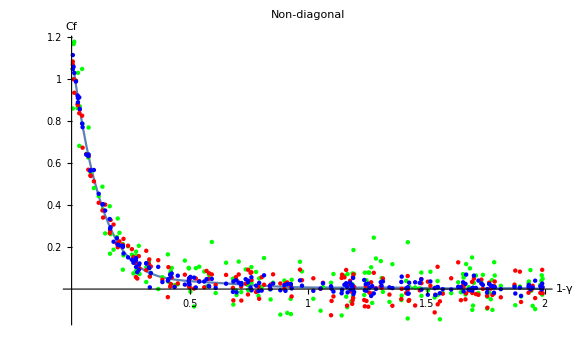

```mathematica
ndiagLo=Show[Cfg2,g2up,PlotRange->All,AxesLabel->{"1-γ","Cf"},AxesStyle->Directive[15,Bold],ImageSize->Large,PlotLabel-> "Non-diagonal",LabelStyle-> Directive[15,Bold],Ticks->{{0.5,1,1.5,2},{0.2,0.4,0.6,0.8,1,1.2}}]
```

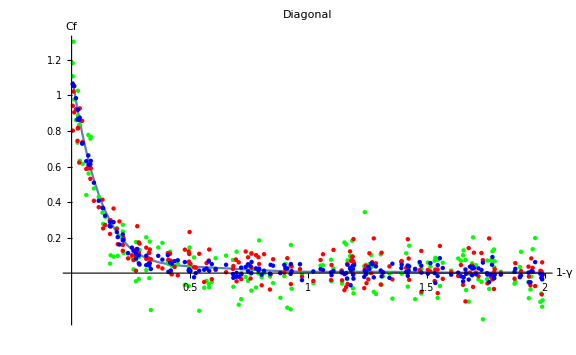

```mathematica
diagLo=Show[Cfg2,g2diag,PlotRange->All,AxesLabel->{"1-γ","Cf"},AxesStyle->Directive[15,Bold],ImageSize->Large,PlotLabel-> "Diagonal",LabelStyle-> Directive[15,Bold],Ticks->{{0.5,1,1.5,2},{0.2,0.4,0.6,0.8,1,1.2}}]
```

```mathematica
Export["nondiagonal lorentzian.png",ndiagLo]
Export["diagonal lorentzian.png",diagLo]
```

nondiagonal lorentzian.png

diagonal lorentzian.png

#### Matrix graph -g3, diagonal and nondiagonal - Gaussian

```mathematica
Cf3=ⅇ^(-20 (1-x)^2);clg3=Clcalc[Cf3,5]//Timing
clg3test=Clcalc[Cf3,3]//Timing
g3points=Table[{RandomVariate[UniformDistribution[{0,π}]],RandomVariate[UniformDistribution[{0,2π}]]},300];γg3=Table[normal[g3points][[1+j]].normal[g3points][[2+j]],{j,0,Length[g3points]-2,2}];
xg3=1-γg3;
```

{0.0625,{1.24512,1.08804,0.820569,0.516462,0.247467,0.0590971}}

{0.015625,{1.24512,1.08804,0.820569,0.516462}}

```mathematica
N[1/Sqrt[30000]]
```

0.0057735

```mathematica
m50=randMMat[clg3,g3points,3,50];//Timing
m50test=randMMat[clg3test,g3points,3,50];//Timing
```

{221.281,Null}

{150.,Null}

```mathematica
m100=randMMat[clg3,g3points,3,100];//Timing
m100test=randMMat[clg3test,g3points,3,100];//Timing
```

{447.016,Null}

{298.625,Null}

```mathematica
m500=randMMat[clg3,g3points,3,500];//Timing
m500test=randMMat[clg3test,g3points,3,500];//Timing
```

{2207.52,Null}

{1490.7,Null}

```mathematica
xg3=1-γg3;
```

```mathematica
MMcheckp1p2[m50,g3points,clg3]
up50g3=meanup;diag50g3=meandiag;
listplotN50up3=Table[{xg3[[i]],Re[up50g3[[i]]]},{i,1,Length[xg3]}];
listplotN50diag3=Table[{xg3[[i]],diag50g3[[i]]},{i,1,Length[xg3]}];
MMcheckp1p2[m100,g3points,clg3]
up100g3=meanup;diag100g3=meandiag;
listplotN100up3=Table[{xg3[[i]],Re[up100g3[[i]]]},{i,1,Length[xg3]}];
listplotN100diag3=Table[{xg3[[i]],diag100g3[[i]]},{i,1,Length[xg3]}];
MMcheckp1p2[m500,g3points,clg3]
up500g3=meanup;diag500g3=meandiag;
listplotN500up3=Table[{xg3[[i]],Re[up500g3[[i]]]},{i,1,Length[xg3]}];
listplotN500diag3=Table[{xg3[[i]],diag500g3[[i]]},{i,1,Length[xg3]}];
MMcheckp1p2[m50test,g3points,clg3test]
up50g3t=meanup;diag50g3t=meandiag;
listplotN50up3t=Table[{xg3[[i]],Re[up50g3t[[i]]]},{i,1,Length[xg3]}];
listplotN50diag3t=Table[{xg3[[i]],diag50g3t[[i]]},{i,1,Length[xg3]}];
MMcheckp1p2[m100test,g3points,clg3test]
up100g3t=meanup;diag100g3t=meandiag;
listplotN100up3t=Table[{xg3[[i]],Re[up100g3t[[i]]]},{i,1,Length[xg3]}];
listplotN100diag3t=Table[{xg3[[i]],diag100g3t[[i]]},{i,1,Length[xg3]}];
MMcheckp1p2[m500test,g3points,clg3test]
up500g3t=meanup;diag500g3t=meandiag;
listplotN500up3t=Table[{xg3[[i]],Re[up500g3t[[i]]]},{i,1,Length[xg3]}];
listplotN500diag3t=Table[{xg3[[i]],diag500g3t[[i]]},{i,1,Length[xg3]}];
```

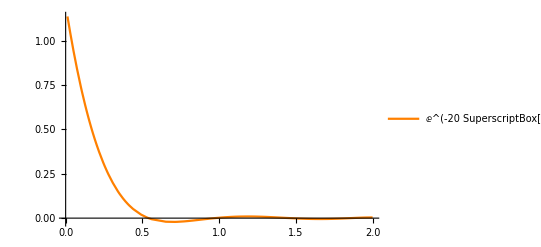

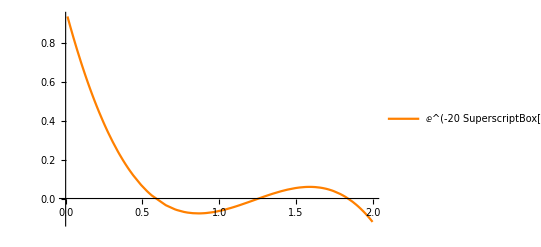

```mathematica
yg3a=sumtestclp1p2[clg3,g3points];listplotAg3=Table[{xg3[[i]],yg3a[[i]]},{i,1,Length[xg3]}];
Cfg3=ListLinePlot[Sort@listplotAg3,PlotRange->All,PlotLegends->Placed[Style[#,15]&/@{" ⅇ^(-20 SuperscriptBox[(1 - x), 2])"},{0.9,0.7}],PlotStyle->Orange]
yg3at=sumtestclp1p2[clg3test,g3points];listplotAg3t=Table[{xg3[[i]],yg3at[[i]]},{i,1,Length[xg3]}];
Cfg3test=ListLinePlot[Sort@listplotAg3t,PlotRange->All,PlotLegends->Placed[Style[#,15]&/@{" ⅇ^(-20 SuperscriptBox[(1 - x), 2])"},{0.9,0.7}],PlotStyle->Orange]
```

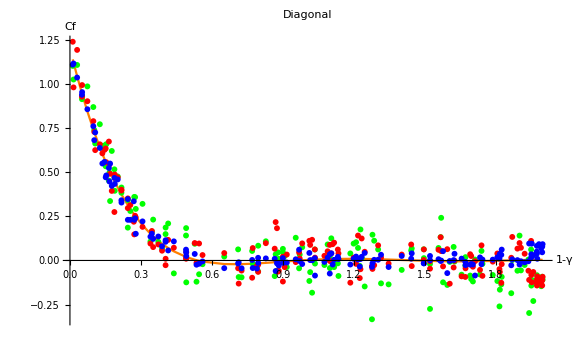

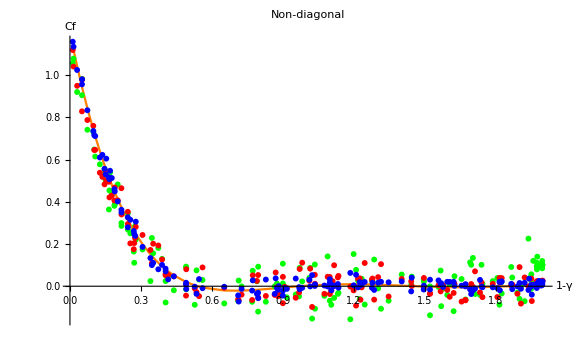

```mathematica
g3up=ListPlot[{Sort@listplotN50up3,Sort@listplotN100up3,Sort@listplotN500up3},AxesLabel->{"1-γ","Cf"},PlotStyle->{Green,Red,Blue},PlotLegends->Placed[Style[#,15]&/@{"50.Mat","100.Mat","500.Mat"},{0.9,0.7}]];
g3diag=ListPlot[{Sort@listplotN50diag3,Sort@listplotN100diag3,Sort@listplotN500diag3},AxesLabel->{"1-γ","Cf"},PlotLegends->Placed[Style[#,15]&/@{"50.Mat","100.Mat","500.Mat"},{0.9,0.7}],PlotStyle->{Green,Red,Blue}];
Matgaussdiaglmax5=Show[Cfg3,g3diag,PlotRange->All,AxesLabel->{"1-γ","Cf"},AxesStyle->Directive[15,Bold],ImageSize->Large,PlotLabel-> "Diagonal",LabelStyle-> Directive[15,Bold]]
Matgaussuplmax5=Show[Cfg3,g3up,PlotRange->All,AxesLabel->{"1-γ","Cf"},AxesStyle->Directive[15,Bold],ImageSize->Large,PlotLabel-> "Non-diagonal",LabelStyle-> Directive[15,Bold]]
```

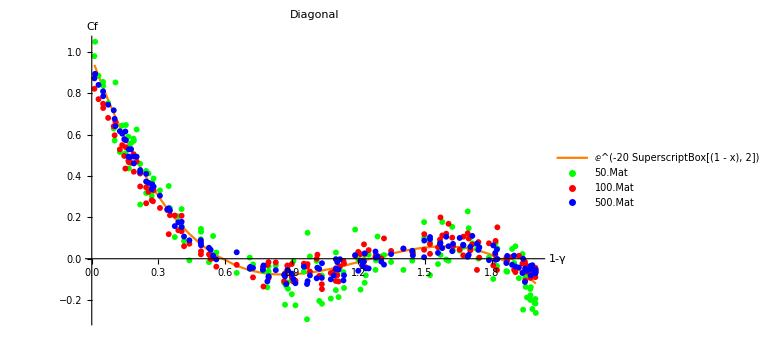

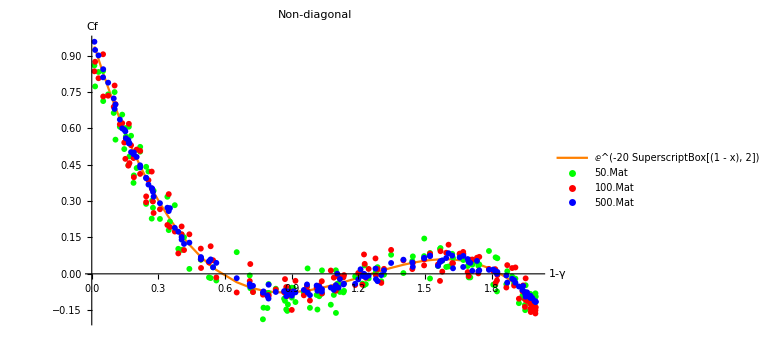

```mathematica
g3uptest=ListPlot[{Sort@listplotN50up3t,Sort@listplotN100up3t,Sort@listplotN500up3t},AxesLabel->{"1-γ","Cf"},PlotStyle->{Green,Red,Blue},PlotLegends->{"50.Mat","100.Mat","500.Mat"}];
g3diagtest=ListPlot[{Sort@listplotN50diag3t,Sort@listplotN100diag3t,Sort@listplotN500diag3t},AxesLabel->{"1-γ","Cf"},PlotLegends->{"50.Mat","100.Mat","500.Mat"},PlotStyle->{Green,Red,Blue}];
Matgaussdiaglmax3=Show[Cfg3test,g3diagtest,PlotRange->All,AxesLabel->{"1-γ","Cf"},AxesStyle->Directive[15,Bold],ImageSize->Large,PlotLabel-> "Diagonal",LabelStyle-> Directive[15,Bold]]
Matgaussuplmax3=Show[Cfg3test,g3uptest,PlotRange->All,AxesLabel->{"1-γ","Cf"},AxesStyle->Directive[15,Bold],ImageSize->Large,PlotLabel-> "Non-diagonal",LabelStyle-> Directive[15,Bold]]
```

```mathematica
Export["gaussian lmax=3 diagonal.png",Matgaussdiaglmax3]
Export["gaussian lmax=3 nondiagonal.png",Matgaussuplmax3]
Export["gaussian lmax=5 diagonal.png",Matgaussdiaglmax5]
Export["gaussian lmax=5 nondiagonal.png",Matgaussuplmax5]
```

gaussian lmax=3 diagonal.png

gaussian lmax=3 nondiagonal.png

gaussian lmax=5 diagonal.png

gaussian lmax=5 nondiagonal.png